## SOLVER DEFS

## FEM DEFINITIONS

### DEFS defs

```mathematica
Off[General::spell];
Off[General::spell1];

Clear[δ];

δ[exp_]:=exp/.{a[any__] -> δa[any],b[any__] -> δb[any],c[any__] -> δc[any],
ux[any__]->δux[any],uy[any__]->δuy[any],uz[any__]->δuz[any],
θx[any__]->δθx[any],θy[any__]->δθy[any],θz[any__]->δθz[any],
uX[any__]->δuX[any],uY[any__]->δuY[any],uZ[any__]->δuZ[any],
θX[any__]->δθX[any],θY[any__]->δθY[any],θZ[any__]->δθZ[any],
Fx[any__]->δFx[any],Fy[any__]->δFy[any],Fz[any__]->δFz[any],
Mx[any__]->δMx[any],My[any__]->δMy[any],Mz[any__]->δMz[any],
FX[any__]->δFX[any],FY[any__]->δFY[any],FZ[any__]->δFZ[any],
MX[any__]->δMX[any],MY[any__]->δMY[any],MZ[any__]->δMZ[any],
FN[any__]->δFN[any],FT[any__]->δFT[any],FB[any__]->δFB[any],
MN[any__]->δMN[any],MT[any__]->δMT[any],MB[any__]->δMB[any],
ϑ[any__]->δϑ[any]};

δUN[exp_]:=exp/.{δa[any__] -> a[any],δb[any__] -> b[any], δc[any__] ->c[any],
 δux[any__]->ux[any], δuy[any__]->uy[any], δuz[any__]->uz[any],
 δθx[any__]->θx[any], δθy[any__]->θy[any], δθz[any__]->θz[any],
 δuX[any__]->uX[any], δuY[any__]->uY[any], δuZ[any__]->uZ[any],
 δθX[any__]->θX[any], δθY[any__]->θY[any], δθZ[any__]->θZ[any],
 δFx[any__]->Fx[any], δFy[any__]->Fy[any], δFz[any__]->Fz[any],
 δMx[any__]->Mx[any], δMy[any__]->My[any], δMz[any__]->Mz[any],
 δFX[any__]->FX[any], δFY[any__]->FY[any], δFZ[any__]->FZ[any],
 δMX[any__]->MX[any], δMY[any__]->MY[any], δMZ[any__]->MZ[any],
 δFN[any__]->FN[any], δFT[any__]->FT[any], δFB[any__]->FB[any],
 δMN[any__]->MN[any], δMT[any__]->MT[any], δMB[any__]->MB[any],
 δϑ[any__]->ϑ[any]};

DOFS[exp_] :=Union[Cases[{exp},a[__]|b[__]|c[__] |uX[__]|uY[__]|uZ[__]| θX[__]| θY[__]|θZ[__]|ux[__]|uy[__]|uz[__]| θx[__]| θy[__]|θz[__]|FX[__]|FY[__]|FZ[__]| MX[__]| MY[__]|MZ[__]|FN[__]|FT[__]|FB[__]| MN[__]| MT[__]|MB[__]|Fx[__]|Fy[__]|Fz[__]| Mx[__]| My[__]|Mz[__]| ϑ[__],Infinity]];

DFFS[exp_] :=Union[Cases[{exp},FX[__]|FY[__]|FZ[__]| MX[__]| MY[__]|MZ[__]|FN[__]|FT[__]|FB[__]| MN[__]| MT[__]|MB[__]|Fx[__]|Fy[__]|Fz[__]| Mx[__]| My[__]|Mz[__],Infinity]];

δDFFS[exp_] :=Union[Cases[{exp},δFX[__]|δFY[__]|δFZ[__]| δMX[__]| δMY[__]|δMZ[__]|δFN[__]|δFT[__]|δFB[__]| δMN[__]| δMT[__]|δMB[__]|δFx[__]|δFy[__]|δFz[__]| δMx[__]| δMy[__]|δMz[__],Infinity]];

δDOFS[exp_] :=Union[Cases[{exp},δa[__]|δb[__]|δc[__] |δuX[__]|δuY[__]|δuZ[__]| δθX[__]| δθY[__]|δθZ[__]|δux[__]|δuy[__]|δuz[__]| δθx[__]| δθy[__]|δθz[__]|δFX[__]|δFY[__]|δFZ[__]| δMX[__]| δMY[__]|δMZ[__]|δFN[__]|δFT[__]|δFB[__]| δMN[__]| δMT[__]|δMB[__]|δFx[__]|δFy[__]|δFz[__]| δMx[__]| δMy[__]|δMz[__]| δϑ[__],Infinity]];

DOFS[exp_,n_] :=Union[Cases[{exp},a[__,n]|b[__,n]|c[__,n] |uX[__,n]|uY[__,n]|uZ[__,n]| θX[__,n]| θY[__,n]|θZ[__,n]|ux[__,n]|uy[__,n]|uz[__,n]| θx[__,n]| θy[__,n]|θz[__,n]|FX[__,n]|FY[__,n]|FZ[__,n]| MX[__,n]| MY[__,n]|MZ[__,n]|FN[__,n]|FT[__,n]|FB[__,n]| MN[__,n]| MT[__,n]|MB[__,n]|Fx[__,n]|Fy[__,n]|Fz[__,n]| Mx[__,n]| My[__,n]|Mz[__,n]| ϑ[__,n],Infinity]];

δDOFS[exp_,n_] :=Union[Cases[{exp},δa[__,n]|δb[__,n]|δc[__,n] |δuX[__,n]|δuY[__,n]|δuZ[__,n]| δθX[__,n]| δθY[__,n]|δθZ[__,n]|δux[__,n]|δuy[__,n]|δuz[__,n]| δθx[__,n]| δθy[__,n]|δθz[__,n]|δFX[__,n]|δFY[__,n]|δFZ[__,n]| δMX[__,n]| δMY[__,n]|δMZ[__,n]|δFN[__,n]|δFT[__,n]|δFB[__,n]| δMN[__,n]| δMT[__,n]|δMB[__,n]|δFx[__,n]|δFy[__,n]|δFz[__,n]| δMx[__,n]| δMy[__,n]|δMz[__,n]| δϑ[__,n],Infinity]];

DRULE[n_]:= {
a[any__]-> a[any,n],b[any__]-> b[any,n],c[any__]-> c[any,n],uX[any__]-> uX[any,n],uY[any__]-> uY[any,n],uZ[any__]-> uZ[any,n],
θX[any__]-> θX[any,n],θY[any__]-> θY[any,n],θZ[any__]-> θZ[any,n],
ux[any__]-> ux[any,n],uy[any__]-> uy[any,n],uz[any__]-> uz[any,n],
θx[any__]-> θx[any,n],θy[any__]-> θy[any,n],θz[any__]-> θz[any,n],
FX[any__]-> FX[any,n],FY[any__]-> FY[any,n],FZ[any__]-> FZ[any,n],
MX[any__]-> MX[any,n],MY[any__]-> MY[any,n],MZ[any__]-> MZ[any,n],
FN[any__]-> FN[any,n],FT[any__]-> FT[any,n],FB[any__]-> FB[any,n],
MN[any__]-> MN[any,n],MT[any__]-> MT[any,n],MB[any__]-> MB[any,n]};

δδ[u_]:=Module[{dof},dof=DOFS[u];
If[dof=={} ,u*0,D[u,{dof}].δ[dof]]];
```

### SHAPE defs

```mathematica
SHAPES1[h_]:= {1-(x/h),(x/h)};

SHAPES11[h_]:= {(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 (x/h),(3-2 x/h) (x/h)^2,h(x/h)^2 (-1+x/h)};

LAGRANGE[n_,h_]:= Simplify[MapIndexed[(#1/(#1/.x->h*(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[x-h*(ii-1)/(n-1),{ii,1,n}]]/(x-h*(jj-1)/(n-1)),{jj,1,n}]]];

LAGRANGE[n_,{x0_,x1_}]:= Simplify[MapIndexed[(#1/(#1/.x->x0+(x1-x0)*(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[x-(x0+(x1-x0)*(ii-1)/(n-1)),{ii,1,n}]]/(x-(x0+(x1-x0)*(jj-1)/(n-1))),{jj,1,n}]]];

LAGRANGE[n_,{x,{x0_,x1_}}]:= Simplify[MapIndexed[(#1/(#1/.x->x0+(x1-x0)*(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[x-(x0+(x1-x0)*(ii-1)/(n-1)),{ii,1,n}]]/(x-(x0+(x1-x0)*(jj-1)/(n-1))),{jj,1,n}]]];

SHAPES1[bas_,ver_]:= Simplify[bas . Inverse[Flatten[Map[{bas}/. {x->#[[1]]}&, ver],1]]];

SHAPES11[bas_,ver_]:= bas . Inverse[Flatten[Map[{bas,D[bas, x]}/. {x->#[[1]]}&, ver],1]];

SHAPES2[bas_,ver_]:= bas . Inverse[Flatten[Map[{bas}/. {x->#[[1]],y->#[[2]]}&, ver],1]];

SHAPES21[{{x1_,y1_},{x2_,y2_}}]:= Module[{Nx,Ny},
Nx= SHAPES11[{1,x,x^2,x^3},{{x1},{x2}}];
Ny= SHAPES11[{1,x,x^2,x^3},{{y1},{y2}}] /. x->y;
Return[{Nx[[1]]*Ny[[1]],Nx[[2]]*Ny[[1]],Nx[[1]]*Ny[[2]],Nx[[3]]*Ny[[1]],Nx[[4]]*Ny[[1]],Nx[[3]]*Ny[[2]],Nx[[1]]*Ny[[3]],Nx[[2]]*Ny[[3]],Nx[[1]]*Ny[[4]],Nx[[3]]*Ny[[3]],Nx[[4]]*Ny[[3]],Nx[[3]]*Ny[[4]]}]];

SHAPES3[bas_,ver_]:= bas . Inverse[Flatten[Map[{bas}/. {x->#[[1]],y->#[[2]],z->#[[3]]}&, ver],1]];

SHAPES1[h_]:= {1-(x/h),(x/h)};

SHAPES11[h_]:= {(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 (x/h),(3-2 x/h) (x/h)^2,h(x/h)^2 (-1+x/h)};

LAGRANGE[n_,h_]:= Simplify[MapIndexed[(#1/(#1/.x->h*(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[x-h*(ii-1)/(n-1),{ii,1,n}]]/(x-h*(jj-1)/(n-1)),{jj,1,n}]]];

LAGRANGE[{{n_,r_}}]:= Simplify[MapIndexed[(#1/(#1/.r->(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[r-(ii-1)/(n-1),{ii,1,n}]]/(r-(jj-1)/(n-1)),{jj,1,n}]]];

LAGRANGE[{{n_,r_},{m_,s_}}]:= Flatten[Outer[Times,LAGRANGE[{{m,s}}],LAGRANGE[{{n,r}}]],1];

LAGRANGE[{{n_,r_},{m_,s_},{k_,t_}}]:= Flatten[Outer[Times,LAGRANGE[{{k,t}}],LAGRANGE[{{m,s}}],LAGRANGE[{{n,r}}]],2];

LAGRANGE[n_,{x0_,x1_}]:= Simplify[MapIndexed[(#1/(#1/.x->x0+(x1-x0)*(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[x-(x0+(x1-x0)*(ii-1)/(n-1)),{ii,1,n}]]/(x-(x0+(x1-x0)*(jj-1)/(n-1))),{jj,1,n}]]];

LAGRANGE[n_,{x,{x0_,x1_}}]:= Simplify[MapIndexed[(#1/(#1/.x->x0+(x1-x0)*(#2[[1]]-1)/(n-1)))&,Table[Apply[Times,Table[x-(x0+(x1-x0)*(ii-1)/(n-1)),{ii,1,n}]]/(x-(x0+(x1-x0)*(jj-1)/(n-1))),{jj,1,n}]]];

SHAPES1[bas_,ver_]:= Simplify[bas . Inverse[Flatten[Map[{bas}/. {x->#[[1]]}&, ver],1]]];

SHAPES11[bas_,ver_]:= bas . Inverse[Flatten[Map[{bas,D[bas, x]}/. {x->#[[1]]}&, ver],1]];

SHAPES2[bas_,ver_]:= bas . Inverse[Flatten[Map[{bas}/. {x->#[[1]],y->#[[2]]}&, ver],1]];

SHAPES21[{{x1_,y1_},{x2_,y2_}}]:= Module[{Nx,Ny},
Nx= SHAPES11[{1,x,x^2,x^3},{{x1},{x2}}];
Ny= SHAPES11[{1,x,x^2,x^3},{{y1},{y2}}] /. x->y;
Return[{Nx[[1]]*Ny[[1]],Nx[[2]]*Ny[[1]],Nx[[1]]*Ny[[2]],Nx[[3]]*Ny[[1]],Nx[[4]]*Ny[[1]],Nx[[3]]*Ny[[2]],Nx[[1]]*Ny[[3]],Nx[[2]]*Ny[[3]],Nx[[1]]*Ny[[4]],Nx[[3]]*Ny[[3]],Nx[[4]]*Ny[[3]],Nx[[3]]*Ny[[4]]}]];

SHAPES3[bas_,ver_]:= bas . Inverse[Flatten[Map[{bas}/. {x->#[[1]],y->#[[2]],z->#[[3]]}&, ver],1]];
```

### QUAD defs

```mathematica
QUAD[LIN1,exp_,var_]:=Module[{w,p},
p={{1}}/2;
w={1};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN2,exp_,var_]:=Module[{w,p},
p={{0},{1}};
w={1,1}/2;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN2G,exp_,var_]:=Module[{w,p},
p={{0.21132486540518713},{0.7886751345948129}};
w={1,1}/2;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN3,exp_,var_]:=Module[{w,p},
p={{0},{1},{2}}/2;
w={1,4,1}/6;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN3G,exp_,var_]:=Module[{w,p},
p={{0.1127016653792583},{0.5},{0.8872983346207417}};
w={0.2777777777777777,0.44444444444444453,0.2777777777777777};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN5,exp_,var_]:=Module[{w,p},
p={{0},{1},{2},{3},{4}}/4;
w={7,32,12,32,7}/90;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN7,exp_,var_]:=Module[{w,p},
p={{0},{1},{2},{3},{4},{5},{6}}/6;
w={41,216,27,272,27,216,41}/840;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[LIN14,exp_,var_]:=Module[{w,p},
p=Table[ii,{ii,0,13}]/13;
w={8181904909/402361344000,56280729661/402361344000,-1737125143/22353408000,11148172711/28740096000,-6066382933/16094453760,22964826443/44706816000,-3592666051/33530112000,-3592666051/33530112000,22964826443/44706816000,-6066382933/16094453760,11148172711/28740096000,-1737125143/22353408000,56280729661/402361344000,8181904909/402361344000};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI1,exp_,var_]:=Module[{w,p},
p={{1,1}}/3;
w={1}/2;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI3,exp_,var_]:=Module[{w,p},
p={{0,1},{1,0},{1,1}}/2;
w={1,1,1}/6;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI4,exp_,var_]:=Module[{w,p},
p={{0,0},{1,0},{0,1},{1,1}/3};
w=1/24*{1,1,1,9};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI41,exp_,var_]:=Module[{w,p},
p={{1,0}/2,{1,1}/2,{0,1}/2,{1,1}/3};
w=1/120*{11,11,11,27};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI7,exp_,var_]:=Module[{w,p},
p={{0,0},{1/2,0},{1,0},{1/2,1/2},{0,1},{0,1/2},{1/3,1/3}};
w={1/40,1/15,1/40,1/15,1/40,1/15,9/40};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI12,exp_,var_]:=Module[{w,p},
p={{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{1,3},{2,0},{2,1},{2,2},{3,0},{3,1}}/4;
w={4,-1,4,4,8,8,4,-1,8,-1,4,4}/90;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI28,exp_,var_]:=Module[{w,p},
p={{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{2,0},{2,1},{2,2},{2,3},{2,4},{3,0},{3,1},{3,2},{3,3},{4,0},{4,1},{4,2},{5,0},{5,1},{6,0}}/6;
w={0,36,-27,64,-27,36,0,36,72,72,72,72,36,-27,72,-54,72,-27,64,72,72,64,-27,72,-27,36,36,0}/(3.*560);
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TRI1,exp_,var_,map_]:=Module[{w,p},
p={{1,1}}/3;
w={1}/2;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->map[#1]]&,p]]];

QUAD[TRI3,exp_,var_,map_]:=Module[{w,p},
p={{0,1},{1,0},{1,1}}/2;
w={1,1,1}/6;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->map[#1]]&,p]]];

QUAD[TRI4,exp_,var_,map_]:=Module[{w,p},
p={{0,0},{1,0},{0,1},{1,1}/3};
w=1/24*{1,1,1,9};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->map[#1]]&,p]]];

QUAD[TRI7,exp_,var_,map_]:=Module[{w,p},
p={{0,0},{1/2,0},{1,0},{1/2,1/2},{0,1},{0,1/2},{1/3,1/3}};
w={1/40,1/15,1/40,1/15,1/40,1/15,9/40};
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->map[#1]]&,p]]];

QUAD[TRI12,exp_,var_,map_]:=Module[{w,p},
p={{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{1,3},{2,0},{2,1},{2,2},{3,0},{3,1}}/4;
w={4,-1,4,4,8,8,4,-1,8,-1,4,4}/90;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->map[#1]]&,p]]];

QUAD[TRI28,exp_,var_,map_]:=Module[{w,p},
p={{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{2,0},{2,1},{2,2},{2,3},{2,4},{3,0},{3,1},{3,2},{3,3},{4,0},{4,1},{4,2},{5,0},{5,1},{6,0}}/6;
w={0,36,-27,64,-27,36,0,36,72,72,72,72,36,-27,72,-54,72,-27,64,72,72,64,-27,72,-27,36,36,0}/(3.*560);
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->map[#1]]&,p]]];

QUAD[REC9,exp_,var_]:=Module[{w,p},
p={{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}}/2;
w={1,4,1,4,16,4,1,4,1}/36;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[HEX27,exp_,var_]:=Module[{w,p},
p={{0,0,0},{0,0,1},{0,0,2},{0,1,0},{0,1,1},{0,1,2},{0,2,0},{0,2,1},{0,2,2},{1,0,0},{1,0,1},{1,0,2},{1,1,0},{1,1,1},{1,1,2},{1,2,0},{1,2,1},{1,2,2},{2,0,0},{2,0,1},{2,0,2},{2,1,0},{2,1,1},{2,1,2},{2,2,0},{2,2,1},{2,2,2}}/2;
w={1,4,1,4,16,4,1,4,1,4,16,4,16,64,16,4,16,4,1,4,1,4,16,4,1,4,1}/6^3;
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TET5,exp_,var_]:=Module[{
w={-16,9,9,9,9}/120,p=Transpose[{{1/4,1/2,1/6,1/6,1/6},{1/4,1/6,1/6,1/6,1/2},{1/4,1/6,1/6,1/2,1/6}}]},
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];

QUAD[TET10,exp_,var_]:=Module[{
w={-1,-1,-1,-1,4,4,4,4,4,4}/120,p={{1,0,0},{0,1,0},{0,0,1},{0,0,0},{1,1,0}/2,{1,0,1}/2,{1,0,0}/2,{0,1,1}/2,{0,1,0}/2,{0,0,1}/2}},
Apply[Plus,MapIndexed[w[[#2[[1]]]]*exp /.Thread[var->#1]&,p]]];
```

```mathematica
tet=Tetrahedron[{{1,0,0},{0,1,0},{0,0,1},{0,0,0}}];

p={{1,0,0},{0,1,0},{0,0,1},{0,0,0},{1,1,0}/2,{1,0,1}/2,{1,0,0}/2,{0,1,1}/2,{0,1,0}/2,{0,0,1}/2};
fun={1,x,y,z,x y,x z, y z, x^2, y^2,z^2};

eq[i_]:= Array[w,10].(Map[fun[[i]] /.Thread[{x,y,z}->#]&,p])-Integrate[fun[[i]],{x,y,z}∈tet];

sol=Solve[Thread[Table[eq[i],{i,1,10}]==0],Array[w,10]][[1]];

120*Array[w,10] /.sol

Apply[Plus,Array[w,10] /.sol]
```

{-1,-1,-1,-1,4,4,4,4,4,4}

1/6

### INTEGRATE defs

```mathematica
INTEGRATE[{LINE,exp_},{ele_,fun_}]:=
Apply[Plus,Map[QUAD[{LINLINE,exp},#]&,ele]];

RULE[{LINE,{iy_},list_}]:= Module[{ix,iz,hx,nn},
{ix,hx} = UNIT[XYZ[Last[list]]-XYZ[First[list]]];
iz = CROSS[ix,iy];
nn = Length[list];
xrule = Table[x[ii]-> ix.XYZ[list[[ii]]],{ii,1,nn}];
yrule = Table[y[ii]-> iy.XYZ[list[[ii]]],{ii,1,nn}];
zrule = Table[z[ii]-> iz.XYZ[list[[ii]]],{ii,1,nn}];
Flatten[Join[xrule,yrule,zrule]]];

QUAD[{LINLINE,exp_},element_]:= Module[{NN,rule,xx,yy,zz,J,int},
NN = {1-ξ,ξ};
rule = RULE[element];
xx = NN.{x[1],x[2]} /. rule;
yy = NN.{y[1],y[2]} /. rule;
zz = NN.{z[1],z[2]} /. rule;
J = Sqrt[(D[xx, ξ])^2+(D[yy, ξ])^2+(D[zz, ξ])^2];
int = J*exp /. {x->xx, y->yy, z->zz};
QUADE[QTYPE,(int /. ξ-> #1)&]];

QUADE[LINE1,exp_]:= exp[{1/2}].{1};
QUADE[LINE2,exp_]:= exp[{0,1}].{1,1}/2;
QUADE[LINE3,exp_]:= exp[{0,1,2}/2].{1,4,1}/6;
```

## FORCE MODEL

### NULL ELEMENT defs

```mathematica
(*MEC-E1050|E8001 defs*)

(*should anything go wrong, do this*)
δW[analysistype_,ele_,fun_]:=0;
```

### FORCE ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{FORCE,{FX_,FY_,FZ_},Point[{n1_}]},fun_]:=
δW[DISP,{FORCE,{FX,FY,FZ,0,0,0},Point[{n1}]},fun];

δW[DISP,{FORCE,{FX_,FY_,FZ_,MX_,MY_,MZ_},Point[{n1_}]},fun_]:=
{FX,FY,FZ}.δ[fun[[n1,2]]]+{MX,MY,MZ}.δ[fun[[n1,3]]];

δW[DISP,{FORCE,{fX_,fY_,fZ_},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{FORCE,{{fX,fX},{fY,fY},{fZ,fZ}},Line[{n1,n2}]},fun];

δW[DISP,{FORCE,{{fX1_,fX2_},{fY1_,fY2_},{fZ1_,fZ2_}} ,Line[{n1_,n2_}]},fun_]:=Module[{nl,r0,h0},
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];

h0/6*(δ[fun[[{n1,n2},2,1]]].{{2,1},{1,2}}.{fX1,fX2} +δ[fun[[{n1,n2},2,2]]].{{2,1},{1,2}}.{fY1,fY2}+
δ[fun[[{n1,n2},2,3]]].{{2,1},{1,2}}.{fZ1,fZ2}) ];

(*area force*)

δW[DISP,{FORCE,{fX_,fY_,fZ_} ,Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{FORCE,{{fX,fX,fX},{fY,fY,fY},{fZ,fZ,fZ}} ,Polygon[{n1,n2,n3}]},fun]

δW[DISP,{FORCE,{{fX1_,fX2_,fX3_},{fY1_,fY2_,fY3_},{fZ1_,fZ2_,fZ3_}} ,Polygon[{n1_,n2_,n3_}]},fun_]:=
Area[Polygon[fun[[{n1,n2,n3},1]]]]/12*(δ[fun[[{n1,n2,n3},2,1]]].{{2,1,1},{1,2,1},{1,1,2}}.{fX1,fX2,fX3} +δ[fun[[{n1,n2,n3},2,2]]].{{2,1,1},{1,2,1},{1,1,2}}.{fY1,fY2,fY3}+
δ[fun[[{n1,n2,n3},2,3]]].{{2,1,1},{1,2,1},{1,1,2}}.{fZ1,fZ2,fZ3}) ;
```

### FORCE ELEMENT (evnt) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[{EVENT,{s0_,sol0_}},{FORCE,anya_,anyb_},fun_]:=δW[DISP,{FORCE,anya,anyb},fun];
```

### FORCE ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{FORCE,{FX_,FY_,FZ_},Point[{n1_}]},fun_]:=
δW[VIBR,{FORCE,{FX,FY,FZ,0,0,0},Point[{n1}]},fun];

δW[VIBR,{FORCE,{FX_,FY_,FZ_,MX_,MY_,MZ_},Point[{n1_}]},fun_]:=
({FX,FY,FZ}.δ[fun[[n1,2]]/.DRULE[0]]+{MX,MY,MZ}.δ[fun[[n1,3]]/.DRULE[0]]);

δW[VIBR,{FORCE,{fX_,fY_,fZ_},Line[{n1_,n2_}]},fun_]:=
δW[VIBR,{FORCE,{{fX,fX},{fY,fY},{fZ,fZ}},Line[{n1,n2}]},fun];

δW[VIBR,{FORCE,{{fX1_,fX2_},{fY1_,fY2_},{fZ1_,fZ2_}} ,Line[{n1_,n2_}]},fun_]:=Module[{nl,r0,h0},
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];

(h0/6*(δ[fun[[{n1,n2},2,1]]/.DRULE[0]].{{2,1},{1,2}}.{fX1,fX2} +δ[fun[[{n1,n2},2,2]]/.DRULE[0]].{{2,1},{1,2}}.{fY1,fY2}+
δ[fun[[{n1,n2},2,3]]/.DRULE[0]].{{2,1},{1,2}}.{fZ1,fZ2})) ];

δW[VIBR,{FORCE,{fX_,fY_,fZ_} ,Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[VIBR,{FORCE,{{fX,fX,fX},{fY,fY,fY},{fZ,fZ,fZ}} ,Polygon[{n1,n2,n3}]},fun];

δW[VIBR,{FORCE,{{fX1_,fX2_,fX3_},{fY1_,fY2_,fY3_},{fZ1_,fZ2_,fZ3_}} ,Polygon[{n1_,n2_,n3_}]},fun_]:= Area[Polygon[fun[{n1,n2,n3},1]]]/12*(δ[fun[[{n1,n2,n3},2,1]]/.DRULE[0]].{{2,1,1},{1,2,1},{1,1,2}}.{fX1,fX2,fX3}+δ[fun[[{n1,n2,n3},2,2]]/.DRULE[0]].{{2,1,1},{1,2,1},{1,1,2}}.{fY1,fY2,fY3}+δ[fun[[{n1,n2,n3},2,3]]/.DRULE[0]].{{2,1,1},{1,2,1},{1,1,2}}.{fZ1,fZ2,fZ3});

δW[VIBR,{FORCE,{{m_}},Point[{n1_}]},fun_]:=
(-m  fun[[n1,2]]/.DRULE[2]). (δ[fun[[n1,2]] /.DRULE[0]]);

δW[VIBR,{FORCE,{{m_,J_}},Point[{n1_}]},fun_]:=
δW[VIBR,{FORCE,{{m,J},{{1,0,0},{0,1,0}}},Point[{n1}]},fun];

δW[VIBR,{FORCE,{{m_,J_},{ix_,iy_}},Point[{n1_}]},fun_]:=Module[{iz=ix×iy},
-(m fun[[n1,2]]/.DRULE[2]).( δ[fun[[n1,2]]/.DRULE[0]])-
(J.fun[[n1,3]]/.DRULE[2]).(δ[fun[[n1,3]]/.DRULE[0]])];

(*for detailed graphics*)
δW[VIBR,{FORCE,{{m_,J_},{ix_,iy_},{xyz_,obj_}},Point[{n1_}]},fun_]:=δW[VIBR,{FORCE,{{m,J},{ix,iy}},Point[{n1}]},fun];
```

### FORCE ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

δW[STAB,{FORCE,{FX_,FY_,FZ_},Point[{n1_}]},fun_]:=
δW[DISP,{FORCE,{FX,FY,FZ},Point[{n1}]},fun];

δW[STAB,{FORCE,{FX_,FY_,FZ_,MX_,MY_,MZ_},Point[{n1_}]},fun_]:=
δW[DISP,{FORCE,{FX,FY,FZ,MX,MY,MZ},Point[{n1}]},fun];

δW[STAB,{FORCE,{fX_,fY_,fZ_},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{FORCE,{fX,fY,fZ},Line[{n1,n2}]},fun];

δW[STAB,{FORCE,{{fX1_,fX2_},{fY1_,fY2_},{fZ1_,fZ2_}} ,Line[{n1_,n2_}]},fun_]:=δW[DISP,{FORCE,{{fX1,fX2},{fY1,fY2},{fZ1,fZ2}} ,Line[{n1,n2}]},fun];

δW[STAB,{FORCE,{fX_,fY_,fZ_} ,Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{FORCE,{fX,fY,fZ} ,Polygon[{n1,n2,n3}]},fun];

δW[STAB,{FORCE,{{fX1_,fX2_,fX3_},{fY1_,fY2_,fY3_},{fZ1_,fZ2_,fZ3_}} ,Polygon[{n1_,n2_,n3_}]},fun_]:= δW[DISP,{FORCE,{{fX1,fX2,fX3},{fY1,fY2,fY3},{fZ1,fZ2,fZ3}} ,Polygon[{n1,n2,n3}]},fun]
```

### FORCE ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs*)

δW[NONL,{FORCE,{FX_,FY_,FZ_},Point[{n1_}]},fun_]:=
δW[NONL,{FORCE,{FX,FY,FZ,0,0,0},Point[{n1}]},fun];

δW[NONL,{FORCE,{FX_,FY_,FZ_,MX_,MY_,MZ_},Point[{n1_}]},fun_]:=
{FX,FY,FZ}.δ[fun[[n1,2]]]+MY*(-fun[[n1,3,3]]*δ[fun[[n1,3,1]]]+(1+fun[[n1,3,1]])* δ[fun[[n1,3,3]]])/((1+fun[[n1,3,1]])^2+fun[[n1,3,3]]^2);

(*area force*)

δW[NONL,{FORCE,{fX_,fY_,fZ_} ,Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{FORCE,{{fX,fX,fX},{fY,fY,fY},{fZ,fZ,fZ}} ,Polygon[{n1,n2,n3}]},fun]

δW[NONL,{FORCE,{{fX1_,fX2_,fX3_},{fY1_,fY2_,fY3_},{fZ1_,fZ2_,fZ3_}} ,Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{FORCE,{{fX1,fX2,fX3},{fY1,fY2,fY3},{fZ1,fZ2,fZ3}} ,Polygon[{n1,n2,n3}]},fun];
```

### FORCE ELEMENT (tmec) defs

```mathematica
(*MEC-E8001 defs*)

δW[TMEC,{FORCE,anya_,anyb_},fun_]:=
δW[DISP,{FORCE,anya,anyb},fun];
```

## CONSTRAINT MODEL

### CONSTRAINT ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{RIGID,{},Point[{n1_}]},fun_]:=δW[DISP,{RIGID,{{0,0,0},{0,0,0}},Point[{n1}]},fun];

δW[DISP,{RIGID,{{uX1_,uY1_,uZ1_},{θX1_,θY1_,θZ1_}},Point[{n1_}]},fun_]:=δδ[(fun[[n1,2]]-{uX1,uY1,uZ1}).{FX[n1],FY[n1],FZ[n1]}]+
δδ[(fun[[n1,3]]-{θX1,θY1,θZ1}).{MX[n1],MY[n1],MZ[n1]}];

δW[DISP,{RIGID,{},Line[{n1_,n2_}]},fun_]:=
δδ[(fun[[n2,2]]-fun[[n1,2]]-fun[[n1,3]]×(fun[[n2,1]]-fun[[n1,1]])).{FX[{n2,n1}],FY[{n2,n1}],FZ[{n2,n1}]}]+
δδ[(fun[[n2,3]]-fun[[n1,3]]).({MX[{n2,n1}],MY[{n2,n1}],MZ[{n2,n1}]} +
{FX[{n2,n1}],FY[{n2,n1}],FZ[{n2,n1}]}×(fun[[n2,1]]-fun[[n1,1]]))];

δW[DISP,{JOINT,{},Point[{n1_}]},fun_]:=δδ[fun[[n1,2]].{FX[n1],FY[n1],FZ[n1]}];

δW[DISP,{JOINT,{uX1_,uY1_,uZ1_},Point[{n1_}]},fun_]:=δδ[(fun[[n1,2]]-{uX1,uY1,uZ1}).{FX[n1],FY[n1],FZ[n1]}];

δW[DISP,{JOINT,{},Line[{n1_,n2_}]},fun_]:=δδ[(fun[[n1,2]]-fun[[n2,2]]).{FX[n1],FY[n1],FZ[n1]}] ;

δW[DISP,{SLIDER,{nX_,nY_,nZ_},Point[{n1_}]},fun_]:=δδ[(fun[[n1,2]].{nX,nY,nZ})*({nX,nY,nZ}.{FX[n1],FY[n1],FZ[n1]})] ;
```

### CONSTRAINT ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{RIGID,anya_,anyb_},fun_]:=
δW[DISP,{RIGID,anya,anyb},fun];

δW[{EVNT,{s0_,sol0_}},{JOINT,anya_,anyb_},fun_]:=
δW[DISP,{JOINT,anya,anyb},fun];

δW[{EVNT,{s0_,sol0_}},{SLIDER,anya_,anyb_},fun_]:=
δW[DISP,{SLIDER,anya,anyb},fun];

δW[{EVNT,{s0_,sol0_}},{CONTACT,{{nX_,nY_,nZ_},d_},Point[{n1_}]},fun_]:=Module[{U,F,U0,dU0,F0,dF0},
(*events*)
U=({nX,nY,nZ}.fun[[n1,2]]-d);
F=FN[n1];
U0=U/.sol0;dU0=D[U0,s];U0=U0/.s->s0;
F0=F/.sol0;dF0=D[F0,s];F0=F0/.s->s0;
Print[{U0,dU0,F0,dF0}];
(*pick the expression*)
Which[
(U0==0)&& (F0>0),δδ[F*U],
(U0==0)&& (F0<0),Print["fail"];δδ[F*F],
(F0==0)&& (U0>0),δδ[F*F],
(F0==0)&& (U0<0),Print["fail"];δδ[F*U],
(F0==0)&& (U0==0)&& (dU0>0),δδ[F*F],
(F0==0)&& (U0==0)&& (dU0<0),δδ[U*F],True,δδ[U*F]]];

δW[{EVNTPOST,{s0_,sol0_}},{CONTACT,{{nX_,nY_,nZ_},d_},Point[{n1_}]},fun_]:=Module[{UF,k,UF0,Δs},
(*events*)
UF=(({nX,nY,nZ}.fun[[n1,2]]-d)+FN[n1]) /.sol0  /.s->s0+Δs;
UF0=UF /.Δs->0;
k=D[UF,Δs];
Δs=Max[If[k≠0,-UF0/k,0],0];
If[Δs==0,1-s0,Δs]
];
```

### CONSTRAINT ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{RIGID,{},Point[{n1_}]},fun_]:=δδ[(fun[[n1,2]] .{FX[n1],FY[n1],FZ[n1]})/.DRULE[0]]+
δδ[(fun[[n1,3]].{MX[n1],MY[n1],MZ[n1]})/.DRULE[0]];

δW[VIBR,{RIGID,{{uX1_,uY1_,uZ1_},{θX1_,θY1_,θZ1_}},Point[{n1_}]},fun_]:=δδ[((fun[[n1,2]]-{uX1,uY1,uZ1}).{FX[n1],FY[n1],FZ[n1]})/.DRULE[0]]+
δδ[((fun[[n1,3]]-{θX1,θY1,θZ1}).{MX[n1],MY[n1],MZ[n1]})/.DRULE[0]];

δW[VIBR,{RIGID,{},Line[{n1_,n2_}]},fun_]:=
δδ[((fun[[n2,2]]-fun[[n1,2]]-fun[[n1,3]]×(fun[[n2,1]]-fun[[n1,1]])).{FX[{n2,n1}],FY[{n2,n1}],FZ[{n2,n1}]})/.DRULE[0]]+
δδ[((fun[[n2,3]]-fun[[n1,3]]).({MX[{n2,n1}],MY[{n2,n1}],MZ[{n2,n1}]} +
{FX[{n2,n1}],FY[{n2,n1}],FZ[{n2,n1}]}×(fun[[n2,1]]-fun[[n1,1]])))/.DRULE[0]];

δW[VIBR,{JOINT,{},Point[{n1_}]},fun_]:=δδ[(fun[[n1,2]].{FX[n1],FY[n1],FZ[n1]})/.DRULE[0]];

δW[VIBR,{JOINT,{uX1_,uY1_,uZ1_},Point[{n1_}]},fun_]:=δδ[((fun[[n1,2]]-{uX1,uY1,uZ1}).{FX[n1],FY[n1],FZ[n1]})/.DRULE[0]];

δW[VIBR,{JOINT,{},Line[{n1_,n2_}]},fun_]:=δδ[((fun[[n1,2]]-fun[[n2,2]]).{FX[n1],FY[n1],FZ[n1]})/.DRULE[0]] ;

δW[VIBR,{SLIDER,{nX_,nY_,nZ_},Point[{n1_}]},fun_]:=δδ[((fun[[n1,2]].{nX,nY,nZ})*FN[n1])/.DRULE[0]] ;
```

### CONSTRAINT ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

δW[STAB,{RIGID,anya_,anyb_},fun_]:=
δW[DISP,{RIGID,anya,anyb},fun];

δW[STAB,{JOINT,anya_,anyb_},fun_]:=
δW[DISP,{JOINT,anya,anyb},fun];

δW[STAB,{SLIDER,anya_,anyb_},fun_]:=
δW[DISP,{SLIDER,anya,anyb},fun];
```

### CONSTRAINT ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs*)

δW[NONL,{RIGID,anya_,anyb_},fun_]:=
δW[DISP,{RIGID,anya,anyb},fun];

δW[NONL,{JOINT,anya_,anyb_},fun_]:=
δW[DISP,{JOINT,anya,anyb},fun];

δW[NONL,{SLIDER,anya_,anyb_},fun_]:=
δW[DISP,{SLIDER,anya,anyb},fun];
```

### CONSTRAINT ELEMENT (tmec) defs

```mathematica
(*MEC-E8001 defs*)

δW[TMEC,{RIGID,anya_,anyb_},fun_]:=
δW[DISP,{RIGID,anya,anyb},fun];

δW[TMEC,{JOINT,anya_,anyb_},fun_]:=
δW[DISP,{JOINT,anya,anyb},fun];

δW[TMEC,{SLIDER,anya_,anyb_},fun_]:=
δW[DISP,{SLIDER,anya,anyb},fun];
```

## BEAM MODEL

### BAR ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{BAR,{{EE_},{AA_,iy_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_},{AA_,iy_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_},{AA_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA},{0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,ux,δux,EE1,EE2,EE3,AA1,AA2,AA3,fx1,fx2,fx3,nl,rule},

nl={n1,n2};
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[i_]:=ix0.fun[[nl[[i]],2]];
δux[i_]:=δ[ux[i]];

rule :={{a1_,a2_,a3_}->{a1,a2,a3},{a1_,a2_}->{a1,(a1+a2)/2,a2},a1_->{a1,a1,a1}};

{EE1,EE2,EE3}=EE /.rule;
{AA1,AA2,AA3}=AA /.rule;
{fx1,fx2,fx3}=ix0.{fX /.rule,fY /.rule,fZ /.rule};

1/(30 h0^2)(-(AA1 (4 EE1+2 EE2-EE3)+2 AA2 (EE1+8 EE2+EE3)+AA3 (-EE1+2 EE2+4 EE3)) h0 (-ux[1]+ux[2]) (-δux[1]+δux[2])+5 h0^3 (fx1 δux[1]+fx3 δux[2]+2 fx2 (δux[1]+δux[2])))];

δW[DISP,{BAR,{{EE_},{AA_}},Line[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA},{0,0,0}},Line[{n1,n2,n3}]},fun];

δW[DISP,{BAR,{{EE_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_,n3_}]},fun_]:=Module[{r0,h0,ix0,ux,δux,EE1,EE2,EE3,AA1,AA2,AA3,fx1,fx2,fx3,nl,rule},

nl ={n1,n2,n3};
r0=fun[[n3,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[i_]:=ix0.fun[[nl[[i]],2]];
δux[i_]:=δ[ux[i]];

rule :={{a1_,a2_,a3_}->{a1,a2,a3},{a1_,a2_}->{a1,(a1+a2)/2,a2},a1_->{a1,a1,a1}};

{EE1,EE2,EE3}=EE /.rule;
{AA1,AA2,AA3}=AA /.rule;
{fx1,fx2,fx3}=ix0.{fX /.rule,fY /.rule,fZ /.rule};

-1/(210 h0)(7 fx3 h0^2 δux[1]+184 AA1 EE1 ux[1] δux[1]+94 AA2 EE1 ux[1] δux[1]-19 AA3 EE1 ux[1] δux[1]+94 AA1 EE2 ux[1] δux[1]+176 AA2 EE2 ux[1] δux[1]-18 AA3 EE2 ux[1] δux[1]-19 AA1 EE3 ux[1] δux[1]-18 AA2 EE3 ux[1] δux[1]+16 AA3 EE3 ux[1] δux[1]-228 AA1 EE1 ux[2] δux[1]-104 AA2 EE1 ux[2] δux[1]+24 AA3 EE1 ux[2] δux[1]-104 AA1 EE2 ux[2] δux[1]-128 AA2 EE2 ux[2] δux[1]+8 AA3 EE2 ux[2] δux[1]+24 AA1 EE3 ux[2] δux[1]+8 AA2 EE3 ux[2] δux[1]-60 AA3 EE3 ux[2] δux[1]+44 AA1 EE1 ux[3] δux[1]+10 AA2 EE1 ux[3] δux[1]-5 AA3 EE1 ux[3] δux[1]+10 AA1 EE2 ux[3] δux[1]-48 AA2 EE2 ux[3] δux[1]+10 AA3 EE2 ux[3] δux[1]-5 AA1 EE3 ux[3] δux[1]+10 AA2 EE3 ux[3] δux[1]+44 AA3 EE3 ux[3] δux[1]-14 fx3 h0^2 δux[2]-228 AA1 EE1 ux[1] δux[2]-104 AA2 EE1 ux[1] δux[2]+24 AA3 EE1 ux[1] δux[2]-104 AA1 EE2 ux[1] δux[2]-128 AA2 EE2 ux[1] δux[2]+8 AA3 EE2 ux[1] δux[2]+24 AA1 EE3 ux[1] δux[2]+8 AA2 EE3 ux[1] δux[2]-60 AA3 EE3 ux[1] δux[2]+288 AA1 EE1 ux[2] δux[2]+96 AA2 EE1 ux[2] δux[2]-48 AA3 EE1 ux[2] δux[2]+96 AA1 EE2 ux[2] δux[2]+256 AA2 EE2 ux[2] δux[2]+96 AA3 EE2 ux[2] δux[2]-48 AA1 EE3 ux[2] δux[2]+96 AA2 EE3 ux[2] δux[2]+288 AA3 EE3 ux[2] δux[2]-60 AA1 EE1 ux[3] δux[2]+8 AA2 EE1 ux[3] δux[2]+24 AA3 EE1 ux[3] δux[2]+8 AA1 EE2 ux[3] δux[2]-128 AA2 EE2 ux[3] δux[2]-104 AA3 EE2 ux[3] δux[2]+24 AA1 EE3 ux[3] δux[2]-104 AA2 EE3 ux[3] δux[2]-228 AA3 EE3 ux[3] δux[2]+(-28 fx3 h0^2+AA1 (44 EE1 ux[1]+10 EE2 ux[1]-5 EE3 ux[1]-60 EE1 ux[2]+8 EE2 ux[2]+24 EE3 ux[2]+(16 EE1-18 EE2-19 EE3) ux[3])+2 AA2 (5 EE1 ux[1]-24 EE2 ux[1]+5 EE3 ux[1]+4 EE1 ux[2]-64 EE2 ux[2]-52 EE3 ux[2]+(-9 EE1+88 EE2+47 EE3) ux[3])+AA3 (EE1 (-5 ux[1]+24 ux[2]-19 ux[3])+2 (2 EE3 (11 ux[1]-57 ux[2]+46 ux[3])+EE2 (5 ux[1]-52 ux[2]+47 ux[3])))) δux[3]+7 fx1 h0^2 (-4 δux[1]-2 δux[2]+δux[3])-14 fx2 h0^2 (δux[1]+8 δux[2]+δux[3]))];
```

```mathematica
δW[DISP,{BAR,{{EE_},{AA_,iy_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_},{AA_,iy_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,iz0,ux,δux,EE1,EE2,EE3,AA1,AA2,AA3,fx,fx1,fx2,fx3,nl,rule},

nl={n1,n2};
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[i_]:=ix0.fun[[nl[[i]],2]];
δux[i_]:=δ[ux[i]];

rule :={{a1_,a2_,a3_}->{a1,a2,a3},{a1_,a2_}->{a1,(a1+a2)/2,a2},a1_->{a1,a1,a1}};

fx ={fX,fY,fZ}.ix0;

{EE1,EE2,EE3}=EE /.rule;
{AA1,AA2,AA3}=AA /.rule;
{fx1,fx2,fx3}=fx /.rule;

1/(30 h0^2)(-(AA1 (4 EE1+2 EE2-EE3)+2 AA2 (EE1+8 EE2+EE3)+AA3 (-EE1+2 EE2+4 EE3)) h0 (-ux[1]+ux[2]) (-δux[1]+δux[2])+5 h0^3 (fx1 δux[1]+fx3 δux[2]+2 fx2 (δux[1]+δux[2])))];

δW[DISP,{BAR,{{EE_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,ux,δux,δWint,δWext},

r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[1]=ix0.fun[[n1,2]];
ux[2]=ix0.fun[[n2,2]];
δux[1]=δ[ux[1]];
δux[2]=δ[ux[2]];

δWint=-AA EE/h0 *(ux[1]-ux[2]) (δux[1]-δux[2]);
δWext=δ[fun[[n1,2]]+fun[[n2,2]]].{fX,fY,fZ}*h0/2;
δWint+δWext];
```

```mathematica
δW[DISP,{GENERICBAR,{{EE_},{A_},{fx_}},Line[node_]},fun_]:=Module[{NN,ξ,r,rξ,h0,iξ,s,x,uu,δuu,F,δwint,δwext},
(*shape functions*)
NN= LAGRANGE[{{Length[node],ξ}}];
(*mapping to material system*)
r=ξ*(fun[[Last[node],1]]-fun[[First[node],1]]);
rξ=D[r, ξ];
h0=Simplify[Sqrt[rξ.rξ],L>0&&h>0];
iξ =rξ/h0;
s=iξ .r;
x=fun[[First[node],1]].iξ+s ;
(*approximation*)
uu= iξ.(NN.fun[[node,2]]);
(*stress resultant*)
F =EE[x]*A[x] *D[uu, ξ]/h0;
δwint=-δ[D[uu, ξ]/h0]*F ;
δwext=δ[uu]*fx[x] ;
Simplify[Integrate[(δwint+δwext)*h0,{ξ,0,1}], L>0&&h>0]
];
```

```mathematica
(*NEW DEFS*)

δW[DISP,{BAR,{{EE_,νν_},RECTANGLE[ly_,lz_],{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BAR,{{EE,νν},RECTANGLE[ly,lz,{0,1,0}],{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_,νν_},RECTANGLE[ly_,lz_],{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BAR,{{EE,νν},RECTANGLE[ly,lz,{0,1,0}],{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_,νν_},RECTANGLE[ly_,lz_]},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BAR,{{EE,νν},{ly,lz,{0,1,0}},{0,0,0,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_,νν_},RECTANGLE[ly_,lz_,iy_],{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,ux,δux,EE1,EE2,EE3,AA1,AA2,AA3,fx1,fx2,fx3,nl,rule},

nl={n1,n2};
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[i_]:=ix0.fun[[nl[[i]],2]];
δux[i_]:=δ[ux[i]];

rule :={{a1_,a2_,a3_}->{a1,a2,a3},{a1_,a2_}->{a1,(a1+a2)/2,a2},a1_->{a1,a1,a1}};

{EE1,EE2,EE3}=EE /.rule;
{AA1,AA2,AA3}=Map[#[[1]]*#[[2]]&,Transpose[{ly/.rule,lz/.rule}]];
{fx1,fx2,fx3}= Map[#.ix0&,Transpose[{fX/.rule,fY/.rule,fZ/.rule}]];

1/(30 h0^2)(-(AA1 (4 EE1+2 EE2-EE3)+2 AA2 (EE1+8 EE2+EE3)+AA3 (-EE1+2 EE2+4 EE3)) h0 (-ux[1]+ux[2]) (-δux[1]+δux[2])+5 h0^3 (fx1 δux[1]+fx3 δux[2]+2 fx2 (δux[1]+δux[2])))];

(*circle cross-section*)

δW[DISP,{BAR,{{EE_,νν_},CIRCLE[d_],{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BAR,{{EE,νν},CIRCLE[d,{0,1,0}],{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_,νν_},CIRCLE[d_],{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BAR,{{EE,νν},CIRCLE[d,{0,1,0}],{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_,νν_},CIRCLE[d_]},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BAR,{{EE,νν},CIRCLE[d,{0,1,0}],{0,0,0,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BAR,{{EE_,νν_},CIRCLE[d_,iy_],{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,ux,δux,EE1,EE2,EE3,AA1,AA2,AA3,fx1,fx2,fx3,nl,rule},

nl={n1,n2};
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[i_]:=ix0.fun[[nl[[i]],2]];
δux[i_]:=δ[ux[i]];

rule :={{a1_,a2_,a3_}->{a1,a2,a3},{a1_,a2_}->{a1,(a1+a2)/2,a2},a1_->{a1,a1,a1}};

{EE1,EE2,EE3}=EE /.rule;
{AA1,AA2,AA3}=Map[Pi/4*#^2&,d/.rule];
{fx1,fx2,fx3}= Map[#.ix0&,Transpose[{fX/.rule,fY/.rule,fZ/.rule}]];

1/(30 h0^2)(-(AA1 (4 EE1+2 EE2-EE3)+2 AA2 (EE1+8 EE2+EE3)+AA3 (-EE1+2 EE2+4 EE3)) h0 (-ux[1]+ux[2]) (-δux[1]+δux[2])+5 h0^3 (fx1 δux[1]+fx3 δux[2]+2 fx2 (δux[1]+δux[2])))];
```

### BAR ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{BAR,anya_,anyb_},fun_]:=
δW[DISP,{BAR,anya,anyb},fun];
```

### BAR ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{BAR,{{EE_,ρρ_},{AA_}},Line[{n1_,n2_}]},fun_]:=
δW[VIBR,{BAR,{{EE,ρρ},{AA},{0}},Line[{n1,n2}]},fun];

δW[VIBR,{BAR,{{EE_,ρρ_},{AA_},{fx_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,ux,δux,EE1,EE2,EE3,AA1,AA2,AA3,fx1,fx2,fx3,nl,rule},

nl={n1,n2};
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

ux[1,0]=ix0.fun[[n1,2]]/.DRULE[0];
ux[1,2]=ix0.fun[[n1,2]]/.DRULE[2];
ux[2,0]=ix0.fun[[n2,2]]/.DRULE[0];
ux[2,2]=ix0.fun[[n2,2]]/.DRULE[2];
δux[1,0]=δ[ux[1,0]];
δux[2,0]=δ[ux[2,0]];

1/(6 h0)(3 fx h0^2 (δux[1,0]+δux[2,0])-AA (6 EE (ux[1,0]-ux[2,0]) (δux[1,0]-δux[2,0])+h0^2 ρρ (ux[1,2] (2 δux[1,0]+δux[2,0])+ux[2,2] (δux[1,0]+2 δux[2,0]))))];
```

```mathematica
δW[VIBR,{GENERICBAR,{{EE_,ρρ_},{AA_},{ff_}},Line[node_]},fun_]:=Module[{NN,ξ,r,rξ,h0,iξ,s,x,uu,u0,u2,δuu,F,δwint,δwext,δwine,AAA,EEE,ρρρ,fff},
(*shape functions*)
NN= LAGRANGE[{{Length[node],ξ}}];
(*mapping to material system*)
r=ξ*(fun[[Last[node],1]]-fun[[First[node],1]]);
rξ=D[r, ξ];
h0=Simplify[Sqrt[rξ.rξ], L>0&&h>0];
iξ =rξ/h0;
s=iξ .r;
x=fun[[First[node],1]].iξ+s ;
(*approximation*)
uu= iξ.(NN.fun[[node,2]]);
u0= uu/.DRULE[0];
u2= uu /.DRULE[2];
(*stress resultant*)
F =EE[x] AA[x]  D[u0, ξ]/h0;
δwint=-δ[D[u0, ξ]/h0] F ;
δwext=δ[u0] ff[x] ;
δwine=-δ[u0] ρρ[x] AA[x] u2;
Integrate[(δwint+δwext+δwine)*h0,{ξ,0,1}]
];
```

### BAR ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

δW[STAB,{BAR,{{EE_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[STAB,{BAR,{{EE_},{AA_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BAR,{{EE},{AA}},Line[{n1,n2}]},fun];
```

### BAR ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs*)

δW[NONL,{BAR,{{CC_},{AA_}},Line[{n1_,n2_}]},fun_]:=
δW[NONL,{BAR,{{CC},{AA,{0,1,0}},{0,0,0}},Line[{n1,n2}]},fun];

δW[NONL,{BAR,{{CC_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=
δW[NONL,{BAR,{{CC},{AA,{0,1,0}},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[NONL,{BAR,{{CC_},{AA_,iy_}},Line[{n1_,n2_}]},fun_]:=
δW[NONL,{BAR,{{CC},{AA,iy},{0,0,0}},Line[{n1,n2}]},fun];

δW[NONL,{BAR,{{CC_},{AA_,iy_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{Δh,h0,ix,iz,NN,fx,fy,fz,x,uu,vv,ww,EE,δEE,δwint,δwext},
Δh=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[Δh.Δh], L>0&&h>0];
ix=Δh/h0;
iz=ix×iy;
NN= {1-x/h0,x/h0};

fx =ix.{fX,fY,fZ};
fy =iy.{fX,fY,fZ};
fz =iz.{fX,fY,fZ};

uu= NN.{fun[[n1,2]].ix,fun[[n2,2]].ix} ;
vv= NN.{fun[[n1,2]].iy,fun[[n2,2]].iy};
ww= NN.{fun[[n1,2]].iz,fun[[n2,2]].iz};
EE= D[uu, x]+D[{uu,vv,ww}, x].D[{uu,vv,ww}, x]/2;
δEE=δ[D[uu, x]]+δ[D[{uu,vv,ww}, x]].D[{uu,vv,ww}, x];
δwint=-δEE CC AA EE;
δwext=δ[{uu,vv,ww}].{ fx,fy,fz};
Return[Integrate[δwint+δwext,{x,0,h0}]]
];
```

### BAR ELEMENT (tmec) defs

```mathematica
(*MEC-E8001 defs*)

δW[TMEC,{BAR,{{EE_,αα_,kk_},{AA_},{{ss_,ϑ0_}}},Line[node_]},fun_]:=δW[TMEC,{BAR,{{EE,αα,kk},{AA},{{0,0,0},{ss,ϑ0}}},Line[node]},fun];

δW[TMEC,{BAR,{{EE_,αα_,kk_},{AA_},{{fX_,fY_,fZ_},{ss_,ϑ0_}}},Line[node_]},fun_]:=Module[{NN,ξ,r,rξ,h0,iξ,s,x,uu,ϑϑ,F,Q,δw,δp,AAA,EEE,ffX,ffY,ffZ,kkk,sss,ααα},
(*shape functions*)
NN= LAGRANGE[{{Length[node],ξ}}];
(*mapping to material system*)
r=ξ*(fun[[Last[node],1]]-fun[[First[node],1]]);
rξ=D[r, ξ];
h0=Simplify[Sqrt[rξ.rξ], L>0&&h>0];
iξ =rξ/h0;
s=iξ .r;
x=fun[[First[node],1]].iξ+s;
(*approximation*)
uu= iξ.(NN.fun[[node,2]]);
ϑϑ= NN.fun[[node,4]];
(*stress resultant*)
AAA=If[Head[AA]===Function,AA[x],AA];
EEE=If[Head[EE]===Function,EE[x],EE];
ααα=If[Head[αα]===Function,αα[x],αα];
kkk=If[Head[kk]===Function,kk[x],kk];
ffX=If[Head[fX]===Function,fX[x],fX];
ffY=If[Head[fY]===Function,fY[x],fY];
ffZ=If[Head[fZ]===Function,fZ[x],fZ];
sss=If[Head[ss]===Function,ss[x],ss];
F =EEE AAA (D[uu, ξ]/h0-ααα (ϑϑ-ϑ0));
Q=-kkk AAA D[ϑϑ, ξ]/h0;
δw=-δδ[D[uu, ξ]/h0] F+δδ[uu] {ffX,ffY,ffZ}.iξ;
δp=δδ[D[ϑϑ, ξ]/h0] Q +δδ[ϑϑ] sss;
Integrate[(δw+δp) h0,{ξ,0,1}]
];
```

### TORSION ELEMENT (disp) defs

```mathematica
(*MEC-E1050*)

δW[DISP,{TORSION,{{GG_},{JJ_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{TORSION,{{GG},{JJ},{0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{TORSION,{{GG_},{JJ_},{mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,θx,δθx,GG1,GG2,GG3,JJ1,JJ2,JJ3,mx1,mx2,mx3,nl,rule},

nl={n1,n2};
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

θx[i_]:=ix0.fun[[nl[[i]],3]];
δθx[i_]:=δ[θx[i]];

rule :={{a1_,a2_,a3_}->{a1,a2,a3},{a1_,a2_}->{a1,(a1+a2)/2,a2},a1_->{a1,a1,a1}};

{GG1,GG2,GG3}=GG/.rule;
{JJ1,JJ2,JJ3}=JJ /.rule;
{mx1,mx2,mx3}=ix0.{mX /.rule,mY /.rule,mZ /.rule};

1/(30 h0^2)(-(JJ1 (4 GG1+2 GG2-GG3)+2 JJ2 (GG1+8 GG2+GG3)+JJ3 (-GG1+2 GG2+4 GG3)) h0 (-θx[1]+θx[2]) (-δθx[1]+δθx[2])+5 h0^3 (mx1 δθx[1]+mx3 δθx[2]+2 mx2 (δθx[1]+δθx[2])))];
```

### TORSION ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{TORSION,anya_,anyb_},fun_]:=
δW[DISP,{TORSION,anya,anyb},fun];
```

### TORSION ELEMENT (vibr) defs

```mathematica
(*MEC-8001 defs*)

δW[VIBR,{TORSION,{{GG_,ρρ_},{JJ_}},Line[{n1_,n2_}]},fun_]:=
δW[VIBR,{TORSION,{{GG,ρρ},{JJ},{0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{TORSION,{{GG_,ρρ_},{JJ_},{mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ix0,θx,δθx,rule,mx},

r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0], L>0&&h>0];
ix0=r0/h0;

θx[1,0]=ix0.fun[[n1,3]]/.DRULE[0];
θx[1,2]=ix0.fun[[n1,3]]/.DRULE[2];
θx[2,0]=ix0.fun[[n2,3]]/.DRULE[0];
θx[2,2]=ix0.fun[[n2,3]]/.DRULE[2];
δθx[1,0]=δ[θx[1,0]];
δθx[2,0]=δ[θx[2,0]];
mx=ix0.{mX,mY,mZ};

1/(6 h0)(3 mx h0^2 (δθx[1,0]+δθx[2,0])-JJ (6 GG (θx[1,0]-θx[2,0]) (δθx[1,0]-δθx[2,0])+h0^2 ρρ (θx[1,2] (2 δθx[1,0]+δθx[2,0])+θx[2,2] (δθx[1,0]+2 δθx[2,0]))))];
```

### TORSION ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

δW[STAB,{TORSION,{{GG_},{JJ_},{mx_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{TORSION,{{GG},{JJ},{mx}},Line[{n1,n2}]},fun];
```

### TORSION ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs*)

δW[NONL,{TORSION,anya_,anyb_},fun_]:=δW[DISP,{TORSION,anya,anyb},fun];
```

### BENDING ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{BENDING,{{EE_},{Iyy_,Izz_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,0},{0,Iyy,Izz,{0,1,0}},{0,0,0,0,0,0}},Line[node]},fun];

δW[DISP,{BENDING,{{EE_},{Iyy_,Izz_,iy0_},{fX_,fY_,fZ_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,0},{0,Iyy,Izz,iy0},{fX,fY,fZ,0,0,0}},Line[node]},fun];

δW[DISP,{BENDING,{{EE_},{Iyy_,Izz_},{fX_,fY_,fZ_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,0},{0,Iyy,Izz,{0,1,0}},{fX,fY,fZ,0,0,0}},Line[node]},fun];

δW[DISP,{BENDING,{{EE_},{Iyy_,Izz_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,0},{0,Iyy,Izz,{0,1,0}},{fX,fY,fZ,mX,mY,mZ}},Line[node]},fun];
```

### BENDING ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{BENDING,{{EE_,ρρ_},{AA_,Iyy_,Izz_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,0,ρρ},{AA,Iyy,Izz,{0,1,0}},{0,0,0,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BENDING,{{EE_,ρρ_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,0,ρρ},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BENDING,{{EE_,ρρ_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,0,ρρ},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ,mX,mY,mZ}},Line[{n1,n2}]},fun];
```

### BENDING ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs*)

δW[NONL,{BENDING,anya_,anyb_},fun_]:=δW[DISP,{BENDING,anya,anyb},fun];
```

### BEAM ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,GG},{AA,Iyy,Izz,{0,1,0}},{0,0,0,0,0,0}},Line[node]},fun];

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,iy0_},{fX_,fY_,fZ_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,GG},{AA,Iyy,Izz,iy0},{fX,fY,fZ,0,0,0}},Line[node]},fun];

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,iy0_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,GG},{AA,Iyy,Izz,iy0},{0,0,0,0,0,0}},Line[node]},fun];

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,GG},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ,0,0,0}},Line[node]},fun];

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[node_]},fun_]:=δW[DISP,{BEAM,{{EE,GG},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ,mX,mY,mZ}},Line[node]},fun];

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,iy0_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=
Module[{r0,h0,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz,fx1,fx2,fy1,fy2,fz1,fz2,mx1,mx2,my1,my2,mz1,mz2,EEm,GGm,AAm,Iyym,Izzm},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1],uy[1],uz[1]}={ix0,iy0,iz0}.fun[[n1,2]];
{ux[2],uy[2],uz[2]}={ix0,iy0,iz0}.fun[[n2,2]];
{θx[1],θy[1],θz[1]}={ix0,iy0,iz0}.fun[[n1,3]];
{θx[2],θy[2],θz[2]}={ix0,iy0,iz0}.fun[[n2,3]];
{δux[1],δuy[1],δuz[1]}=δ[{ux[1],uy[1],uz[1]}];
{δux[2],δuy[2],δuz[2]}=δ[{ux[2],uy[2],uz[2]}];
{δθx[1],δθy[1],δθz[1]}=δ[{θx[1],θy[1],θz[1]}];
{δθx[2],δθy[2],δθz[2]}=δ[{θx[2],θy[2],θz[2]}];

EEm={1,1}.({1,1}*EE)/2;
GGm={1,1}.({1,1}*GG)/2;
AAm={1,1}.({1,1}*AA)/2;
Iyym={1,1}.({1,1}*Iyy)/2;
Izzm={1,1}.({1,1}*Izz)/2;

{fx1,fx2}=ix0.{{1,1}*fX,{1,1}*fY,{1,1}*fZ};
{fy1,fy2}=iy0.{{1,1}*fX,{1,1}*fY,{1,1}*fZ};
{fz1,fz2}=iz0.{{1,1}*fX,{1,1}*fY,{1,1}*fZ};
{mx1,mx2}=ix0.{{1,1}*mX,{1,1}*mY,{1,1}*mZ};
{my1,my2}=iy0.{{1,1}*mX,{1,1}*mY,{1,1}*mZ};
{mz1,mz2}=iz0.{{1,1}*mX,{1,1}*mY,{1,1}*mZ};

1/(60 h0^3)(-60 AAm EEm h0^2 ux[1] δux[1]+60 AAm EEm h0^2 ux[2] δux[1]+60 AAm EEm h0^2 ux[1] δux[2]-60 AAm EEm h0^2 ux[2] δux[2]+10 fx1 h0^4 (2 δux[1]+δux[2])+10 fx2 h0^4 (δux[1]+2 δux[2])+21 fy1 h0^4 δuy[1]+9 fy2 h0^4 δuy[1]-30 h0^3 mz1 δuy[1]-30 h0^3 mz2 δuy[1]-720 EEm Izzm uy[1] δuy[1]+720 EEm Izzm uy[2] δuy[1]+9 fy1 h0^4 δuy[2]+21 fy2 h0^4 δuy[2]+30 h0^3 mz1 δuy[2]+30 h0^3 mz2 δuy[2]+720 EEm Izzm uy[1] δuy[2]-720 EEm Izzm uy[2] δuy[2]+21 fz1 h0^4 δuz[1]+9 fz2 h0^4 δuz[1]+30 h0^3 my1 δuz[1]+30 h0^3 my2 δuz[1]-720 EEm Iyym uz[1] δuz[1]+720 EEm Iyym uz[2] δuz[1]+9 fz1 h0^4 δuz[2]+21 fz2 h0^4 δuz[2]-30 h0^3 my1 δuz[2]-30 h0^3 my2 δuz[2]+720 EEm Iyym uz[1] δuz[2]-720 EEm Iyym uz[2] δuz[2]+20 h0^4 mx1 δθx[1]+10 h0^4 mx2 δθx[1]+10 h0^4 mx1 δθx[2]+20 h0^4 mx2 δθx[2]-3 fz1 h0^5 δθy[1]-2 fz2 h0^5 δθy[1]+5 h0^4 my1 δθy[1]-5 h0^4 my2 δθy[1]+360 EEm h0 Iyym uz[1] δθy[1]-360 EEm h0 Iyym uz[2] δθy[1]+2 fz1 h0^5 δθy[2]+3 fz2 h0^5 δθy[2]-5 h0^4 my1 δθy[2]+5 h0^4 my2 δθy[2]+360 EEm h0 Iyym uz[1] δθy[2]-360 EEm h0 Iyym uz[2] δθy[2]+3 fy1 h0^5 δθz[1]+2 fy2 h0^5 δθz[1]+5 h0^4 mz1 δθz[1]-5 h0^4 mz2 δθz[1]-360 EEm h0 Izzm uy[1] δθz[1]+360 EEm h0 Izzm uy[2] δθz[1]-2 fy1 h0^5 δθz[2]-3 fy2 h0^5 δθz[2]-5 h0^4 mz1 δθz[2]+5 h0^4 mz2 δθz[2]-360 EEm h0 Izzm uy[1] δθz[2]+360 EEm h0 Izzm uy[2] δθz[2]-60 GGm h0^2 Iyym δθx[1] θx[1]-60 GGm h0^2 Izzm δθx[1] θx[1]+60 GGm h0^2 Iyym δθx[2] θx[1]+60 GGm h0^2 Izzm δθx[2] θx[1]+60 GGm h0^2 Iyym δθx[1] θx[2]+60 GGm h0^2 Izzm δθx[1] θx[2]-60 GGm h0^2 Iyym δθx[2] θx[2]-60 GGm h0^2 Izzm δθx[2] θx[2]+360 EEm h0 Iyym δuz[1] θy[1]-360 EEm h0 Iyym δuz[2] θy[1]-240 EEm h0^2 Iyym δθy[1] θy[1]-120 EEm h0^2 Iyym δθy[2] θy[1]+360 EEm h0 Iyym δuz[1] θy[2]-360 EEm h0 Iyym δuz[2] θy[2]-120 EEm h0^2 Iyym δθy[1] θy[2]-240 EEm h0^2 Iyym δθy[2] θy[2]-360 EEm h0 Izzm δuy[1] θz[1]+360 EEm h0 Izzm δuy[2] θz[1]-240 EEm h0^2 Izzm δθz[1] θz[1]-120 EEm h0^2 Izzm δθz[2] θz[1]-360 EEm h0 Izzm δuy[1] θz[2]+360 EEm h0 Izzm δuy[2] θz[2]-120 EEm h0^2 Izzm δθz[1] θz[2]-240 EEm h0^2 Izzm δθz[2] θz[2])];
```

```mathematica
(*element build defs*)

δW[DISP,{GENERICBEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_}},Line[node_]},fun_]:=δW[DISP,{GENERICBEAM,{{EE,GG},{AA,0,0,Iyy,Izz,0,{0,1,0}},{fx,fy,fz,0,0,0}},Line[node]},fun];

δW[DISP,{GENERICBEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[node_]},fun_]:=δW[DISP,{GENERICBEAM,{{EE,GG},{AA,0,0,Iyy,Izz,0,{0,1,0}},{fx,fy,fz,mx,my,mz}},Line[node]},fun];

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Sy_,Sz_,Iyy_,Izz_},{fx_,fy_,fz_}},Line[node_]},fun_]:=δW[DISP,{GENERICBEAM,{{EE,GG},{AA,Sy,Sz,Iyy,Izz,0,{0,1,0}},{fx,fy,fz,0,0,0}},Line[node]},fun];

δW[DISP,{GENERICBEAM,{{EE_,GG_,κx_},{AA_,Sy_,Sz_,Iyy_,Izz_,Iyz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=

Module[{NN,r0,rα0,hα0,iα0,ix0,iz0,s,x,jac,FF,FFINV,PP,ns,u,v,w,ϕ,Θ,ψ,EEEE,AE,CE,BE,ϵ,κ,Irr,F,M,δwint,δwext,δwbrn,δWW,equ,sol,bl,EEE,GGG,κκκ,AAA,SSz,SSy,IIyy,IIzz,IIyz,ffx,ffy,ffz,mmx,mmy,mmz,α},

(*mapping to material system*)
r0=α*(fun[[n2,1]]-fun[[n1,1]]);
rα0=D[r0, α];
hα0=Simplify[Sqrt[rα0.rα0],L>0&&h>0];
ix0=iα0 =rα0/hα0;
iz0=ix0×iy0;
s=iα0.r0;
x=fun[[n1,1]].ix0+s ;
jac =hα0;

(*simple metrics*)
FF={ix0,iy0,iz0};
FFINV =Inverse[FF];
PP=LeviCivitaTensor[3];

(*use two internal nodes*)
NN= LAGRANGE[{{4,α}}];
{u,v,w}=NN.{fun[[n1,2]],{b[1],b[2],b[3]} ,{b[4],b[5],b[6]},fun[[n2,2]]};
{ϕ,Θ,ψ}=NN.{fun[[n1,3]],{b[7],b[8],b[9]} ,{b[10],b[11],b[12]},fun[[n2,3]]};

(*transform to material system*)
{u,v,w}={u,v,w}.FFINV;
{ϕ,Θ,ψ}={ϕ,Θ,ψ}.FFINV;

(*elasticity dyad and cross-section properties are known in the material system*)
EEE=If[Head[EE]===Function,EE[x],EE];
GGG=If[Head[GG]===Function,GG[x],GG];
AAA=If[Head[AA]===Function,AA[x],AA];
SSz=If[Head[Sz]===Function,Sz[x],Sz];
SSy=If[Head[Sy]===Function,Sy[x],Sy];
IIyy=If[Head[Iyy]===Function,Iyy[x],Iyy];
IIzz=If[Head[Izz]===Function,Izz[x],Izz];
IIyz=If[Head[Iyz]===Function,Iyz[x],Iyz];
ffx=If[Head[fx]===Function,fx[x],fx];
ffy=If[Head[fy]===Function,fy[x],fy];
ffz=If[Head[fz]===Function,fz[x],fz];
mmx=If[Head[mx]===Function,mx[x],mx];
mmy=If[Head[my]===Function,my[x],my];
mmz=If[Head[mz]===Function,mz[x],mz];

(*elasticity dyad and cross-section properties are known in the material system*)
AE={{EEE AAA,0,0},{0,GGG AAA,0},{0,0,GGG AAA}};
CE={{0,EEE SSy,-EEE SSz},{-GGG SSy,0,0},{GGG SSz,0,0}};
BE={{κx*(GGG IIyy+GGG IIzz),0,0},{0,EEE IIyy,-EEE IIyz},{0,-EEE IIyz,EEE IIzz}};

(*strain measures*)
ϵ=D[{u,v,w}, α]/hα0+{1,0,0}×{ϕ,Θ,ψ};
κ=D[{ϕ,Θ,ψ}, α]/hα0;

(*stress resultants*)
F=AE.ϵ+CE.κ;
M=Transpose[CE].ϵ+BE.κ;

(*virtual work expressions*)
δwint=-δ[ϵ].F-δ[κ].M;
δwext=δ[{u,v,w}].{ffx,ffy,ffz}+δ[{ϕ,Θ,ψ}].{mmx,mmy,mmz};
δwbrn=δ[ϵ[[2;;3]]].ϵ[[2;;3]]*bl;

(*δWW=QUAD[LIN7,(δwint+δwext+δwbrn)*jac,{α}];*)
δWW=Integrate[(δwint+δwext+δwbrn)*jac,{α,0,1}];

(*eliminate internals*)
equ=D[δWW,{Table[δb[ii],{ii,1,12}]}];
sol=Solve[Thread[equ==0],Table[b[ii],{ii,1,12}]][[1]];

(*go to the Bernoulli limit*)
δWW=Limit[δWW /.sol,bl->Infinity]
];


δW[DISP,{GENERICBEAM,{{EE_,GG_},{AA_,Sy_,Sz_,Iyy_,Izz_,Iyz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=

Module[{NN,r0,rα0,hα0,iα0,ix0,iz0,s,x,jac,FF,FFINV,PP,ns,u,v,w,ϕ,Θ,ψ,EEEE,AE,CE,BE,ϵ,κ,Irr,F,M,δwint,δwext,δwbrn,δWW,equ,sol,bl,EEE,GGG,κκκ,AAA,SSz,SSy,IIyy,IIzz,IIyz,ffx,ffy,ffz,mmx,mmy,mmz,α},

(*mapping to material system*)
r0=α*(fun[[n2,1]]-fun[[n1,1]]);
rα0=D[r0, α];
hα0=Simplify[Sqrt[rα0.rα0],L>0&&h>0];
ix0=iα0 =rα0/hα0;
iz0=ix0×iy0;
s=iα0.r0;
x=fun[[n1,1]].ix0+s ;
jac =hα0;

(*simple metrics*)
FF={ix0,iy0,iz0};
FFINV =Inverse[FF];
PP=LeviCivitaTensor[3];

(*use two internal nodes*)
NN= LAGRANGE[{{4,α}}];
{u,v,w}=NN.{fun[[n1,2]],{b[1],b[2],b[3]} ,{b[4],b[5],b[6]},fun[[n2,2]]};
{ϕ,Θ,ψ}=NN.{fun[[n1,3]],{b[7],b[8],b[9]} ,{b[10],b[11],b[12]},fun[[n2,3]]};

(*transform to material system*)
{u,v,w}={u,v,w}.FFINV;
{ϕ,Θ,ψ}={ϕ,Θ,ψ}.FFINV;

(*elasticity dyad and cross-section properties are known in the material system*)
EEE=If[Head[EE]===Function,EE[x],EE];
GGG=If[Head[GG]===Function,GG[x],GG];
AAA=If[Head[AA]===Function,AA[x],AA];
SSz=If[Head[Sz]===Function,Sz[x],Sz];
SSy=If[Head[Sy]===Function,Sy[x],Sy];
IIyy=If[Head[Iyy]===Function,Iyy[x],Iyy];
IIzz=If[Head[Izz]===Function,Izz[x],Izz];
IIyz=If[Head[Iyz]===Function,Iyz[x],Iyz];
ffx=If[Head[fx]===Function,fx[x],fx];
ffy=If[Head[fy]===Function,fy[x],fy];
ffz=If[Head[fz]===Function,fz[x],fz];
mmx=If[Head[mx]===Function,mx[x],mx];
mmy=If[Head[my]===Function,my[x],my];
mmz=If[Head[mz]===Function,mz[x],mz];

(*elasticity dyad and cross-section properties are known in the material system*)
AE={{EEE AAA,0,0},{0,GGG AAA,0},{0,0,GGG AAA}};
CE={{0,EEE SSy,-EEE SSz},{-GGG SSy,0,0},{GGG SSz,0,0}};
BE={{GGG IIyy+GGG IIzz,0,0},{0,EEE IIyy,-EEE IIyz},{0,-EEE IIyz,EEE IIzz}};

(*strain measures*)
ϵ=D[{u,v,w}, α]/hα0+{1,0,0}×{ϕ,Θ,ψ};
κ=D[{ϕ,Θ,ψ}, α]/hα0;

(*stress resultants*)
F=AE.ϵ+CE.κ;
M=Transpose[CE].ϵ+BE.κ;

(*virtual work expressions*)
δwint=-δ[ϵ].F-δ[κ].M;
δwext=δ[{u,v,w}].{ffx,ffy,ffz}+δ[{ϕ,Θ,ψ}].{mmx,mmy,mmz};
δwbrn=δ[ϵ[[2;;3]]].ϵ[[2;;3]]*bl;

(*δWW=QUAD[LIN7,(δwint+δwext+δwbrn)*jac,{α}];*)
δWW=Integrate[(δwint+δwext+δwbrn)*jac,{α,0,1}];

(*eliminate internals*)
equ=D[δWW,{Table[δb[ii],{ii,1,12}]}];
sol=Solve[Thread[equ==0],Table[b[ii],{ii,1,12}]][[1]];

(*go to the Bernoulli limit*)
δWW=Limit[δWW /.sol,bl->Infinity]
];
```

### BEAM ELEMENT (disp 1:st) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{BEAM,{{EE_,GG_,{κx_,κy_,κz_}},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,hα0,iα0,ix0,iy0,iz0,ux1,uy1 ,uz1 ,θx1 ,θy1,θz1 ,δux1 ,δuy1,δuz1,δθx1,δθy1,δθz1,ux2,uy2 ,uz2 ,θx2 ,θy2,θz2 ,δux2 ,δuy2,δuz2,δθx2,δθy2,δθz2,bx,by,bz,δWintext},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];
iy0={0,1,0};
ix0=r0/h0;
iz0=ix0×iy0;
ux1=fun[[n1,2]].ix0; ux2=fun[[n2,2]].ix0;
uy1=fun[[n1,2]].iy0; uy2=fun[[n2,2]].iy0;
uz1=fun[[n1,2]].iz0; uz2=fun[[n2,2]].iz0;
θx1=fun[[n1,3]].ix0; θx2=fun[[n2,3]].ix0;
θy1=fun[[n1,3]].iy0; θy2=fun[[n2,3]].iy0;
θz1=fun[[n1,3]].iz0; θz2=fun[[n2,3]].iz0;
δux1=δ[fun[[n1,2]]].ix0; δux2=δ[fun[[n2,2]]].ix0;
δuy1=δ[fun[[n1,2]]].iy0; δuy2=δ[fun[[n2,2]]].iy0;
δuz1=δ[fun[[n1,2]]].iz0; δuz2=δ[fun[[n2,2]]].iz0;
δθx1=δ[fun[[n1,3]]].ix0; δθx2=δ[fun[[n2,3]]].ix0;
δθy1=δ[fun[[n1,3]]].iy0; δθy2=δ[fun[[n2,3]]].iy0;
δθz1=δ[fun[[n1,3]]].iz0; δθz2=δ[fun[[n2,3]]].iz0;
bx ={fX,fY,fZ}.ix0;
by ={fX,fY,fZ}.iy0;
bz ={fX,fY,fZ}.iz0;

δWintext=-(((bx h0)/2+(AA EE (-ux1+ux2))/h0) δux1)+(bx h0 δux2)/2+(AA EE (ux1-ux2) δux2)/h0+(GG (Iyy+Izz) δθx1 (θx1-θx2) κx)/h0+(GG (Iyy+Izz) δθx2 (θx1-θx2) κx)/h0-(δuy1 (-12 AA EE GG Izz (2 uy1-2 uy2+h0 (θz1+θz2)) κy+by (12 EE h0^2 Izz+AA GG h0^4 κy)))/(24 EE h0 Izz+2 AA GG h0^3 κy)+(δuy2 (12 AA EE GG Izz (2 uy1-2 uy2+h0 (θz1+θz2)) κy+by (12 EE h0^2 Izz+AA GG h0^4 κy)))/(24 EE h0 Izz+2 AA GG h0^3 κy)-(δθz1 (by (12 EE h0^3 Izz+AA GG h0^5 κy)-24 EE Izz (6 EE Izz (θz1-θz2)+AA GG h0 (3 uy1-3 uy2+2 h0 θz1+h0 θz2) κy)))/(12 (12 EE h0 Izz+AA GG h0^3 κy))-(δθz2 (by (12 EE h0^3 Izz+AA GG h0^5 κy)+24 EE Izz (6 EE Izz (-θz1+θz2)+AA GG h0 (3 uy1-3 uy2+h0 θz1+2 h0 θz2) κy)))/(12 (12 EE h0 Izz+AA GG h0^3 κy))+(δuz2 (-12 AA EE GG Iyy (-2 uz1+2 uz2+h0 (θy1+θy2)) κz+bz (12 EE h0^2 Iyy+AA GG h0^4 κz)))/(24 EE h0 Iyy+2 AA GG h0^3 κz)-(δuz1 (12 AA EE GG Iyy (-2 uz1+2 uz2+h0 (θy1+θy2)) κz+bz (12 EE h0^2 Iyy+AA GG h0^4 κz)))/(24 EE h0 Iyy+2 AA GG h0^3 κz)+(δθy1 (bz (12 EE h0^3 Iyy+AA GG h0^5 κz)+24 EE Iyy (6 EE Iyy (θy1-θy2)+AA GG h0 (-3 uz1+3 uz2+2 h0 θy1+h0 θy2) κz)))/(12 (12 EE h0 Iyy+AA GG h0^3 κz))-(δθy2 (-bz (12 EE h0^3 Iyy+AA GG h0^5 κz)+24 EE Iyy (6 EE Iyy (-θy1+θy2)+AA GG h0 (-3 uz1+3 uz2+h0 θy1+2 h0 θy2) κz)))/(12 (12 EE h0 Iyy+AA GG h0^3 κz));

δWine=-1/(420 h0)ρρ (AA h0^2 (70 ux1[2] (2 δux1[0]+δux2[0])+70 ux2[2] (δux1[0]+2 δux2[0])+156 uy1[2] δuy1[0]+54 uy2[2] δuy1[0]+54 uy1[2] δuy2[0]+156 uy2[2] δuy2[0]+156 uz1[2] δuz1[0]+54 uz2[2] δuz1[0]+54 uz1[2] δuz2[0]+156 uz2[2] δuz2[0]-22 h0 uz1[2] δθy1[0]-13 h0 uz2[2] δθy1[0]+13 h0 uz1[2] δθy2[0]+22 h0 uz2[2] δθy2[0]+22 h0 uy1[2] δθz1[0]+13 h0 uy2[2] δθz1[0]-13 h0 uy1[2] δθz2[0]-22 h0 uy2[2] δθz2[0]-22 h0 δuz1[0] θy1[2]-13 h0 δuz2[0] θy1[2]+4 h0^2 δθy1[0] θy1[2]-3 h0^2 δθy2[0] θy1[2]+13 h0 δuz1[0] θy2[2]+22 h0 δuz2[0] θy2[2]-3 h0^2 δθy1[0] θy2[2]+4 h0^2 δθy2[0] θy2[2]+22 h0 δuy1[0] θz1[2]+13 h0 δuy2[0] θz1[2]+4 h0^2 δθz1[0] θz1[2]-3 h0^2 δθz2[0] θz1[2]-13 h0 δuy1[0] θz2[2]-22 h0 δuy2[0] θz2[2]-3 h0^2 δθz1[0] θz2[2]+4 h0^2 δθz2[0] θz2[2])+14 (Ιyy (-3 uz1[2] (-12 δuz1[0]+12 δuz2[0]+h0 (δθy1[0]+δθy2[0]))+3 uz2[2] (-12 δuz1[0]+12 δuz2[0]+h0 (δθy1[0]+δθy2[0]))+h0 (-3 (δuz1[0]-δuz2[0]) (θy1[2]+θy2[2])+h0 (5 δux2[0] (2 ux2[2]+θx1[2])+5 δθx1[0] (ux2[2]+2 θx1[2])+4 δθy1[0] θy1[2]-δθy2[0] θy1[2]-δθy1[0] θy2[2]+4 δθy2[0] θy2[2])))+Ιzz (3 uy1[2] (12 δuy1[0]-12 δuy2[0]+h0 (δθz1[0]+δθz2[0]))-3 uy2[2] (12 δuy1[0]-12 δuy2[0]+h0 (δθz1[0]+δθz2[0]))+h0 (3 (δuy1[0]-δuy2[0]) (θz1[2]+θz2[2])+h0 (5 δux2[0] (2 ux2[2]+θx1[2])+5 δθx1[0] (ux2[2]+2 θx1[2])+4 δθz1[0] θz1[2]-δθz2[0] θz1[2]-δθz1[0] θz2[2]+4 δθz2[0] θz2[2])))))];

δW[DISP,{BEAM,{{EE_,GG_,κy_,kz_},{AA_,Iy_,Iz_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BEAM,{{EE,GG,κy,kz,0},{AA,Iy,Iz,Iy+Iz,{0,1,0}},{fx,fy,fz}},Line[{n1,n2}]},fun];

δW[DISP,{BEAM,{{EE_,GG_,κy_,kz_},{AA_,Iy_,Iz_,iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BEAM,{{EE,GG,κy,kz,0},{AA,Iy,Iz,Iy+Iz,iy0},{fx,fy,fz}},Line[{n1,n2}]},fun];

(*first order theory defs*)

δW[DISP,{BEAM,{{EE_,GG_,ky_,kz_,ez_},{AA_,Iy_,Iz_,Jx_,iy0_,cpol_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=
δW[DISP,{BEAM,{{EE,GG,ky,kz,ez},{AA,Iy,Iz,Jx,iy0},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[DISP,{BEAM,{{EE_,GG_,ky_,kz_,ez_},{AA_,Iy_,Iz_,Jx_,{iyr_,α_}},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,ixr,izr,ix0,iy0,iz0,ux1,uy1 ,uz1 ,θx1 ,θy1,θz1 ,δux1 ,δuy1,δuz1,δθx1,δθy1,δθz1,ux2,uy2 ,uz2 ,θx2 ,θy2,θz2 ,δux2 ,δuy2,δuz2,δθx2,δθy2,δθz2,bx,by,bz},

(*mapping*)
(*α rotation along x-axis for symmetry*)
(* with respect to z-axis*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];
ixr=r0/h0;
izr=ixr×iyr;
ix0 =ixr;
iy0 =Cos[α] iyr+Sin[α]izr;
iz0 =-Sin[α] iyr+Cos[α]izr;

ux1=fun[[n1,2]].ix0; ux2=fun[[n2,2]].ix0;
uy1=fun[[n1,2]].iy0; uy2=fun[[n2,2]].iy0;
uz1=fun[[n1,2]].iz0; uz2=fun[[n2,2]].iz0;
θx1=fun[[n1,3]].ix0; θx2=fun[[n2,3]].ix0;
θy1=fun[[n1,3]].iy0; θy2=fun[[n2,3]].iy0;
θz1=fun[[n1,3]].iz0; θz2=fun[[n2,3]].iz0;
δux1=δ[fun[[n1,2]]].ix0; δux2=δ[fun[[n2,2]]].ix0;
δuy1=δ[fun[[n1,2]]].iy0; δuy2=δ[fun[[n2,2]]].iy0;
δuz1=δ[fun[[n1,2]]].iz0; δuz2=δ[fun[[n2,2]]].iz0;
δθx1=δ[fun[[n1,3]]].ix0; δθx2=δ[fun[[n2,3]]].ix0;
δθy1=δ[fun[[n1,3]]].iy0; δθy2=δ[fun[[n2,3]]].iy0;
δθz1=δ[fun[[n1,3]]].iz0; δθz2=δ[fun[[n2,3]]].iz0;
bx ={fX,fY,fZ}.ix0;
by ={fX,fY,fZ}.iy0;
bz ={fX,fY,fZ}.iz0;

(bx h0 δux1)/2+(AA EE (-ux1+ux2) δux1)/h0+(bx h0 δux2)/2+(AA EE (ux1-ux2) δux2)/h0+(δuz2 (bz (12 EE h0^2 Iy+AA GG h0^4 kz)-12 AA EE GG Iy kz (-2 uz1+2 uz2+h0 (θy1+θy2))))/(24 EE h0 Iy+2 AA GG h0^3 kz)+(δuz1 (bz (12 EE h0^2 Iy+AA GG h0^4 kz)+12 AA EE GG Iy kz (-2 uz1+2 uz2+h0 (θy1+θy2))))/(24 EE h0 Iy+2 AA GG h0^3 kz)-(δθy1 (bz (12 EE h0^3 Iy+AA GG h0^5 kz)+24 EE Iy (6 EE Iy (θy1-θy2)+AA GG h0 kz (-3 uz1+3 uz2+2 h0 θy1+h0 θy2))))/(12 (12 EE h0 Iy+AA GG h0^3 kz))-(δθy2 (-bz (12 EE h0^3 Iy+AA GG h0^5 kz)+24 EE Iy (6 EE Iy (-θy1+θy2)+AA GG h0 kz (-3 uz1+3 uz2+h0 θy1+2 h0 θy2))))/(12 (12 EE h0 Iy+AA GG h0^3 kz))+(δuy1 (by (12 EE h0^2 Iz+AA GG h0^4 ky)-12 AA EE GG Iz ky (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2)))/(24 EE h0 Iz+2 AA GG h0^3 ky)+(δuy2 (by (12 EE h0^2 Iz+AA GG h0^4 ky)+12 AA EE GG Iz ky (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2)))/(24 EE h0 Iz+2 AA GG h0^3 ky)-1/(12 EE h0 Iz+AA GG h0^3 ky)GG δθx1 (12 EE Iz Jx (θx1-θx2)+AA ky (GG h0^2 Jx (θx1-θx2)+6 EE ez Iz (-2 uy1+2 uy2+2 ez θx1-2 ez θx2-h0 θz1-h0 θz2)))+1/(12 EE h0 Iz+AA GG h0^3 ky)GG δθx2 (12 EE Iz Jx (θx1-θx2)+AA ky (GG h0^2 Jx (θx1-θx2)+6 EE ez Iz (-2 uy1+2 uy2+2 ez θx1-2 ez θx2-h0 θz1-h0 θz2)))-(δθz1 (-by (12 EE h0^3 Iz+AA GG h0^5 ky)+24 EE Iz (6 EE Iz (θz1-θz2)+AA GG h0 ky (3 uy1-3 uy2-3 ez θx1+3 ez θx2+2 h0 θz1+h0 θz2))))/(12 (12 EE h0 Iz+AA GG h0^3 ky))-(δθz2 (by (12 EE h0^3 Iz+AA GG h0^5 ky)-24 EE Iz (6 EE Iz (θz1-θz2)-AA GG h0 ky (3 uy1-3 uy2-3 ez θx1+3 ez θx2+h0 θz1+2 h0 θz2))))/(12 (12 EE h0 Iz+AA GG h0^3 ky))];

δW[DISP,{BEAM,{{EE_,GG_,ky_,kz_,ez_},{AA_,Iy_,Iz_,Jx_,iy0_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,hα0,iα0,ix0,iz0,ux1,uy1 ,uz1 ,θx1 ,θy1,θz1 ,δux1 ,δuy1,δuz1,δθx1,δθy1,δθz1,ux2,uy2 ,uz2 ,θx2 ,θy2,θz2 ,δux2 ,δuy2,δuz2,δθx2,δθy2,δθz2,bx,by,bz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];
ix0=r0/h0;
iz0=ix0×iy0;
ux1=fun[[n1,2]].ix0; ux2=fun[[n2,2]].ix0;
uy1=fun[[n1,2]].iy0; uy2=fun[[n2,2]].iy0;
uz1=fun[[n1,2]].iz0; uz2=fun[[n2,2]].iz0;
θx1=fun[[n1,3]].ix0; θx2=fun[[n2,3]].ix0;
θy1=fun[[n1,3]].iy0; θy2=fun[[n2,3]].iy0;
θz1=fun[[n1,3]].iz0; θz2=fun[[n2,3]].iz0;
δux1=δ[fun[[n1,2]]].ix0; δux2=δ[fun[[n2,2]]].ix0;
δuy1=δ[fun[[n1,2]]].iy0; δuy2=δ[fun[[n2,2]]].iy0;
δuz1=δ[fun[[n1,2]]].iz0; δuz2=δ[fun[[n2,2]]].iz0;
δθx1=δ[fun[[n1,3]]].ix0; δθx2=δ[fun[[n2,3]]].ix0;
δθy1=δ[fun[[n1,3]]].iy0; δθy2=δ[fun[[n2,3]]].iy0;
δθz1=δ[fun[[n1,3]]].iz0; δθz2=δ[fun[[n2,3]]].iz0;
bx ={fX,fY,fZ}.ix0;
by ={fX,fY,fZ}.iy0;
bz ={fX,fY,fZ}.iz0;

(bx h0 δux1)/2+(AA EE (-ux1+ux2) δux1)/h0+(bx h0 δux2)/2+(AA EE (ux1-ux2) δux2)/h0+(δuz2 (bz (12 EE h0^2 Iy+AA GG h0^4 kz)-12 AA EE GG Iy kz (-2 uz1+2 uz2+h0 (θy1+θy2))))/(24 EE h0 Iy+2 AA GG h0^3 kz)+(δuz1 (bz (12 EE h0^2 Iy+AA GG h0^4 kz)+12 AA EE GG Iy kz (-2 uz1+2 uz2+h0 (θy1+θy2))))/(24 EE h0 Iy+2 AA GG h0^3 kz)-(δθy1 (bz (12 EE h0^3 Iy+AA GG h0^5 kz)+24 EE Iy (6 EE Iy (θy1-θy2)+AA GG h0 kz (-3 uz1+3 uz2+2 h0 θy1+h0 θy2))))/(12 (12 EE h0 Iy+AA GG h0^3 kz))-(δθy2 (-bz (12 EE h0^3 Iy+AA GG h0^5 kz)+24 EE Iy (6 EE Iy (-θy1+θy2)+AA GG h0 kz (-3 uz1+3 uz2+h0 θy1+2 h0 θy2))))/(12 (12 EE h0 Iy+AA GG h0^3 kz))+(δuy1 (by (12 EE h0^2 Iz+AA GG h0^4 ky)-12 AA EE GG Iz ky (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2)))/(24 EE h0 Iz+2 AA GG h0^3 ky)+(δuy2 (by (12 EE h0^2 Iz+AA GG h0^4 ky)+12 AA EE GG Iz ky (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2)))/(24 EE h0 Iz+2 AA GG h0^3 ky)-1/(12 EE h0 Iz+AA GG h0^3 ky)GG δθx1 (12 EE Iz Jx (θx1-θx2)+AA ky (GG h0^2 Jx (θx1-θx2)+6 EE ez Iz (-2 uy1+2 uy2+2 ez θx1-2 ez θx2-h0 θz1-h0 θz2)))+1/(12 EE h0 Iz+AA GG h0^3 ky)GG δθx2 (12 EE Iz Jx (θx1-θx2)+AA ky (GG h0^2 Jx (θx1-θx2)+6 EE ez Iz (-2 uy1+2 uy2+2 ez θx1-2 ez θx2-h0 θz1-h0 θz2)))-(δθz1 (-by (12 EE h0^3 Iz+AA GG h0^5 ky)+24 EE Iz (6 EE Iz (θz1-θz2)+AA GG h0 ky (3 uy1-3 uy2-3 ez θx1+3 ez θx2+2 h0 θz1+h0 θz2))))/(12 (12 EE h0 Iz+AA GG h0^3 ky))-(δθz2 (by (12 EE h0^3 Iz+AA GG h0^5 ky)-24 EE Iz (6 EE Iz (θz1-θz2)-AA GG h0 ky (3 uy1-3 uy2-3 ez θx1+3 ez θx2+h0 θz1+2 h0 θz2))))/(12 (12 EE h0 Iz+AA GG h0^3 ky))];

(*first order offset beam theory defs*)

δW[DISP,{BEAM,{{EE_,GG_},{AA_,Sy_,Sz_,Iy_,Iz_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BEAM,{{EE,GG,1,1,0,0,0},{AA,Sy,Sz,Iy,Iz,0,Iy+Iz,{0,1,0}},{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[DISP,{BEAM,{{EE_,GG_,ky_,kz_,kyz_,ey_,ez_},{AA_,Sy_,Sz_,Iy_,Iz_,Iyz_,Jx_,iy0_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,hα0,iα0,ix0,iz0,ux1,uy1 ,uz1 ,θx1 ,θy1,θz1 ,δux1 ,δuy1,δuz1,δθx1,δθy1,δθz1,ux2,uy2 ,uz2 ,θx2 ,θy2,θz2 ,δux2 ,δuy2,δuz2,δθx2,δθy2,δθz2,bx,by,bz,cx,cy,cz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];
ix0=r0/h0;
iz0=ix0×iy0;
ux1=fun[[n1,2]].ix0; ux2=fun[[n2,2]].ix0;
uy1=fun[[n1,2]].iy0; uy2=fun[[n2,2]].iy0;
uz1=fun[[n1,2]].iz0; uz2=fun[[n2,2]].iz0;
θx1=fun[[n1,3]].ix0; θx2=fun[[n2,3]].ix0;
θy1=fun[[n1,3]].iy0; θy2=fun[[n2,3]].iy0;
θz1=fun[[n1,3]].iz0; θz2=fun[[n2,3]].iz0;
δux1=δ[fun[[n1,2]]].ix0; δux2=δ[fun[[n2,2]]].ix0;
δuy1=δ[fun[[n1,2]]].iy0; δuy2=δ[fun[[n2,2]]].iy0;
δuz1=δ[fun[[n1,2]]].iz0; δuz2=δ[fun[[n2,2]]].iz0;
δθx1=δ[fun[[n1,3]]].ix0; δθx2=δ[fun[[n2,3]]].ix0;
δθy1=δ[fun[[n1,3]]].iy0; δθy2=δ[fun[[n2,3]]].iy0;
δθz1=δ[fun[[n1,3]]].iz0; δθz2=δ[fun[[n2,3]]].iz0;
bx ={fX,fY,fZ}.ix0;
by ={fX,fY,fZ}.iy0;
bz ={fX,fY,fZ}.iz0;
cx ={mX,mY,mZ}.ix0;
cy ={mX,mY,mZ}.iy0;
cz ={mX,mY,mZ}.iz0;

(-6 (12 AA^2 EE GG h0^2 (Iy ky-2 Iyz kyz+Iz kz)+AA^3 GG^2 h0^4 (-kyz^2+ky kz)-144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))-12 AA EE (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2-2 kyz Sy Sz+kz Sz^2))) δux1 (bx h0^2+2 EE (AA (-ux1+ux2)-Sy θy1+Sy θy2+Sz θz1-Sz θz2))-6 (12 AA^2 EE GG h0^2 (Iy ky-2 Iyz kyz+Iz kz)+AA^3 GG^2 h0^4 (-kyz^2+ky kz)-144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))-12 AA EE (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2-2 kyz Sy Sz+kz Sz^2))) δux2 (bx h0^2+2 EE (AA (ux1-ux2)+Sy θy1-Sy θy2-Sz θz1+Sz θz2))+6 δθx1 (144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (cx h0^2+2 GG Jx (-θx1+θx2))+AA^3 GG^2 h0^2 (kyz^2-ky kz) (2 cy ey h0^3+2 cz ez h0^3+cx h0^4-24 EE ey Iyz uy1+24 EE ez Iz uy1+24 EE ey Iyz uy2-24 EE ez Iz uy2-24 EE ey Iy uz1+24 EE ez Iyz uz1+24 EE ey Iy uz2-24 EE ez Iyz uz2-24 EE ey^2 Iy θx1+48 EE ey ez Iyz θx1-24 EE ez^2 Iz θx1-2 GG h0^2 Jx θx1+24 EE ey^2 Iy θx2-48 EE ey ez Iyz θx2+24 EE ez^2 Iz θx2+2 GG h0^2 Jx θx2+12 EE ey h0 Iy θy1-12 EE ez h0 Iyz θy1+12 EE ey h0 Iy θy2-12 EE ez h0 Iyz θy2-12 EE ey h0 Iyz θz1+12 EE ez h0 Iz θz1-12 EE ey h0 Iyz θz2+12 EE ez h0 Iz θz2)-2 AA^2 GG (12 cy EE ez h0^3 Iyz ky-12 cy EE ey h0^3 Iyz kyz-12 cy EE ez h0^3 Iz kyz+12 cy EE ey h0^3 Iz kz+12 cz EE h0^3 (ez Iy ky-ey Iy kyz-ez Iyz kyz+ey Iyz kz)+6 cx EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)+bx ey GG h0^5 kyz^2 Sy-bx ey GG h0^5 ky kz Sy-bx ez GG h0^5 kyz^2 Sz+bx ez GG h0^5 ky kz Sz-144 EE^2 ez Iyz^2 ky uy1+144 EE^2 ez Iy Iz ky uy1+144 EE^2 ey Iyz^2 kyz uy1-144 EE^2 ey Iy Iz kyz uy1-12 EE ey GG h0^2 kyz^2 Sy Sz uy1+12 EE ey GG h0^2 ky kz Sy Sz uy1+12 EE ez GG h0^2 kyz^2 Sz^2 uy1-12 EE ez GG h0^2 ky kz Sz^2 uy1+144 EE^2 ez Iyz^2 ky uy2-144 EE^2 ez Iy Iz ky uy2-144 EE^2 ey Iyz^2 kyz uy2+144 EE^2 ey Iy Iz kyz uy2+12 EE ey GG h0^2 kyz^2 Sy Sz uy2-12 EE ey GG h0^2 ky kz Sy Sz uy2-12 EE ez GG h0^2 kyz^2 Sz^2 uy2+12 EE ez GG h0^2 ky kz Sz^2 uy2-144 EE^2 ez Iyz^2 kyz uz1+144 EE^2 ez Iy Iz kyz uz1+144 EE^2 ey Iyz^2 kz uz1-144 EE^2 ey Iy Iz kz uz1-12 EE ey GG h0^2 kyz^2 Sy^2 uz1+12 EE ey GG h0^2 ky kz Sy^2 uz1+12 EE ez GG h0^2 kyz^2 Sy Sz uz1-12 EE ez GG h0^2 ky kz Sy Sz uz1+144 EE^2 ez Iyz^2 kyz uz2-144 EE^2 ez Iy Iz kyz uz2-144 EE^2 ey Iyz^2 kz uz2+144 EE^2 ey Iy Iz kz uz2+12 EE ey GG h0^2 kyz^2 Sy^2 uz2-12 EE ey GG h0^2 ky kz Sy^2 uz2-12 EE ez GG h0^2 kyz^2 Sy Sz uz2+12 EE ez GG h0^2 ky kz Sy Sz uz2+144 EE^2 ez^2 Iyz^2 ky θx1-144 EE^2 ez^2 Iy Iz ky θx1-12 EE GG h0^2 Iy Jx ky θx1-288 EE^2 ey ez Iyz^2 kyz θx1+288 EE^2 ey ez Iy Iz kyz θx1+24 EE GG h0^2 Iyz Jx kyz θx1+144 EE^2 ey^2 Iyz^2 kz θx1-144 EE^2 ey^2 Iy Iz kz θx1-12 EE GG h0^2 Iz Jx kz θx1-12 EE ey^2 GG h0^2 kyz^2 Sy^2 θx1+12 EE ey^2 GG h0^2 ky kz Sy^2 θx1+24 EE ey ez GG h0^2 kyz^2 Sy Sz θx1-24 EE ey ez GG h0^2 ky kz Sy Sz θx1-12 EE ez^2 GG h0^2 kyz^2 Sz^2 θx1+12 EE ez^2 GG h0^2 ky kz Sz^2 θx1-144 EE^2 ez^2 Iyz^2 ky θx2+144 EE^2 ez^2 Iy Iz ky θx2+12 EE GG h0^2 Iy Jx ky θx2+288 EE^2 ey ez Iyz^2 kyz θx2-288 EE^2 ey ez Iy Iz kyz θx2-24 EE GG h0^2 Iyz Jx kyz θx2-144 EE^2 ey^2 Iyz^2 kz θx2+144 EE^2 ey^2 Iy Iz kz θx2+12 EE GG h0^2 Iz Jx kz θx2+12 EE ey^2 GG h0^2 kyz^2 Sy^2 θx2-12 EE ey^2 GG h0^2 ky kz Sy^2 θx2-24 EE ey ez GG h0^2 kyz^2 Sy Sz θx2+24 EE ey ez GG h0^2 ky kz Sy Sz θx2+12 EE ez^2 GG h0^2 kyz^2 Sz^2 θx2-12 EE ez^2 GG h0^2 ky kz Sz^2 θx2+72 EE^2 ez h0 Iyz^2 kyz θy1-72 EE^2 ez h0 Iy Iz kyz θy1-72 EE^2 ey h0 Iyz^2 kz θy1+72 EE^2 ey h0 Iy Iz kz θy1+6 EE ey GG h0^3 kyz^2 Sy^2 θy1-6 EE ey GG h0^3 ky kz Sy^2 θy1-6 EE ez GG h0^3 kyz^2 Sy Sz θy1+6 EE ez GG h0^3 ky kz Sy Sz θy1+72 EE^2 ez h0 Iyz^2 kyz θy2-72 EE^2 ez h0 Iy Iz kyz θy2-72 EE^2 ey h0 Iyz^2 kz θy2+72 EE^2 ey h0 Iy Iz kz θy2+6 EE ey GG h0^3 kyz^2 Sy^2 θy2-6 EE ey GG h0^3 ky kz Sy^2 θy2-6 EE ez GG h0^3 kyz^2 Sy Sz θy2+6 EE ez GG h0^3 ky kz Sy Sz θy2-72 EE^2 ez h0 Iyz^2 ky θz1+72 EE^2 ez h0 Iy Iz ky θz1+72 EE^2 ey h0 Iyz^2 kyz θz1-72 EE^2 ey h0 Iy Iz kyz θz1-6 EE ey GG h0^3 kyz^2 Sy Sz θz1+6 EE ey GG h0^3 ky kz Sy Sz θz1+6 EE ez GG h0^3 kyz^2 Sz^2 θz1-6 EE ez GG h0^3 ky kz Sz^2 θz1-72 EE^2 ez h0 Iyz^2 ky θz2+72 EE^2 ez h0 Iy Iz ky θz2+72 EE^2 ey h0 Iyz^2 kyz θz2-72 EE^2 ey h0 Iy Iz kyz θz2-6 EE ey GG h0^3 kyz^2 Sy Sz θz2+6 EE ey GG h0^3 ky kz Sy Sz θz2+6 EE ez GG h0^3 kyz^2 Sz^2 θz2-6 EE ez GG h0^3 ky kz Sz^2 θz2)+12 AA EE (cx h0^2 (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2+Sz (-2 kyz Sy+kz Sz)))+2 GG (cy ez h0^3 ky Sy Sz-cy ey h0^3 kyz Sy Sz-cy ez h0^3 kyz Sz^2+cy ey h0^3 kz Sz^2+cz h0^3 Sy (ez ky Sy-ey kyz Sy-ez kyz Sz+ey kz Sz)+bx h0^3 (ez (Iyz ky Sy-Iz kyz Sy-Iy ky Sz+Iyz kyz Sz)+ey (Iz kz Sy+Iy kyz Sz-Iyz (kyz Sy+kz Sz)))+12 EE ez Iz ky Sy^2 uy1-12 EE ey Iz kyz Sy^2 uy1-24 EE ez Iyz ky Sy Sz uy1+24 EE ey Iyz kyz Sy Sz uy1+12 EE ez Iy ky Sz^2 uy1-12 EE ey Iy kyz Sz^2 uy1-12 EE ez Iz ky Sy^2 uy2+12 EE ey Iz kyz Sy^2 uy2+24 EE ez Iyz ky Sy Sz uy2-24 EE ey Iyz kyz Sy Sz uy2-12 EE ez Iy ky Sz^2 uy2+12 EE ey Iy kyz Sz^2 uy2+12 EE ez Iz kyz Sy^2 uz1-12 EE ey Iz kz Sy^2 uz1-24 EE ez Iyz kyz Sy Sz uz1+24 EE ey Iyz kz Sy Sz uz1+12 EE ez Iy kyz Sz^2 uz1-12 EE ey Iy kz Sz^2 uz1-12 EE ez Iz kyz Sy^2 uz2+12 EE ey Iz kz Sy^2 uz2+24 EE ez Iyz kyz Sy Sz uz2-24 EE ey Iyz kz Sy Sz uz2-12 EE ez Iy kyz Sz^2 uz2+12 EE ey Iy kz Sz^2 uz2-12 EE Iyz^2 Jx θx1+12 EE Iy Iz Jx θx1-12 EE ez^2 Iz ky Sy^2 θx1-GG h0^2 Jx ky Sy^2 θx1+24 EE ey ez Iz kyz Sy^2 θx1-12 EE ey^2 Iz kz Sy^2 θx1+24 EE ez^2 Iyz ky Sy Sz θx1-48 EE ey ez Iyz kyz Sy Sz θx1+2 GG h0^2 Jx kyz Sy Sz θx1+24 EE ey^2 Iyz kz Sy Sz θx1-12 EE ez^2 Iy ky Sz^2 θx1+24 EE ey ez Iy kyz Sz^2 θx1-12 EE ey^2 Iy kz Sz^2 θx1-GG h0^2 Jx kz Sz^2 θx1+12 EE Iyz^2 Jx θx2-12 EE Iy Iz Jx θx2+12 EE ez^2 Iz ky Sy^2 θx2+GG h0^2 Jx ky Sy^2 θx2-24 EE ey ez Iz kyz Sy^2 θx2+12 EE ey^2 Iz kz Sy^2 θx2-24 EE ez^2 Iyz ky Sy Sz θx2+48 EE ey ez Iyz kyz Sy Sz θx2-2 GG h0^2 Jx kyz Sy Sz θx2-24 EE ey^2 Iyz kz Sy Sz θx2+12 EE ez^2 Iy ky Sz^2 θx2-24 EE ey ez Iy kyz Sz^2 θx2+12 EE ey^2 Iy kz Sz^2 θx2+GG h0^2 Jx kz Sz^2 θx2-6 EE ez h0 Iz kyz Sy^2 θy1+6 EE ey h0 Iz kz Sy^2 θy1+12 EE ez h0 Iyz kyz Sy Sz θy1-12 EE ey h0 Iyz kz Sy Sz θy1-6 EE ez h0 Iy kyz Sz^2 θy1+6 EE ey h0 Iy kz Sz^2 θy1-6 EE ez h0 Iz kyz Sy^2 θy2+6 EE ey h0 Iz kz Sy^2 θy2+12 EE ez h0 Iyz kyz Sy Sz θy2-12 EE ey h0 Iyz kz Sy Sz θy2-6 EE ez h0 Iy kyz Sz^2 θy2+6 EE ey h0 Iy kz Sz^2 θy2+6 EE ez h0 Iz ky Sy^2 θz1-6 EE ey h0 Iz kyz Sy^2 θz1-12 EE ez h0 Iyz ky Sy Sz θz1+12 EE ey h0 Iyz kyz Sy Sz θz1+6 EE ez h0 Iy ky Sz^2 θz1-6 EE ey h0 Iy kyz Sz^2 θz1+6 EE ez h0 Iz ky Sy^2 θz2-6 EE ey h0 Iz kyz Sy^2 θz2-12 EE ez h0 Iyz ky Sy Sz θz2+12 EE ey h0 Iyz kyz Sy Sz θz2+6 EE ez h0 Iy ky Sz^2 θz2-6 EE ey h0 Iy kyz Sz^2 θz2)))+6 δθx2 (144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (cx h0^2+2 GG Jx (θx1-θx2))+AA^3 GG^2 h0^2 (kyz^2-ky kz) (-2 cy ey h0^3-2 cz ez h0^3+cx h0^4+24 EE ey Iyz uy1-24 EE ez Iz uy1-24 EE ey Iyz uy2+24 EE ez Iz uy2+24 EE ey Iy uz1-24 EE ez Iyz uz1-24 EE ey Iy uz2+24 EE ez Iyz uz2+24 EE ey^2 Iy θx1-48 EE ey ez Iyz θx1+24 EE ez^2 Iz θx1+2 GG h0^2 Jx θx1-24 EE ey^2 Iy θx2+48 EE ey ez Iyz θx2-24 EE ez^2 Iz θx2-2 GG h0^2 Jx θx2-12 EE ey h0 Iy θy1+12 EE ez h0 Iyz θy1-12 EE ey h0 Iy θy2+12 EE ez h0 Iyz θy2+12 EE ey h0 Iyz θz1-12 EE ez h0 Iz θz1+12 EE ey h0 Iyz θz2-12 EE ez h0 Iz θz2)+2 AA^2 GG (12 cy EE ez h0^3 Iyz ky-12 cy EE ey h0^3 Iyz kyz-12 cy EE ez h0^3 Iz kyz+12 cy EE ey h0^3 Iz kz+12 cz EE h0^3 (ez Iy ky-ey Iy kyz-ez Iyz kyz+ey Iyz kz)-6 cx EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)+bx ey GG h0^5 kyz^2 Sy-bx ey GG h0^5 ky kz Sy-bx ez GG h0^5 kyz^2 Sz+bx ez GG h0^5 ky kz Sz-144 EE^2 ez Iyz^2 ky uy1+144 EE^2 ez Iy Iz ky uy1+144 EE^2 ey Iyz^2 kyz uy1-144 EE^2 ey Iy Iz kyz uy1-12 EE ey GG h0^2 kyz^2 Sy Sz uy1+12 EE ey GG h0^2 ky kz Sy Sz uy1+12 EE ez GG h0^2 kyz^2 Sz^2 uy1-12 EE ez GG h0^2 ky kz Sz^2 uy1+144 EE^2 ez Iyz^2 ky uy2-144 EE^2 ez Iy Iz ky uy2-144 EE^2 ey Iyz^2 kyz uy2+144 EE^2 ey Iy Iz kyz uy2+12 EE ey GG h0^2 kyz^2 Sy Sz uy2-12 EE ey GG h0^2 ky kz Sy Sz uy2-12 EE ez GG h0^2 kyz^2 Sz^2 uy2+12 EE ez GG h0^2 ky kz Sz^2 uy2-144 EE^2 ez Iyz^2 kyz uz1+144 EE^2 ez Iy Iz kyz uz1+144 EE^2 ey Iyz^2 kz uz1-144 EE^2 ey Iy Iz kz uz1-12 EE ey GG h0^2 kyz^2 Sy^2 uz1+12 EE ey GG h0^2 ky kz Sy^2 uz1+12 EE ez GG h0^2 kyz^2 Sy Sz uz1-12 EE ez GG h0^2 ky kz Sy Sz uz1+144 EE^2 ez Iyz^2 kyz uz2-144 EE^2 ez Iy Iz kyz uz2-144 EE^2 ey Iyz^2 kz uz2+144 EE^2 ey Iy Iz kz uz2+12 EE ey GG h0^2 kyz^2 Sy^2 uz2-12 EE ey GG h0^2 ky kz Sy^2 uz2-12 EE ez GG h0^2 kyz^2 Sy Sz uz2+12 EE ez GG h0^2 ky kz Sy Sz uz2+144 EE^2 ez^2 Iyz^2 ky θx1-144 EE^2 ez^2 Iy Iz ky θx1-12 EE GG h0^2 Iy Jx ky θx1-288 EE^2 ey ez Iyz^2 kyz θx1+288 EE^2 ey ez Iy Iz kyz θx1+24 EE GG h0^2 Iyz Jx kyz θx1+144 EE^2 ey^2 Iyz^2 kz θx1-144 EE^2 ey^2 Iy Iz kz θx1-12 EE GG h0^2 Iz Jx kz θx1-12 EE ey^2 GG h0^2 kyz^2 Sy^2 θx1+12 EE ey^2 GG h0^2 ky kz Sy^2 θx1+24 EE ey ez GG h0^2 kyz^2 Sy Sz θx1-24 EE ey ez GG h0^2 ky kz Sy Sz θx1-12 EE ez^2 GG h0^2 kyz^2 Sz^2 θx1+12 EE ez^2 GG h0^2 ky kz Sz^2 θx1-144 EE^2 ez^2 Iyz^2 ky θx2+144 EE^2 ez^2 Iy Iz ky θx2+12 EE GG h0^2 Iy Jx ky θx2+288 EE^2 ey ez Iyz^2 kyz θx2-288 EE^2 ey ez Iy Iz kyz θx2-24 EE GG h0^2 Iyz Jx kyz θx2-144 EE^2 ey^2 Iyz^2 kz θx2+144 EE^2 ey^2 Iy Iz kz θx2+12 EE GG h0^2 Iz Jx kz θx2+12 EE ey^2 GG h0^2 kyz^2 Sy^2 θx2-12 EE ey^2 GG h0^2 ky kz Sy^2 θx2-24 EE ey ez GG h0^2 kyz^2 Sy Sz θx2+24 EE ey ez GG h0^2 ky kz Sy Sz θx2+12 EE ez^2 GG h0^2 kyz^2 Sz^2 θx2-12 EE ez^2 GG h0^2 ky kz Sz^2 θx2+72 EE^2 ez h0 Iyz^2 kyz θy1-72 EE^2 ez h0 Iy Iz kyz θy1-72 EE^2 ey h0 Iyz^2 kz θy1+72 EE^2 ey h0 Iy Iz kz θy1+6 EE ey GG h0^3 kyz^2 Sy^2 θy1-6 EE ey GG h0^3 ky kz Sy^2 θy1-6 EE ez GG h0^3 kyz^2 Sy Sz θy1+6 EE ez GG h0^3 ky kz Sy Sz θy1+72 EE^2 ez h0 Iyz^2 kyz θy2-72 EE^2 ez h0 Iy Iz kyz θy2-72 EE^2 ey h0 Iyz^2 kz θy2+72 EE^2 ey h0 Iy Iz kz θy2+6 EE ey GG h0^3 kyz^2 Sy^2 θy2-6 EE ey GG h0^3 ky kz Sy^2 θy2-6 EE ez GG h0^3 kyz^2 Sy Sz θy2+6 EE ez GG h0^3 ky kz Sy Sz θy2-72 EE^2 ez h0 Iyz^2 ky θz1+72 EE^2 ez h0 Iy Iz ky θz1+72 EE^2 ey h0 Iyz^2 kyz θz1-72 EE^2 ey h0 Iy Iz kyz θz1-6 EE ey GG h0^3 kyz^2 Sy Sz θz1+6 EE ey GG h0^3 ky kz Sy Sz θz1+6 EE ez GG h0^3 kyz^2 Sz^2 θz1-6 EE ez GG h0^3 ky kz Sz^2 θz1-72 EE^2 ez h0 Iyz^2 ky θz2+72 EE^2 ez h0 Iy Iz ky θz2+72 EE^2 ey h0 Iyz^2 kyz θz2-72 EE^2 ey h0 Iy Iz kyz θz2-6 EE ey GG h0^3 kyz^2 Sy Sz θz2+6 EE ey GG h0^3 ky kz Sy Sz θz2+6 EE ez GG h0^3 kyz^2 Sz^2 θz2-6 EE ez GG h0^3 ky kz Sz^2 θz2)+12 AA EE (cx h0^2 (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2+Sz (-2 kyz Sy+kz Sz)))+2 GG (-cy ez h0^3 ky Sy Sz+cy ey h0^3 kyz Sy Sz+cy ez h0^3 kyz Sz^2-cy ey h0^3 kz Sz^2+cz h0^3 Sy (-ez ky Sy+ey kyz Sy+ez kyz Sz-ey kz Sz)+bx h0^3 (ey (Iyz kyz Sy-Iz kz Sy-Iy kyz Sz+Iyz kz Sz)+ez (Iz kyz Sy+Iy ky Sz-Iyz (ky Sy+kyz Sz)))-12 EE ez Iz ky Sy^2 uy1+12 EE ey Iz kyz Sy^2 uy1+24 EE ez Iyz ky Sy Sz uy1-24 EE ey Iyz kyz Sy Sz uy1-12 EE ez Iy ky Sz^2 uy1+12 EE ey Iy kyz Sz^2 uy1+12 EE ez Iz ky Sy^2 uy2-12 EE ey Iz kyz Sy^2 uy2-24 EE ez Iyz ky Sy Sz uy2+24 EE ey Iyz kyz Sy Sz uy2+12 EE ez Iy ky Sz^2 uy2-12 EE ey Iy kyz Sz^2 uy2-12 EE ez Iz kyz Sy^2 uz1+12 EE ey Iz kz Sy^2 uz1+24 EE ez Iyz kyz Sy Sz uz1-24 EE ey Iyz kz Sy Sz uz1-12 EE ez Iy kyz Sz^2 uz1+12 EE ey Iy kz Sz^2 uz1+12 EE ez Iz kyz Sy^2 uz2-12 EE ey Iz kz Sy^2 uz2-24 EE ez Iyz kyz Sy Sz uz2+24 EE ey Iyz kz Sy Sz uz2+12 EE ez Iy kyz Sz^2 uz2-12 EE ey Iy kz Sz^2 uz2+12 EE Iyz^2 Jx θx1-12 EE Iy Iz Jx θx1+12 EE ez^2 Iz ky Sy^2 θx1+GG h0^2 Jx ky Sy^2 θx1-24 EE ey ez Iz kyz Sy^2 θx1+12 EE ey^2 Iz kz Sy^2 θx1-24 EE ez^2 Iyz ky Sy Sz θx1+48 EE ey ez Iyz kyz Sy Sz θx1-2 GG h0^2 Jx kyz Sy Sz θx1-24 EE ey^2 Iyz kz Sy Sz θx1+12 EE ez^2 Iy ky Sz^2 θx1-24 EE ey ez Iy kyz Sz^2 θx1+12 EE ey^2 Iy kz Sz^2 θx1+GG h0^2 Jx kz Sz^2 θx1-12 EE Iyz^2 Jx θx2+12 EE Iy Iz Jx θx2-12 EE ez^2 Iz ky Sy^2 θx2-GG h0^2 Jx ky Sy^2 θx2+24 EE ey ez Iz kyz Sy^2 θx2-12 EE ey^2 Iz kz Sy^2 θx2+24 EE ez^2 Iyz ky Sy Sz θx2-48 EE ey ez Iyz kyz Sy Sz θx2+2 GG h0^2 Jx kyz Sy Sz θx2+24 EE ey^2 Iyz kz Sy Sz θx2-12 EE ez^2 Iy ky Sz^2 θx2+24 EE ey ez Iy kyz Sz^2 θx2-12 EE ey^2 Iy kz Sz^2 θx2-GG h0^2 Jx kz Sz^2 θx2+6 EE ez h0 Iz kyz Sy^2 θy1-6 EE ey h0 Iz kz Sy^2 θy1-12 EE ez h0 Iyz kyz Sy Sz θy1+12 EE ey h0 Iyz kz Sy Sz θy1+6 EE ez h0 Iy kyz Sz^2 θy1-6 EE ey h0 Iy kz Sz^2 θy1+6 EE ez h0 Iz kyz Sy^2 θy2-6 EE ey h0 Iz kz Sy^2 θy2-12 EE ez h0 Iyz kyz Sy Sz θy2+12 EE ey h0 Iyz kz Sy Sz θy2+6 EE ez h0 Iy kyz Sz^2 θy2-6 EE ey h0 Iy kz Sz^2 θy2-6 EE ez h0 Iz ky Sy^2 θz1+6 EE ey h0 Iz kyz Sy^2 θz1+12 EE ez h0 Iyz ky Sy Sz θz1-12 EE ey h0 Iyz kyz Sy Sz θz1-6 EE ez h0 Iy ky Sz^2 θz1+6 EE ey h0 Iy kyz Sz^2 θz1-6 EE ez h0 Iz ky Sy^2 θz2+6 EE ey h0 Iz kyz Sy^2 θz2+12 EE ez h0 Iyz ky Sy Sz θz2-12 EE ey h0 Iyz kyz Sy Sz θz2-6 EE ez h0 Iy ky Sz^2 θz2+6 EE ey h0 Iy kyz Sz^2 θz2)))+6 δuz1 (144 bz EE^2 h0^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))-2 AA^2 GG (-12 cy EE h0^3 Iyz kyz+12 cy EE h0^3 Iz kz-12 cz EE h0^3 (Iy kyz-Iyz kz)+6 bz EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)+bx GG h0^5 kyz^2 Sy-bx GG h0^5 ky kz Sy+144 EE^2 Iyz^2 kyz uy1-144 EE^2 Iy Iz kyz uy1-12 EE GG h0^2 kyz^2 Sy Sz uy1+12 EE GG h0^2 ky kz Sy Sz uy1-144 EE^2 Iyz^2 kyz uy2+144 EE^2 Iy Iz kyz uy2+12 EE GG h0^2 kyz^2 Sy Sz uy2-12 EE GG h0^2 ky kz Sy Sz uy2+144 EE^2 Iyz^2 kz uz1-144 EE^2 Iy Iz kz uz1-12 EE GG h0^2 kyz^2 Sy^2 uz1+12 EE GG h0^2 ky kz Sy^2 uz1-144 EE^2 Iyz^2 kz uz2+144 EE^2 Iy Iz kz uz2+12 EE GG h0^2 kyz^2 Sy^2 uz2-12 EE GG h0^2 ky kz Sy^2 uz2-144 EE^2 ez Iyz^2 kyz θx1+144 EE^2 ez Iy Iz kyz θx1+144 EE^2 ey Iyz^2 kz θx1-144 EE^2 ey Iy Iz kz θx1-12 EE ey GG h0^2 kyz^2 Sy^2 θx1+12 EE ey GG h0^2 ky kz Sy^2 θx1+12 EE ez GG h0^2 kyz^2 Sy Sz θx1-12 EE ez GG h0^2 ky kz Sy Sz θx1+144 EE^2 ez Iyz^2 kyz θx2-144 EE^2 ez Iy Iz kyz θx2-144 EE^2 ey Iyz^2 kz θx2+144 EE^2 ey Iy Iz kz θx2+12 EE ey GG h0^2 kyz^2 Sy^2 θx2-12 EE ey GG h0^2 ky kz Sy^2 θx2-12 EE ez GG h0^2 kyz^2 Sy Sz θx2+12 EE ez GG h0^2 ky kz Sy Sz θx2-72 EE^2 h0 Iyz^2 kz θy1+72 EE^2 h0 Iy Iz kz θy1+6 EE GG h0^3 kyz^2 Sy^2 θy1-6 EE GG h0^3 ky kz Sy^2 θy1-72 EE^2 h0 Iyz^2 kz θy2+72 EE^2 h0 Iy Iz kz θy2+6 EE GG h0^3 kyz^2 Sy^2 θy2-6 EE GG h0^3 ky kz Sy^2 θy2+72 EE^2 h0 Iyz^2 kyz θz1-72 EE^2 h0 Iy Iz kyz θz1-6 EE GG h0^3 kyz^2 Sy Sz θz1+6 EE GG h0^3 ky kz Sy Sz θz1+72 EE^2 h0 Iyz^2 kyz θz2-72 EE^2 h0 Iy Iz kyz θz2-6 EE GG h0^3 kyz^2 Sy Sz θz2+6 EE GG h0^3 ky kz Sy Sz θz2)+12 AA EE (bz h0^2 (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2+Sz (-2 kyz Sy+kz Sz)))+2 GG (-cy h0^3 kyz Sy Sz+cy h0^3 kz Sz^2+cz h0^3 Sy (-kyz Sy+kz Sz)+bx h0^3 (Iz kz Sy+Iy kyz Sz-Iyz (kyz Sy+kz Sz))-12 EE Iz kyz Sy^2 uy1+24 EE Iyz kyz Sy Sz uy1-12 EE Iy kyz Sz^2 uy1+12 EE Iz kyz Sy^2 uy2-24 EE Iyz kyz Sy Sz uy2+12 EE Iy kyz Sz^2 uy2-12 EE Iz kz Sy^2 uz1+24 EE Iyz kz Sy Sz uz1-12 EE Iy kz Sz^2 uz1+12 EE Iz kz Sy^2 uz2-24 EE Iyz kz Sy Sz uz2+12 EE Iy kz Sz^2 uz2+12 EE ez Iz kyz Sy^2 θx1-12 EE ey Iz kz Sy^2 θx1-24 EE ez Iyz kyz Sy Sz θx1+24 EE ey Iyz kz Sy Sz θx1+12 EE ez Iy kyz Sz^2 θx1-12 EE ey Iy kz Sz^2 θx1-12 EE ez Iz kyz Sy^2 θx2+12 EE ey Iz kz Sy^2 θx2+24 EE ez Iyz kyz Sy Sz θx2-24 EE ey Iyz kz Sy Sz θx2-12 EE ez Iy kyz Sz^2 θx2+12 EE ey Iy kz Sz^2 θx2+6 EE h0 Iz kz Sy^2 θy1-12 EE h0 Iyz kz Sy Sz θy1+6 EE h0 Iy kz Sz^2 θy1+6 EE h0 Iz kz Sy^2 θy2-12 EE h0 Iyz kz Sy Sz θy2+6 EE h0 Iy kz Sz^2 θy2-6 EE h0 Iz kyz Sy^2 θz1+12 EE h0 Iyz kyz Sy Sz θz1-6 EE h0 Iy kyz Sz^2 θz1-6 EE h0 Iz kyz Sy^2 θz2+12 EE h0 Iyz kyz Sy Sz θz2-6 EE h0 Iy kyz Sz^2 θz2))+AA^3 GG^2 h0^2 (kyz^2-ky kz) (2 cy h0^3+bz h0^4-12 EE (Iy (2 uz1-2 uz2+2 ey θx1-2 ey θx2-h0 θy1-h0 θy2)+Iyz (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2))))+6 δuz2 (144 bz EE^2 h0^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))-2 AA^2 GG (12 cy EE h0^3 Iyz kyz-12 cy EE h0^3 Iz kz+12 cz EE h0^3 (Iy kyz-Iyz kz)+6 bz EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)-bx GG h0^5 kyz^2 Sy+bx GG h0^5 ky kz Sy-144 EE^2 Iyz^2 kyz uy1+144 EE^2 Iy Iz kyz uy1+12 EE GG h0^2 kyz^2 Sy Sz uy1-12 EE GG h0^2 ky kz Sy Sz uy1+144 EE^2 Iyz^2 kyz uy2-144 EE^2 Iy Iz kyz uy2-12 EE GG h0^2 kyz^2 Sy Sz uy2+12 EE GG h0^2 ky kz Sy Sz uy2-144 EE^2 Iyz^2 kz uz1+144 EE^2 Iy Iz kz uz1+12 EE GG h0^2 kyz^2 Sy^2 uz1-12 EE GG h0^2 ky kz Sy^2 uz1+144 EE^2 Iyz^2 kz uz2-144 EE^2 Iy Iz kz uz2-12 EE GG h0^2 kyz^2 Sy^2 uz2+12 EE GG h0^2 ky kz Sy^2 uz2+144 EE^2 ez Iyz^2 kyz θx1-144 EE^2 ez Iy Iz kyz θx1-144 EE^2 ey Iyz^2 kz θx1+144 EE^2 ey Iy Iz kz θx1+12 EE ey GG h0^2 kyz^2 Sy^2 θx1-12 EE ey GG h0^2 ky kz Sy^2 θx1-12 EE ez GG h0^2 kyz^2 Sy Sz θx1+12 EE ez GG h0^2 ky kz Sy Sz θx1-144 EE^2 ez Iyz^2 kyz θx2+144 EE^2 ez Iy Iz kyz θx2+144 EE^2 ey Iyz^2 kz θx2-144 EE^2 ey Iy Iz kz θx2-12 EE ey GG h0^2 kyz^2 Sy^2 θx2+12 EE ey GG h0^2 ky kz Sy^2 θx2+12 EE ez GG h0^2 kyz^2 Sy Sz θx2-12 EE ez GG h0^2 ky kz Sy Sz θx2+72 EE^2 h0 Iyz^2 kz θy1-72 EE^2 h0 Iy Iz kz θy1-6 EE GG h0^3 kyz^2 Sy^2 θy1+6 EE GG h0^3 ky kz Sy^2 θy1+72 EE^2 h0 Iyz^2 kz θy2-72 EE^2 h0 Iy Iz kz θy2-6 EE GG h0^3 kyz^2 Sy^2 θy2+6 EE GG h0^3 ky kz Sy^2 θy2-72 EE^2 h0 Iyz^2 kyz θz1+72 EE^2 h0 Iy Iz kyz θz1+6 EE GG h0^3 kyz^2 Sy Sz θz1-6 EE GG h0^3 ky kz Sy Sz θz1-72 EE^2 h0 Iyz^2 kyz θz2+72 EE^2 h0 Iy Iz kyz θz2+6 EE GG h0^3 kyz^2 Sy Sz θz2-6 EE GG h0^3 ky kz Sy Sz θz2)+12 AA EE (bz h0^2 (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2+Sz (-2 kyz Sy+kz Sz)))+2 GG (cy h0^3 kyz Sy Sz-cy h0^3 kz Sz^2+cz h0^3 Sy (kyz Sy-kz Sz)+bx h0^3 (Iyz kyz Sy-Iz kz Sy-Iy kyz Sz+Iyz kz Sz)+12 EE Iz kyz Sy^2 uy1-24 EE Iyz kyz Sy Sz uy1+12 EE Iy kyz Sz^2 uy1-12 EE Iz kyz Sy^2 uy2+24 EE Iyz kyz Sy Sz uy2-12 EE Iy kyz Sz^2 uy2+12 EE Iz kz Sy^2 uz1-24 EE Iyz kz Sy Sz uz1+12 EE Iy kz Sz^2 uz1-12 EE Iz kz Sy^2 uz2+24 EE Iyz kz Sy Sz uz2-12 EE Iy kz Sz^2 uz2-12 EE ez Iz kyz Sy^2 θx1+12 EE ey Iz kz Sy^2 θx1+24 EE ez Iyz kyz Sy Sz θx1-24 EE ey Iyz kz Sy Sz θx1-12 EE ez Iy kyz Sz^2 θx1+12 EE ey Iy kz Sz^2 θx1+12 EE ez Iz kyz Sy^2 θx2-12 EE ey Iz kz Sy^2 θx2-24 EE ez Iyz kyz Sy Sz θx2+24 EE ey Iyz kz Sy Sz θx2+12 EE ez Iy kyz Sz^2 θx2-12 EE ey Iy kz Sz^2 θx2-6 EE h0 Iz kz Sy^2 θy1+12 EE h0 Iyz kz Sy Sz θy1-6 EE h0 Iy kz Sz^2 θy1-6 EE h0 Iz kz Sy^2 θy2+12 EE h0 Iyz kz Sy Sz θy2-6 EE h0 Iy kz Sz^2 θy2+6 EE h0 Iz kyz Sy^2 θz1-12 EE h0 Iyz kyz Sy Sz θz1+6 EE h0 Iy kyz Sz^2 θz1+6 EE h0 Iz kyz Sy^2 θz2-12 EE h0 Iyz kyz Sy Sz θz2+6 EE h0 Iy kyz Sz^2 θz2))+AA^3 GG^2 h0^2 (kyz^2-ky kz) (-2 cy h0^3+bz h0^4+12 EE (Iy (2 uz1-2 uz2+2 ey θx1-2 ey θx2-h0 θy1-h0 θy2)+Iyz (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2))))+6 δuy1 (144 by EE^2 h0^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))+2 AA^2 GG (12 cy EE h0^3 Iyz ky-12 cy EE h0^3 Iz kyz+12 cz EE h0^3 (Iy ky-Iyz kyz)-6 by EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)-bx GG h0^5 kyz^2 Sz+bx GG h0^5 ky kz Sz-144 EE^2 Iyz^2 ky uy1+144 EE^2 Iy Iz ky uy1+12 EE GG h0^2 kyz^2 Sz^2 uy1-12 EE GG h0^2 ky kz Sz^2 uy1+144 EE^2 Iyz^2 ky uy2-144 EE^2 Iy Iz ky uy2-12 EE GG h0^2 kyz^2 Sz^2 uy2+12 EE GG h0^2 ky kz Sz^2 uy2-144 EE^2 Iyz^2 kyz uz1+144 EE^2 Iy Iz kyz uz1+12 EE GG h0^2 kyz^2 Sy Sz uz1-12 EE GG h0^2 ky kz Sy Sz uz1+144 EE^2 Iyz^2 kyz uz2-144 EE^2 Iy Iz kyz uz2-12 EE GG h0^2 kyz^2 Sy Sz uz2+12 EE GG h0^2 ky kz Sy Sz uz2+144 EE^2 ez Iyz^2 ky θx1-144 EE^2 ez Iy Iz ky θx1-144 EE^2 ey Iyz^2 kyz θx1+144 EE^2 ey Iy Iz kyz θx1+12 EE ey GG h0^2 kyz^2 Sy Sz θx1-12 EE ey GG h0^2 ky kz Sy Sz θx1-12 EE ez GG h0^2 kyz^2 Sz^2 θx1+12 EE ez GG h0^2 ky kz Sz^2 θx1-144 EE^2 ez Iyz^2 ky θx2+144 EE^2 ez Iy Iz ky θx2+144 EE^2 ey Iyz^2 kyz θx2-144 EE^2 ey Iy Iz kyz θx2-12 EE ey GG h0^2 kyz^2 Sy Sz θx2+12 EE ey GG h0^2 ky kz Sy Sz θx2+12 EE ez GG h0^2 kyz^2 Sz^2 θx2-12 EE ez GG h0^2 ky kz Sz^2 θx2+72 EE^2 h0 Iyz^2 kyz θy1-72 EE^2 h0 Iy Iz kyz θy1-6 EE GG h0^3 kyz^2 Sy Sz θy1+6 EE GG h0^3 ky kz Sy Sz θy1+72 EE^2 h0 Iyz^2 kyz θy2-72 EE^2 h0 Iy Iz kyz θy2-6 EE GG h0^3 kyz^2 Sy Sz θy2+6 EE GG h0^3 ky kz Sy Sz θy2-72 EE^2 h0 Iyz^2 ky θz1+72 EE^2 h0 Iy Iz ky θz1+6 EE GG h0^3 kyz^2 Sz^2 θz1-6 EE GG h0^3 ky kz Sz^2 θz1-72 EE^2 h0 Iyz^2 ky θz2+72 EE^2 h0 Iy Iz ky θz2+6 EE GG h0^3 kyz^2 Sz^2 θz2-6 EE GG h0^3 ky kz Sz^2 θz2)+12 AA EE (by h0^2 (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2+Sz (-2 kyz Sy+kz Sz)))+2 GG (-cy h0^3 ky Sy Sz+cy h0^3 kyz Sz^2+cz h0^3 Sy (-ky Sy+kyz Sz)+bx h0^3 (Iz kyz Sy+Iy ky Sz-Iyz (ky Sy+kyz Sz))-12 EE Iz ky Sy^2 uy1+24 EE Iyz ky Sy Sz uy1-12 EE Iy ky Sz^2 uy1+12 EE Iz ky Sy^2 uy2-24 EE Iyz ky Sy Sz uy2+12 EE Iy ky Sz^2 uy2-12 EE Iz kyz Sy^2 uz1+24 EE Iyz kyz Sy Sz uz1-12 EE Iy kyz Sz^2 uz1+12 EE Iz kyz Sy^2 uz2-24 EE Iyz kyz Sy Sz uz2+12 EE Iy kyz Sz^2 uz2+12 EE ez Iz ky Sy^2 θx1-12 EE ey Iz kyz Sy^2 θx1-24 EE ez Iyz ky Sy Sz θx1+24 EE ey Iyz kyz Sy Sz θx1+12 EE ez Iy ky Sz^2 θx1-12 EE ey Iy kyz Sz^2 θx1-12 EE ez Iz ky Sy^2 θx2+12 EE ey Iz kyz Sy^2 θx2+24 EE ez Iyz ky Sy Sz θx2-24 EE ey Iyz kyz Sy Sz θx2-12 EE ez Iy ky Sz^2 θx2+12 EE ey Iy kyz Sz^2 θx2+6 EE h0 Iz kyz Sy^2 θy1-12 EE h0 Iyz kyz Sy Sz θy1+6 EE h0 Iy kyz Sz^2 θy1+6 EE h0 Iz kyz Sy^2 θy2-12 EE h0 Iyz kyz Sy Sz θy2+6 EE h0 Iy kyz Sz^2 θy2-6 EE h0 Iz ky Sy^2 θz1+12 EE h0 Iyz ky Sy Sz θz1-6 EE h0 Iy ky Sz^2 θz1-6 EE h0 Iz ky Sy^2 θz2+12 EE h0 Iyz ky Sy Sz θz2-6 EE h0 Iy ky Sz^2 θz2))+AA^3 GG^2 h0^2 (kyz^2-ky kz) (-2 cz h0^3+by h0^4-12 EE (Iyz (2 uz1-2 uz2+2 ey θx1-2 ey θx2-h0 θy1-h0 θy2)+Iz (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2))))+6 δuy2 (144 by EE^2 h0^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))-2 AA^2 GG (12 cy EE h0^3 Iyz ky-12 cy EE h0^3 Iz kyz+12 cz EE h0^3 (Iy ky-Iyz kyz)+6 by EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)-bx GG h0^5 kyz^2 Sz+bx GG h0^5 ky kz Sz-144 EE^2 Iyz^2 ky uy1+144 EE^2 Iy Iz ky uy1+12 EE GG h0^2 kyz^2 Sz^2 uy1-12 EE GG h0^2 ky kz Sz^2 uy1+144 EE^2 Iyz^2 ky uy2-144 EE^2 Iy Iz ky uy2-12 EE GG h0^2 kyz^2 Sz^2 uy2+12 EE GG h0^2 ky kz Sz^2 uy2-144 EE^2 Iyz^2 kyz uz1+144 EE^2 Iy Iz kyz uz1+12 EE GG h0^2 kyz^2 Sy Sz uz1-12 EE GG h0^2 ky kz Sy Sz uz1+144 EE^2 Iyz^2 kyz uz2-144 EE^2 Iy Iz kyz uz2-12 EE GG h0^2 kyz^2 Sy Sz uz2+12 EE GG h0^2 ky kz Sy Sz uz2+144 EE^2 ez Iyz^2 ky θx1-144 EE^2 ez Iy Iz ky θx1-144 EE^2 ey Iyz^2 kyz θx1+144 EE^2 ey Iy Iz kyz θx1+12 EE ey GG h0^2 kyz^2 Sy Sz θx1-12 EE ey GG h0^2 ky kz Sy Sz θx1-12 EE ez GG h0^2 kyz^2 Sz^2 θx1+12 EE ez GG h0^2 ky kz Sz^2 θx1-144 EE^2 ez Iyz^2 ky θx2+144 EE^2 ez Iy Iz ky θx2+144 EE^2 ey Iyz^2 kyz θx2-144 EE^2 ey Iy Iz kyz θx2-12 EE ey GG h0^2 kyz^2 Sy Sz θx2+12 EE ey GG h0^2 ky kz Sy Sz θx2+12 EE ez GG h0^2 kyz^2 Sz^2 θx2-12 EE ez GG h0^2 ky kz Sz^2 θx2+72 EE^2 h0 Iyz^2 kyz θy1-72 EE^2 h0 Iy Iz kyz θy1-6 EE GG h0^3 kyz^2 Sy Sz θy1+6 EE GG h0^3 ky kz Sy Sz θy1+72 EE^2 h0 Iyz^2 kyz θy2-72 EE^2 h0 Iy Iz kyz θy2-6 EE GG h0^3 kyz^2 Sy Sz θy2+6 EE GG h0^3 ky kz Sy Sz θy2-72 EE^2 h0 Iyz^2 ky θz1+72 EE^2 h0 Iy Iz ky θz1+6 EE GG h0^3 kyz^2 Sz^2 θz1-6 EE GG h0^3 ky kz Sz^2 θz1-72 EE^2 h0 Iyz^2 ky θz2+72 EE^2 h0 Iy Iz ky θz2+6 EE GG h0^3 kyz^2 Sz^2 θz2-6 EE GG h0^3 ky kz Sz^2 θz2)+12 AA EE (by h0^2 (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2+Sz (-2 kyz Sy+kz Sz)))+2 GG (cy h0^3 ky Sy Sz-cy h0^3 kyz Sz^2+cz h0^3 Sy (ky Sy-kyz Sz)+bx h0^3 (Iyz ky Sy-Iz kyz Sy-Iy ky Sz+Iyz kyz Sz)+12 EE Iz ky Sy^2 uy1-24 EE Iyz ky Sy Sz uy1+12 EE Iy ky Sz^2 uy1-12 EE Iz ky Sy^2 uy2+24 EE Iyz ky Sy Sz uy2-12 EE Iy ky Sz^2 uy2+12 EE Iz kyz Sy^2 uz1-24 EE Iyz kyz Sy Sz uz1+12 EE Iy kyz Sz^2 uz1-12 EE Iz kyz Sy^2 uz2+24 EE Iyz kyz Sy Sz uz2-12 EE Iy kyz Sz^2 uz2-12 EE ez Iz ky Sy^2 θx1+12 EE ey Iz kyz Sy^2 θx1+24 EE ez Iyz ky Sy Sz θx1-24 EE ey Iyz kyz Sy Sz θx1-12 EE ez Iy ky Sz^2 θx1+12 EE ey Iy kyz Sz^2 θx1+12 EE ez Iz ky Sy^2 θx2-12 EE ey Iz kyz Sy^2 θx2-24 EE ez Iyz ky Sy Sz θx2+24 EE ey Iyz kyz Sy Sz θx2+12 EE ez Iy ky Sz^2 θx2-12 EE ey Iy kyz Sz^2 θx2-6 EE h0 Iz kyz Sy^2 θy1+12 EE h0 Iyz kyz Sy Sz θy1-6 EE h0 Iy kyz Sz^2 θy1-6 EE h0 Iz kyz Sy^2 θy2+12 EE h0 Iyz kyz Sy Sz θy2-6 EE h0 Iy kyz Sz^2 θy2+6 EE h0 Iz ky Sy^2 θz1-12 EE h0 Iyz ky Sy Sz θz1+6 EE h0 Iy ky Sz^2 θz1+6 EE h0 Iz ky Sy^2 θz2-12 EE h0 Iyz ky Sy Sz θz2+6 EE h0 Iy ky Sz^2 θz2))+AA^3 GG^2 h0^2 (kyz^2-ky kz) (2 cz h0^3+by h0^4+12 EE (Iyz (2 uz1-2 uz2+2 ey θx1-2 ey θx2-h0 θy1-h0 θy2)+Iz (2 uy1-2 uy2-2 ez θx1+2 ez θx2+h0 θz1+h0 θz2))))+δθz2 (6 AA^2 GG h0 (12 cz EE h0^3 Iyz kyz+12 cy EE h0^3 (Iyz ky-Iz kyz)-12 cz EE h0^3 Iz kz+2 by EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)-bx GG h0^5 kyz^2 Sz+bx GG h0^5 ky kz Sz+24 EE^2 h0 Iy ky Sz ux1-48 EE^2 h0 Iyz kyz Sz ux1+24 EE^2 h0 Iz kz Sz ux1-24 EE^2 h0 Iy ky Sz ux2+48 EE^2 h0 Iyz kyz Sz ux2-24 EE^2 h0 Iz kz Sz ux2-144 EE^2 Iyz^2 ky uy1+144 EE^2 Iy Iz ky uy1+12 EE GG h0^2 kyz^2 Sz^2 uy1-12 EE GG h0^2 ky kz Sz^2 uy1+144 EE^2 Iyz^2 ky uy2-144 EE^2 Iy Iz ky uy2-12 EE GG h0^2 kyz^2 Sz^2 uy2+12 EE GG h0^2 ky kz Sz^2 uy2-144 EE^2 Iyz^2 kyz uz1+144 EE^2 Iy Iz kyz uz1+12 EE GG h0^2 kyz^2 Sy Sz uz1-12 EE GG h0^2 ky kz Sy Sz uz1+144 EE^2 Iyz^2 kyz uz2-144 EE^2 Iy Iz kyz uz2-12 EE GG h0^2 kyz^2 Sy Sz uz2+12 EE GG h0^2 ky kz Sy Sz uz2+144 EE^2 ez Iyz^2 ky θx1-144 EE^2 ez Iy Iz ky θx1-144 EE^2 ey Iyz^2 kyz θx1+144 EE^2 ey Iy Iz kyz θx1+12 EE ey GG h0^2 kyz^2 Sy Sz θx1-12 EE ey GG h0^2 ky kz Sy Sz θx1-12 EE ez GG h0^2 kyz^2 Sz^2 θx1+12 EE ez GG h0^2 ky kz Sz^2 θx1-144 EE^2 ez Iyz^2 ky θx2+144 EE^2 ez Iy Iz ky θx2+144 EE^2 ey Iyz^2 kyz θx2-144 EE^2 ey Iy Iz kyz θx2-12 EE ey GG h0^2 kyz^2 Sy Sz θx2+12 EE ey GG h0^2 ky kz Sy Sz θx2+12 EE ez GG h0^2 kyz^2 Sz^2 θx2-12 EE ez GG h0^2 ky kz Sz^2 θx2+24 EE^2 h0 Iy Iyz ky θy1+24 EE^2 h0 Iyz^2 kyz θy1-72 EE^2 h0 Iy Iz kyz θy1+24 EE^2 h0 Iyz Iz kz θy1-6 EE GG h0^3 kyz^2 Sy Sz θy1+6 EE GG h0^3 ky kz Sy Sz θy1-24 EE^2 h0 Iy Iyz ky θy2+120 EE^2 h0 Iyz^2 kyz θy2-72 EE^2 h0 Iy Iz kyz θy2-24 EE^2 h0 Iyz Iz kz θy2-6 EE GG h0^3 kyz^2 Sy Sz θy2+6 EE GG h0^3 ky kz Sy Sz θy2-72 EE^2 h0 Iyz^2 ky θz1+48 EE^2 h0 Iy Iz ky θz1+48 EE^2 h0 Iyz Iz kyz θz1-24 EE^2 h0 Iz^2 kz θz1+6 EE GG h0^3 kyz^2 Sz^2 θz1-6 EE GG h0^3 ky kz Sz^2 θz1-72 EE^2 h0 Iyz^2 ky θz2+96 EE^2 h0 Iy Iz ky θz2-48 EE^2 h0 Iyz Iz kyz θz2+24 EE^2 h0 Iz^2 kz θz2+6 EE GG h0^3 kyz^2 Sz^2 θz2-6 EE GG h0^3 ky kz Sz^2 θz2)+144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (6 cz h0^2-by h0^3-12 EE (Sz ux1-Sz ux2+Iyz θy1-Iyz θy2-Iz θz1+Iz θz2))-AA^3 GG^2 h0^3 (kyz^2-ky kz) (by h0^4+12 EE (h0 Sz (ux1-ux2)+6 Iyz (uz1-uz2+ey (θx1-θx2))+6 Iz (uy1-uy2+ez (-θx1+θx2))-2 h0 Iyz (θy1+2 θy2)+2 h0 Iz (θz1+2 θz2)))-12 AA EE (-72 cz EE h0^2 (Iyz^2-Iy Iz)+12 by EE h0^3 (Iyz^2-Iy Iz)+6 cy GG h0^4 Sz (ky Sy-kyz Sz)+6 bx GG h0^4 (Iyz ky Sy-Iz kyz Sy-Iy ky Sz+Iyz kyz Sz)+6 cz GG h0^4 Sz (kyz Sy-kz Sz)+by GG h0^5 (ky Sy^2+Sz (-2 kyz Sy+kz Sz))+12 EE (12 EE (Iyz^2-Iy Iz) (Sz (ux1-ux2)+Iyz (θy1-θy2)+Iz (-θz1+θz2))+GG h0 (6 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (kyz (uz1-uz2+ey θx1-ey θx2)+ky (uy1-uy2-ez θx1+ez θx2))+h0 (kz Sz^2 (Sz (ux1-ux2)+Iyz (θy1-θy2)+Iz (-θz1+θz2))+ky (-6 Iyz Sy Sz (θz1+θz2)+3 Iy Sz^2 (θz1+θz2)+Sy^2 (Sz (ux1-ux2)+Iyz θy1-Iyz θy2+2 Iz θz1+4 Iz θz2))-kyz (3 Iz Sy^2 (θy1+θy2)+3 Iy Sz^2 (θy1+θy2)+2 Sy Sz (Sz (ux1-ux2)-2 Iyz (θy1+2 θy2)+Iz (-θz1+θz2))))))))-δθy1 (6 AA^2 GG h0 (12 cz EE h0^3 Iy kyz+12 cy EE h0^3 (Iy ky-Iyz kyz)-12 cz EE h0^3 Iyz kz-2 bz EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)-bx GG h0^5 kyz^2 Sy+bx GG h0^5 ky kz Sy-24 EE^2 h0 Iy ky Sy ux1+48 EE^2 h0 Iyz kyz Sy ux1-24 EE^2 h0 Iz kz Sy ux1+24 EE^2 h0 Iy ky Sy ux2-48 EE^2 h0 Iyz kyz Sy ux2+24 EE^2 h0 Iz kz Sy ux2-144 EE^2 Iyz^2 kyz uy1+144 EE^2 Iy Iz kyz uy1+12 EE GG h0^2 kyz^2 Sy Sz uy1-12 EE GG h0^2 ky kz Sy Sz uy1+144 EE^2 Iyz^2 kyz uy2-144 EE^2 Iy Iz kyz uy2-12 EE GG h0^2 kyz^2 Sy Sz uy2+12 EE GG h0^2 ky kz Sy Sz uy2-144 EE^2 Iyz^2 kz uz1+144 EE^2 Iy Iz kz uz1+12 EE GG h0^2 kyz^2 Sy^2 uz1-12 EE GG h0^2 ky kz Sy^2 uz1+144 EE^2 Iyz^2 kz uz2-144 EE^2 Iy Iz kz uz2-12 EE GG h0^2 kyz^2 Sy^2 uz2+12 EE GG h0^2 ky kz Sy^2 uz2+144 EE^2 ez Iyz^2 kyz θx1-144 EE^2 ez Iy Iz kyz θx1-144 EE^2 ey Iyz^2 kz θx1+144 EE^2 ey Iy Iz kz θx1+12 EE ey GG h0^2 kyz^2 Sy^2 θx1-12 EE ey GG h0^2 ky kz Sy^2 θx1-12 EE ez GG h0^2 kyz^2 Sy Sz θx1+12 EE ez GG h0^2 ky kz Sy Sz θx1-144 EE^2 ez Iyz^2 kyz θx2+144 EE^2 ez Iy Iz kyz θx2+144 EE^2 ey Iyz^2 kz θx2-144 EE^2 ey Iy Iz kz θx2-12 EE ey GG h0^2 kyz^2 Sy^2 θx2+12 EE ey GG h0^2 ky kz Sy^2 θx2+12 EE ez GG h0^2 kyz^2 Sy Sz θx2-12 EE ez GG h0^2 ky kz Sy Sz θx2-24 EE^2 h0 Iy^2 ky θy1+48 EE^2 h0 Iy Iyz kyz θy1+72 EE^2 h0 Iyz^2 kz θy1-96 EE^2 h0 Iy Iz kz θy1-6 EE GG h0^3 kyz^2 Sy^2 θy1+6 EE GG h0^3 ky kz Sy^2 θy1+24 EE^2 h0 Iy^2 ky θy2-48 EE^2 h0 Iy Iyz kyz θy2+72 EE^2 h0 Iyz^2 kz θy2-48 EE^2 h0 Iy Iz kz θy2-6 EE GG h0^3 kyz^2 Sy^2 θy2+6 EE GG h0^3 ky kz Sy^2 θy2+24 EE^2 h0 Iy Iyz ky θz1-120 EE^2 h0 Iyz^2 kyz θz1+72 EE^2 h0 Iy Iz kyz θz1+24 EE^2 h0 Iyz Iz kz θz1+6 EE GG h0^3 kyz^2 Sy Sz θz1-6 EE GG h0^3 ky kz Sy Sz θz1-24 EE^2 h0 Iy Iyz ky θz2-24 EE^2 h0 Iyz^2 kyz θz2+72 EE^2 h0 Iy Iz kyz θz2-24 EE^2 h0 Iyz Iz kz θz2+6 EE GG h0^3 kyz^2 Sy Sz θz2-6 EE GG h0^3 ky kz Sy Sz θz2)+144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (-6 cy h0^2+bz h0^3+12 EE (Sy ux1-Sy ux2+Iy θy1-Iy θy2-Iyz θz1+Iyz θz2))+AA^3 GG^2 h0^3 (kyz^2-ky kz) (bz h0^4-12 EE (h0 Sy (-ux1+ux2)+6 Iy (uz1-uz2+ey (θx1-θx2))+6 Iyz (uy1-uy2+ez (-θx1+θx2))-2 h0 Iy (2 θy1+θy2)+2 h0 Iyz (2 θz1+θz2)))-12 AA EE (72 cy EE h0^2 (Iyz^2-Iy Iz)-12 bz EE h0^3 (Iyz^2-Iy Iz)+6 cy GG h0^4 Sy (ky Sy-kyz Sz)+6 cz GG h0^4 Sy (kyz Sy-kz Sz)+6 bx GG h0^4 (Iyz kyz Sy-Iz kz Sy-Iy kyz Sz+Iyz kz Sz)-bz GG h0^5 (ky Sy^2+Sz (-2 kyz Sy+kz Sz))+12 EE (12 EE (Iyz^2-Iy Iz) (Sy (-ux1+ux2)+Iy (-θy1+θy2)+Iyz (θz1-θz2))+GG h0 (6 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (kz (uz1-uz2+ey θx1-ey θx2)+kyz (uy1-uy2-ez θx1+ez θx2))+h0 (ky Sy^2 (Sy (-ux1+ux2)-Iy θy1+Iy θy2+Iyz θz1-Iyz θz2)-kz (3 Iz Sy^2 (θy1+θy2)+Sy Sz (Sz (ux1-ux2)-6 Iyz (θy1+θy2))+Sz^2 (2 Iy (2 θy1+θy2)+Iyz (-θz1+θz2)))+kyz (3 Iy Sz^2 (θz1+θz2)+Sy^2 (2 Sz (ux1-ux2)+3 Iz (θz1+θz2))+2 Sy Sz (Iy (θy1-θy2)-2 Iyz (2 θz1+θz2))))))))+δθz1 (-6 AA^2 GG h0 (-12 cz EE h0^3 Iyz kyz-12 cy EE h0^3 (Iyz ky-Iz kyz)+12 cz EE h0^3 Iz kz+2 by EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)+bx GG h0^5 kyz^2 Sz-bx GG h0^5 ky kz Sz+24 EE^2 h0 Iy ky Sz ux1-48 EE^2 h0 Iyz kyz Sz ux1+24 EE^2 h0 Iz kz Sz ux1-24 EE^2 h0 Iy ky Sz ux2+48 EE^2 h0 Iyz kyz Sz ux2-24 EE^2 h0 Iz kz Sz ux2+144 EE^2 Iyz^2 ky uy1-144 EE^2 Iy Iz ky uy1-12 EE GG h0^2 kyz^2 Sz^2 uy1+12 EE GG h0^2 ky kz Sz^2 uy1-144 EE^2 Iyz^2 ky uy2+144 EE^2 Iy Iz ky uy2+12 EE GG h0^2 kyz^2 Sz^2 uy2-12 EE GG h0^2 ky kz Sz^2 uy2+144 EE^2 Iyz^2 kyz uz1-144 EE^2 Iy Iz kyz uz1-12 EE GG h0^2 kyz^2 Sy Sz uz1+12 EE GG h0^2 ky kz Sy Sz uz1-144 EE^2 Iyz^2 kyz uz2+144 EE^2 Iy Iz kyz uz2+12 EE GG h0^2 kyz^2 Sy Sz uz2-12 EE GG h0^2 ky kz Sy Sz uz2-144 EE^2 ez Iyz^2 ky θx1+144 EE^2 ez Iy Iz ky θx1+144 EE^2 ey Iyz^2 kyz θx1-144 EE^2 ey Iy Iz kyz θx1-12 EE ey GG h0^2 kyz^2 Sy Sz θx1+12 EE ey GG h0^2 ky kz Sy Sz θx1+12 EE ez GG h0^2 kyz^2 Sz^2 θx1-12 EE ez GG h0^2 ky kz Sz^2 θx1+144 EE^2 ez Iyz^2 ky θx2-144 EE^2 ez Iy Iz ky θx2-144 EE^2 ey Iyz^2 kyz θx2+144 EE^2 ey Iy Iz kyz θx2+12 EE ey GG h0^2 kyz^2 Sy Sz θx2-12 EE ey GG h0^2 ky kz Sy Sz θx2-12 EE ez GG h0^2 kyz^2 Sz^2 θx2+12 EE ez GG h0^2 ky kz Sz^2 θx2+24 EE^2 h0 Iy Iyz ky θy1-120 EE^2 h0 Iyz^2 kyz θy1+72 EE^2 h0 Iy Iz kyz θy1+24 EE^2 h0 Iyz Iz kz θy1+6 EE GG h0^3 kyz^2 Sy Sz θy1-6 EE GG h0^3 ky kz Sy Sz θy1-24 EE^2 h0 Iy Iyz ky θy2-24 EE^2 h0 Iyz^2 kyz θy2+72 EE^2 h0 Iy Iz kyz θy2-24 EE^2 h0 Iyz Iz kz θy2+6 EE GG h0^3 kyz^2 Sy Sz θy2-6 EE GG h0^3 ky kz Sy Sz θy2+72 EE^2 h0 Iyz^2 ky θz1-96 EE^2 h0 Iy Iz ky θz1+48 EE^2 h0 Iyz Iz kyz θz1-24 EE^2 h0 Iz^2 kz θz1-6 EE GG h0^3 kyz^2 Sz^2 θz1+6 EE GG h0^3 ky kz Sz^2 θz1+72 EE^2 h0 Iyz^2 ky θz2-48 EE^2 h0 Iy Iz ky θz2-48 EE^2 h0 Iyz Iz kyz θz2+24 EE^2 h0 Iz^2 kz θz2-6 EE GG h0^3 kyz^2 Sz^2 θz2+6 EE GG h0^3 ky kz Sz^2 θz2)+144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (6 cz h0^2+by h0^3+12 EE (Sz ux1-Sz ux2+Iyz θy1-Iyz θy2-Iz θz1+Iz θz2))+AA^3 GG^2 h0^3 (kyz^2-ky kz) (by h0^4-12 EE (h0 Sz (-ux1+ux2)+6 Iyz (uz1-uz2+ey (θx1-θx2))+6 Iz (uy1-uy2+ez (-θx1+θx2))-2 h0 Iyz (2 θy1+θy2)+2 h0 Iz (2 θz1+θz2)))+12 AA EE (72 cz EE h0^2 (Iyz^2-Iy Iz)+12 by EE h0^3 (Iyz^2-Iy Iz)+6 cy GG h0^4 Sz (-ky Sy+kyz Sz)+6 cz GG h0^4 Sz (-kyz Sy+kz Sz)+6 bx GG h0^4 (Iz kyz Sy+Iy ky Sz-Iyz (ky Sy+kyz Sz))+by GG h0^5 (ky Sy^2+Sz (-2 kyz Sy+kz Sz))+12 EE (12 EE (Iyz^2-Iy Iz) (Sz (ux1-ux2)+Iyz (θy1-θy2)+Iz (-θz1+θz2))+GG h0 (-6 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (kyz (uz1-uz2+ey θx1-ey θx2)+ky (uy1-uy2-ez θx1+ez θx2))+h0 (kz Sz^2 (Sz (ux1-ux2)+Iyz (θy1-θy2)+Iz (-θz1+θz2))+kyz (3 Iz Sy^2 (θy1+θy2)+3 Iy Sz^2 (θy1+θy2)-2 Sy Sz (Sz (ux1-ux2)+4 Iyz θy1+2 Iyz θy2-Iz θz1+Iz θz2))+ky (6 Iyz Sy Sz (θz1+θz2)-3 Iy Sz^2 (θz1+θz2)+Sy^2 (Sz (ux1-ux2)+Iyz (θy1-θy2)-2 Iz (2 θz1+θz2))))))))+δθy2 (-6 AA^2 GG h0 (12 cz EE h0^3 Iy kyz+12 cy EE h0^3 (Iy ky-Iyz kyz)-12 cz EE h0^3 Iyz kz+2 bz EE h0^4 (Iy ky-2 Iyz kyz+Iz kz)-bx GG h0^5 kyz^2 Sy+bx GG h0^5 ky kz Sy+24 EE^2 h0 Iy ky Sy ux1-48 EE^2 h0 Iyz kyz Sy ux1+24 EE^2 h0 Iz kz Sy ux1-24 EE^2 h0 Iy ky Sy ux2+48 EE^2 h0 Iyz kyz Sy ux2-24 EE^2 h0 Iz kz Sy ux2-144 EE^2 Iyz^2 kyz uy1+144 EE^2 Iy Iz kyz uy1+12 EE GG h0^2 kyz^2 Sy Sz uy1-12 EE GG h0^2 ky kz Sy Sz uy1+144 EE^2 Iyz^2 kyz uy2-144 EE^2 Iy Iz kyz uy2-12 EE GG h0^2 kyz^2 Sy Sz uy2+12 EE GG h0^2 ky kz Sy Sz uy2-144 EE^2 Iyz^2 kz uz1+144 EE^2 Iy Iz kz uz1+12 EE GG h0^2 kyz^2 Sy^2 uz1-12 EE GG h0^2 ky kz Sy^2 uz1+144 EE^2 Iyz^2 kz uz2-144 EE^2 Iy Iz kz uz2-12 EE GG h0^2 kyz^2 Sy^2 uz2+12 EE GG h0^2 ky kz Sy^2 uz2+144 EE^2 ez Iyz^2 kyz θx1-144 EE^2 ez Iy Iz kyz θx1-144 EE^2 ey Iyz^2 kz θx1+144 EE^2 ey Iy Iz kz θx1+12 EE ey GG h0^2 kyz^2 Sy^2 θx1-12 EE ey GG h0^2 ky kz Sy^2 θx1-12 EE ez GG h0^2 kyz^2 Sy Sz θx1+12 EE ez GG h0^2 ky kz Sy Sz θx1-144 EE^2 ez Iyz^2 kyz θx2+144 EE^2 ez Iy Iz kyz θx2+144 EE^2 ey Iyz^2 kz θx2-144 EE^2 ey Iy Iz kz θx2-12 EE ey GG h0^2 kyz^2 Sy^2 θx2+12 EE ey GG h0^2 ky kz Sy^2 θx2+12 EE ez GG h0^2 kyz^2 Sy Sz θx2-12 EE ez GG h0^2 ky kz Sy Sz θx2+24 EE^2 h0 Iy^2 ky θy1-48 EE^2 h0 Iy Iyz kyz θy1+72 EE^2 h0 Iyz^2 kz θy1-48 EE^2 h0 Iy Iz kz θy1-6 EE GG h0^3 kyz^2 Sy^2 θy1+6 EE GG h0^3 ky kz Sy^2 θy1-24 EE^2 h0 Iy^2 ky θy2+48 EE^2 h0 Iy Iyz kyz θy2+72 EE^2 h0 Iyz^2 kz θy2-96 EE^2 h0 Iy Iz kz θy2-6 EE GG h0^3 kyz^2 Sy^2 θy2+6 EE GG h0^3 ky kz Sy^2 θy2-24 EE^2 h0 Iy Iyz ky θz1-24 EE^2 h0 Iyz^2 kyz θz1+72 EE^2 h0 Iy Iz kyz θz1-24 EE^2 h0 Iyz Iz kz θz1+6 EE GG h0^3 kyz^2 Sy Sz θz1-6 EE GG h0^3 ky kz Sy Sz θz1+24 EE^2 h0 Iy Iyz ky θz2-120 EE^2 h0 Iyz^2 kyz θz2+72 EE^2 h0 Iy Iz kyz θz2+24 EE^2 h0 Iyz Iz kz θz2+6 EE GG h0^3 kyz^2 Sy Sz θz2-6 EE GG h0^3 ky kz Sy Sz θz2)+144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (6 cy h0^2+bz h0^3+12 EE (Sy ux1-Sy ux2+Iy θy1-Iy θy2-Iyz θz1+Iyz θz2))+AA^3 GG^2 h0^3 (kyz^2-ky kz) (bz h0^4+12 EE (h0 Sy (ux1-ux2)+6 Iy (uz1-uz2+ey (θx1-θx2))+6 Iyz (uy1-uy2+ez (-θx1+θx2))-2 h0 Iy (θy1+2 θy2)+2 h0 Iyz (θz1+2 θz2)))+12 AA EE (72 cy EE h0^2 (Iyz^2-Iy Iz)+12 bz EE h0^3 (Iyz^2-Iy Iz)+6 cy GG h0^4 Sy (ky Sy-kyz Sz)+6 cz GG h0^4 Sy (kyz Sy-kz Sz)+6 bx GG h0^4 (Iyz kyz Sy-Iz kz Sy-Iy kyz Sz+Iyz kz Sz)+bz GG h0^5 (ky Sy^2+Sz (-2 kyz Sy+kz Sz))-12 EE (12 EE (Iyz^2-Iy Iz) (Sy (-ux1+ux2)+Iy (-θy1+θy2)+Iyz (θz1-θz2))+GG h0 (-6 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz)) (kz (uz1-uz2+ey θx1-ey θx2)+kyz (uy1-uy2-ez θx1+ez θx2))+h0 (kz (3 Iz Sy^2 (θy1+θy2)-Sy Sz (Sz (ux1-ux2)+6 Iyz (θy1+θy2))+Sz^2 (2 Iy (θy1+2 θy2)+Iyz (θz1-θz2)))+ky Sy^2 (Sy (-ux1+ux2)-Iy θy1+Iy θy2+Iyz θz1-Iyz θz2)+kyz (-3 Iy Sz^2 (θz1+θz2)+Sy^2 (2 Sz (ux1-ux2)-3 Iz (θz1+θz2))+2 Sy Sz (Iy (θy1-θy2)+2 Iyz (θz1+2 θz2)))))))))/(12 h0 (12 AA^2 EE GG h0^2 (Iy ky-2 Iyz kyz+Iz kz)+AA^3 GG^2 h0^4 (-kyz^2+ky kz)-144 EE^2 (Iz Sy^2+Sz (-2 Iyz Sy+Iy Sz))-12 AA EE (12 EE (Iyz^2-Iy Iz)+GG h0^2 (ky Sy^2-2 kyz Sy Sz+kz Sz^2))))];
```

### BEAM ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,ey_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,ey},{0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,ey_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{nl,x,NN,r0,h0,ex,ez,s,xl,yl,zl,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,πθ0,πψ0,u2,v2,w2,ϕ2,θ2,ψ2,fx,fy,fz,JJ,AE,BE,Aρ,Bρ,ϵ,κ,δwint,δwext,δwine,δW},

nl ={n1,n2};
(*mapping to material xyz-system*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Sqrt[r0.r0];
ex=r0/h0;
ez=ex×ey;

(*transform to material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*use two nodes*)
NN={1-x/h0,x/h0};
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

{u0,v0,w0}={u,v,w}/.DRULE[0];
{u2,v2,w2}={u,v,w}/.DRULE[2];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ}/.DRULE[0];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ}/.DRULE[2];

πθ0=θ0 /.x->h0/2;
πψ0=ψ0 /.x->h0/2;

(*strain measures*)
ϵ=D[{u0,v0,w0}, x]+{1,0,0}×{ϕ0,πθ0,πψ0};
κ=D[{ϕ0,θ0,ψ0}, x];

(*stress resultants*)
JJ=Iyy+Izz;
AE=DiagonalMatrix[{AA EE,AA GG,AA GG}];
BE=DiagonalMatrix[{JJ GG,Iyy EE,Izz EE}];
Aρ=DiagonalMatrix[{AA ρρ,AA ρρ,AA ρρ}];
Bρ=DiagonalMatrix[{JJ ρρ,Iyy ρρ,Izz ρρ}];

(*virtual work expressions*)
δwint=-δ[ϵ].AE.ϵ-δ[κ].BE.κ;
δwine=-δ[{u0,v0,w0}].(Aρ.{u2,v2,w2})-δ[{ϕ0,θ0,ψ0}].(Bρ.{ϕ2,θ2,ψ2});
δwext=δ[{u,v,w}].{fx,fy,fz};

δW=QUAD[LIN3,(δwint+δwext+δwine)*h0 /. x->h0*ξ,{ξ}]
];
```

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,{0,1,0}},{0,0,0,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,{0,1,0}},{fX,fY,fZ,mX,mY,mZ}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,iy0_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,h,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz,fx,fy,fz,mx,my,mz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=h=Simplify[Sqrt[r0.r0],L>0];
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1,0],uy[1,0],uz[1,0]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[0];
{ux[1,2],uy[1,2],uz[1,2]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[2];
{ux[2,0],uy[2,0],uz[2,0]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[0];
{ux[2,2],uy[2,2],uz[2,2]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[2];
{θx[1,0],θy[1,0],θz[1,0]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[0];
{θx[1,2],θy[1,2],θz[1,2]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[2];
{θx[2,0],θy[2,0],θz[2,0]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[0];
{θx[2,2],θy[2,2],θz[2,2]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[2];

{δux[1,0],δuy[1,0],δuz[1,0]}=δ[{ux[1,0],uy[1,0],uz[1,0]}];
{δux[2,0],δuy[2,0],δuz[2,0]}=δ[{ux[2,0],uy[2,0],uz[2,0]}];
{δθx[1,0],δθy[1,0],δθz[1,0]}=δ[{θx[1,0],θy[1,0],θz[1,0]}];
{δθx[2,0],δθy[2,0],δθz[2,0]}=δ[{θx[2,0],θy[2,0],θz[2,0]}];

fx=ix0.{fX,fY,fZ};
fy=iy0.{fX,fY,fZ};
fz=iz0.{fX,fY,fZ};
mx=ix0.{mX,mY,mZ};
my=iy0.{mX,mY,mZ};
mz=iz0.{mX,mY,mZ};

-1/(420 h^3)(-210 fx h^4 (δux[1,0]+δux[2,0])+AA h^2 (420 EE (ux[1,0]-ux[2,0]) (δux[1,0]-δux[2,0])+h^2 ρρ (70 ux[1,2] (2 δux[1,0]+δux[2,0])+70 ux[2,2] (δux[1,0]+2 δux[2,0])+156 uy[1,2] δuy[1,0]+54 uy[2,2] δuy[1,0]+54 uy[1,2] δuy[2,0]+156 uy[2,2] δuy[2,0]+156 uz[1,2] δuz[1,0]+54 uz[2,2] δuz[1,0]+54 uz[1,2] δuz[2,0]+156 uz[2,2] δuz[2,0]-22 h uz[1,2] δθy[1,0]-13 h uz[2,2] δθy[1,0]+13 h uz[1,2] δθy[2,0]+22 h uz[2,2] δθy[2,0]+22 h uy[1,2] δθz[1,0]+13 h uy[2,2] δθz[1,0]-13 h uy[1,2] δθz[2,0]-22 h uy[2,2] δθz[2,0]-22 h δuz[1,0] θy[1,2]-13 h δuz[2,0] θy[1,2]+4 h^2 δθy[1,0] θy[1,2]-3 h^2 δθy[2,0] θy[1,2]+13 h δuz[1,0] θy[2,2]+22 h δuz[2,0] θy[2,2]-3 h^2 δθy[1,0] θy[2,2]+4 h^2 δθy[2,0] θy[2,2]+22 h δuy[1,0] θz[1,2]+13 h δuy[2,0] θz[1,2]+4 h^2 δθz[1,0] θz[1,2]-3 h^2 δθz[2,0] θz[1,2]-13 h δuy[1,0] θz[2,2]-22 h δuy[2,0] θz[2,2]-3 h^2 δθz[1,0] θz[2,2]+4 h^2 δθz[2,0] θz[2,2]))+7 (720 EE (Izz (uy[1,0]-uy[2,0]) (δuy[1,0]-δuy[2,0])+Iyy (uz[1,0]-uz[2,0]) (δuz[1,0]-δuz[2,0]))+5 fz h^5 (δθy[1,0]-δθy[2,0])-5 fy h^4 (6 δuy[1,0]+6 δuy[2,0]+h (δθz[1,0]-δθz[2,0]))-360 EE h (Iyy (uz[1,0] (δθy[1,0]+δθy[2,0])-uz[2,0] (δθy[1,0]+δθy[2,0])+(δuz[1,0]-δuz[2,0]) (θy[1,0]+θy[2,0]))+Izz (-uy[1,0] (δθz[1,0]+δθz[2,0])+uy[2,0] (δθz[1,0]+δθz[2,0])-(δuy[1,0]-δuy[2,0]) (θz[1,0]+θz[2,0])))+12 h^2 (Iyy (6 ρρ (uz[1,2]-uz[2,2]) (δuz[1,0]-δuz[2,0])+5 (GG (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+2 EE (δθy[1,0] (2 θy[1,0]+θy[2,0])+δθy[2,0] (θy[1,0]+2 θy[2,0]))))+Izz (6 ρρ (uy[1,2]-uy[2,2]) (δuy[1,0]-δuy[2,0])+5 (GG (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+2 EE (δθz[1,0] (2 θz[1,0]+θz[2,0])+δθz[2,0] (θz[1,0]+2 θz[2,0])))))-2 h^4 (15 fz (δuz[1,0]+δuz[2,0])+15 mx (δθx[1,0]+δθx[2,0])-ρρ (Iyy (5 δθx[1,0] (2 θx[1,2]+θx[2,2])+5 δθx[2,0] (θx[1,2]+2 θx[2,2])+4 δθy[1,0] θy[1,2]-δθy[2,0] θy[1,2]-δθy[1,0] θy[2,2]+4 δθy[2,0] θy[2,2])+Izz (5 δθx[1,0] (2 θx[1,2]+θx[2,2])+5 δθx[2,0] (θx[1,2]+2 θx[2,2])+4 δθz[1,0] θz[1,2]-δθz[2,0] θz[1,2]-δθz[1,0] θz[2,2]+4 δθz[2,0] θz[2,2])))+6 h^3 (10 mz (δuy[1,0]-δuy[2,0])-10 my (δuz[1,0]-δuz[2,0])+ρρ (Iyy (-uz[1,2] (δθy[1,0]+δθy[2,0])+uz[2,2] (δθy[1,0]+δθy[2,0])-(δuz[1,0]-δuz[2,0]) (θy[1,2]+θy[2,2]))+Izz (uy[1,2] (δθz[1,0]+δθz[2,0])-uy[2,2] (δθz[1,0]+δθz[2,0])+(δuy[1,0]-δuy[2,0]) (θz[1,2]+θz[2,2]))))))];

(*for detailed graphics*)
δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{{AA_,Iyy_,Izz_},iy0_,{yz_,obj_}},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=
δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,Iyy,Izz,iy0},{fx,fy,fz,0,0,0}},Line[{n1,n2}]},fun];
```

```mathematica
δW[VIBR,{BEAM,{{EE_,GG_,ρρ_,κκ_},{AA_,Sy_,Sz_,Iyy_,Izz_,Iyz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=Module[{ξ,r0,rα0,hα0,iα0,ix0,iz0,s,x,jac,NL,NQ,FF,FFINV,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,u2,v2,w2,ϕ2,θ2,ψ2,EEEE,AE,CE,BE,ϵ,κ,Irr,F,M,δwint,δwext,δwine,δwbrn,δWW,equ,sol,bl,EEE,GGG,ρρρ,κκκ,AAA,SSz,SSy,IIyy,IIzz,IIyz,JJp,ffx,ffy,ffz,mmx,mmy,mmz,Aρ,Bρ,Cρ,ϵ0,κ0},

(*mapping to material system*)
r0=ξ*(fun[[n2,1]]-fun[[n1,1]]);
rα0=D[r0, ξ];
hα0=Simplify[Sqrt[rα0.rα0],{L>0,h>0}];
ix0=iα0 =rα0/hα0;
iz0=ix0×iy0;
s=iα0.r0;
x=fun[[n1,1]].ix0+s ;
jac =hα0;

(*simple metrics*)
FF={ix0,iy0,iz0};
FFINV =Inverse[FF];

(*use simple*)
NL={1-ξ,ξ};
NQ= {(1-ξ)^2 (1+2 ξ),hα0(1-ξ)^2 ξ,(3-2 ξ) ξ^2,hα0 ξ^2 ( ξ-1)};

u=NL.{fun[[n1,2,1]],fun[[n2,2,1]]};
ϕ=NL.{fun[[n1,3,1]],fun[[n2,3,1]]};
v=NQ.{fun[[n1,2,2]],fun[[n1,3,3]],fun[[n2,2,2]],fun[[n2,3,3]]};
w=NQ.{fun[[n1,2,3]],-fun[[n1,3,2]],fun[[n2,2,3]],-fun[[n2,3,2]]};
ψ=D[v, ξ]/hα0;
θ=-D[w, ξ]/hα0;

(*transform to material system*)
{u,v,w}={u,v,w}.FFINV;
{ϕ,θ,ψ}={ϕ,θ,ψ}.FFINV;
{u0,v0,w0}={u,v,w} /.DRULE[0];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ} /.DRULE[0];
{u2,v2,w2}={u,v,w}/.DRULE[2];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ} /.DRULE[2];

(*elasticity dyad and cross-section properties are known in the material system*)
EEE=If[Head[EE]===Function,EE[x],EE];
GGG=If[Head[GG]===Function,GG[x],GG];
ρρρ=If[Head[ρρ]===Function,ρρ[x],ρρ];
κκκ=If[Head[κκ]===Function,κκ[x],κκ];
AAA=If[Head[AA]===Function,AA[x],AA];
SSz=If[Head[Sz]===Function,Sz[x],Sz];
SSy=If[Head[Sy]===Function,Sy[x],Sy];
IIyy=If[Head[Iyy]===Function,Iyy[x],Iyy];
IIzz=If[Head[Izz]===Function,Izz[x],Izz];
IIyz=If[Head[Iyz]===Function,Iyz[x],Iyz];
ffx=If[Head[fx]===Function,fx[x],fx];
ffy=If[Head[fy]===Function,fy[x],fy];
ffz=If[Head[fz]===Function,fz[x],fz];
mmx=If[Head[mx]===Function,mx[x],mx];
mmy=If[Head[my]===Function,my[x],my];
mmz=If[Head[mz]===Function,mz[x],mz];

(*elasticity dyad and cross-section properties are known in the material system*)
AE={{EEE AAA,0,0},{0,GGG AAA,0},{0,0,GGG AAA}};
CE={{0,EEE SSy,-EEE SSz},{-GGG SSy,0,0},{GGG SSz,0,0}};
BE={{GGG κκκ (IIyy+IIzz) ,0,0},{0,EEE IIyy,-EEE IIyz},{0,-EEE IIyz,EEE IIzz}};

(*inertia properties*)
Aρ=ρρρ {{AAA,0,0},{0,AAA,0},{0,0,AAA}};
Cρ=ρρρ {{0,SSy,-SSz},{-SSy,0,0},{SSz,0,0}};
Bρ=ρρρ  {{IIyy+IIzz,0,0},{0,IIyy,-IIyz},{0,-IIyz,IIzz}};

(*strain measures*)
ϵ0=D[{u0,v0,w0}, ξ]/hα0+{1,0,0}×{ϕ0,θ0,ψ0};
κ0=D[{ϕ0,θ0,ψ0}, ξ]/hα0;

(*stress resultants*)
F=AE.ϵ0+CE.κ0;
M=Transpose[CE].ϵ0+BE.κ0;

(*virtual work expressions*)
δwint=-δδ[ϵ0].F-δδ[κ0].M;
δwext=δδ[{u0,v0,w0}].{ffx,ffy,ffz}+δδ[{ϕ0,θ0,ψ0}].{mmx,mmy,mmz};
δwine=-δδ[{u0,v0,w0}].(Aρ.{u2,v2,w2}+Cρ.{ϕ2,θ2,ψ2})-
δδ[{ϕ0,θ0,ψ0}].(-Cρ.{u2,v2,w2}+Bρ.{ϕ2,θ2,ψ2});

δWW=QUAD[LIN7,(δwint+δwext+δwine)*jac,{ξ}];
δWW=Integrate[(δwint+δwext+δwine)*jac,{ξ,0,1}]
];
```

```mathematica
(*δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,iy0_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=
δW[VIBR,{BEAM,{{EE,GG,ρρ,κκ_},{AA_,Iyy_,Izz_,iy0_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]*)

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_,κκ_},{AA_,Iyy_,Izz_,iy0_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz,fx,fy,fz,mx,my,mz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&& h>0];
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1,0],uy[1,0],uz[1,0]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[0];
{ux[1,2],uy[1,2],uz[1,2]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[2];
{ux[2,0],uy[2,0],uz[2,0]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[0];
{ux[2,2],uy[1,2],uz[2,2]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[2];
{θx[1,0],θy[1,0],θz[1,0]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[0];
{θx[1,2],θy[1,2],θz[1,2]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[2];
{θx[2,0],θy[2,0],θz[2,0]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[0];
{θx[2,2],θy[2,2],θz[2,2]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[2];
{δux[1,0],δuy[1,0],δuz[1,0]}=δ[{ux[1,0],uy[1,0],uz[1,0]}];
{δux[2,0],δuy[2,0],δuz[2,0]}=δ[{ux[2,0],uy[2,0],uz[2,0]}];
{δθx[1,0],δθy[1,0],δθz[1,0]}=δ[{θx[1,0],θy[1,0],θz[1,0]}];
{δθx[2,0],δθy[2,0],δθz[2,0]}=δ[{θx[2,0],θy[2,0],θz[2,0]}];

fx=ix0.{fX,fY,fZ};
fy=iy0.{fX,fY,fZ};
fz=iz0.{fX,fY,fZ};
mx=ix0.{mX,mY,mZ};
my=iy0.{mX,mY,mZ};
mz=iz0.{mX,mY,mZ};

-1/(420 h0^3)(-210 fx h0^4 (δux[1,0]+δux[2,0])+7 (720 EE (Izz (uy[1,0]-uy[2,0]) (δuy[1,0]-δuy[2,0])+Iyy (uz[1,0]-uz[2,0]) (δuz[1,0]-δuz[2,0]))+5 fz h0^5 (δθy[1,0]-δθy[2,0])-5 fy h0^4 (6 δuy[1,0]+6 δuy[2,0]+h0 δθz[1,0]-h0 δθz[2,0])-360 EE h0 (Iyy (uz[1,0]-uz[2,0]) (δθy[1,0]+δθy[2,0])-Izz (uy[1,0]-uy[2,0]) (δθz[1,0]+δθz[2,0])+Iyy (δuz[1,0]-δuz[2,0]) (θy[1,0]+θy[2,0])-Izz (δuy[1,0]-δuy[2,0]) (θz[1,0]+θz[2,0]))+12 h0^2 (Iyy (6 ρρ (uz[1,2]-uz[2,2]) (δuz[1,0]-δuz[2,0])+5 GG κκ (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+10 EE ((2 δθy[1,0]+δθy[2,0]) θy[1,0]+(δθy[1,0]+2 δθy[2,0]) θy[2,0]))+Izz (6 ρρ (uy[1,2]-uy[2,2]) (δuy[1,0]-δuy[2,0])+5 GG κκ (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+10 EE ((2 δθz[1,0]+δθz[2,0]) θz[1,0]+(δθz[1,0]+2 δθz[2,0]) θz[2,0])))-2 h0^4 (15 fz (δuz[1,0]+δuz[2,0])+15 mx (δθx[1,0]+δθx[2,0])-ρρ (5 Izz ((2 δθx[1,0]+δθx[2,0]) θx[1,2]+(δθx[1,0]+2 δθx[2,0]) θx[2,2])+Iyy (5 (2 δθx[1,0]+δθx[2,0]) θx[1,2]+5 (δθx[1,0]+2 δθx[2,0]) θx[2,2]+(4 δθy[1,0]-δθy[2,0]) θy[1,2]-(δθy[1,0]-4 δθy[2,0]) θy[2,2])+Izz (4 δθz[1,0]-δθz[2,0]) θz[1,2])+Izz ρρ (δθz[1,0]-4 δθz[2,0]) θz[2,2])+6 h0^3 (ρρ (-Iyy (uz[1,2]-uz[2,2]) (δθy[1,0]+δθy[2,0])+Izz (uy[1,2]-uy[2,2]) (δθz[1,0]+δθz[2,0]))-(δuz[1,0]-δuz[2,0]) (10 my+Iyy ρρ (θy[1,2]+θy[2,2]))+(δuy[1,0]-δuy[2,0]) (10 mz+Izz ρρ (θz[1,2]+θz[2,2]))))+AA h0^2 (420 EE (ux[1,0]-ux[2,0]) (δux[1,0]-δux[2,0])+h0^2 ρρ (70 (ux[1,2] (2 δux[1,0]+δux[2,0])+ux[2,2] (δux[1,0]+2 δux[2,0]))+uz[1,2] (156 δuz[1,0]+54 δuz[2,0]-22 h0 δθy[1,0]+13 h0 δθy[2,0])+uz[2,2] (54 δuz[1,0]+156 δuz[2,0]-13 h0 δθy[1,0]+22 h0 δθy[2,0])+uy[2,2] (54 δuy[1,0]+156 δuy[2,0]+13 h0 δθz[1,0]-22 h0 δθz[2,0])+uy[1,2] (156 δuy[1,0]+54 δuy[2,0]+22 h0 δθz[1,0]-13 h0 δθz[2,0])+h0 (δuz[1,0] (-22 θy[1,2]+13 θy[2,2])+δuz[2,0] (-13 θy[1,2]+22 θy[2,2])+δuy[2,0] (13 θz[1,2]-22 θz[2,2])+δuy[1,0] (22 θz[1,2]-13 θz[2,2])+h0 (δθy[1,0] (4 θy[1,2]-3 θy[2,2])+δθy[2,0] (-3 θy[1,2]+4 θy[2,2])+δθz[1,0] (4 θz[1,2]-3 θz[2,2])+δθz[2,0] (-3 θz[1,2]+4 θz[2,2]))))))];
```

```mathematica
δW[VIBR,{GENERICBEAM,{{EE_,GG_,ρρ_,κκ_},{AA_,Sy_,Sz_,Iyy_,Izz_,Iyz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=Module[{ξ,r0,rα0,hα0,iα0,ix0,iz0,s,x,jac,NL,NQ,FF,FFINV,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,u2,v2,w2,ϕ2,θ2,ψ2,EEEE,AE,CE,BE,ϵ,κ,Irr,F,M,δwint,δwext,δwine,δwbrn,δWW,equ,sol,bl,EEE,GGG,ρρρ,κκκ,AAA,SSz,SSy,IIyy,IIzz,IIyz,JJp,ffx,ffy,ffz,mmx,mmy,mmz,Aρ,Bρ,Cρ,ϵ0,κ0},

(*mapping to material system*)
r0=ξ*(fun[[n2,1]]-fun[[n1,1]]);
rα0=D[r0, ξ];
hα0=Simplify[Sqrt[rα0.rα0],{L>0,h>0}];
ix0=iα0 =rα0/hα0;
iz0=ix0×iy0;
s=iα0.r0;
x=fun[[n1,1]].ix0+s ;
jac =hα0;

(*simple metrics*)
FF={ix0,iy0,iz0};
FFINV =Inverse[FF];

(*use simple*)
NL={1-ξ,ξ};
NQ= {(1-ξ)^2 (1+2 ξ),hα0(1-ξ)^2 ξ,(3-2 ξ) ξ^2,hα0 ξ^2 ( ξ-1)};

u=NL.{fun[[n1,2,1]],fun[[n2,2,1]]};
ϕ=NL.{fun[[n1,3,1]],fun[[n2,3,1]]};
v=NQ.{fun[[n1,2,2]],fun[[n1,3,3]],fun[[n2,2,2]],fun[[n2,3,3]]};
w=NQ.{fun[[n1,2,3]],-fun[[n1,3,2]],fun[[n2,2,3]],-fun[[n2,3,2]]};
ψ=D[v, ξ]/hα0;
θ=-D[w, ξ]/hα0;

(*transform to material system*)
{u,v,w}={u,v,w}.FFINV;
{ϕ,θ,ψ}={ϕ,θ,ψ}.FFINV;
{u0,v0,w0}={u,v,w} /.DRULE[0];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ} /.DRULE[0];
{u2,v2,w2}={u,v,w}/.DRULE[2];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ} /.DRULE[2];

(*elasticity dyad and cross-section properties are known in the material system*)
EEE=If[Head[EE]===Function,EE[x],EE];
GGG=If[Head[GG]===Function,GG[x],GG];
ρρρ=If[Head[ρρ]===Function,ρρ[x],ρρ];
κκκ=If[Head[κκ]===Function,κκ[x],κκ];
AAA=If[Head[AA]===Function,AA[x],AA];
SSz=If[Head[Sz]===Function,Sz[x],Sz];
SSy=If[Head[Sy]===Function,Sy[x],Sy];
IIyy=If[Head[Iyy]===Function,Iyy[x],Iyy];
IIzz=If[Head[Izz]===Function,Izz[x],Izz];
IIyz=If[Head[Iyz]===Function,Iyz[x],Iyz];
ffx=If[Head[fx]===Function,fx[x],fx];
ffy=If[Head[fy]===Function,fy[x],fy];
ffz=If[Head[fz]===Function,fz[x],fz];
mmx=If[Head[mx]===Function,mx[x],mx];
mmy=If[Head[my]===Function,my[x],my];
mmz=If[Head[mz]===Function,mz[x],mz];

(*elasticity dyad and cross-section properties are known in the material system*)
AE={{EEE AAA,0,0},{0,GGG AAA,0},{0,0,GGG AAA}};
CE={{0,EEE SSy,-EEE SSz},{-GGG SSy,0,0},{GGG SSz,0,0}};
BE={{GGG κκκ (IIyy+IIzz) ,0,0},{0,EEE IIyy,-EEE IIyz},{0,-EEE IIyz,EEE IIzz}};

(*inertia properties*)
Aρ=ρρρ {{AAA,0,0},{0,AAA,0},{0,0,AAA}};
Cρ=ρρρ {{0,SSy,-SSz},{-SSy,0,0},{SSz,0,0}};
Bρ=ρρρ  {{IIyy+IIzz,0,0},{0,IIyy,-IIyz},{0,-IIyz,IIzz}};

(*strain measures*)
ϵ0=D[{u0,v0,w0}, ξ]/hα0+{1,0,0}×{ϕ0,θ0,ψ0};
κ0=D[{ϕ0,θ0,ψ0}, ξ]/hα0;

(*stress resultants*)
F=AE.ϵ0+CE.κ0;
M=Transpose[CE].ϵ0+BE.κ0;

(*virtual work expressions*)
δwint=-δδ[ϵ0].F-δδ[κ0].M;
δwext=δδ[{u0,v0,w0}].{ffx,ffy,ffz}+δδ[{ϕ0,θ0,ψ0}].{mmx,mmy,mmz};
δwine=-δδ[{u0,v0,w0}].(Aρ.{u2,v2,w2}+Cρ.{ϕ2,θ2,ψ2})-
δδ[{ϕ0,θ0,ψ0}].(-Cρ.{u2,v2,w2}+Bρ.{ϕ2,θ2,ψ2});

δWW=QUAD[LIN7,(δwint+δwext+δwine)*jac,{ξ}];
δWW=Integrate[(δwint+δwext+δwine)*jac,{ξ,0,1}]
];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_}},Line[node_]},fun_]:=δW[VIBR,{BEAMB,{{EE,GG,ρρ},{AA,0,0,Iyy,Izz,0,{0,1,0}},{fx,fy,fz,0,0,0}},Line[node]},fun];

δW[VIBR,{BEAMV,{{EE_,GG_,ρρ_},{AA_,Sy_,Sz_,Iyy_,Izz_,Iyz_,Jp_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,rα0,hα0,iα0,ix0,iz0,s,x,jac,NL,NQ,FF,FFINV,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,u2,v2,w2,ϕ2,θ2,ψ2,EEEE,AE,CE,BE,ϵ,κ,Irr,F,M,δwint,δwext,δwine,δwbrn,δWW,equ,sol,bl,EEE,GGG,ρρρ,κκκ,AAA,SSz,SSy,IIyy,IIzz,IIyz,JJp,ffx,ffy,ffz,mmx,mmy,mmz,Aρ,Bρ,Cρ,ϵ0,κ0},

(*mapping to material system*)
r0=ξ*(fun[[n2,1]]-fun[[n1,1]]);
rα0=D[r0, ξ];
hα0=Simplify[Sqrt[rα0.rα0],{L>0,h>0}];
ix0=iα0 =rα0/hα0;
iz0=ix0×iy0;
s=iα0.r0;
x=fun[[n1,1]].ix0+s ;
jac =hα0;

(*simple metrics*)
FF={ix0,iy0,iz0};
FFINV =Inverse[FF];

(*use simple*)
NL={1-ξ,ξ};
NQ= {(1-ξ)^2 (1+2 ξ),hα0(1-ξ)^2 ξ,(3-2 ξ) ξ^2,hα0 ξ^2 ( ξ-1)};

u=NL.{fun[[n1,2,1]],fun[[n2,2,1]]};
ϕ=NL.{fun[[n1,3,1]],fun[[n2,3,1]]};
v=NQ.{fun[[n1,2,2]],fun[[n1,3,3]],fun[[n2,2,2]],fun[[n2,3,3]]};
w=NQ.{fun[[n1,2,3]],-fun[[n1,3,2]],fun[[n2,2,3]],-fun[[n2,3,2]]};
ψ=D[v, ξ]/hα0;
θ=-D[w, ξ]/hα0;

(*transform to material system*)
{u,v,w}={u,v,w}.FFINV;
{ϕ,θ,ψ}={ϕ,θ,ψ}.FFINV;
{u0,v0,w0}={u,v,w} /.rule[0];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ} /.rule[0];
{u2,v2,w2}={u,v,w}/.rule[2];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ} /.rule[2];

(*elasticity dyad and cross-section properties are known in the material system*)
EEE=If[Head[EE]===Function,EE[x],EE];
GGG=If[Head[GG]===Function,GG[x],GG];
ρρρ=If[Head[ρρ]===Function,ρρ[x],ρρ];
AAA=If[Head[AA]===Function,AA[x],AA];
SSz=If[Head[Sz]===Function,Sz[x],Sz];
SSy=If[Head[Sy]===Function,Sy[x],Sy];
IIyy=If[Head[Iyy]===Function,Iyy[x],Iyy];
IIzz=If[Head[Izz]===Function,Izz[x],Izz];
IIyz=If[Head[Iyz]===Function,Iyz[x],Iyz];
JJp=If[Head[Jp]===Function,Jp[x],Jp];
ffx=If[Head[fx]===Function,fx[x],fx];
ffy=If[Head[fy]===Function,fy[x],fy];
ffz=If[Head[fz]===Function,fz[x],fz];
mmx=If[Head[mx]===Function,mx[x],mx];
mmy=If[Head[my]===Function,my[x],my];
mmz=If[Head[mz]===Function,mz[x],mz];

(*elasticity dyad and cross-section properties are known in the material system*)
AE={{EEE AAA,0,0},{0,GGG AAA,0},{0,0,GGG AAA}};
CE={{0,EEE SSy,-EEE SSz},{-GGG SSy,0,0},{GGG SSz,0,0}};
BE={{GGG JJp ,0,0},{0,EEE IIyy,-EEE IIyz},{0,-EEE IIyz,EEE IIzz}};

(*inertia properties*)
Aρ=ρρρ {{AAA,0,0},{0,AAA,0},{0,0,AAA}};
Cρ=ρρρ {{0,SSy,-SSz},{-SSy,0,0},{SSz,0,0}};
Bρ=ρρρ  {{IIyy+IIzz,0,0},{0,IIyy,-IIyz},{0,-IIyz,IIzz}};

(*strain measures*)
ϵ0=D[{u0,v0,w0}, ξ]/hα0+{1,0,0}×{ϕ0,θ0,ψ0};
κ0=D[{ϕ0,θ0,ψ0}, ξ]/hα0;

(*stress resultants*)
F=AE.ϵ0+CE.κ0;
M=Transpose[CE].ϵ0+BE.κ0;

(*virtual work expressions*)
δwint=-δδ[ϵ0].F-δδ[κ0].M;
δwext=δδ[{u0,v0,w0}].{ffx,ffy,ffz}+δδ[{ϕ0,θ0,ψ0}].{mmx,mmy,mmz};
δwine=-δδ[{u0,v0,w0}].(Aρ.{u2,v2,w2}+Cρ.{ϕ2,θ2,ψ2})-
δδ[{ϕ0,θ0,ψ0}].(-Cρ.{u2,v2,w2}+Bρ.{ϕ2,θ2,ψ2});

δWW=QUAD[LIN7,(δwint+δwext+δwine)*jac,{ξ}]
];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,Jp_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=
δW[VIBR,{BEAM,{{EE,GG,ρρ},{AA,0,0,Iyy,Izz,0,Jp,{0,1,0}},{fx,fy,fz,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Sy_,Sz_,Iyy_,Izz_,Ixy_,Jp_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,h,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=h=Simplify[Sqrt[r0.r0],L>0];
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1,0],uy[1,0],uz[1,0]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[0];
{ux[1,2],uy[1,2],uz[1,2]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[2];
{ux[2,0],uy[2,0],uz[2,0]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[0];
{ux[2,2],uy[1,2],uz[2,2]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[2];
{θx[1,0],θy[1,0],θz[1,0]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[0];
{θx[1,2],θy[1,2],θz[1,2]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[2];
{θx[2,0],θy[2,0],θz[2,0]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[0];
{θx[2,2],θy[2,2],θz[2,2]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[2];
{δux[1,0],δuy[1,0],δuz[1,0]}=δ[{ux[1,0],uy[1,0],uz[1,0]}];
{δux[2,0],δuy[2,0],δuz[2,0]}=δ[{ux[2,0],uy[2,0],uz[2,0]}];
{δθx[1,0],δθy[1,0],δθz[1,0]}=δ[{θx[1,0],θy[1,0],θz[1,0]}];
{δθx[2,0],δθy[2,0],δθz[2,0]}=δ[{θx[2,0],θy[2,0],θz[2,0]}];

1/(420 h^3)(210 fx h^4 (δux[1,0]+δux[2,0])-AA h^2 (420 EE (ux[1,0]-ux[2,0]) (δux[1,0]-δux[2,0])+h^2 ρρ (70 ux[1,2] (2 δux[1,0]+δux[2,0])+70 ux[2,2] (δux[1,0]+2 δux[2,0])+156 uy[1,2] δuy[1,0]+54 uy[2,2] δuy[1,0]+54 uy[1,2] δuy[2,0]+156 uy[2,2] δuy[2,0]+156 uz[1,2] δuz[1,0]+54 uz[2,2] δuz[1,0]+54 uz[1,2] δuz[2,0]+156 uz[2,2] δuz[2,0]-22 h uz[1,2] δθy[1,0]-13 h uz[2,2] δθy[1,0]+13 h uz[1,2] δθy[2,0]+22 h uz[2,2] δθy[2,0]+22 h uy[1,2] δθz[1,0]+13 h uy[2,2] δθz[1,0]-13 h uy[1,2] δθz[2,0]-22 h uy[2,2] δθz[2,0]-22 h δuz[1,0] θy[1,2]-13 h δuz[2,0] θy[1,2]+4 h^2 δθy[1,0] θy[1,2]-3 h^2 δθy[2,0] θy[1,2]+13 h δuz[1,0] θy[2,2]+22 h δuz[2,0] θy[2,2]-3 h^2 δθy[1,0] θy[2,2]+4 h^2 δθy[2,0] θy[2,2]+22 h δuy[1,0] θz[1,2]+13 h δuy[2,0] θz[1,2]+4 h^2 δθz[1,0] θz[1,2]-3 h^2 δθz[2,0] θz[1,2]-13 h δuy[1,0] θz[2,2]-22 h δuy[2,0] θz[2,2]-3 h^2 δθz[1,0] θz[2,2]+4 h^2 δθz[2,0] θz[2,2]))+7 (-720 EE (Izz (uy[1,0]-uy[2,0]) (δuy[1,0]-δuy[2,0])+Ixy (uz[1,0] (δuy[1,0]-δuy[2,0])+uz[2,0] (-δuy[1,0]+δuy[2,0])+(uy[1,0]-uy[2,0]) (δuz[1,0]-δuz[2,0]))+Iyy (uz[1,0]-uz[2,0]) (δuz[1,0]-δuz[2,0]))+360 EE h (Iyy (uz[1,0] (δθy[1,0]+δθy[2,0])-uz[2,0] (δθy[1,0]+δθy[2,0])+(δuz[1,0]-δuz[2,0]) (θy[1,0]+θy[2,0]))+Ixy (uy[1,0] (δθy[1,0]+δθy[2,0])-uy[2,0] (δθy[1,0]+δθy[2,0])-uz[1,0] δθz[1,0]+uz[2,0] δθz[1,0]-uz[1,0] δθz[2,0]+uz[2,0] δθz[2,0]+δuy[1,0] θy[1,0]-δuy[2,0] θy[1,0]+δuy[1,0] θy[2,0]-δuy[2,0] θy[2,0]-δuz[1,0] θz[1,0]+δuz[2,0] θz[1,0]-δuz[1,0] θz[2,0]+δuz[2,0] θz[2,0])+Izz (-uy[1,0] (δθz[1,0]+δθz[2,0])+uy[2,0] (δθz[1,0]+δθz[2,0])-(δuy[1,0]-δuy[2,0]) (θz[1,0]+θz[2,0])))-12 h^2 (6 Iyy ρρ uz[1,2] δuz[1,0]-6 Iyy ρρ uz[2,2] δuz[1,0]-6 Iyy ρρ uz[1,2] δuz[2,0]+6 Iyy ρρ uz[2,2] δuz[2,0]+5 EE Sy ux[1,0] δθy[1,0]-5 EE Sy ux[2,0] δθy[1,0]-5 EE Sy ux[1,0] δθy[2,0]+5 EE Sy ux[2,0] δθy[2,0]-5 EE Sz ux[1,0] δθz[1,0]+5 EE Sz ux[2,0] δθz[1,0]+5 EE Sz ux[1,0] δθz[2,0]-5 EE Sz ux[2,0] δθz[2,0]+5 GG Jp δθx[1,0] θx[1,0]-5 GG Jp δθx[2,0] θx[1,0]-5 GG Jp δθx[1,0] θx[2,0]+5 GG Jp δθx[2,0] θx[2,0]+5 EE Sy δux[1,0] θy[1,0]-5 EE Sy δux[2,0] θy[1,0]+20 EE Iyy δθy[1,0] θy[1,0]+10 EE Iyy δθy[2,0] θy[1,0]-5 EE Sy δux[1,0] θy[2,0]+5 EE Sy δux[2,0] θy[2,0]+10 EE Iyy δθy[1,0] θy[2,0]+20 EE Iyy δθy[2,0] θy[2,0]-5 EE Sz δux[1,0] θz[1,0]+5 EE Sz δux[2,0] θz[1,0]+5 EE Sz δux[1,0] θz[2,0]-5 EE Sz δux[2,0] θz[2,0]+2 Ixy (3 ρρ (uz[1,2] (δuy[1,0]-δuy[2,0])+uz[2,2] (-δuy[1,0]+δuy[2,0])+(uy[1,2]-uy[2,2]) (δuz[1,0]-δuz[2,0]))-5 EE (δθz[1,0] (2 θy[1,0]+θy[2,0])+δθz[2,0] (θy[1,0]+2 θy[2,0])+2 δθy[1,0] θz[1,0]+δθy[2,0] θz[1,0]+δθy[1,0] θz[2,0]+2 δθy[2,0] θz[2,0]))+2 Izz (3 ρρ (uy[1,2]-uy[2,2]) (δuy[1,0]-δuy[2,0])+5 EE (δθz[1,0] (2 θz[1,0]+θz[2,0])+δθz[2,0] (θz[1,0]+2 θz[2,0]))))-6 h^3 (5 Sy ρρ uz[1,2] δux[1,0]-5 Sy ρρ uz[2,2] δux[1,0]+5 Sy ρρ uz[1,2] δux[2,0]-5 Sy ρρ uz[2,2] δux[2,0]+10 mz δuy[1,0]+5 Sz ρρ (uy[1,2] (δux[1,0]+δux[2,0])-uy[2,2] (δux[1,0]+δux[2,0])+(ux[1,2]+ux[2,2]) (δuy[1,0]-δuy[2,0]))-10 mz δuy[2,0]-10 my δuz[1,0]+5 Sy ρρ ux[1,2] δuz[1,0]+5 Sy ρρ ux[2,2] δuz[1,0]+10 my δuz[2,0]-5 Sy ρρ ux[1,2] δuz[2,0]-5 Sy ρρ ux[2,2] δuz[2,0]-Ixy ρρ uy[1,2] δθy[1,0]+Ixy ρρ uy[2,2] δθy[1,0]-Iyy ρρ uz[1,2] δθy[1,0]+Iyy ρρ uz[2,2] δθy[1,0]-Ixy ρρ uy[1,2] δθy[2,0]+Ixy ρρ uy[2,2] δθy[2,0]-Iyy ρρ uz[1,2] δθy[2,0]+Iyy ρρ uz[2,2] δθy[2,0]+Izz ρρ uy[1,2] δθz[1,0]-Izz ρρ uy[2,2] δθz[1,0]+Ixy ρρ uz[1,2] δθz[1,0]-Ixy ρρ uz[2,2] δθz[1,0]+Izz ρρ uy[1,2] δθz[2,0]-Izz ρρ uy[2,2] δθz[2,0]+Ixy ρρ uz[1,2] δθz[2,0]-Ixy ρρ uz[2,2] δθz[2,0]-Ixy ρρ δuy[1,0] θy[1,2]+Ixy ρρ δuy[2,0] θy[1,2]-Iyy ρρ δuz[1,0] θy[1,2]+Iyy ρρ δuz[2,0] θy[1,2]-Ixy ρρ δuy[1,0] θy[2,2]+Ixy ρρ δuy[2,0] θy[2,2]-Iyy ρρ δuz[1,0] θy[2,2]+Iyy ρρ δuz[2,0] θy[2,2]+Izz ρρ δuy[1,0] θz[1,2]-Izz ρρ δuy[2,0] θz[1,2]+Ixy ρρ δuz[1,0] θz[1,2]-Ixy ρρ δuz[2,0] θz[1,2]+Izz ρρ δuy[1,0] θz[2,2]-Izz ρρ δuy[2,0] θz[2,2]+Ixy ρρ δuz[1,0] θz[2,2]-Ixy ρρ δuz[2,0] θz[2,2])+h^4 (30 fy (δuy[1,0]+δuy[2,0])+30 fz (δuz[1,0]+δuz[2,0])+30 mx δθx[1,0]+21 Sy ρρ uy[1,2] δθx[1,0]+9 Sy ρρ uy[2,2] δθx[1,0]-21 Sz ρρ uz[1,2] δθx[1,0]-9 Sz ρρ uz[2,2] δθx[1,0]+30 mx δθx[2,0]+9 Sy ρρ uy[1,2] δθx[2,0]+21 Sy ρρ uy[2,2] δθx[2,0]-9 Sz ρρ uz[1,2] δθx[2,0]-21 Sz ρρ uz[2,2] δθx[2,0]-5 Sy ρρ ux[1,2] δθy[1,0]+5 Sy ρρ ux[2,2] δθy[1,0]+5 Sy ρρ ux[1,2] δθy[2,0]-5 Sy ρρ ux[2,2] δθy[2,0]+5 Sz ρρ ux[1,2] δθz[1,0]-5 Sz ρρ ux[2,2] δθz[1,0]-5 Sz ρρ ux[1,2] δθz[2,0]+5 Sz ρρ ux[2,2] δθz[2,0]+21 Sy ρρ δuy[1,0] θx[1,2]+9 Sy ρρ δuy[2,0] θx[1,2]-21 Sz ρρ δuz[1,0] θx[1,2]-9 Sz ρρ δuz[2,0] θx[1,2]-20 Iyy ρρ δθx[1,0] θx[1,2]-20 Izz ρρ δθx[1,0] θx[1,2]-10 Iyy ρρ δθx[2,0] θx[1,2]-10 Izz ρρ δθx[2,0] θx[1,2]+9 Sy ρρ δuy[1,0] θx[2,2]+21 Sy ρρ δuy[2,0] θx[2,2]-9 Sz ρρ δuz[1,0] θx[2,2]-21 Sz ρρ δuz[2,0] θx[2,2]-10 Iyy ρρ δθx[1,0] θx[2,2]-10 Izz ρρ δθx[1,0] θx[2,2]-20 Iyy ρρ δθx[2,0] θx[2,2]-20 Izz ρρ δθx[2,0] θx[2,2]-5 Sy ρρ δux[1,0] θy[1,2]+5 Sy ρρ δux[2,0] θy[1,2]-8 Iyy ρρ δθy[1,0] θy[1,2]+2 Iyy ρρ δθy[2,0] θy[1,2]+8 Ixy ρρ δθz[1,0] θy[1,2]-2 Ixy ρρ δθz[2,0] θy[1,2]+5 Sy ρρ δux[1,0] θy[2,2]-5 Sy ρρ δux[2,0] θy[2,2]+2 Iyy ρρ δθy[1,0] θy[2,2]-8 Iyy ρρ δθy[2,0] θy[2,2]-2 Ixy ρρ δθz[1,0] θy[2,2]+8 Ixy ρρ δθz[2,0] θy[2,2]+5 Sz ρρ δux[1,0] θz[1,2]-5 Sz ρρ δux[2,0] θz[1,2]+8 Ixy ρρ δθy[1,0] θz[1,2]-2 Ixy ρρ δθy[2,0] θz[1,2]-8 Izz ρρ δθz[1,0] θz[1,2]+2 Izz ρρ δθz[2,0] θz[1,2]-5 Sz ρρ δux[1,0] θz[2,2]+5 Sz ρρ δux[2,0] θz[2,2]-2 Ixy ρρ δθy[1,0] θz[2,2]+8 Ixy ρρ δθy[2,0] θz[2,2]+2 Izz ρρ δθz[1,0] θz[2,2]-8 Izz ρρ δθz[2,0] θz[2,2])+h^5 (-5 fz (δθy[1,0]-δθy[2,0])+5 fy (δθz[1,0]-δθz[2,0])+ρρ (Sz (δθy[1,0] (3 θx[1,2]+2 θx[2,2])-δθy[2,0] (2 θx[1,2]+3 θx[2,2])+3 δθx[1,0] θy[1,2]+2 δθx[2,0] θy[1,2]-2 δθx[1,0] θy[2,2]-3 δθx[2,0] θy[2,2])+Sy (δθz[1,0] (3 θx[1,2]+2 θx[2,2])-δθz[2,0] (2 θx[1,2]+3 θx[2,2])+3 δθx[1,0] θz[1,2]+2 δθx[2,0] θz[1,2]-2 δθx[1,0] θz[2,2]-3 δθx[2,0] θz[2,2])))))];
```

### BEAM ELEMENT (vibr 1:st) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,J_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,h,hα0,iα0,ix0,iy0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz,fx,fy,fz,mx,my,mz,δWint,δWext,δWine},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=h=Simplify[Sqrt[r0.r0],L>0];
iy0={0,1,0};
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1,0],uy[1,0],uz[1,0]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[0];
{ux[1,2],uy[1,2],uz[1,2]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[2];
{ux[2,0],uy[2,0],uz[2,0]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[0];
{ux[2,2],uy[2,2],uz[2,2]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[2];
{θx[1,0],θy[1,0],θz[1,0]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[0];
{θx[1,2],θy[1,2],θz[1,2]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[2];
{θx[2,0],θy[2,0],θz[2,0]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[0];
{θx[2,2],θy[2,2],θz[2,2]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[2];

{δux[1,0],δuy[1,0],δuz[1,0]}=δ[{ux[1,0],uy[1,0],uz[1,0]}];
{δux[2,0],δuy[2,0],δuz[2,0]}=δ[{ux[2,0],uy[2,0],uz[2,0]}];
{δθx[1,0],δθy[1,0],δθz[1,0]}=δ[{θx[1,0],θy[1,0],θz[1,0]}];
{δθx[2,0],δθy[2,0],δθz[2,0]}=δ[{θx[2,0],θy[2,0],θz[2,0]}];

fx=ix0.{fX,fY,fZ};
fy=iy0.{fX,fY,fZ};
fz=iz0.{fX,fY,fZ};

δWint=-1/h0^3(AA EE h0^2 (ux[1,0]-ux[2,0]) (δux[1,0]-δux[2,0])+GG h0^2 J (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+2 EE (3 Iyy (uz[1,0]-uz[2,0]) (2 δuz[1,0]-2 δuz[2,0]-h0 (δθy[1,0]+δθy[2,0]))+h0 Iyy (h0 (2 δθy[1,0]+δθy[2,0]) θy[1,0]+h0 (δθy[1,0]+2 δθy[2,0]) θy[2,0]-3 δuz[1,0] (θy[1,0]+θy[2,0])+3 δuz[2,0] (θy[1,0]+θy[2,0]))+Izz (3 uy[1,0] (2 δuy[1,0]-2 δuy[2,0]+h0 (δθz[1,0]+δθz[2,0]))-3 uy[2,0] (2 δuy[1,0]-2 δuy[2,0]+h0 (δθz[1,0]+δθz[2,0]))+h0 (3 δuy[1,0]-3 δuy[2,0]+2 h0 δθz[1,0]+h0 δθz[2,0]) θz[1,0]+h0 (3 δuy[1,0]-3 δuy[2,0]+h0 δθz[1,0]+2 h0 δθz[2,0]) θz[2,0])));

δWext=1/12 h0 (6 fx (δux[1,0]+δux[2,0])+fz (6 δuz[1,0]+6 δuz[2,0]-h0 δθy[1,0]+h0 δθy[2,0])+fy (6 δuy[1,0]+6 δuy[2,0]+h0 δθz[1,0]-h0 δθz[2,0]));

δWine=-1/(420 h0)ρρ (AA h0^2 (70 ux[1,2] (2 δux[1,0]+δux[2,0])+70 ux[2,2] (δux[1,0]+2 δux[2,0])+156 uy[1,2] δuy[1,0]+54 uy[2,2] δuy[1,0]+54 uy[1,2] δuy[2,0]+156 uy[2,2] δuy[2,0]+156 uz[1,2] δuz[1,0]+54 uz[2,2] δuz[1,0]+54 uz[1,2] δuz[2,0]+156 uz[2,2] δuz[2,0]-22 h0 uz[1,2] δθy[1,0]-13 h0 uz[2,2] δθy[1,0]+13 h0 uz[1,2] δθy[2,0]+22 h0 uz[2,2] δθy[2,0]+22 h0 uy[1,2] δθz[1,0]+13 h0 uy[2,2] δθz[1,0]-13 h0 uy[1,2] δθz[2,0]-22 h0 uy[2,2] δθz[2,0]-22 h0 δuz[1,0] θy[1,2]-13 h0 δuz[2,0] θy[1,2]+4 h0^2 δθy[1,0] θy[1,2]-3 h0^2 δθy[2,0] θy[1,2]+13 h0 δuz[1,0] θy[2,2]+22 h0 δuz[2,0] θy[2,2]-3 h0^2 δθy[1,0] θy[2,2]+4 h0^2 δθy[2,0] θy[2,2]+22 h0 δuy[1,0] θz[1,2]+13 h0 δuy[2,0] θz[1,2]+4 h0^2 δθz[1,0] θz[1,2]-3 h0^2 δθz[2,0] θz[1,2]-13 h0 δuy[1,0] θz[2,2]-22 h0 δuy[2,0] θz[2,2]-3 h0^2 δθz[1,0] θz[2,2]+4 h0^2 δθz[2,0] θz[2,2])+14 (Iyy (-3 uz[1,2] (-12 δuz[1,0]+12 δuz[2,0]+h0 (δθy[1,0]+δθy[2,0]))+3 uz[2,2] (-12 δuz[1,0]+12 δuz[2,0]+h0 (δθy[1,0]+δθy[2,0]))+h0 (-3 (δuz[1,0]-δuz[2,0]) (θy[1,2]+θy[2,2])+h0 (5 δθx[1,0] (2 θx[1,2]+θx[2,2])+5 δθx[2,0] (θx[1,2]+2 θx[2,2])+4 δθy[1,0] θy[1,2]-δθy[2,0] θy[1,2]-δθy[1,0] θy[2,2]+4 δθy[2,0] θy[2,2])))+Izz (3 uy[1,2] (12 δuy[1,0]-12 δuy[2,0]+h0 (δθz[1,0]+δθz[2,0]))-3 uy[2,2] (12 δuy[1,0]-12 δuy[2,0]+h0 (δθz[1,0]+δθz[2,0]))+h0 (3 (δuy[1,0]-δuy[2,0]) (θz[1,2]+θz[2,2])+h0 (5 δθx[1,0] (2 θx[1,2]+θx[2,2])+5 δθx[2,0] (θx[1,2]+2 θx[2,2])+4 δθz[1,0] θz[1,2]-δθz[2,0] θz[1,2]-δθz[1,0] θz[2,2]+4 δθz[2,0] θz[2,2])))));

δWint+δWext+δWine];
```

### BEAM ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{BEAM,anya_,anyb_},fun_]:=
δW[DISP,{BEAM,anya,anyb},fun];
```

### BEAM ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

δW[STAB,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,iy0_},{fx_,fy_,fz_}},Line[node_]},fun_]:=δW[STAB,{BEAM,{{EE,GG},{AA,Iyy,Izz,iy0},{fx,fy,fz,0,0,0}},Line[node]},fun];

δW[STAB,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_}},Line[node_]},fun_]:=δW[STAB,{BEAM,{{EE,GG},{AA,Iyy,Izz,{0,1,0}},{0,0,0,0,0,0}},Line[node]},fun];

δW[STAB,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_}},Line[node_]},fun_]:=δW[STAB,{BEAM,{{EE,GG},{AA,Iyy,Izz,{0,1,0}},{fx,fy,fz,0,0,0}},Line[node]},fun];

δW[STAB,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[node_]},fun_]:=δW[STAB,{BEAM,{{EE,GG},{AA,Iyy,Izz,{0,1,0}},{fx,fy,fz,mx,my,mz}},Line[node]},fun];

δW[STAB,{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=
Module[{r0,h0,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[r0.r0],L>0&&h>0];
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1],uy[1],uz[1]}={ix0,iy0,iz0}.fun[[n1,2]];
{ux[2],uy[2],uz[2]}={ix0,iy0,iz0}.fun[[n2,2]];
{θx[1],θy[1],θz[1]}={ix0,iy0,iz0}.fun[[n1,3]];
{θx[2],θy[2],θz[2]}={ix0,iy0,iz0}.fun[[n2,3]];
{δux[1],δuy[1],δuz[1]}=δ[{ux[1],uy[1],uz[1]}];
{δux[2],δuy[2],δuz[2]}=δ[{ux[2],uy[2],uz[2]}];
{δθx[1],δθy[1],δθz[1]}=δ[{θx[1],θy[1],θz[1]}];
{δθx[2],δθy[2],δθz[2]}=δ[{θx[2],θy[2],θz[2]}];

1/(60 h0^3)(30 fx h0^4 (δux[1]+δux[2])-5 (144 EE (Izz (uy[1]-uy[2]) (δuy[1]-δuy[2])+Iyy (uz[1]-uz[2]) (δuz[1]-δuz[2]))+12 h0^3 (mz (δuy[1]-δuy[2])+my (-δuz[1]+δuz[2]))-6 h0^4 (fz (δuz[1]+δuz[2])+mx (δθx[1]+δθx[2]))+fz h0^5 (δθy[1]-δθy[2])-fy h0^4 (6 δuy[1]+6 δuy[2]+h0 δθz[1]-h0 δθz[2])-72 EE h0 (Iyy (uz[1]-uz[2]) (δθy[1]+δθy[2])-Izz (uy[1]-uy[2]) (δθz[1]+δθz[2])+Iyy (δuz[1]-δuz[2]) (θy[1]+θy[2])-Izz (δuy[1]-δuy[2]) (θz[1]+θz[2]))+12 h0^2 (GG (Iyy+Izz) (δθx[1]-δθx[2]) (θx[1]-θx[2])+2 EE (Iyy (2 δθy[1]+δθy[2]) θy[1]+Iyy (δθy[1]+2 δθy[2]) θy[2]+Izz (2 δθz[1]+δθz[2]) θz[1]+Izz (δθz[1]+2 δθz[2]) θz[2])))+2 AA EE h0 (36 (ux[1]-ux[2]) ((uy[1]-uy[2]) (δuy[1]-δuy[2])+(uz[1]-uz[2]) (δuz[1]-δuz[2]))+h0 (30 (ux[1]-ux[2]) (-δux[1]+δux[2])-(ux[1]-ux[2]) (3 uz[1] (δθy[1]+δθy[2])-3 uz[2] (δθy[1]+δθy[2])+h0 (δθy[2] (θy[1]-4 θy[2])+δθy[1] (-4 θy[1]+θy[2])+δθz[2] (θz[1]-4 θz[2])+δθz[1] (-4 θz[1]+θz[2]))-3 ((uy[1]-uy[2]) (δθz[1]+δθz[2])-(δuz[1]-δuz[2]) (θy[1]+θy[2])+(δuy[1]-δuy[2]) (θz[1]+θz[2]))))))];
```

```mathematica
δW[STAB,{GENERICBEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=Module[{NL,NQ,r0,rα0,hα0,iα0,ix0,iz0,s,x,jac,FF,FFINV,ns,u,v,w,ϕ,θ,ψ,EEEE,AE,CE,BE,ϵ,κ,up,F,M,δwint,δwext,δwstb,δW,ux,upx,uy,uz,θx,θy,θz},

(*mapping to material system*)
r0=α*(fun[[n2,1]]-fun[[n1,1]]);
rα0=D[r0, α];
hα0=Simplify[Sqrt[rα0.rα0],{L>0,h>0}];
ix0=iα0 =rα0/hα0;
iz0=ix0×iy0;
s=iα0.r0;
x=fun[[n1,1]].ix0+s ;
jac =hα0;

(*simple metrics*)
FF={ix0,iy0,iz0};
FFINV =Inverse[FF];

(*shape functions*)
NL={1-α,α};
NQ= {(1-α)^2 (1+2 α),hα0(1-α)^2 α,(3-2 α) α^2,hα0 α^2 ( α-1)};

(*transform to material system*)
ux[1]=fun[[n1,2]].ix0; ux[2]=fun[[n2,2]].ix0;
uy[1]=fun[[n1,2]].iy0; uy[2]=fun[[n2,2]].iy0;
uz[1]=fun[[n1,2]].iz0; uz[2]=fun[[n2,2]].iz0;
θx[1]=fun[[n1,3]].ix0; θx[2]=fun[[n2,3]].ix0;
θy[1]=fun[[n1,3]].iy0; θy[2]=fun[[n2,3]].iy0;
θz[1]=fun[[n1,3]].iz0; θz[2]=fun[[n2,3]].iz0;
upx[1]=fun[[n1,2]].ix0 ;
upx[2]=fun[[n2,2]].ix0 ;

u=NL.{ux[1],ux[2]};
up=NL.{upx[1],upx[2]};
ϕ=NL.{θx[1],θx[2]};
v=NQ.{uy[1],θz[1],uy[2],θz[2]};
w=NQ.{uz[1],-θy[1],uz[2],-θy[2]};
ψ=D[v, α]/hα0;
θ=-D[w, α]/hα0;

(*elasticity dyad and cross-section properties are known in the material system*)
AE={{EE AA,0,0},{0,GG AA,0},{0,0,GG AA}};
BE={{GG Iyy+GG Izz,0,0},{0,EE Iyy,0},{0,0,EE Izz}};

(*strain measures*)
ϵ=D[{u,v,w}, α]/hα0+{1,0,0}×{ϕ,θ,ψ};
κ=D[{ϕ,θ,ψ}, α]/hα0;

(*stress resultants*)
F=AE.ϵ;
M=BE.κ;

(*virtual work expressions*)
δwint=-δ[ϵ].F-δ[κ].M;
δwext=δ[{u,v,w}].{fx,fy,fz}+δ[{ϕ,θ,ψ}].{mx,my,mz};
δwstb=-AA EE (D[up, α]) (D[δ[v], α] D[v, α]+D[δ[w], α] D[w, α])/(hα0)^3;
δW =QUAD[LIN7,(δwint+δwext+δwstb) jac,{α}]
];
```

### BEAM ELEMENT (nonl xz) defs

```mathematica
(*MEC-E8001 defs*)
(*rotations are replaced by first derivatives of approximation*)

δW[NONL,{BEAM,{{EE_},{AA_,Iy_}},Line[{n1_,n2_}]},fun_]:=δW[NONL,{BEAM,{{EE},{AA,Iy},{0,0,0}},Line[{n1,n2}]},fun];

δW[NONL,{BEAM,{{EE_},{AA_,Iy_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]},fun_]:=Module[{Δh,h0,ix,iz,NN,ξ,u,w,ϵ,κ,fx,fz,δwint,δwext},

Δh=fun[[n2,1]]-fun[[n1,1]];
h0=Simplify[Sqrt[Δh.Δh], L>0&&h>0];
ix=Δh/h0;
iz=ix×{0,1,0};

NN={(1-ξ)^2 (1+2 ξ),h0(1-ξ)^2 ξ,(3-2 ξ) ξ^2,h0 ξ^2 (-1+ξ)};
u=NN.Flatten[fun[[{n1,n2},2;;3,1]]];
w=NN.Flatten[fun[[{n1,n2},2;;3,3]]];
u=ix.{u,0,w};
w=iz.{u,0,w};

(*strain measures for a planar problem*)
ϵ=D[u, ξ]/h0+(D[u, ξ]/h0)^2/2+(D[w, ξ]/h0)^2/2;
κ=D[w, ξ]/h0*D[u, ξ,ξ]/h0^2-(1+D[u, ξ]/h0)D[w, ξ,ξ]/h0^2;
κ=κ/(1+2 ϵ)^(3/2);
(*κ=-∂_(ξ,ξ) w/h0^2;*)

fx =ix.{fX,fY,fZ};
fz =iz.{fX,fY,fZ};

(*virtual work density*)
δwint=-δδ[κ]*EE*Iy*κ-δδ[ϵ]*EE*AA*ϵ;
δwext=δ[u]*fx+δ[w]*fz;
QUAD[LIN7,δwint+δwext,ξ]*h0];
```

### BEAM ELEMENT (disp ++) defs

```mathematica
δW[DISP,{CURVEDBEAM,{{EE_,GG_,ρρ_},{AA_,II_},{fs_,fn_,fb_}},{I1_,I2_,I3_}}]:=Module[{r,dr,h,es,en,eb,δW,rule,KK,FF,R},
(*                          *)
(* needs                    *)
(*                          *)
r={(1-ζ)*(1-2ζ),4(1-ζ)*ζ,ζ*(2ζ-1)}.{fun[[I1,1]],fun[[I2,1]],fun[[I3,1]]};
dr=D[r,ζ];
hh=Sqrt[dr.dr];
h=Abs[Simplify[((hh /.ζ->0)+4(hh /.ζ->1/2)+(hh /.ζ->1.))/6]];
es =dr/hh;
en =D[es,ζ]/hh;
κb=Sqrt[en.en];
en=en/κb;
eb = es×en;
(*                          *)
basis={es,en,eb}  /.ζ->1/2.;
basis1={es,en,eb}  /.ζ->0;
basis2={es,en,eb}  /.ζ->1;
R=((1/κb)/. ζ->1/2.);
(*                          *)
(* needs                    *)
(*                          *)
δrule ={a[any__] -> δa[any],b[any__] -> δb[any]};
{us[1],un[1],ub[1]}=basis1.fun[[I1,2]];
{us[2],un[2],ub[2]}=basis2.fun[[I3,2]];
{Θs[1],Θn[1],Θb[1]}=basis1.fun[[I1,3]];
{Θs[2],Θn[2],Θb[2]}=basis2.fun[[I3,3]];
aa={us[1],un[1],ub[1],Θs[1],Θn[1],Θb[1],us[2],un[2],ub[2],Θs[2],Θn[2],Θb[2]} ;
δaa=aa /.δrule;
(*                          *)
(* ELEMENT CONTRIBUTION     *)
(*                          *)      
KK={{(2 AA EE GG II (2 EE h^2 II+2 GG h^2 II+2 AA GG h^2 R^2-6 AA GG R^4+8 AA GG R^4 Cos[h/R]-2 AA GG R^4 Cos[(2 h)/R]+EE h II R Sin[(2 h)/R]-GG h II R Sin[(2 h)/R]-AA GG h R^3 Sin[(2 h)/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(16 AA EE GG II R Cos[h/(2 R)] Sin[h/(2 R)]^2 (h (EE II-GG (II+AA R^2)) Cos[h/(2 R)]+2 AA GG R^3 Sin[h/(2 R)]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(2 AA EE GG II R (-2 EE h^2 II-2 GG h^2 II-2 AA GG h^2 R^2+EE II R^2-GG II R^2+5 AA GG R^4-8 AA GG R^4 Cos[h/R]+R^2 (-EE II+GG II+3 AA GG R^2) Cos[(2 h)/R]+2 EE h II R Sin[h/R]+2 GG h II R Sin[h/R]+2 AA GG h R^3 Sin[h/R]-EE h II R Sin[(2 h)/R]+GG h II R Sin[(2 h)/R]+AA GG h R^3 Sin[(2 h)/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(4 AA EE GG II ((EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R (3 AA GG R^3+AA GG R^3 Cos[(2 h)/R]+h (EE II-GG (II+AA R^2)) Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(4 AA EE GG II (EE h^2 II+GG (h^2 II+AA h^2 R^2-2 AA R^4)+2 AA GG R^4 Cos[h/R]) Sin[h/R])/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(AA EE GG II R (2 (EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R (-EE II R+GG II R+7 AA GG R^3+R (EE II-GG II+AA GG R^2) Cos[(2 h)/R]-4 GG h (II+AA R^2) Sin[h/R])))/((EE h^2 II+GG h^2 II+AA GG h^2 R^2-4 AA GG R^4+4 AA GG R^4 Cos[h/R]+h R (-EE II+GG II+AA GG R^2) Sin[h/R]) (h (EE II+GG (II+AA R^2))-R (-EE II+GG (II+AA R^2)) Sin[h/R]))},{(32 AA EE GG II R Cos[h/(2 R)] Sin[h/(2 R)]^2 (h (EE II-GG (II+AA R^2)) Cos[h/(2 R)]+2 AA GG R^3 Sin[h/(2 R)]) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R]))/(R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (-4 ⅈ AA R^3+h (II+AA R^2)))+8 AA GG R^4 (EE II (h-ⅈ R)+GG (h+ⅈ R) (II+AA R^2)) (Cos[h/R]+ⅈ Sin[h/R])+2 h (EE^2 II^2 (2 h^2-R^2)+2 EE GG II (R^2 (II-3 AA R^2)+2 h^2 (II+AA R^2))+GG^2 (II+AA R^2) (2 h^2 (II+AA R^2)-R^2 (II+9 AA R^2))) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R])+8 AA GG R^4 (EE II (h+ⅈ R)+GG (h-ⅈ R) (II+AA R^2)) (Cos[(3 h)/R]+ⅈ Sin[(3 h)/R])+R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (4 ⅈ AA R^3+h (II+AA R^2))) (Cos[(4 h)/R]+ⅈ Sin[(4 h)/R])),(4 AA EE GG II (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R]) (2 (EE h^2 II+GG (-AA R^4+h^2 (II+AA R^2)))+2 AA GG R^4 Cos[(2 h)/R]+h R (-EE II+GG (II+AA R^2)) Sin[(2 h)/R]))/(R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (-4 ⅈ AA R^3+h (II+AA R^2)))+8 AA GG R^4 (EE II (h-ⅈ R)+GG (h+ⅈ R) (II+AA R^2)) (Cos[h/R]+ⅈ Sin[h/R])+2 h (EE^2 II^2 (2 h^2-R^2)+2 EE GG II (R^2 (II-3 AA R^2)+2 h^2 (II+AA R^2))+GG^2 (II+AA R^2) (2 h^2 (II+AA R^2)-R^2 (II+9 AA R^2))) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R])+8 AA GG R^4 (EE II (h+ⅈ R)+GG (h-ⅈ R) (II+AA R^2)) (Cos[(3 h)/R]+ⅈ Sin[(3 h)/R])+R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (4 ⅈ AA R^3+h (II+AA R^2))) (Cos[(4 h)/R]+ⅈ Sin[(4 h)/R])),0,0,0,-(8 AA EE GG II R^2 Sin[h/(2 R)]^2 (-2 GG h (II+AA R^2)+h (EE II-GG (II+AA R^2)) Cos[h/R]+(-EE II R+GG II R+3 AA GG R^3) Sin[h/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(4 AA EE GG II (EE h^2 II+GG (h^2 II+AA h^2 R^2-2 AA R^4)+2 AA GG R^4 Cos[h/R]) Sin[h/R])/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(4 AA EE GG II (h^2 (EE II+GG (II+AA R^2)) Cos[h/R]+R Sin[h/R] (h (-EE II+GG II+AA GG R^2)-2 AA GG R^3 Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(2 AA EE GG II R Sin[h/(2 R)] ((EE II (2 h^2-R^2)+GG (R^2 (II-AA R^2)+2 h^2 (II+AA R^2))) Cos[h/(2 R)]+R (R (EE II-GG II+AA GG R^2) Cos[(3 h)/(2 R)]-2 h (EE II+GG II+AA GG R^2) Sin[h/(2 R)])))/((EE h^2 II+GG h^2 II+AA GG h^2 R^2-4 AA GG R^4+4 AA GG R^4 Cos[h/R]+h R (-EE II+GG II+AA GG R^2) Sin[h/R]) (h (EE II+GG (II+AA R^2))-R (-EE II+GG (II+AA R^2)) Sin[h/R]))},{0,0,(2 AA GG II ((EE+2 GG) h+(EE-2 GG) R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),0,0,0,-(2 AA GG II ((EE+2 GG) h+(EE-2 GG) R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),0},{0,0,-(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(GG II (8 EE^2 h^2 II+16 EE GG h^2 II+6 AA EE^2 h^2 R^2+16 AA EE GG h^2 R^2+8 AA GG^2 h^2 R^2-9 AA EE^2 R^4-4 AA EE GG R^4-4 AA GG^2 R^4+16 AA EE^2 R^4 Cos[h/R]-AA (7 EE^2-4 EE GG-4 GG^2) R^4 Cos[(2 h)/R]-8 AA EE^2 h R^3 Sin[h/R]-16 AA EE GG h R^3 Sin[h/R]-4 EE^2 h II R Sin[(2 h)/R]+8 EE GG h II R Sin[(2 h)/R]-2 AA EE^2 h R^3 Sin[(2 h)/R]+4 AA EE GG h R^3 Sin[(2 h)/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),-(8 EE GG II R Sin[h/(2 R)]^2 (2 h (EE II-2 GG II+AA EE R^2)+(EE-2 GG) h (2 II+AA R^2) Cos[h/R]-AA (3 EE-2 GG) R^3 Sin[h/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0,0,0,(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(GG II (4 EE (2 GG h^2 (2 II+AA R^2)+EE (-4 AA R^4+h^2 (2 II+AA R^2))) Cos[h/R]+R (AA R (EE GG (8 h^2-4 R^2)+4 GG^2 (2 h^2-R^2)+EE^2 (2 h^2+15 R^2))+AA (EE+2 GG)^2 R^3 Cos[(2 h)/R]-4 EE h (2 EE II-4 GG II+3 AA EE R^2+2 AA GG R^2) Sin[h/R])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),(4 EE GG (EE+2 GG) II Sin[h/(2 R)] ((-AA R^4+2 h^2 (2 II+AA R^2)) Cos[h/(2 R)]+AA R^3 (R Cos[(3 h)/(2 R)]-2 h Sin[h/(2 R)])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0},{0,0,-(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(8 EE GG II R Sin[h/(2 R)]^2 (2 h (EE II-2 GG II+AA EE R^2)+(EE-2 GG) h (2 II+AA R^2) Cos[h/R]-AA (3 EE-2 GG) R^3 Sin[h/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),(2 EE GG II (4 EE h^2 II+8 GG h^2 II+2 AA EE h^2 R^2+4 AA GG h^2 R^2-2 AA EE R^4+2 AA EE R^4 Cos[(2 h)/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[(2 h)/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0,0,0,(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(4 EE GG (EE+2 GG) II Sin[h/(2 R)] ((-AA R^4+2 h^2 (2 II+AA R^2)) Cos[h/(2 R)]+AA R^3 (R Cos[(3 h)/(2 R)]-2 h Sin[h/(2 R)])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),-(4 EE GG II ((EE+2 GG) h^2 (2 II+AA R^2) Cos[h/R]+R Sin[h/R] ((EE-2 GG) h (2 II+AA R^2)-2 AA EE R^3 Sin[h/R])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0},{(2 AA EE GG II R (-2 EE h^2 II-2 GG h^2 II-2 AA GG h^2 R^2+EE II R^2-GG II R^2+5 AA GG R^4-8 AA GG R^4 Cos[h/R]+R^2 (-EE II+GG II+3 AA GG R^2) Cos[(2 h)/R]+2 EE h II R Sin[h/R]+2 GG h II R Sin[h/R]+2 AA GG h R^3 Sin[h/R]-EE h II R Sin[(2 h)/R]+GG h II R Sin[(2 h)/R]+AA GG h R^3 Sin[(2 h)/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(8 AA EE GG II R^2 Sin[h/(2 R)]^2 (-2 GG h (II+AA R^2)+h (EE II-GG (II+AA R^2)) Cos[h/R]+(-EE II R+GG II R+3 AA GG R^3) Sin[h/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(EE II (2 EE^2 h^2 II^2+4 EE GG h^2 II^2+2 GG^2 h^2 II^2+8 AA EE GG h^2 II R^2+8 AA GG^2 h^2 II R^2-EE^2 II^2 R^2+2 EE GG II^2 R^2-GG^2 II^2 R^2+6 AA^2 GG^2 h^2 R^4-2 AA EE GG II R^4+2 AA GG^2 II R^4-9 AA^2 GG^2 R^6+16 AA^2 GG^2 R^6 Cos[h/R]+R^2 (EE^2 II^2-2 EE GG II (II-AA R^2)+GG^2 (II^2-2 AA II R^2-7 AA^2 R^4)) Cos[(2 h)/R]-8 AA EE GG h II R^3 Sin[h/R]-8 AA GG^2 h II R^3 Sin[h/R]-8 AA^2 GG^2 h R^5 Sin[h/R]+2 AA EE GG h II R^3 Sin[(2 h)/R]-2 AA GG^2 h II R^3 Sin[(2 h)/R]-2 AA^2 GG^2 h R^5 Sin[(2 h)/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(2 AA EE GG II R (2 (EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R (-EE II R+GG II R+7 AA GG R^3+R (EE II-GG II+AA GG R^2) Cos[(2 h)/R]-4 GG h (II+AA R^2) Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(8 AA EE GG II R Sin[h/(2 R)] ((EE II (2 h^2-R^2)+GG (R^2 (II-AA R^2)+2 h^2 (II+AA R^2))) Cos[h/(2 R)]+R (R (EE II-GG II+AA GG R^2) Cos[(3 h)/(2 R)]-2 h (EE II+GG II+AA GG R^2) Sin[h/(2 R)])) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R]))/(R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (-4 ⅈ AA R^3+h (II+AA R^2)))+8 AA GG R^4 (EE II (h-ⅈ R)+GG (h+ⅈ R) (II+AA R^2)) (Cos[h/R]+ⅈ Sin[h/R])+2 h (EE^2 II^2 (2 h^2-R^2)+2 EE GG II (R^2 (II-3 AA R^2)+2 h^2 (II+AA R^2))+GG^2 (II+AA R^2) (2 h^2 (II+AA R^2)-R^2 (II+9 AA R^2))) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R])+8 AA GG R^4 (EE II (h+ⅈ R)+GG (h-ⅈ R) (II+AA R^2)) (Cos[(3 h)/R]+ⅈ Sin[(3 h)/R])+R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (4 ⅈ AA R^3+h (II+AA R^2))) (Cos[(4 h)/R]+ⅈ Sin[(4 h)/R])),0,0,0,-(EE II (2 EE^2 h^2 II^2+4 EE GG h^2 II^2+2 GG^2 h^2 II^2+4 AA EE GG h^2 II R^2+4 AA GG^2 h^2 II R^2-EE^2 II^2 R^2+2 EE GG II^2 R^2-GG^2 II^2 R^2+2 AA^2 GG^2 h^2 R^4-2 AA EE GG II R^4+2 AA GG^2 II R^4+15 AA^2 GG^2 R^6+4 AA GG R^2 (EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R^2 (EE II-GG II+AA GG R^2)^2 Cos[(2 h)/R]-4 AA EE GG h II R^3 Sin[h/R]-12 AA GG^2 h II R^3 Sin[h/R]-12 AA^2 GG^2 h R^5 Sin[h/R]))/(2 (EE h^2 II+GG h^2 II+AA GG h^2 R^2-4 AA GG R^4+4 AA GG R^4 Cos[h/R]+h R (-EE II+GG II+AA GG R^2) Sin[h/R]) (h (EE II+GG (II+AA R^2))-R (-EE II+GG (II+AA R^2)) Sin[h/R]))},{-(4 AA EE GG II ((EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R (3 AA GG R^3+AA GG R^3 Cos[(2 h)/R]+h (EE II-GG (II+AA R^2)) Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(4 AA EE GG II (EE h^2 II+GG (h^2 II+AA h^2 R^2-2 AA R^4)+2 AA GG R^4 Cos[h/R]) Sin[h/R])/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(2 AA EE GG II R (2 (EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R (-EE II R+GG II R+7 AA GG R^3+R (EE II-GG II+AA GG R^2) Cos[(2 h)/R]-4 GG h (II+AA R^2) Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(2 AA EE GG II (2 Cos[(2 h)/R]+2 ⅈ Sin[(2 h)/R]) (2 EE h^2 II+2 GG h^2 II+2 AA GG h^2 R^2-6 AA GG R^4+8 AA GG R^4 Cos[h/R]-2 AA GG R^4 Cos[(2 h)/R]+EE h II R Sin[(2 h)/R]-GG h II R Sin[(2 h)/R]-AA GG h R^3 Sin[(2 h)/R]))/(R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (-4 ⅈ AA R^3+h (II+AA R^2)))+8 AA GG R^4 (EE II (h-ⅈ R)+GG (h+ⅈ R) (II+AA R^2)) (Cos[h/R]+ⅈ Sin[h/R])+2 h (EE^2 II^2 (2 h^2-R^2)+2 EE GG II (R^2 (II-3 AA R^2)+2 h^2 (II+AA R^2))+GG^2 (II+AA R^2) (2 h^2 (II+AA R^2)-R^2 (II+9 AA R^2))) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R])+8 AA GG R^4 (EE II (h+ⅈ R)+GG (h-ⅈ R) (II+AA R^2)) (Cos[(3 h)/R]+ⅈ Sin[(3 h)/R])+R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (4 ⅈ AA R^3+h (II+AA R^2))) (Cos[(4 h)/R]+ⅈ Sin[(4 h)/R])),-(16 AA EE GG II R Cos[h/(2 R)] Sin[h/(2 R)]^2 (h (EE II-GG (II+AA R^2)) Cos[h/(2 R)]+2 AA GG R^3 Sin[h/(2 R)]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(AA EE GG II R (-2 EE h^2 II-2 GG h^2 II-2 AA GG h^2 R^2+EE II R^2-GG II R^2+5 AA GG R^4-8 AA GG R^4 Cos[h/R]+R^2 (-EE II+GG II+3 AA GG R^2) Cos[(2 h)/R]+2 EE h II R Sin[h/R]+2 GG h II R Sin[h/R]+2 AA GG h R^3 Sin[h/R]-EE h II R Sin[(2 h)/R]+GG h II R Sin[(2 h)/R]+AA GG h R^3 Sin[(2 h)/R]))/((EE h^2 II+GG h^2 II+AA GG h^2 R^2-4 AA GG R^4+4 AA GG R^4 Cos[h/R]+h R (-EE II+GG II+AA GG R^2) Sin[h/R]) (h (EE II+GG (II+AA R^2))-R (-EE II+GG (II+AA R^2)) Sin[h/R]))},{(4 AA EE GG II (EE h^2 II+GG (h^2 II+AA h^2 R^2-2 AA R^4)+2 AA GG R^4 Cos[h/R]) Sin[h/R])/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(4 AA EE GG II (h^2 (EE II+GG (II+AA R^2)) Cos[h/R]+R Sin[h/R] (h (-EE II+GG II+AA GG R^2)-2 AA GG R^3 Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(4 AA EE GG II R Sin[h/(2 R)] ((EE II (-2 h^2+R^2)-GG (R^2 (II-AA R^2)+2 h^2 (II+AA R^2))) Cos[h/(2 R)]+R (-R (EE II-GG II+AA GG R^2) Cos[(3 h)/(2 R)]+2 h (EE II+GG II+AA GG R^2) Sin[h/(2 R)])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),-(32 AA EE GG II R Cos[h/(2 R)] Sin[h/(2 R)]^2 (h (EE II-GG (II+AA R^2)) Cos[h/(2 R)]+2 AA GG R^3 Sin[h/(2 R)]) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R]))/(R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (-4 ⅈ AA R^3+h (II+AA R^2)))+8 AA GG R^4 (EE II (h-ⅈ R)+GG (h+ⅈ R) (II+AA R^2)) (Cos[h/R]+ⅈ Sin[h/R])+2 h (EE^2 II^2 (2 h^2-R^2)+2 EE GG II (R^2 (II-3 AA R^2)+2 h^2 (II+AA R^2))+GG^2 (II+AA R^2) (2 h^2 (II+AA R^2)-R^2 (II+9 AA R^2))) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R])+8 AA GG R^4 (EE II (h+ⅈ R)+GG (h-ⅈ R) (II+AA R^2)) (Cos[(3 h)/R]+ⅈ Sin[(3 h)/R])+R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (4 ⅈ AA R^3+h (II+AA R^2))) (Cos[(4 h)/R]+ⅈ Sin[(4 h)/R])),(4 AA EE GG II (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R]) (2 (EE h^2 II+GG (-AA R^4+h^2 (II+AA R^2)))+2 AA GG R^4 Cos[(2 h)/R]+h R (-EE II+GG (II+AA R^2)) Sin[(2 h)/R]))/(R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (-4 ⅈ AA R^3+h (II+AA R^2)))+8 AA GG R^4 (EE II (h-ⅈ R)+GG (h+ⅈ R) (II+AA R^2)) (Cos[h/R]+ⅈ Sin[h/R])+2 h (EE^2 II^2 (2 h^2-R^2)+2 EE GG II (R^2 (II-3 AA R^2)+2 h^2 (II+AA R^2))+GG^2 (II+AA R^2) (2 h^2 (II+AA R^2)-R^2 (II+9 AA R^2))) (Cos[(2 h)/R]+ⅈ Sin[(2 h)/R])+8 AA GG R^4 (EE II (h+ⅈ R)+GG (h-ⅈ R) (II+AA R^2)) (Cos[(3 h)/R]+ⅈ Sin[(3 h)/R])+R^2 (-EE II+GG (II+AA R^2)) (-EE h II+GG (4 ⅈ AA R^3+h (II+AA R^2))) (Cos[(4 h)/R]+ⅈ Sin[(4 h)/R])),0,0,0,(4 AA EE GG II R^2 Sin[h/(2 R)]^2 (-2 GG h (II+AA R^2)+h (EE II-GG (II+AA R^2)) Cos[h/R]+(-EE II R+GG II R+3 AA GG R^3) Sin[h/R]))/((EE h^2 II+GG h^2 II+AA GG h^2 R^2-4 AA GG R^4+4 AA GG R^4 Cos[h/R]+h R (-EE II+GG II+AA GG R^2) Sin[h/R]) (h (EE II+GG (II+AA R^2))-R (-EE II+GG (II+AA R^2)) Sin[h/R]))},{0,0,-(2 AA GG II ((EE+2 GG) h+(EE-2 GG) R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),0,0,0,(2 AA GG II ((EE+2 GG) h+(EE-2 GG) R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),0},{0,0,(2 AA GG (EE+2 GG) II R (-h+R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),-(GG II (4 EE (2 GG h^2 (2 II+AA R^2)+EE (-4 AA R^4+h^2 (2 II+AA R^2))) Cos[h/R]+R (AA R (EE GG (8 h^2-4 R^2)+4 GG^2 (2 h^2-R^2)+EE^2 (2 h^2+15 R^2))+AA (EE+2 GG)^2 R^3 Cos[(2 h)/R]-4 EE h (2 EE II-4 GG II+3 AA EE R^2+2 AA GG R^2) Sin[h/R])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),-(4 EE GG (EE+2 GG) II Sin[h/(2 R)] ((-AA R^4+2 h^2 (2 II+AA R^2)) Cos[h/(2 R)]+AA R^3 (R Cos[(3 h)/(2 R)]-2 h Sin[h/(2 R)])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0,0,0,(2 AA GG (EE+2 GG) II R (h-R Sin[h/R]))/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(GG II (8 EE^2 h^2 II+16 EE GG h^2 II+6 AA EE^2 h^2 R^2+16 AA EE GG h^2 R^2+8 AA GG^2 h^2 R^2-9 AA EE^2 R^4-4 AA EE GG R^4-4 AA GG^2 R^4+16 AA EE^2 R^4 Cos[h/R]-AA (7 EE^2-4 EE GG-4 GG^2) R^4 Cos[(2 h)/R]-8 AA EE^2 h R^3 Sin[h/R]-16 AA EE GG h R^3 Sin[h/R]-4 EE^2 h II R Sin[(2 h)/R]+8 EE GG h II R Sin[(2 h)/R]-2 AA EE^2 h R^3 Sin[(2 h)/R]+4 AA EE GG h R^3 Sin[(2 h)/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),(8 EE GG II R Sin[h/(2 R)]^2 (2 h (EE II-2 GG II+AA EE R^2)+(EE-2 GG) h (2 II+AA R^2) Cos[h/R]-AA (3 EE-2 GG) R^3 Sin[h/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0},{0,0,-(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(4 EE GG (EE+2 GG) II Sin[h/(2 R)] ((-AA R^4+2 h^2 (2 II+AA R^2)) Cos[h/(2 R)]+AA R^3 (R Cos[(3 h)/(2 R)]-2 h Sin[h/(2 R)])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),-(4 EE GG II ((EE+2 GG) h^2 (2 II+AA R^2) Cos[h/R]+R Sin[h/R] ((EE-2 GG) h (2 II+AA R^2)-2 AA EE R^3 Sin[h/R])))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0,0,0,(8 AA EE GG II R^2 Sin[h/(2 R)]^2)/(2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R]),(8 EE GG II R Sin[h/(2 R)]^2 (2 h (EE II-2 GG II+AA EE R^2)+(EE-2 GG) h (2 II+AA R^2) Cos[h/R]-AA (3 EE-2 GG) R^3 Sin[h/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),(2 EE GG II (4 EE h^2 II+8 GG h^2 II+2 AA EE h^2 R^2+4 AA GG h^2 R^2-2 AA EE R^4+2 AA EE R^4 Cos[(2 h)/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[(2 h)/R]))/(((EE+2 GG) h-(EE-2 GG) R Sin[h/R]) (2 EE h^2 II+4 GG h^2 II+AA EE h^2 R^2+2 AA GG h^2 R^2-4 AA EE R^4+4 AA EE R^4 Cos[h/R]+(EE-2 GG) h R (2 II+AA R^2) Sin[h/R])),0},{(2 AA EE GG II R (2 (EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R (-EE II R+GG II R+7 AA GG R^3+R (EE II-GG II+AA GG R^2) Cos[(2 h)/R]-4 GG h (II+AA R^2) Sin[h/R])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(4 AA EE GG II R Sin[h/(2 R)] ((EE II (2 h^2-R^2)+GG (R^2 (II-AA R^2)+2 h^2 (II+AA R^2))) Cos[h/(2 R)]+R (R (EE II-GG II+AA GG R^2) Cos[(3 h)/(2 R)]-2 h (EE II+GG II+AA GG R^2) Sin[h/(2 R)])))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,-(EE II (2 EE^2 h^2 II^2+4 EE GG h^2 II^2+2 GG^2 h^2 II^2+4 AA EE GG h^2 II R^2+4 AA GG^2 h^2 II R^2-EE^2 II^2 R^2+2 EE GG II^2 R^2-GG^2 II^2 R^2+2 AA^2 GG^2 h^2 R^4-2 AA EE GG II R^4+2 AA GG^2 II R^4+15 AA^2 GG^2 R^6+4 AA GG R^2 (EE h^2 II+GG (-4 AA R^4+h^2 (II+AA R^2))) Cos[h/R]+R^2 (EE II-GG II+AA GG R^2)^2 Cos[(2 h)/R]-4 AA EE GG h II R^3 Sin[h/R]-12 AA GG^2 h II R^3 Sin[h/R]-12 AA^2 GG^2 h R^5 Sin[h/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(2 AA EE GG II R (-2 EE h^2 II-2 GG h^2 II-2 AA GG h^2 R^2+EE II R^2-GG II R^2+5 AA GG R^4-8 AA GG R^4 Cos[h/R]+R^2 (-EE II+GG II+3 AA GG R^2) Cos[(2 h)/R]+2 EE h II R Sin[h/R]+2 GG h II R Sin[h/R]+2 AA GG h R^3 Sin[h/R]-EE h II R Sin[(2 h)/R]+GG h II R Sin[(2 h)/R]+AA GG h R^3 Sin[(2 h)/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),(8 AA EE GG II R^2 Sin[h/(2 R)]^2 (-2 GG h (II+AA R^2)+h (EE II-GG (II+AA R^2)) Cos[h/R]+(-EE II R+GG II R+3 AA GG R^3) Sin[h/R]))/(2 EE^2 h^3 II^2+4 EE GG h^3 II^2+2 GG^2 h^3 II^2+4 AA EE GG h^3 II R^2+4 AA GG^2 h^3 II R^2-EE^2 h II^2 R^2+2 EE GG h II^2 R^2-GG^2 h II^2 R^2+2 AA^2 GG^2 h^3 R^4-6 AA EE GG h II R^4-10 AA GG^2 h II R^4-9 AA^2 GG^2 h R^6+8 AA GG h R^4 (EE II+GG (II+AA R^2)) Cos[h/R]+h R^2 (-EE II+GG II+AA GG R^2)^2 Cos[(2 h)/R]-8 AA EE GG II R^5 Sin[h/R]+8 AA GG^2 II R^5 Sin[h/R]+8 AA^2 GG^2 R^7 Sin[h/R]+4 AA EE GG II R^5 Sin[(2 h)/R]-4 AA GG^2 II R^5 Sin[(2 h)/R]-4 AA^2 GG^2 R^7 Sin[(2 h)/R]),0,0,0,(EE II (2 EE^2 h^2 II^2+4 EE GG h^2 II^2+2 GG^2 h^2 II^2+8 AA EE GG h^2 II R^2+8 AA GG^2 h^2 II R^2-EE^2 II^2 R^2+2 EE GG II^2 R^2-GG^2 II^2 R^2+6 AA^2 GG^2 h^2 R^4-2 AA EE GG II R^4+2 AA GG^2 II R^4-9 AA^2 GG^2 R^6+16 AA^2 GG^2 R^6 Cos[h/R]+R^2 (EE^2 II^2-2 EE GG II (II-AA R^2)+GG^2 (II^2-2 AA II R^2-7 AA^2 R^4)) Cos[(2 h)/R]-8 AA EE GG h II R^3 Sin[h/R]-8 AA GG^2 h II R^3 Sin[h/R]-8 AA^2 GG^2 h R^5 Sin[h/R]+2 AA EE GG h II R^3 Sin[(2 h)/R]-2 AA GG^2 h II R^3 Sin[(2 h)/R]-2 AA^2 GG^2 h R^5 Sin[(2 h)/R]))/(2 (EE h^2 II+GG h^2 II+AA GG h^2 R^2-4 AA GG R^4+4 AA GG R^4 Cos[h/R]+h R (-EE II+GG II+AA GG R^2) Sin[h/R]) (h (EE II+GG (II+AA R^2))-R (-EE II+GG (II+AA R^2)) Sin[h/R]))}};
FF={(fs h)/2-(fn (EE+GG) h^2)/(12 GG R),(fn h)/2+(fs (EE+GG) h^2)/(12 EE R),(fb h)/2,0,-(fb h^2)/12,(fn h^2)/12,-(fs h)/2-(fn (EE+GG) h^2)/(12 GG R),-(fn h)/2+(fs (EE+GG) h^2)/(12 EE R),-(fb h)/2,0,-(fb h^2)/12,(fn h^2)/12};
Return[-δaa.(KK.aa-FF)]];

δW[DISP,{CURVEDBEAM,{{EE_,GG_,ρρ_},{AA_,II_,iy_},{fx_,fy_,fz_}},{I1_,I2_}}]:=Module[{h,δW,rule,KK,FF},
(*                          *)
(* needs                    *)
(*                          *)
δrule ={a[any__] -> δa[any],b[any__] -> δb[any]};
rule =RULE[{iy},{I1,I2}];
h=(x[2]-x[1]) /. rule;
aa={ux[1],uy[1],uz[1],Θx[1],Θy[1],Θz[1],ux[2],uy[2],uz[2],Θx[2],Θy[2],Θz[2]} /.rule;
δaa=aa /.δrule;
(*                          *)
(* ELEMENT CONTRIBUTION     *)
(*                          *)      
KK=-{{-(AA EE)/h,0,0,0,0,0,-(AA EE)/h,0,0,0,0,0},{0,-(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,0,0,-(6 AA EE GG h II)/(AA GG h^3+12 EE h II),0,-(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,0,0,(6 AA EE GG h II)/(AA GG h^3+12 EE h II)},{0,0,-(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,(6 AA EE GG h II)/(AA GG h^3+12 EE h II),0,0,0,-(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,-(6 AA EE GG h II)/(AA GG h^3+12 EE h II),0},{0,0,0,-(2 GG II)/h,0,0,0,0,0,-(2 GG II)/h,0,0},{0,0,(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,-(48 AA EE GG h^2 II+144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II)),0,0,0,(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,(24 AA EE GG h^2 II-144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II)),0},{0,-(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,0,0,(-48 AA EE GG h^2 II-144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II)),0,-(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,0,0,(24 AA EE GG h^2 II-144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II))},{(AA EE)/h,0,0,0,0,0,(AA EE)/h,0,0,0,0,0},{0,(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,0,0,(6 AA EE GG h II)/(AA GG h^3+12 EE h II),0,(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,0,0,-(6 AA EE GG h II)/(AA GG h^3+12 EE h II)},{0,0,(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,-(6 AA EE GG h II)/(AA GG h^3+12 EE h II),0,0,0,(24 AA EE GG II)/(2 AA GG h^3+24 EE h II),0,(6 AA EE GG h II)/(AA GG h^3+12 EE h II),0},{0,0,0,(2 GG II)/h,0,0,0,0,0,(2 GG II)/h,0,0},{0,0,(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,-(24 AA EE GG h^2 II-144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II)),0,0,0,(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,(48 AA EE GG h^2 II+144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II)),0},{0,-(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,0,0,(-24 AA EE GG h^2 II+144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II)),0,-(12 AA EE GG h II)/(2 AA GG h^3+24 EE h II),0,0,0,(48 AA EE GG h^2 II+144 EE^2 II^2)/(12 (AA GG h^3+12 EE h II))}};
KK = Re[KK];
FF={(fx h)/2,(AA fy GG h^4+12 EE fy h^2 II)/(2 AA GG h^3+24 EE h II),(AA fz GG h^4+12 EE fz h^2 II)/(2 AA GG h^3+24 EE h II),0,-(AA fz GG h^5+12 EE fz h^3 II)/(12 (AA GG h^3+12 EE h II)),(AA fy GG h^5+12 EE fy h^3 II)/(12 (AA GG h^3+12 EE h II)),-(fx h)/2,-(AA fy GG h^4+12 EE fy h^2 II)/(2 AA GG h^3+24 EE h II),(-AA fz GG h^4-12 EE fz h^2 II)/(2 AA GG h^3+24 EE h II),0,(-AA fz GG h^5-12 EE fz h^3 II)/(12 (AA GG h^3+12 EE h II)),(AA fy GG h^5+12 EE fy h^3 II)/(12 (AA GG h^3+12 EE h II))};
Return[-δaa.(KK.aa-FF)]];
```

## PLATE MODEL

### PLANE ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[MODE_,{PLANE,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[MODE,{PLANE,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[DISP,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,NN,r,eα,eβ,en,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext},

(*shape functions*)
nl ={n1,n2,n3};
NN={α,β,1-α-β};

r=NN.fun[[nl,1]];  
eα=D[r, α];  eβ=D[r, β]; en=eα×eβ;
en=Simplify[en/Sqrt[en.en],L>0&&Lx>0&&Ly>0&&h>0];

FF={eα, eβ,en};
FFINV =Simplify[Inverse[FF],L>0&&Lx>0&&Ly>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&Lx>0&&Ly>0&&h>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient in the structural system*)
ϵ=FFINV.Transpose[D[uvw,{{α,β,γ}}]];

(*Plane stress elasticity tensor*)
e=IdentityMatrix[3]; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];EEEE=Simplify[EEEE-(EEEE.en).Inverse[en.EEEE.en].(en.EEEE)];  

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δ[ϵ]].Flatten[σ]*tt;
δwext=δ[uvw].{fX,fY,fZ};

QUAD[TRI7,(δwext+δwint)*jac,{α,β}]];


δW[MODE_,{PLANE,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
δW[MODE,{PLANE,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3,n4}]},fun];

δW[DISP,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=Module[{node,NN,r,eα,eβ,en,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext},

(*shape functions etc*)
node ={n1,n2,n3,n4};
NN={(1-α)(1-β),α(1-β),α β,(1-α)β};
r=NN.fun[[node,1]];  
{eα,eβ}={D[r, α],D[r, β]} /.{α->1/2,β->1/2};
en=eα×eβ;
en=Simplify[en/Sqrt[ en. en],L>0&&h>0];

FF={eα,eβ,en};
FFINV =Simplify[Inverse[FF],L>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&h>0];

(*approximations in structural system*) 
uvw=NN.fun[[node,2]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];EEEE=Simplify[EEEE-(EEEE.en).Inverse[en.EEEE.en].(en.EEEE)];  

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δ[ϵ]].Flatten[σ]*tt;
δwext=δ[uvw].{fX,fY,fZ};
QUAD[REC9,(δwext+δwint)*jac,{α,β}]
];

δW[MODE_,{TWODIM,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[MODE,{TWODIM,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[MODE_,{TWODIM,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,NN,r,e1,e2,nn,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext},

(*shape functions*)
nl ={n1,n2,n3};
NN={α,β,1-α-β};

r=NN.fun[[nl,1]];  
e1=D[r, α];  e2=D[r, β]; e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0];

FF={e1, e2,nn};
FFINV =Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

If[MODE===DISP,
δwint=-Flatten[δ[ϵ]].Flatten[σ]*tt;
δwext=δ[uvw].{fX,fY,fZ};
Return[QUAD[TRI7,(δwext+δwint)*jac,{α,β}]],
Return[Simplify[σ /.{α->1/3,β->1/3}]]]
];
```

```mathematica
δW[DISP,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{α,β,xg,yg,jac,x3,y3,x6,y6,x,y,K3,N3,N6,u,v,ψ,Eσ,δw,δwint,δwext,δwmap,NN,FF,ϵϵ,tri},

(*mapping for the geometry*)
x3=fun[[{n1,n2,n3},1,1]];
y3=fun[[{n1,n2,n3},1,2]];
K3={1-α-β,α,β};
xg=K3.x3;
yg=K3.y3;
FF={{D[xg, α],D[xg, β]},{D[yg, α],D[yg, β]}};
jac=Abs[Det[FF]];

x6=Join[x3,Map[Mean[#]&,Transpose[{x3,RotateLeft[x3]}]]];
y6 =Join[y3,Map[Mean[#]&,Transpose[{y3,RotateLeft[y3]}]]];
N3=Inverse[{{1,1,1},x3,y3}].{1,x,y};
N6=Inverse[{{1,1,1,1,1,1},x6,y6,x6*y6,x6^2,y6^2}].{1,x,y,x*y,x^2,y^2};

u=N6.Join[fun[[{n1,n2,n3},2,1]],{If[AllTrue[fun[[{n1,n2},2,1]],NumberQ],Mean[fun[[{n1,n2},2,1]]],uX[Sort[{n1,n2}]]],
If[AllTrue[fun[[{n2,n3},2,1]],NumberQ],Mean[fun[[{n2,n3},2,1]]],uX[Sort[{n2,n3}]]],
If[AllTrue[fun[[{n3,n1},2,1]],NumberQ],Mean[fun[[{n3,n1},2,1]]],uX[Sort[{n3,n1}]]]}];

v=N6.Join[fun[[{n1,n2,n3},2,2]],{If[AllTrue[fun[[{n1,n2},2,2]],NumberQ],Mean[fun[[{n1,n2},2,2]]],uY[Sort[{n1,n2}]]],
If[AllTrue[fun[[{n2,n3},2,2]],NumberQ],Mean[fun[[{n2,n3},2,2]]],uY[Sort[{n2,n3}]]],
If[AllTrue[fun[[{n3,n1},2,2]],NumberQ],Mean[fun[[{n3,n1},2,2]]],uY[Sort[{n3,n1}]]]}];

ψ=N3.fun[[{n1,n2,n3},3,3]];

ϵϵ={D[u, x],D[v, y],D[v, x]-ψ,D[u, y]+ψ};
Eσ=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,(1-νν)/2,0},{0,0,0,(1-νν)/2}};
NN=tt*Eσ.ϵϵ;

δwint=(-δ[ϵϵ].NN) /. {x->xg,y->yg};
δwext=(δ[u]*fX+δ[v]*fY)/. {x->xg,y->yg};

QUAD[TRI7,(δwint+δwext)*jac,{α,β}]
];


δW[{TWODIM,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Triangle[node_]}]:=
δW[DISP,{TWODIM,{{EE,νν},{tt},{fX,fY,fZ}},Triangle[node]},fun];

δW[MODE_,{TWODIM,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Triangle[{I1_,I2_,I3_}]},fun_]:=Module[{nl,NN,r,e1,e2,nn,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext},

(*shape functions*)
nl ={I1,I2,I3};
NN={α,β,1-α-β};

r=NN.fun[[nl,1]];  
e1=D[r, α];  e2=D[r, β]; e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0];

FF={e1, e2,nn};
FFINV =Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

If[MODE===DISP,
δwint=-Flatten[δ[ϵ]].Flatten[σ]*tt;
δwext=δ[uvw].{fX,fY,fZ};
Return[QUAD[TRI7,(δwext+δwint)*jac,{α,β}]],
Return[Simplify[σ /.{α->1/3,β->1/3}]]]
];


δW[{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Triangle[node_]}]:=
δW[DISP,{PLANE,{{EE,νν},{tt},{fX,fY,fZ,mX,mY,mZ}},Triangle[node]},fun];

δW[DISP,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Triangle[{I1_,I2_,I3_}]},fun_]:=Module[{nl,NN,r,e1,e2,e3,nn,PP,FF,FFINV,jac,uvw,ϕθψ,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,EECC,CCEE,CCCC,δwint,δwext},

(*shape functions*)
nl ={I1,I2,I3};
NN={α,β,1-α-β};

r=NN.fun[[nl,1]];  
e1=D[r, α];  e2=D[r, β]; e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0];

FF={e1, e2,nn};
FFINV =Inverse[FF];
jac=Simplify[Abs[Det[FF]],L>0];
PP=LeviCivitaTensor[3]; 

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
ϕθψ=NN.fun[[nl,3]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]}-(PP.nn)*(nn.ϕθψ);

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]],ee[[2,1]]] +
GM[[1,1]]*Outer[Times,ee[[2,1]],ee[[1,2]]] +GM[[2,2]]*Outer[Times,ee[[2,3]],ee[[3,2]]] +
GM[[2,2]]*Outer[Times,ee[[3,2]],ee[[2,3]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]],ee[[1,3]]]+
GM[[3,3]]*Outer[Times,ee[[1,3]],ee[[3,1]]]];
EECC=Table[EEEE[[i,j,l,k]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
CCEE=Table[EEEE[[j,i,k,l]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
CCCC=Table[EEEE[[j,i,l,k]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
EEEE=tt*Simplify[EEEE-(EEEE.nn).Inverse[nn.EEEE.nn].(nn.EEEE)-(EECC.nn).Inverse[nn.CCCC.nn].(nn.CCEE)+(EEEE.nn).(Outer[Times,nn,nn]*1/(nn.(nn.EEEE.nn).nn)).(nn.EEEE)];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δ[ϵ]].Flatten[σ];
δwext=δ[uvw].{fX,fY,fZ}+δ[ϕθψ].{mX,mY,mZ};

QUAD[TRI7,(δwext+δwint)*jac,{α,β}]
];



δW[DISP,{EMS,{{EE_,νν_},{tt_},{fX_,fY_,fZ_,mX_,mY_,Mz_}},Polygon[nodes_]},fun_]:=Module[{nl,NN,r,e1,e2,e3,nn,PP,FF,FFINV,jac,uvw,ϕθψ,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,EECC,CCEE,CCCC,δwint,δwext},

(*shape functions*)
nl=Length[node];
NN[3]={α,β,1-α-β};NN[4]={(1-α)(1-β),α(1-β),α β,(1-α)β};
INT[3]=TRI7;INT[4]=REC9;
MID[3]={α->1/3,β->1/3}; MID[4]={α->1/2,β->1/2};

r=NN[nl].fun[[node,1]];  
{e1,e2}={D[r, α],D[r, β]} /.MID[nl];
 e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0&&h>0];

FF={e1, e2,nn};
FFINV =Simplify[Inverse[FF],L>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&h>0];
PP=LeviCivitaTensor[3]; 

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
ϕθψ=NN.fun[[nl,3]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]}-(PP.nn)*(nn.ϕθψ);

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]],ee[[2,1]]] +
GM[[1,1]]*Outer[Times,ee[[2,1]],ee[[1,2]]] +GM[[2,2]]*Outer[Times,ee[[2,3]],ee[[3,2]]] +
GM[[2,2]]*Outer[Times,ee[[3,2]],ee[[2,3]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]],ee[[1,3]]]+
GM[[3,3]]*Outer[Times,ee[[1,3]],ee[[3,1]]]];
EECC=Table[EEEE[[i,j,l,k]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
CCEE=Table[EEEE[[j,i,k,l]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
CCCC=Table[EEEE[[j,i,l,k]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
EEEE=tt*Simplify[EEEE-(EEEE.nn).Inverse[nn.EEEE.nn].(nn.EEEE)-(EECC.nn).Inverse[nn.CCCC.nn].(nn.CCEE)+(EEEE.nn).(Outer[Times,nn,nn]*1/(nn.(nn.EEEE.nn).nn)).(nn.EEEE)];

(*non-symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δ[ϵ]].Flatten[σ];
δwext=δ[uvw].{fX,fY,fZ}+δ[ϕθψ].{mX,mY,mZ};

QUAD[TRI7,(δwext+δwint)*jac,{α,β}]
];



(*

δW[MODE_,{{PLANE,model_},{{EE_,νν_},{tt_},{ϵ0_,λλ_},{fX_,fY_}},Polygon[node_]}]:=Module[{ns,enode ,NN,α,β,X,Y,r,FF,FFINV,PP,jac,uv,ϵ,σ,ρ,δww,δWW,EEEE,IIII,II,IIII1,IIII2,δwint,δwext,δwlag},

(*shape functions*)
ns =Dimensions[node];
enode =Flatten[node];
NN[{2,2}]={(1-α)*(1-β),α*(1-β),(1-α)*β,α*β};

(*assuming a linear mapping*)
{X,Y}=r=NN[ns].fun[[enode,1,{1,2}]];  
FF={∂_α r,∂_β r}/.{α->1/2,β->1/2};
FFINV =Inverse[FF];
jac=Abs[Det[FF]];

(*approximations in structural system*) 
uv=NN[ns].fun[[enode,2,{1,2}]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{∂_α uv,∂_β uv};

(*plane-stress or strain symmetric elasticity dyad*)
II={{1,0},{0,1}};
IIII1=Outer[Times,II,II];
IIII=Sum[Outer[Times,i,j,j,i],{i,II},{j,II}];
IIII2=Table[IIII[[i,j,k,l]]+IIII[[j,i,k,l]]+IIII[[i,j,l,k]]+IIII[[j,i,l,k]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]/4;
EEEE=tt[X,Y]*EE[X,Y]/(1+νν[X,Y])*(νν[X,Y]/(1-νν[X,Y])*IIII1+IIII2);
If[model===strain,
EEEE=tt[X,Y]*EE[X,Y]/(1+νν[X,Y])*(νν[X,Y]/(1-2*νν[X,Y])*IIII1+IIII2)];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*(ϵ0[X,Y][[j,i]]+ϵ[[j,i]]),{i,1,2},{j,1,2}];
If[MODE==DISP,
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uv].{fX[X,Y],fY[X,Y]};
δwlag=δ[λλ[X,Y]].uv+λλ[X,Y].δ[uv];
δWW=QUAD[LIN3,QUAD[LIN3,(δwext+δwint+δwlag)*jac,{α}],{β}];
Return[δWW]];
If[MODE==POSTP,
δWW=QUAD[LIN3,QUAD[LIN3,σ*jac,{α}],{β}];
Return[δWW]];

(*stress at the centerpoint*)
If[MODE==STRESS,Return[σ /.{α->1/3,β->1/3}]]

]/; Dimensions[node]=={2,2};


*)

(*computational homogenization element*)
δW[MODE_,{PLANE,{{EE_,νν_},{tt_,ϵ0_,λλ_},{fX_,fY_}},Polygon[node_]}]:=Module[{ns,NN,α,β,X,Y,r,FF,FFINV,PP,jac,uv,ϵ,σ,s,ρ,δww,δWW,EEEE,IIII,II,IIII1,IIII2,δwint,δwext,δwlag},

(*shape functions*)
ns =Length[node];
NN[3]={α,β,1-α-β};
NN[6]={1+2 β^2-3 α+2 α^2+β (-3+4 α),α (-1+2 α),β (-1+2 β),-4 α (-1+β+α),4 β α,-4 β (-1+β+α)};

(*assuming a linear mapping*)
{X,Y}=r=NN[ns].fun[[node,1,{1,2}]];  
FF={D[r, α],D[r, β]}/.{α->1/3,β->1/3};
FFINV =Inverse[FF];
jac=Abs[Det[FF]];

(*approximations in structural system*) 
uv=NN[ns].fun[[node,2,{1,2}]];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uv, α],D[uv, β]};

(*plane-stress or strain symmetric elasticity dyad*)
II={{1,0},{0,1}};
IIII1=Outer[Times,II,II];
IIII=Sum[Outer[Times,i,j,j,i],{i,II},{j,II}];
IIII2=Table[IIII[[i,j,k,l]]+IIII[[j,i,k,l]]+IIII[[i,j,l,k]]+IIII[[j,i,l,k]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]/4;
EEEE=tt[X,Y]*EE[X,Y]/(1+νν[X,Y])*(νν[X,Y]/(1-νν[X,Y])*IIII1+IIII2);
If[model===strain,
EEEE=tt[X,Y]*EE[X,Y]/(1+νν[X,Y])*(νν[X,Y]/(1-2*νν[X,Y])*IIII1+IIII2)];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*(ϵ0[X,Y][[j,i]]+ϵ[[j,i]]),{i,1,2},{j,1,2}];

If[MODE==DISP,
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uv].{fX[X,Y],fY[X,Y]};
δwlag=δ[λλ[X,Y]].uv+λλ[X,Y].δ[uv];
δWW=QUAD[TRI7,(δwext+δwint+δwlag)*jac,{α,β}];
Return[δWW]];

If[MODE==POSTP,δWW=QUAD[TRI7,σ*jac,{α,β}];Return[δWW]];

(*stress at the centerpoint*)
If[MODE==STRESS,
s=σ /.{α->1/3,β->1/3};
Return[{s[[1,1]],s[[2,2]],(s[[1,2]]+s[[2,1]])/2}]]

]/; Dimensions[node]=={3} ||Dimensions[node]=={6} ;
```

### PLANE ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{PLANE,anya_,anyb_},fun_]:=
δW[DISP,{PLANE,anya,anyb},fun];
```

### PLANE ELEMENT (stre) defs

```mathematica
δW[STRES,{PLANE,{{EE_,νν_},anya_,anyb_},Polygon[node_]},fun_]:=Module[{nl,NN,r,eα,eβ,en,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext},

(*shape functions*)
nl=Length[node];
NN[3]={α,β,1-α-β};
NN[4]={(1-α)(1-β),α(1-β),α β,(1-α)β};

r=NN[nl].fun[[node,1]];  
eα=D[r, α];  eβ=D[r, β]; en=eα×eβ;
en=Simplify[en/Sqrt[en.en],L>0&&Lx>0&&Ly>0&&h>0];

FF={eα, eβ,en};
FFINV =Simplify[Inverse[FF],L>0&&Lx>0&&Ly>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&Lx>0&&Ly>0&&h>0];

(*approximations in structural system*) 
uvw=NN[nl].fun[[node,2]];

(*displacement gradient in the structural system*)
ϵ=FFINV.Transpose[D[uvw,{{α,β,γ}}]];

(*Plane stress elasticity tensor*)
e=IdentityMatrix[3]; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];EEEE=Simplify[EEEE-(EEEE.en).Inverse[en.EEEE.en].(en.EEEE)];  

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];
Return[Thread[Flatten[{{σXX,σXY,σXZ},{σYX,σYY,σYZ},{σZX,σZY,σZZ}}]-> Flatten[σ]]]
];


δW[STRES,{TWODIM,{{EE_,νν_},anya_,anyb_},Polygon[node_]},fun_]:=Module[{nl,NN,r,eα,eβ,en,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext},

(*shape functions*)
nl=Length[node];
NN[3]={α,β,1-α-β};
NN[4]={(1-α)(1-β),α(1-β),α β,(1-α)β};

r=NN[nl].fun[[node,1]];  
eα=D[r, α];  eβ=D[r, β]; en=eα×eβ;
en=Simplify[en/Sqrt[en.en],L>0&&Lx>0&&Ly>0&&h>0];

FF={eα, eβ,en};
FFINV =Simplify[Inverse[FF],L>0&&Lx>0&&Ly>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&Lx>0&&Ly>0&&h>0];

(*approximations in structural system*) 
uvw=NN[nl].fun[[node,2]];

(*displacement gradient in the structural system*)
ϵ=FFINV.Transpose[D[uvw,{{α,β,γ}}]];

(*Plane stress elasticity tensor*)
e=IdentityMatrix[3]; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];
Return[Thread[Flatten[{{σXX,σXY,σXZ},{σYX,σYY,σYZ},{σZX,σZY,σZZ}}]-> Flatten[σ]]]
];
```

### PLANE ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{PLANE,{{EE_,νν_,ρρ_},{tt_}},Polygon[node_]},fun_]:=
δW[VIBR,{PLANE,{{EE,νν,ρρ},{tt},{0,0,0}},Polygon[node]},fun];

δW[VIBR,{PLANE,{{EE_,νν_,ρρ_},{tt_},{fX_,fY_,fZ_}},Polygon[node_]},fun_]:=Module[{nl,NN,INT,MID,r,e1,e2,e3,nn,FF,FFINV,jac,uvw,uvw0,uvw2,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext,δwine},

(*shape functions*)
nl=Length[node];
NN[3]={α,β,1-α-β}; NN[4]={(1-α)(1-β),α(1-β),α β,(1-α)β};
INT[3]=TRI7;INT[4]=REC9;
MID[3]={α->1/3,β->1/3}; MID[4]={α->1/2,β->1/2};

(*element plane*)
r=NN[nl].fun[[node,1]];  
{e1,e2}={D[r, α],D[r, β]} /.MID[nl];
e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0&&h>0];

FF={e1, e2,nn};
FFINV =Simplify[Inverse[FF],L>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&h>0];

(*approximations in structural system*) 
uvw=NN[nl].fun[[node,2]];
(*uvw =uvw-e3(e3.uvw);*)
uvw0=uvw/. DRULE[0];
uvw2=uvw/. DRULE[2];

(*displacement gradient in the structural system*)
ϵ=FFINV.{D[uvw0, α],D[uvw0, β],D[uvw0, γ]};

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];EEEE=Simplify[EEEE-(EEEE.nn).Inverse[nn.EEEE.nn].(nn.EEEE)];  

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δ[ϵ]].Flatten[σ]*tt;
δwext=δ[uvw0].{fX,fY,fZ};
δwine=-δ[uvw0].uvw2*ρρ*tt;
Return[QUAD[INT[nl],(δwext+δwint+δwine)*jac,{α,β}]]
];
```

### PLANE ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

δW[STAB,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Triangle[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{PLANE,{{EE,νν},{tt},{fX,fY,fZ}},Polygon[{n1,n2,n3}]},fun];

δW[STAB,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=
δW[DISP,{PLANE,{{EE,νν},{tt},{fX,fY,fZ}},Polygon[{n1,n2,n3}]},fun];

δW[STAB,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
δW[DISP,{PLANE,{{EE,νν},{tt},{fX,fY,fZ}},Polygon[{n1,n2,n3,n4}]},fun];
```

### PLANE ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs *)

δW[NONL,{PLANE,{{EE_,νν_},{tt_}},Polygon[node_]},fun_]:=
δW[NONL,{PLANE,{{EE,νν},{tt},{0,0,0}},Polygon[node]},fun];

δW[NONL,{PLANE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[node_]},fun_]:=Module[{nl,NN,INT,MID,DOM,r,e1,e2,e3,nn,FF,FFINV,jac,uvw,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext,FG,δEG,EG,SS},

(*shape functions*)
nl=Length[node];
NN[3]={1-α-β,α,β};NN[4]={(1-α)(1-β),α(1-β),α β,(1-α)β};
INT[3]=TRI7;INT[4]=REC9;
MID[3]={α->1/3,β->1/3}; MID[4]={α->1/2,β->1/2};
DOM[4]={{0,0},{1,0},{0,1},{1,1}};
DOM[3]={{0,0},{1,0},{1,1}};

(*orthonomal basis defined by the mapping*)
r=NN[nl].fun[[node,1]];  
{e1,e2}={D[r, α],D[r, β]} /.MID[nl];
e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0];
FF={e1, e2, nn};
FFINV =Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN[nl].fun[[node,2]];

(*displacement gradient in the structural system*)
FG=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};
EG=(FG+Transpose[FG]+FG.Transpose[FG])/2;
δEG=(δ[FG]+Transpose[δ[FG]]+δ[FG].Transpose[FG]+FG.Transpose[δ[FG]])/2;

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2*νν)/EE,0,0},{0,(2+2*νν)/EE,0},{0,0,(2+2*νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];EEEE=Simplify[EEEE-(EEEE.nn).Inverse[nn.EEEE.nn].(nn.EEEE)]; 
 
(*symmetric stress*)
SS=Sum[EEEE[[;;,;;,i,j]]*EG[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δEG].Flatten[SS] tt;
δwext=δ[uvw].{fX,fY,fZ};
If[nl==3,Return[QUAD[INT[nl],(δwext+δwint)*jac,{α,β}]]];
If[nl==4,Return[Integrate[(δwext+δwint)*jac,{α,β}∈Polygon[{{0,0},{1,0},{1,1},{0,1}}]]]]
];
```

```mathematica
δW[NONL,{PLANE,{{Ε_,ν_},{t_},{fx_,fy_,fz_}},Triangle[{n1_,n2_,n3_}]},fun_]:=Module[{pol,sha,nod,x,y,NN,u,v,Eσ,EE,δE,SS,δwint,δwext,δWW},

nod ={n1,n2,n3};
sha={1,x,y};
pol=fun[[nod,1,1;;2]];

(*shape functions*)
NN=sha .Inverse[Map[sha /. Thread[{x,y}->#]&,pol]];

(*approximations*) 
u=NN.fun[[nod,2,1]];
v=NN.fun[[nod,2,2]];

(*plane stress elasticity*)
Eσ=Ε/(1-ν^2)*{{1,ν,0},{ν,1,0},{0,0,(1-ν)/2}};

(*strain and stress*)
EE={D[u, x]+((D[u, x])^2+(D[v, x])^2)/2,
D[v, y]+((D[u, y])^2+(D[v, y])^2)/2,
(D[v, x]+D[u, y])+(D[u, x])*(D[u, y])+(D[v, x])*(D[v, y])};

δE={δ[D[u, x]]+δ[D[u, x]]D[u, x]+δ[D[v, x]]D[v, x],
δ[D[v, y]]+δ[D[u, y]]D[u, y]+δ[D[v, y]]D[v, y],
δ[D[v, x]+D[u, y]]+δ[D[u, x]]*D[u, y]+D[u, x]*δ[D[u, y]]+δ[D[v, x]]*D[v, y]+D[v, x]*δ[D[v, y]]};

SS=t  Eσ.EE ;

(*virtual work expression*)
δwint=-δE.SS;
δwext=δ[{u,v,0}].{fx,fy,fz};
δWW=Integrate[δwext+δwint,{x,y}∈Polygon[pol],Assumptions->L>0]];
```

### PLANE ELEMENT (tmec) defs

```mathematica
(*MEC-E8001 defs*)

δW[TMEC,{PLANE,{{EE_,νν_,αα_,kk_},{tt_},{{ss_,ϑ0_}}},Polygon[node_]},fun_]:=
δW[TMEC,{PLANE,{{EE,νν,αα,kk},{tt},{{0,0,0},{ss,ϑ0}}},Polygon[node]},fun];

δW[TMEC,{PLANE,{{EE_,νν_,αα_,kk_},{tt_},{{fX_,fY_,fZ_},{ss_,ϑ0_}}},Polygon[node_]},fun_]:=Module[{nl,NN,INT,MID,r,e1,e2,e3,nn,FF,FFINV,jac,uvw,du,dϑ,ϵ,σ,δww,δWW,e,ee,EM,GM,EEEE,δwint,δwext,δpint,δpext,ϑϑ},

(*shape functions*)
nl=Length[node];
NN[3]={1-ξ-η,ξ,η};NN[4]={(1-ξ)(1-η),ξ(1-η),ξ η,(1-ξ)η};
INT[3]=TRI7;INT[4]=REC9;
MID[3]={ξ->1/3,η->1/3}; MID[4]={ξ->1/2,η->1/2};

r=NN[nl].fun[[node,1]];  
{e1,e2}={D[r, ξ],D[r, η]} /.MID[nl];
 e3=e1×e2;
nn=Simplify[e3/Sqrt[e3.e3],L>0&&h>0];

FF={e1, e2,nn};
FFINV =Simplify[Inverse[FF],L>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&h>0];

(*approximations in structural system*) 
uvw=NN[nl].fun[[node,2]];
ϑϑ=NN[nl].fun[[node,4]];

(*displacement gradient in the structural system*)
du=FFINV.{D[uvw, ξ],D[uvw, η],D[uvw, ζ]};
dϑ=FFINV.{D[ϑϑ, ξ],D[ϑϑ, η],D[ϑϑ, ζ]};

(*Plane stress elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=Inverse[{{(2+2 νν)/EE,0,0},{0,(2+2 νν)/EE,0},{0,0,(2+2 νν)/EE}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];EEEE=Simplify[EEEE-(EEEE.nn).Inverse[nn.EEEE.nn].(nn.EEEE)]; 

(*symmetric stress*)
ϵ=du-IdentityMatrix[3]*αα*(ϑϑ-ϑ0);
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

δwint=-Flatten[δδ[du]].Flatten[σ]*tt;
δwext=δδ[uvw].{fX,fY,fZ};
δpint=-δδ[dϑ].dϑ*kk*tt;
δpext= δδ[ϑϑ]*ss;
Return[QUAD[INT[nl],(δwext+δwint+δpint+δpext)*jac,{ξ,η}]]
];
```

### BENDING ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 MITC3-defs *)

δW[DISP,{PLATE,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[DISP,{PLATE,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[DISP,{PLATE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,AA,NN,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,MR,ML,a1,a2,a3,πϕ,πθ,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2 ;

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
NN =Inverse[{{1,1,1},xl,yl}].{1,x,y};

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

(*MITC3 projection*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
ML={{-2 y1+2 y2,2 (x1-x2),-2 x2 y1+2 x1 y2},{-2 y2+2 y3,2 (x2-x3),-2 x3 y2+2 x2 y3},{2 (y1-y3),2 (-x1+x3),2 x3 y1-2 x1 y3}};
MR={{y1-y2,-x1+x2,y1-y2,-x1+x2,0,0},{0,0,y2-y3,-x2+x3,y2-y3,-x2+x3},{-y1+y3,x1-x3,0,0,-y1+y3,x1-x3}};
{a1,a2,a3}=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ={1,x}.{a1,a3};
πθ={1,y}.{a2,a3};

(*strain measures*)
ϵϵ={D[u, x], D[v, y],D[v, x]-ψ,D[u, y]+ψ};
κκ={-D[θ, x],D[ϕ, y],D[ϕ, x]-D[θ, y]};
γγ={D[w, x]+πθ,D[w, y]-πϕ};

(* isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt^3/(tt^2+AA/10)*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI1,δwint+δwext,{x,y},map]*AA*2
];
```

### BENDING ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{PLATE,anya_,anyb_},fun_]:=
δW[DISP,{PLATE,anya,anyb},fun];
```

### BENDING ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 MITC3-defs *)

δW[VIBR,{PLATE,{{EE_,νν_,ρρ_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[VIBR,{PLATE,{{EE,νν,ρρ},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[VIBR,{PLATE,{{EE_,νν_,ρρ_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,AA,NN,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,u2,v2,w2,ϕ2,θ2,ψ2,MR,ML,a1,a2,a3,πϕ,πθ,πϕ0,πθ0,πϕ2,πθ2,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,δwine,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2 ;

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
NN =Inverse[{{1,1,1},xl,yl}].{1,x,y};

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

(*MITC3 projection*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
ML={{-2 y1+2 y2,2 (x1-x2),-2 x2 y1+2 x1 y2},{-2 y2+2 y3,2 (x2-x3),-2 x3 y2+2 x2 y3},{2 (y1-y3),2 (-x1+x3),2 x3 y1-2 x1 y3}};
MR={{y1-y2,-x1+x2,y1-y2,-x1+x2,0,0},{0,0,y2-y3,-x2+x3,y2-y3,-x2+x3},{-y1+y3,x1-x3,0,0,-y1+y3,x1-x3}};
{a1,a2,a3}=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ={1,x}.{a1,a3};
πθ={1,y}.{a2,a3};

(*time derivatives*)
{u0,v0,w0}={u,v,w} /.DRULE[0];
{u2,v2,w2}={u,v,w} /.DRULE[2];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ} /.DRULE[0];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ} /.DRULE[2];
{πϕ0,πθ0}={πϕ,πθ} /.DRULE[0];
{πϕ2,πθ2}={πϕ,πθ} /.DRULE[2];

(*strain measures*)
ϵϵ={D[u0, x], D[v0, y],D[v0, x]-ψ0,D[u0, y]+ψ0};
κκ={-D[θ0, x],D[ϕ0, y],D[ϕ0, x]-D[θ0, y]};
γγ={D[w0, x]+πθ0,D[w0, y]-πϕ0};

(*isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt^3/(tt^2+AA)*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};
δwine=-tt*ρρ*δ[{u0,v0,w0}].{u2,v2,w2}-tt^3/12*ρρ*δ[{ϕ0,θ0,ψ0}].{ϕ2,θ2,ψ2};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI3,(δwint+δwext+δwine)*AA*2 ,{x,y},map]
];
```

### BENDING ELEMENT (stab) defs

```mathematica
(*MEC-E8001 MITC3-defs *)

δW[STAB,{PLATE,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[STAB,{PLATE,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[STAB,{PLATE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,AA,NN,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,MR,ML,a1,a2,a3,πϕ,πθ,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,δwsta,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2 ;

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
NN =Inverse[{{1,1,1},xl,yl}].{1,x,y};

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

(*MITC3 projection*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
ML={{-2 y1+2 y2,2 (x1-x2),-2 x2 y1+2 x1 y2},{-2 y2+2 y3,2 (x2-x3),-2 x3 y2+2 x2 y3},{2 (y1-y3),2 (-x1+x3),2 x3 y1-2 x1 y3}};
MR={{y1-y2,-x1+x2,y1-y2,-x1+x2,0,0},{0,0,y2-y3,-x2+x3,y2-y3,-x2+x3},{-y1+y3,x1-x3,0,0,-y1+y3,x1-x3}};
{a1,a2,a3}=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ={1,x}.{a1,a3};
πθ={1,y}.{a2,a3};

(*strain measures*)
ϵϵ={D[u, x], D[v, y],D[v, x]-ψ,D[u, y]+ψ};
κκ={-D[θ, x],D[ϕ, y],D[ϕ, x]-D[θ, y]};
γγ={D[w, x]+πθ,D[w, y]-πϕ};

(* isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt^3/(tt^2+AA/10)*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};
δwsta=-δ[{D[w, x],D[w, y]}].{{N[[1]],N[[3]]},{N[[4]],N[[2]]}}.{D[w, x],D[w, y]};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI4,δwint+δwext+δwsta,{x,y},map]*AA*2
];
```

### BENDING ELEMENT (nonl) defs

```mathematica
(*MEC-E1050 | MEC-E8001 defs*)

δW[NONL,{PLATE,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[NONL,{PLATE,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[NONL,{PLATE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,AA,NN,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,MR,ML,a1,a2,a3,πϕ,πθ,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2 ;

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
NN =Inverse[{{1,1,1},xl,yl}].{1,x,y};

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

(*MITC3 projection*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
ML={{-2 y1+2 y2,2 (x1-x2),-2 x2 y1+2 x1 y2},{-2 y2+2 y3,2 (x2-x3),-2 x3 y2+2 x2 y3},{2 (y1-y3),2 (-x1+x3),2 x3 y1-2 x1 y3}};
MR={{y1-y2,-x1+x2,y1-y2,-x1+x2,0,0},{0,0,y2-y3,-x2+x3,y2-y3,-x2+x3},{-y1+y3,x1-x3,0,0,-y1+y3,x1-x3}};
{a1,a2,a3}=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ={1,x}.{a1,a3};
πθ={1,y}.{a2,a3};

(*strain measures*)
ϵϵ={D[u, x], D[v, y],D[v, x]-ψ,D[u, y]+ψ}+
{(D[w, x])(D[w, x]),(D[w, y])(D[w, y]),(D[w, x])(D[w, y]),(D[w, x])(D[w, y])}/2;
κκ={-D[θ, x],D[ϕ, y],D[ϕ, x]-D[θ, y]};
γγ={D[w, x]+πθ,D[w, y]-πϕ};

(* isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt^3/(tt^2+AA/10)*5/6*GM.γγ;

(* virtual work *)
δwint=-δδ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI1,δwint+δwext,{x,y},map]*AA*2
];
```

```mathematica
δW[NONL,{SHELL,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,nα,nβ,α,β,n,NN,mat,MM,r,rα,rβ,rγ,rn,jac,hα,eα,hβ,hγ,eβ,en,eγ,FF,αγ,βγ,edg,u,v,w,ϕ,θ,ψ,πu,πv,πw,πϕ,πθ,πψ,fα,fγ,fn,mα,mγ,mn,ϵαα,ϵγγ,ϵαγ,ϵγα,καα,κγγ,καγ,γα,γγ,GG,Nαα,Nγγ,Nαγ,Nγα,Mαα,Mγγ,Mαγ,Qα,Qγ,δwint,δwext,δwmap,AA},

nl={n1,n2,n3};
mat={{1,1,-1},{-1,1,1},{1,-1,1}};
NN ={1-α-β,α,β};

(*material system*)
r=NN.fun[[nl,1]];
rα= D[r, α]; rβ=D[r, β];
hβ=Norm[rβ]; hα=Norm[rα];jac=Norm[rα×rβ];
eα=rα/hα;eβ=rβ/hβ; en=rα×rβ /jac;

(*orthonormal material system*)
rγ=rβ-(rβ.eα) eα;
hγ=Norm[rγ];eγ=rγ/hγ;
FF={eα,eγ,en};
{αγ,βγ}=Inverse[{{rα.rα,rα.rβ},{rα.rβ,rβ.rβ}}].{rα.rγ,rβ.rγ};

(*approximations in the structural system*)
edg =Map[Sort[#]&,{{n1,n2},{n2,n3},{n3,n1}}];

u=(mat.NN).Map[If[AllTrue[fun[[#,2,1]],NumberQ],Mean[fun[[#,2,1]]],uX[#]]&,edg];
v=(mat.NN).Map[If[AllTrue[fun[[#,2,2]],NumberQ],Mean[fun[[#,2,2]]],uY[#]]&,edg];
w=(mat.NN).Map[If[AllTrue[fun[[#,2,3]],NumberQ],Mean[fun[[#,2,3]]],uZ[#]]&,edg];

ϕ=NN.fun[[nl,3,1]]+NN[[1]]*NN[[2]]*NN[[3]]*θX[{n1,n2,n3}];
θ=NN.fun[[nl,3,2]]+NN[[1]]*NN[[2]]*NN[[3]]*θY[{n1,n2,n3}];
ψ=NN.fun[[nl,3,3]]+NN[[1]]*NN[[2]]*NN[[3]]*θZ[{n1,n2,n3}];

(*projection mapping*)
πϕ=θX[{n1,n2,n3}]/60+ Mean[fun[[nl,3,1]]];
πθ=θY[{n1,n2,n3}]/60+ Mean[fun[[nl,3,2]]];
πψ=θZ[{n1,n2,n3}]/60+ Mean[fun[[nl,3,3]]];

πu=NN.fun[[nl,2,1]];
πv=NN.fun[[nl,2,2]];
πw=NN.fun[[nl,2,3]];

(*approximations in the material system*)
{u,v,w}=FF.{u,v,w};
{πu,πv,πw}=FF.{πu,πv,πw};
{ϕ,θ,ψ}=FF.{ϕ,θ,ψ};
{πϕ,πθ,πψ}=FF.{πϕ,πθ,πψ};
{fα,fγ,fn}=FF.{fX,fY,fZ};

(*strain measures with non-symmetric ϵ-part*)
{ϵαα,ϵγγ,ϵαγ,ϵγα}={D[u, α]/hα,(αγ D[v, α]+βγ D[v, β])/hγ,D[v, α]/hα-ψ,(αγ D[u, α]+βγ D[u, β])/hγ+ψ}+
{(D[w, α]/hα)(D[w, α]/hα),(αγ D[w, α]+βγ D[w, β])/hγ*(αγ D[w, α]+βγ D[w, β])/hγ,(D[w, α]/hα)*(αγ D[w, α]+βγ D[w, β])/hγ,(D[w, α]/hα)*(αγ D[w, α]+βγ D[w, β])/hγ};

{καα,κγγ,καγ}={D[θ, α]/hα,-(αγ D[ϕ, α]+βγ D[ϕ, β])/hγ,( αγ D[θ, α]+βγ D[θ, β])/hγ-D[ϕ, α]/hα};

{γα,γγ}={D[w, α]/hα+πθ,(αγ D[w, α]+βγ D[w, β])/hγ-πϕ};

GG=EE/(2+2*νν);
(*stress resultants with a nonsymmetric N-part*)
Nαα=tt*EE/(1-νν^2)*(ϵαα+νν*ϵγγ);
Nγγ=tt*EE/(1-νν^2)*(ϵγγ+νν*ϵαα);
Nαγ=tt*2 GG*ϵαγ;
Nγα=tt*2 GG*ϵγα;
Mαα=(tt^3/12)*EE/(1-νν^2)*(καα+νν*κγγ);
Mγγ=(tt^3/12)*EE/(1-νν^2)*(κγγ+νν*καα);
Mαγ=(tt^3/12)* EE/(2+2νν)*καγ;
Qα=5/6 *GG*tt*γα;
Qγ=5/6*GG*tt*γγ;

(* virtual work *)
δwint=-δδ[{ϵαα,ϵγγ,ϵαγ,ϵγα}].{Nαα,Nγγ,Nαγ,Nγα}-δ[{καα,κγγ,καγ}].{Mαα,Mγγ,Mαγ}-δ[{γα,γγ}].{Qα,Qγ};δwext=δ[{u,v,w}].{fα,fγ,fn};
δwmap=-1/100000*(δ[πu-u]*(πu-u)+δ[πv-v]*(πv-v)+δ[πw-w]*(πw-w))*tt*EE/jac;

QUAD[TRI3,(δwint+δwext+δwmap)*jac,{α,β}]];
```

### PLATE ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 MITC3-defs *)

δW[DISP,{PLATE,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[DISP,{PLATE,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[DISP,{PLATE,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,AA,NN,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,MR,ML,a1,a2,a3,πϕ,πθ,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2 ;

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
NN =Inverse[{{1,1,1},xl,yl}].{1,x,y};

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

(*MITC3 projection*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
ML={{-2 y1+2 y2,2 (x1-x2),-2 x2 y1+2 x1 y2},{-2 y2+2 y3,2 (x2-x3),-2 x3 y2+2 x2 y3},{2 (y1-y3),2 (-x1+x3),2 x3 y1-2 x1 y3}};
MR={{y1-y2,-x1+x2,y1-y2,-x1+x2,0,0},{0,0,y2-y3,-x2+x3,y2-y3,-x2+x3},{-y1+y3,x1-x3,0,0,-y1+y3,x1-x3}};
{a1,a2,a3}=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ={1,x}.{a1,a3};
πθ={1,y}.{a2,a3};

(*strain measures*)
ϵϵ={D[u, x], D[v, y],D[v, x]-ψ,D[u, y]+ψ};
κκ={-D[θ, x],D[ϕ, y],D[ϕ, x]-D[θ, y]};
γγ={D[w, x]+πθ,D[w, y]-πϕ};

(* isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt^3/(tt^2+AA/10)*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI3,δwint+δwext,{x,y},map]*AA*2
];
```

```mathematica
(*MEC-E1050 | MEC-E8001 MITC7-defs*)

δW[DISP,{SHELL,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[DISP,{SHELL,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[DISP,{SHELL,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,ul,vl,wl,ϕl,θl,ψl,uL,vL,wL,ϕL,θL,ψL,AA,edg,NN,MM,NM,u,v,w,ϕ,θ,ψ,ML,MR,aa,πϕ,πθ,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2;

(*approximations in the structural system*)
edg =Map[Sort[#]&,{{n1,n2},{n2,n3},{n3,n1}}];
uL=Join[fun[[nl,2,1]],Map[If[AllTrue[fun[[#,2,1]],NumberQ],Mean[fun[[#,2,1]]],uX[#]]&,edg]];
vL=Join[fun[[nl,2,2]],Map[If[AllTrue[fun[[#,2,2]],NumberQ],Mean[fun[[#,2,2]]],uY[#]]&,edg]];
wL=Join[fun[[nl,2,3]],Map[If[AllTrue[fun[[#,2,3]],NumberQ],Mean[fun[[#,2,3]]],uZ[#]]&,edg]];
ϕL=Join[fun[[nl,3,1]],Map[If[AllTrue[fun[[#,3,1]],NumberQ],Mean[fun[[#,3,1]]],θX[#]]&,edg]];
θL=Join[fun[[nl,3,2]],Map[If[AllTrue[fun[[#,3,2]],NumberQ],Mean[fun[[#,3,2]]],θY[#]]&,edg]];
ψL=Join[fun[[nl,3,3]],Map[If[AllTrue[fun[[#,3,3]],NumberQ],Mean[fun[[#,3,3]]],θZ[#]]&,edg]];

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.{uL,vL,wL};
{ϕl,θl,ψl}={ex,ey,ez}.{ϕL,θL,ψL};
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
NN =Inverse[{{1,1,1},{x1,x2,x3},{y1,y2,y3}}].{1,x,y};
MM={NN[[1]]*NN[[2]],NN[[2]]*NN[[3]],NN[[3]]*NN[[1]]}*4;
NM=Join[{NN[[1]]-MM[[1]]/2-MM[[3]]/2,NN[[2]]-MM[[1]]/2-MM[[2]]/2,NN[[3]]-MM[[2]]/2-MM[[3]]/2},MM];

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NM;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NM;

(*MITC7 projection*)
ML={{1/2 (-y1+y2),(x1-x2)/2,1/2 (-y1+y2),(x1-x2)/2,0,0,1/2 (x1+x2) (-x2 y1+x1 y2),-1/2 (y1+y2) (x2 y1-x1 y2)},{(y1-y2)/12,1/12 (-x1+x2),1/12 (-y1+y2),(x1-x2)/12,0,0,-1/12 (x1-x2) (-x2 y1+x1 y2),1/12 (y1-y2) (x2 y1-x1 y2)},{0,0,1/2 (-y2+y3),(x2-x3)/2,1/2 (-y2+y3),(x2-x3)/2,1/2 (x2+x3) (-x3 y2+x2 y3),-1/2 (y2+y3) (x3 y2-x2 y3)},{0,0,(y2-y3)/12,1/12 (-x2+x3),1/12 (-y2+y3),(x2-x3)/12,-1/12 (x2-x3) (-x3 y2+x2 y3),1/12 (y2-y3) (x3 y2-x2 y3)},{(y1-y3)/2,1/2 (-x1+x3),0,0,(y1-y3)/2,1/2 (-x1+x3),-1/2 (x1+x3) (-x3 y1+x1 y3),1/2 (y1+y3) (x3 y1-x1 y3)},{(y1-y3)/12,1/12 (-x1+x3),0,0,1/12 (-y1+y3),(x1-x3)/12,-1/12 (x1-x3) (-x3 y1+x1 y3),1/12 (y1-y3) (x3 y1-x1 y3)},{-1/3,0,-1/3,0,-1/3,0,1/6 (-x1^2-x2^2-x2 x3-x3^2-x1 (x2+x3)),1/12 (-x1 (2 y1+y2+y3)-x2 (y1+2 y2+y3)-x3 (y1+y2+2 y3))},{0,-1/3,0,-1/3,0,-1/3,1/12 (-x1 (2 y1+y2+y3)-x2 (y1+2 y2+y3)-x3 (y1+y2+2 y3)),1/6 (-y1^2-y2^2-y2 y3-y3^2-y1 (y2+y3))}};

MR={{(y1-y2)/6,1/6 (-x1+x2),(y1-y2)/6,1/6 (-x1+x2),0,0,(2 (y1-y2))/3,-2/3 (x1-x2),0,0,0,0},{1/12 (-y1+y2),(x1-x2)/12,(y1-y2)/12,1/12 (-x1+x2),0,0,0,0,0,0,0,0},{0,0,(y2-y3)/6,1/6 (-x2+x3),(y2-y3)/6,1/6 (-x2+x3),0,0,(2 (y2-y3))/3,-2/3 (x2-x3),0,0},{0,0,1/12 (-y2+y3),(x2-x3)/12,(y2-y3)/12,1/12 (-x2+x3),0,0,0,0,0,0},{1/6 (-y1+y3),(x1-x3)/6,0,0,1/6 (-y1+y3),(x1-x3)/6,0,0,0,0,-2/3 (y1-y3),(2 (x1-x3))/3},{1/12 (-y1+y3),(x1-x3)/12,0,0,(y1-y3)/12,1/12 (-x1+x3),0,0,0,0,0,0},{0,0,0,0,0,0,1/3,0,1/3,0,1/3,0},{0,0,0,0,0,0,0,1/3,0,1/3,0,1/3}};

aa=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ=Join[NN,x{x,y}].{aa[[1]],aa[[3]],aa[[5]],aa[[7]],aa[[8]]};
πθ=Join[NN,y{x,y}].{aa[[2]],aa[[4]],aa[[6]],aa[[7]],aa[[8]]};

(*strain measures*)
ϵϵ={D[u, x], D[v, y],D[v, x]-ψ,D[u, y]+ψ};
κκ={-D[θ, x],D[ϕ, y],D[ϕ, x]-D[θ, y]};
γγ={D[w, x]+πθ,D[w, y]-πϕ};

(* isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI7,δwint+δwext,{x,y},map]*AA*2
];
```

```mathematica
δW[DISP,{SHELL,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,ul,vl,wl,ϕl,θl,ψl,uL,vL,wL,ϕL,θL,ψL,AA,edg,NN,MM,NM,u,v,w,ϕ,θ,ψ,ML,MR,aa,πϕ,πθ,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2;

(*approximations in the structural system*)
edg =Map[Sort[#]&,{{n1,n2},{n2,n3},{n3,n1}}];
uL=Join[fun[[nl,2,1]],Map[If[AllTrue[fun[[#,2,1]],NumberQ],Mean[fun[[#,2,1]]],uX[#]]&,edg]];
vL=Join[fun[[nl,2,2]],Map[If[AllTrue[fun[[#,2,2]],NumberQ],Mean[fun[[#,2,2]]],uY[#]]&,edg]];
wL=Join[fun[[nl,2,3]],Map[If[AllTrue[fun[[#,2,3]],NumberQ],Mean[fun[[#,2,3]]],uZ[#]]&,edg]];
ϕL=Join[fun[[nl,3,1]],Map[If[AllTrue[fun[[#,3,1]],NumberQ],Mean[fun[[#,3,1]]],θX[#]]&,edg]];
θL=Join[fun[[nl,3,2]],Map[If[AllTrue[fun[[#,3,2]],NumberQ],Mean[fun[[#,3,2]]],θY[#]]&,edg]];
ψL=Join[fun[[nl,3,3]],Map[If[AllTrue[fun[[#,3,3]],NumberQ],Mean[fun[[#,3,3]]],θZ[#]]&,edg]];

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.{uL,vL,wL};
{ϕl,θl,ψl}={ex,ey,ez}.{ϕL,θL,ψL};
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
NN =Inverse[{{1,1,1},{x1,x2,x3},{y1,y2,y3}}].{1,x,y};
MM={NN[[1]]*NN[[2]],NN[[2]]*NN[[3]],NN[[3]]*NN[[1]]}*4;
NM=Join[{NN[[1]]-MM[[1]]/2-MM[[3]]/2,NN[[2]]-MM[[1]]/2-MM[[2]]/2,NN[[3]]-MM[[2]]/2-MM[[3]]/2},MM];

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NM;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NM;

(*MITC7 projection*)
ML={{1/2 (-y1+y2),(x1-x2)/2,1/2 (-y1+y2),(x1-x2)/2,0,0,1/2 (x1+x2) (-x2 y1+x1 y2),-1/2 (y1+y2) (x2 y1-x1 y2)},{(y1-y2)/12,1/12 (-x1+x2),1/12 (-y1+y2),(x1-x2)/12,0,0,-1/12 (x1-x2) (-x2 y1+x1 y2),1/12 (y1-y2) (x2 y1-x1 y2)},{0,0,1/2 (-y2+y3),(x2-x3)/2,1/2 (-y2+y3),(x2-x3)/2,1/2 (x2+x3) (-x3 y2+x2 y3),-1/2 (y2+y3) (x3 y2-x2 y3)},{0,0,(y2-y3)/12,1/12 (-x2+x3),1/12 (-y2+y3),(x2-x3)/12,-1/12 (x2-x3) (-x3 y2+x2 y3),1/12 (y2-y3) (x3 y2-x2 y3)},{(y1-y3)/2,1/2 (-x1+x3),0,0,(y1-y3)/2,1/2 (-x1+x3),-1/2 (x1+x3) (-x3 y1+x1 y3),1/2 (y1+y3) (x3 y1-x1 y3)},{(y1-y3)/12,1/12 (-x1+x3),0,0,1/12 (-y1+y3),(x1-x3)/12,-1/12 (x1-x3) (-x3 y1+x1 y3),1/12 (y1-y3) (x3 y1-x1 y3)},{-1/3,0,-1/3,0,-1/3,0,1/6 (-x1^2-x2^2-x2 x3-x3^2-x1 (x2+x3)),1/12 (-x1 (2 y1+y2+y3)-x2 (y1+2 y2+y3)-x3 (y1+y2+2 y3))},{0,-1/3,0,-1/3,0,-1/3,1/12 (-x1 (2 y1+y2+y3)-x2 (y1+2 y2+y3)-x3 (y1+y2+2 y3)),1/6 (-y1^2-y2^2-y2 y3-y3^2-y1 (y2+y3))}};

MR={{(y1-y2)/6,1/6 (-x1+x2),(y1-y2)/6,1/6 (-x1+x2),0,0,(2 (y1-y2))/3,-2/3 (x1-x2),0,0,0,0},{1/12 (-y1+y2),(x1-x2)/12,(y1-y2)/12,1/12 (-x1+x2),0,0,0,0,0,0,0,0},{0,0,(y2-y3)/6,1/6 (-x2+x3),(y2-y3)/6,1/6 (-x2+x3),0,0,(2 (y2-y3))/3,-2/3 (x2-x3),0,0},{0,0,1/12 (-y2+y3),(x2-x3)/12,(y2-y3)/12,1/12 (-x2+x3),0,0,0,0,0,0},{1/6 (-y1+y3),(x1-x3)/6,0,0,1/6 (-y1+y3),(x1-x3)/6,0,0,0,0,-2/3 (y1-y3),(2 (x1-x3))/3},{1/12 (-y1+y3),(x1-x3)/12,0,0,(y1-y3)/12,1/12 (-x1+x3),0,0,0,0,0,0},{0,0,0,0,0,0,1/3,0,1/3,0,1/3,0},{0,0,0,0,0,0,0,1/3,0,1/3,0,1/3}};

aa=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ=Join[NN,x{x,y}].{aa[[1]],aa[[3]],aa[[5]],aa[[7]],aa[[8]]};
πθ=Join[NN,y{x,y}].{aa[[2]],aa[[4]],aa[[6]],aa[[7]],aa[[8]]};

(*strain measures*)
ϵϵ={D[u, x], D[v, y],D[v, x]-ψ,D[u, y]+ψ};
κκ={-D[θ, x],D[ϕ, y],D[ϕ, x]-D[θ, y]};
γγ={D[w, x]+πθ,D[w, y]-πϕ};

(* isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI7,δwint+δwext,{x,y},map]*AA*2
];
```

### PLATE ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 MITC3-defs *)

δW[VIBR,{PLATE,{{EE_,νν_,ρρ_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[VIBR,{PLATE,{{EE,νν,ρρ},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[VIBR,{PLATE,{{EE_,νν_,ρρ_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,rx,ry,rz,ex,ey,ez,x,y,x1,x2,x3,y1,y2,y3,xl,yl,zl,AA,NN,ul,vl,wl,ϕl,θl,ψl,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,u2,v2,w2,ϕ2,θ2,ψ2,MR,ML,a1,a2,a3,πϕ,πθ,πϕ0,πθ0,πϕ2,πθ2,fx,fy,fz,ϵϵ,κκ,γγ,EM,EMM,GM,N,M,Q,δwint,δwext,δwine,map},

nl={n1,n2,n3};

(*orthonormal material system*)
rx=fun[[n2,1,;;]]-fun[[n1,1,;;]];
ry=fun[[n3,1,;;]]-fun[[n1,1,;;]];
rz=rx×ry;
ex=rx/Sqrt[rx.rx];
ez=rz/Sqrt[rz.rz];
ey=ez×ex;
AA=Sqrt[rz.rz]/2 ;

(*quantities in the material system*)
{xl,yl,zl}={ex,ey,ez}.Transpose[fun[[nl,1]]];
{ul,vl,wl}={ex,ey,ez}.Transpose[fun[[nl,2]]];
{ϕl,θl,ψl}={ex,ey,ez}.Transpose[fun[[nl,3]]];
{fx,fy,fz}={ex,ey,ez}.{fX,fY,fZ};

(*shape functions*)
NN =Inverse[{{1,1,1},xl,yl}].{1,x,y};

(*approximations in the material system*)
{u,v,w}={ul,vl,wl}.NN;
{ϕ,θ,ψ}={ϕl,θl,ψl}.NN;

(*MITC3 projection*)
{x1,x2,x3}=xl;
{y1,y2,y3}=yl;
ML={{-2 y1+2 y2,2 (x1-x2),-2 x2 y1+2 x1 y2},{-2 y2+2 y3,2 (x2-x3),-2 x3 y2+2 x2 y3},{2 (y1-y3),2 (-x1+x3),2 x3 y1-2 x1 y3}};
MR={{y1-y2,-x1+x2,y1-y2,-x1+x2,0,0},{0,0,y2-y3,-x2+x3,y2-y3,-x2+x3},{-y1+y3,x1-x3,0,0,-y1+y3,x1-x3}};
{a1,a2,a3}=-Inverse[ML].MR.Flatten[Transpose[{ϕl,θl}]];
πϕ={1,x}.{a1,a3};
πθ={1,y}.{a2,a3};

(*time derivatives*)
{u0,v0,w0}={u,v,w} /.DRULE[0];
{u2,v2,w2}={u,v,w} /.DRULE[2];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ} /.DRULE[0];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ} /.DRULE[2];
{πϕ0,πθ0}={πϕ,πθ} /.DRULE[0];
{πϕ2,πθ2}={πϕ,πθ} /.DRULE[2];

(*strain measures*)
ϵϵ={D[u0, x], D[v0, y],D[v0, x]-ψ0,D[u0, y]+ψ0};
κκ={-D[θ0, x],D[ϕ0, y],D[ϕ0, x]-D[θ0, y]};
γγ={D[w0, x]+πθ0,D[w0, y]-πϕ0};

(*isotropic material*)
EM=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
EMM=EE/(1-νν^2)*{{1,νν,0,0},{νν,1,0,0},{0,0,1-νν,0},{0,0,0,1-νν}};
GM=EE/(2+2*νν)*{{1,0},{0,1}};

N=tt*EMM.ϵϵ;
M=tt^3/12*EM.κκ;
Q=tt^3/(tt^2+AA)*5/6*GM.γγ;

(* virtual work *)
δwint=-δ[ϵϵ].N-δ[κκ].M-δ[γγ].Q;
δwext=δ[{u,v,w}].{fx,fy,fz};
δwine=-tt*ρρ*δ[{u0,v0,w0}].{u2,v2,w2}-tt^3/12*ρρ*δ[{ϕ0,θ0,ψ0}].{ϕ2,θ2,ψ2};

map={xl,yl}.{1-#[[1]]-#[[2]],#[[1]],#[[2]]}&;
QUAD[TRI3,(δwint+δwext+δwine)*AA*2 ,{x,y},map]
];
```

### PLATE ELEMENT (stab) defs

```mathematica
(*MEC-E8001 defs*)

(*δW[STAB,{PLATE,{{EE_,GG_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{α,β,γ,r,rα,rβ,rγ,FF,FFINV,jac,NN,u,ux,uy,uz,v,vx,vy,vz,w,wx,wy,wz,ϕ,ϕx,ϕy,ϕz,θ,θx,θy,θz,AA,πθ,πϕ,wc,Eσ,δwint,δwext,δwsta,δwmap,ϵϵ,κκ,γγ,MM,QQ,tri,mat={{1,1,-1},{-1,1,1},{1,-1,1}}},

(*ARNOLD-FALCK*)
NN={1-α-β,α,β};

(*mapping for the plate geometry*)
r=NN.fun[[{n1,n2,n3},1]];
{rα,rβ}={∂_α r,∂_β r};
rγ=rα×rβ;
jac=Sqrt[rγ.rγ];
FF={rα,rβ,rγ/jac};
FFINV = Inverse[FF];

(*approximations*)
u=NN.fun[[{n1,n2,n3},2,1]];
v=NN.fun[[{n1,n2,n3},2,2]];
w=(mat.NN).{
If[AllTrue[fun[[{n1,n2},2,3]],NumberQ],Mean[fun[[{n1,n2},2,3]]],
uZ[Sort[{n1,n2}]]],
If[AllTrue[fun[[{n2,n3},2,3]],NumberQ],Mean[fun[[{n2,n3},2,3]]],uZ[Sort[{n2,n3}]]],
If[AllTrue[fun[[{n3,n1},2,3]],NumberQ],Mean[fun[[{n3,n1},2,3]]],uZ[Sort[{n3,n1}]]]};
wc=NN.fun[[{n1,n2,n3},2,3]];
ϕ=NN.fun[[{n1,n2,n3},3,1]]+NN[[1]]*NN[[2]]*NN[[3]]*θX[{n1,n2,n3}];
θ=NN.fun[[{n1,n2,n3},3,2]]+NN[[1]]*NN[[2]]*NN[[3]]*θY[{n1,n2,n3}];

(*projection*)
AA=QUAD[TRI7,jac,{α,β}];
{πϕ,πθ}=QUAD[TRI7,{ϕ,θ}*jac,{α,β}]/AA;

(*derivatives*)
{ux,uy,uz}=FFINV.{∂_α u,∂_β u,0};
{vx,vy,vz}=FFINV.{∂_α v,∂_β v,0};
{wx,wy,wz}=FFINV.{∂_α w,∂_β w,0};
{ϕx,ϕy,ϕz}=FFINV.{∂_α ϕ,∂_β ϕ,0};
{θx,θy,θz}=FFINV.{∂_α θ,∂_β θ,0};

(*strain measures*)
ϵϵ={ux,vy,uy+vx};
κκ={θx,-ϕy,-ϕx+θy};
γγ={wx,wy}+{πθ,-πϕ};

(*stress measures*)
Eσ=EE/(1-νν^2)*{{1,νν,0},{νν,1,0},{0,0,(1-νν)/2}};
MM=(tt^3/12*Eσ).κκ;
QQ=5/6*tt*GG*γγ;
NN=tt*Eσ.ϵϵ;

δwint=-δ[ϵϵ].NN-δ[κκ].MM-δ[γγ].QQ;
δwext=δ[{u,v,w}].{fX ,fY,fZ} ;
δwsta=-δ[{wx,wy}].{{NN[[1]],NN[[3]]},{NN[[3]],NN[[2]]}}.{wx,wy};
δwmap=-0.1*δ[wc-w]*(wc-w)*tt/AA*EE;

QUAD[TRI7,(δwint+δwext+δwsta)*jac,{α,β}]+
QUAD[TRI1,δwmap*jac,{α,β}]
];*)

δW[STAB,{SHELL,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[STAB,{SHELL,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[STAB,{SHELL,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,nα,nβ,α,β,n,NN,mat,MM,r,rα,rβ,rγ,rn,jac,hα,eα,hβ,hγ,eβ,en,eγ,FF,αγ,βγ,edg,u,v,w,ϕ,θ,ψ,πu,πv,πw,πϕ,πθ,πψ,fα,fγ,fn,mα,mγ,mn,ϵαα,ϵγγ,ϵαγ,ϵγα,καα,κγγ,καγ,γα,γγ,GG,Nαα,Nγγ,Nαγ,Nγα,Mαα,Mγγ,Mαγ,Qα,Qγ,δwint,δwext,δwsta,δwmap,AA},

nl={n1,n2,n3};
mat={{1,1,-1},{-1,1,1},{1,-1,1}};
NN ={1-α-β,α,β};

(*material system*)
r=NN.fun[[nl,1]];
rα= D[r, α]; rβ=D[r, β];
hβ=Norm[rβ]; hα=Norm[rα];jac=Norm[rα×rβ];
eα=rα/hα;eβ=rβ/hβ; en=rα×rβ /jac;

(*orthonormal material system*)
rγ=rβ-(rβ.eα) eα;
hγ=Norm[rγ];eγ=rγ/hγ;
FF={eα,eγ,en};
{αγ,βγ}=Inverse[{{rα.rα,rα.rβ},{rα.rβ,rβ.rβ}}].{rα.rγ,rβ.rγ};

(*approximations in the structural system*)
edg =Map[Sort[#]&,{{n1,n2},{n2,n3},{n3,n1}}];

u=(mat.NN).Map[If[AllTrue[fun[[#,2,1]],NumberQ],Mean[fun[[#,2,1]]],uX[#]]&,edg];
v=(mat.NN).Map[If[AllTrue[fun[[#,2,2]],NumberQ],Mean[fun[[#,2,2]]],uY[#]]&,edg];
w=(mat.NN).Map[If[AllTrue[fun[[#,2,3]],NumberQ],Mean[fun[[#,2,3]]],uZ[#]]&,edg];

ϕ=NN.fun[[nl,3,1]]+NN[[1]]*NN[[2]]*NN[[3]]*θX[{n1,n2,n3}];
θ=NN.fun[[nl,3,2]]+NN[[1]]*NN[[2]]*NN[[3]]*θY[{n1,n2,n3}];
ψ=NN.fun[[nl,3,3]]+NN[[1]]*NN[[2]]*NN[[3]]*θZ[{n1,n2,n3}];

(*projection mapping*)
πϕ=θX[{n1,n2,n3}]/60+ Mean[fun[[nl,3,1]]];
πθ=θY[{n1,n2,n3}]/60+ Mean[fun[[nl,3,2]]];
πψ=θZ[{n1,n2,n3}]/60+ Mean[fun[[nl,3,3]]];

πu=NN.fun[[nl,2,1]];
πv=NN.fun[[nl,2,2]];
πw=NN.fun[[nl,2,3]];

(*approximations in the material system*)
{u,v,w}=FF.{u,v,w};
{πu,πv,πw}=FF.{πu,πv,πw};
{ϕ,θ,ψ}=FF.{ϕ,θ,ψ};
{πϕ,πθ,πψ}=FF.{πϕ,πθ,πψ};
{fα,fγ,fn}=FF.{fX,fY,fZ};

(*strain measures with non-symmetric ϵ-part*)
{ϵαα,ϵγγ,ϵαγ,ϵγα}={D[u, α]/hα,(αγ D[v, α]+βγ D[v, β])/hγ,D[v, α]/hα-ψ,(αγ D[u, α]+βγ D[u, β])/hγ+ψ};

{καα,κγγ,καγ}={D[θ, α]/hα,-(αγ D[ϕ, α]+βγ D[ϕ, β])/hγ,( αγ D[θ, α]+βγ D[θ, β])/hγ-D[ϕ, α]/hα};

{γα,γγ}={D[w, α]/hα+πθ,(αγ D[w, α]+βγ D[w, β])/hγ-πϕ};

GG=EE/(2+2*νν);
(*stress resultants with a nonsymmetric N-part*)
Nαα=tt*EE/(1-νν^2)*(ϵαα+νν*ϵγγ);
Nγγ=tt*EE/(1-νν^2)*(ϵγγ+νν*ϵαα);
Nαγ=tt*2 GG*ϵαγ;
Nγα=tt*2 GG*ϵγα;
Mαα=(tt^3/12)*EE/(1-νν^2)*(καα+νν*κγγ);
Mγγ=(tt^3/12)*EE/(1-νν^2)*(κγγ+νν*καα);
Mαγ=(tt^3/12)* EE/(2+2νν)*καγ;
Qα=5/6 *GG*tt*γα;
Qγ=5/6*GG*tt*γγ;

(* virtual work *)
δwint=-δ[{ϵαα,ϵγγ,ϵαγ,ϵγα}].{Nαα,Nγγ,Nαγ,Nγα}-δ[{καα,κγγ,καγ}].{Mαα,Mγγ,Mαγ}-δ[{γα,γγ}].{Qα,Qγ};δwext=δ[{u,v,w}].{fα,fγ,fn};
δwsta=-δ[{D[w, α]/hα,(αγ D[w, α]+βγ D[w, β])/hγ}].{{Nαα,Nαγ},{Nγα,Nγγ}}.{D[w, α]/hα,(αγ D[w, α]+βγ D[w, β])/hγ};
δwmap=-1/100000*(δ[πu-u]*(πu-u)+δ[πv-v]*(πv-v)+δ[πw-w]*(πw-w))*tt*EE/jac;

QUAD[TRI3,(δwint+δwext+δwsta+δwmap)*jac,{α,β}]];
```

### PLATE ELEMENT (nonl) defs

```mathematica
(*MEC-E8001 defs*)

δW[NONL,{SHELL,{{EE_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[NONL,{SHELL,{{EE,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[NONL,{SHELL,{{EE_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,nα,nβ,α,β,n,NN,mat,MM,r,rα,rβ,rγ,rn,jac,hα,eα,hβ,hγ,eβ,en,eγ,FF,αγ,βγ,edg,u,v,w,ϕ,θ,ψ,πu,πv,πw,πϕ,πθ,πψ,fα,fγ,fn,mα,mγ,mn,ϵαα,ϵγγ,ϵαγ,ϵγα,καα,κγγ,καγ,γα,γγ,GG,Nαα,Nγγ,Nαγ,Nγα,Mαα,Mγγ,Mαγ,Qα,Qγ,δwint,δwext,δwmap,AA},

nl={n1,n2,n3};
mat={{1,1,-1},{-1,1,1},{1,-1,1}};
NN ={1-α-β,α,β};

(*material system*)
r=NN.fun[[nl,1]];
rα= D[r, α]; rβ=D[r, β];
hβ=Norm[rβ]; hα=Norm[rα];jac=Norm[rα×rβ];
eα=rα/hα;eβ=rβ/hβ; en=rα×rβ /jac;

(*orthonormal material system*)
rγ=rβ-(rβ.eα) eα;
hγ=Norm[rγ];eγ=rγ/hγ;
FF={eα,eγ,en};
{αγ,βγ}=Inverse[{{rα.rα,rα.rβ},{rα.rβ,rβ.rβ}}].{rα.rγ,rβ.rγ};

(*approximations in the structural system*)
edg =Map[Sort[#]&,{{n1,n2},{n2,n3},{n3,n1}}];

u=(mat.NN).Map[If[AllTrue[fun[[#,2,1]],NumberQ],Mean[fun[[#,2,1]]],uX[#]]&,edg];
v=(mat.NN).Map[If[AllTrue[fun[[#,2,2]],NumberQ],Mean[fun[[#,2,2]]],uY[#]]&,edg];
w=(mat.NN).Map[If[AllTrue[fun[[#,2,3]],NumberQ],Mean[fun[[#,2,3]]],uZ[#]]&,edg];

ϕ=NN.fun[[nl,3,1]]+NN[[1]]*NN[[2]]*NN[[3]]*θX[{n1,n2,n3}];
θ=NN.fun[[nl,3,2]]+NN[[1]]*NN[[2]]*NN[[3]]*θY[{n1,n2,n3}];
ψ=NN.fun[[nl,3,3]]+NN[[1]]*NN[[2]]*NN[[3]]*θZ[{n1,n2,n3}];

(*projection mapping*)
πϕ=θX[{n1,n2,n3}]/60+ Mean[fun[[nl,3,1]]];
πθ=θY[{n1,n2,n3}]/60+ Mean[fun[[nl,3,2]]];
πψ=θZ[{n1,n2,n3}]/60+ Mean[fun[[nl,3,3]]];

πu=NN.fun[[nl,2,1]];
πv=NN.fun[[nl,2,2]];
πw=NN.fun[[nl,2,3]];

(*approximations in the material system*)
{u,v,w}=FF.{u,v,w};
{πu,πv,πw}=FF.{πu,πv,πw};
{ϕ,θ,ψ}=FF.{ϕ,θ,ψ};
{πϕ,πθ,πψ}=FF.{πϕ,πθ,πψ};
{fα,fγ,fn}=FF.{fX,fY,fZ};

(*strain measures with non-symmetric ϵ-part*)
{ϵαα,ϵγγ,ϵαγ,ϵγα}={D[u, α]/hα,(αγ D[v, α]+βγ D[v, β])/hγ,D[v, α]/hα-ψ,(αγ D[u, α]+βγ D[u, β])/hγ+ψ};

{καα,κγγ,καγ}={D[θ, α]/hα,-(αγ D[ϕ, α]+βγ D[ϕ, β])/hγ,( αγ D[θ, α]+βγ D[θ, β])/hγ-D[ϕ, α]/hα};

{γα,γγ}={D[w, α]/hα+πθ,(αγ D[w, α]+βγ D[w, β])/hγ-πϕ};

GG=EE/(2+2*νν);
(*stress resultants with a nonsymmetric N-part*)
Nαα=tt*EE/(1-νν^2)*(ϵαα+νν*ϵγγ);
Nγγ=tt*EE/(1-νν^2)*(ϵγγ+νν*ϵαα);
Nαγ=tt*2 GG*ϵαγ;
Nγα=tt*2 GG*ϵγα;
Mαα=(tt^3/12)*EE/(1-νν^2)*(καα+νν*κγγ);
Mγγ=(tt^3/12)*EE/(1-νν^2)*(κγγ+νν*καα);
Mαγ=(tt^3/12)* EE/(2+2νν)*καγ;
Qα=5/6 *GG*tt*γα;
Qγ=5/6*GG*tt*γγ;

(* virtual work *)
δwint=-δ[{ϵαα,ϵγγ,ϵαγ,ϵγα}].{Nαα,Nγγ,Nαγ,Nγα}-δ[{καα,κγγ,καγ}].{Mαα,Mγγ,Mαγ}-δ[{γα,γγ}].{Qα,Qγ};δwext=δ[{u,v,w}].{fα,fγ,fn};
δwmap=-1/100000*(δ[πu-u]*(πu-u)+δ[πv-v]*(πv-v)+δ[πw-w]*(πw-w))*tt*EE/jac;

QUAD[TRI3,(δwint+δwext+δwmap)*jac,{α,β}]];


δW[DISP,{SHELL,{{EE_,GG_,νν_},{tt_}},Polygon[{n1_,n2_,n3_}]},fun_]:=δW[DISP,{SHELL,{{EE,GG,νν},{tt},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

δW[DISP,{SHELL,{{EE_,GG_,νν_},{tt_},{fX_,fY_,fZ_}},Polygon[{n1_,n2_,n3_}]},fun_]:=Module[{nl,nα,nβ,α,β,n,NN,mat,MM,r,rα,rβ,rγ,rn,jac,hα,eα,hβ,hγ,eβ,en,eγ,FF,αγ,βγ,edg,u,v,w,ϕ,θ,ψ,πϕ,πθ,πψ,fα,fγ,fn,mα,mγ,mn,ϵαα,ϵγγ,ϵαγ,ϵγα,καα,κγγ,καγ,γα,γγ,Nαα,Nγγ,Nαγ,Nγα,Mαα,Mγγ,Mαγ,Qα,Qγ,δwint,δwext,δwmap},

nl={n1,n2,n3};

(*shape functions*)
NN ={1-α-β,α,β};
(*n1,n2,n3,n12,n23,n31*)
MM={1+2 α^2-3 β+2 β^2+α (-3+4 β),α (-1+2 α),β (-1+2 β),
-4 α (-1+α+β),4 α β,-4 β (-1+α+β)};

(*material system*)
r=NN.fun[[nl,1]];
rα= D[r, α]; rβ=D[r, β];
hβ=Norm[rβ]; hα=Norm[rα];jac=Norm[rα×rβ];
eα=rα/hα;eβ=rβ/hβ; en=rα×rβ /jac;

(*orthonormal material system*)
rγ=rβ-(rβ.eα) eα;
hγ=Norm[rγ];eγ=rγ/hγ;
FF={eα,eγ,en};
{αγ,βγ}=Inverse[{{rα.rα,rα.rβ},{rα.rβ,rβ.rβ}}].{rα.rγ,rβ.rγ};

(*approximations in the structural system*)
edg =Map[Sort[#]&,{{n1,n2},{n2,n3},{n3,n1}}];

u=MM.Join[{uX[{n1,n2,n3,1}],uX[{n1,n2,n3,2}],uX[{n1,n2,n3,3}]},Map[uX[#]&,edg]];

v=MM.Join[{uY[{n1,n2,n3,1}],uY[{n1,n2,n3,2}],uY[{n1,n2,n3,3}]},Map[uY[#]&,edg]];

w=MM.Join[{uZ[{n1,n2,n3,1}],uZ[{n1,n2,n3,2}],uZ[{n1,n2,n3,3}]},Map[uZ[#]&,edg]];

ϕ=NN.fun[[nl,3,1]]+NN[[1]]*NN[[2]]*NN[[3]]*(NN[[1]]*θX[{n1,n2,n3,1}]+
NN[[2]]*θX[{n1,n2,n3,2}]+NN[[3]]*θX[{n1,n2,n3,3}]);

θ=NN.fun[[nl,3,2]]+NN[[1]]*NN[[2]]*NN[[3]]*(NN[[1]]*θY[{n1,n2,n3,1}]+
NN[[2]]*θY[{n1,n2,n3,2}]+NN[[3]]*θY[{n1,n2,n3,3}]);

ψ=NN.fun[[nl,3,3]]+NN[[1]]*NN[[2]]*NN[[3]]*(NN[[1]]*θZ[{n1,n2,n3,1}]+
NN[[2]]*θZ[{n1,n2,n3,2}]+NN[[3]]*θZ[{n1,n2,n3,3}]);

πθ=NN.(fun[[nl,3,2]]+({{5,1,1},{1,5,1},{1,1,5}}/420).{θY[{n1,n2,n3,1}],θY[{n1,n2,n3,2}],θY[{n1,n2,n3,3}]});

(*projection*)
πϕ=NN.(fun[[nl,3,1]]+({{5,1,1},{1,5,1},{1,1,5}}/420).{θX[{n1,n2,n3,1}],θX[{n1,n2,n3,2}],θX[{n1,n2,n3,3}]});

πθ=NN.(fun[[nl,3,2]]+({{5,1,1},{1,5,1},{1,1,5}}/420).{θY[{n1,n2,n3,1}],θY[{n1,n2,n3,2}],θY[{n1,n2,n3,3}]});

πψ=NN.(fun[[nl,3,3]]+({{5,1,1},{1,5,1},{1,1,5}}/420).{θZ[{n1,n2,n3,1}],θZ[{n1,n2,n3,2}],θZ[{n1,n2,n3,3}]});

πu=MM.Join[fun[[nl,2,1]],Map[uX[#]&,edg]];

πv=MM.Join[fun[[nl,2,2]],Map[uY[#]&,edg]];

πw=MM.Join[fun[[nl,2,3]],Map[uZ[#]&,edg]];

(*approximations in the material system*)
{u,v,w}=FF.{u,v,w};
{ϕ,θ,ψ}=FF.{ϕ,θ,ψ};
{πϕ,πθ,πψ}=FF.{πϕ,πθ,πψ};
{fα,fγ,fn}=FF.{fX,fY,fZ};

(*strain measures with non-symmetric ϵ-part*)
{ϵαα,ϵγγ,ϵαγ,ϵγα}={D[u, α]/hα,(αγ D[v, α]+βγ D[v, β])/hγ,D[v, α]/hα-ψ,(αγ D[u, α]+βγ D[u, β])/hγ+ψ};
{καα,κγγ,καγ}={D[θ, α]/hα,-(αγ D[ϕ, α]+βγ D[ϕ, β])/hγ,( αγ D[θ, α]+βγ D[θ, β])/hγ-D[ϕ, α]/hα};
{γα,γγ}={D[w, α]/hα+πθ,(αγ D[w, α]+βγ D[w, β])/hγ-πϕ};

(*stress resultants with a nonsymmetric N-part*)
Nαα=tt*EE/(1-νν^2)*(ϵαα+νν*ϵγγ);
Nγγ=tt*EE/(1-νν^2)*(ϵγγ+νν*ϵαα);
Nαγ=tt*2 GG*ϵαγ;
Nγα=tt*2 GG*ϵγα;
Mαα=(tt^3/12)*EE/(1-νν^2)*(καα+νν*κγγ);
Mγγ=(tt^3/12)*EE/(1-νν^2)*(κγγ+νν*καα);
Mαγ=(tt^3/12)* EE/(2+2νν)*καγ;
Qα=5/6 *GG*tt*γα;
Qγ=5/6*GG*tt*γγ;

(* virtual work *)
δwint=-δ[{ϵαα,ϵγγ,ϵαγ,ϵγα}].{Nαα,Nγγ,Nαγ,Nγα}-δ[{καα,κγγ,καγ}].{Mαα,Mγγ,Mαγ}-δ[{γα,γγ}].{Qα,Qγ};
δwext=δ[{u,v,w}].{fα,fγ,fn};
δwmap=-1/100*(δ[πu-u]*(πu-u)+δ[πv-v]*(πv-v)+δ[πw-w]*(πw-w))*tt*EE/jac;

QUAD[TRI28,(δwint+δwext)*jac,{α,β}]];
```

## SOLID MODEL

### SOLID ELEMENT (disp) defs

```mathematica
(*MEC-E1050|E8001 defs*)

δW[DISP,{SOLID,{{EE_,νν_}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=δW[DISP,{SOLID,{{EE,νν},{0,0,0}},Tetrahedron[{n1,n2,n3,n4}]},fun];

δW[DISP,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=Module[{ns,NN,r,FF,PP,uvw,ϕθψ,Duvw,σσ,σ,ρ,δww,δWW,EEEE,δwσ,δwint,δwext,e,ee,ϵ,EM,GM,GG,nl,jac,FFINV},

nl={n1,n2,n3,n4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF=Transpose[D[r,{{α,β,γ}}]];
FFINV=Simplify[Inverse[FF],L>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&h>0];

(*approximations*) 
uvw =NN.fun[[nl,2]];

(*displacement gradient*)
ϵ=FFINV.Transpose[D[uvw,{{α,β,γ}}]];

(*symmetric elasticity dyad*)
e=IdentityMatrix[3];
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2 νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwint=-Flatten[δ[ϵ]].Flatten[σ];
δwext=δ[uvw].{fX,fY,fZ};
QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];

δW[DISP,{SOLID,{{EE_,νν_}},Hexahedron[{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_}]},fun_]:=δW[DISP,{SOLID,{{EE,νν},{0,0,0}},Hexahedron[{n1,n2,n3,n4,n5,n6,n7,n8}]},fun];

δW[DISP,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Hexahedron[{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_}]},fun_]:=Module[{nl,NN,r,FF,PP,uvw,σ,EEEE,e,ee,EM,GM,GG,jac,FFINV,ϵ,δwext,δwint},

nl={n1,n2,n3,n4,n5,n6,n7,n8};

(*shape functions*)
NN={(1-α)(1-β)(1-γ),α(1-β)(1-γ),(1-α)β(1-γ),α β(1-γ),(1-α)(1-β)γ,α(1-β)γ,(1-α)β γ,α β γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF=Transpose[D[r,{{α,β,γ}}]]/. {α->1/2,β ->1/2,γ->1/2};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient*)
ϵ=FFINV.Transpose[D[uvw,{{α,β,γ}}]];

(*symmetric elasticity dyad*)
e=IdentityMatrix[3];
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw].{fX,fY,fZ};
QUAD[HEX27,(δwext+δwint)*jac,{α,β,γ}]
];

(*non-symmetric formulation*)

δW[DISP,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=Module[{ns,NN,r,FF,FFINV,jac,PP,uvw,ϕθψ,Duvw,σσ,σ,ρ,δww,δWW,EEEE,δwσ,e,ee,EM,GM,GG,nl,δwint,δwext,ϵ},

nl={n1,n2,n3,n4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

r=NN.fun[[nl,1]];  
FF=Transpose[D[r,{{α,β,γ}}]];
FFINV=Inverse[FF];
PP=LeviCivitaTensor[3]; 
jac=Simplify[Abs[Det[FF]],L>0&&h>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
ϕθψ=NN.fun[[nl,3]];

(*displacement gradient*)
ϵ=FFINV.Transpose[D[uvw,{{α,β,γ}}]]-PP.ϕθψ;

(*elasticity dyad*)
e=IdentityMatrix[3]; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GM=EE/(1+νν)*{{1,0,0},{0,1,0},{0,0,1}};
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]],ee[[2,1]]] +
GM[[1,1]]*Outer[Times,ee[[2,1]],ee[[1,2]]] +GM[[2,2]]*Outer[Times,ee[[2,3]],ee[[3,2]]] +
GM[[2,2]]*Outer[Times,ee[[3,2]],ee[[2,3]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]],ee[[1,3]]]+
GM[[3,3]]*Outer[Times,ee[[1,3]],ee[[3,1]]]];

(*nonsymmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwint=-Flatten[δ[ϵ]].Flatten[σ];
δwext=δ[uvw].{fX,fY,fZ}+δ[ϕθψ].{mX,mY,mZ};
QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];
```

### SOLID ELEMENT (evnt) defs

```mathematica
(*MEC-E8001 defs*)

δW[{EVNT,{s0_,sol0_}},{SOLID,anya_,anyb_},fun_]:=
δW[DISP,{SOLID,anya,anyb},fun];
```

### SOLID ELEMENT (vibr) defs

```mathematica
(*MEC-E8001 defs*)

δW[VIBR,{SOLID,{{EE_,νν_,ρρ_}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=δW[VIBR,{SOLID,{{EE,νν,ρρ},{0,0,0}},Tetrahedron[{n1,n2,n3,n4}]},fun];

δW[VIBR,{SOLID,{{EE_,νν_,ρρ_},{fX_,fY_,fZ_}},Tetrahedron[{I1_,I2_,I3_,I4_}]},fun_]:=Module[{ns,NN,r,FF,PP,uvw,uvw0,uvw2,Duvw,ϵ,σ,δww,δWW,EEEE,δwσ,e,ee,EM,GM,GG,nl,jac,FFINV,δwext,δwint,δwine},

nl={I1,I2,I3,I4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
uvw0= uvw/. DRULE[0];
uvw2= uvw /. DRULE[2];

(*displacement gradient*)
ϵ=FFINV.{D[uvw0, α],D[uvw0, β],D[uvw0, γ]};

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw0].{fX,fY,fZ};
δwine=-δ[uvw0].(ρρ uvw2);
QUAD[TET5,(δwext+δwint+δwine)*jac,{α,β,γ}]
];

δW[VIBR,{SOLID,{{EE_,νν_,ρρ_}},Hexahedron[{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_}]},fun_]:=
δW[VIBR,{SOLID,{{EE,νν,ρρ},{0,0,0}},Hexahedron[{n1,n2,n3,n4,n5,n6,n7,n8}]},fun];

δW[VIBR,{SOLID,{{EE_,νν_,ρρ_},{fX_,fY_,fZ_}},Hexahedron[{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_}]},fun_]:=
Module[{nl,NN,r,FF,PP,uvw0,uvw2,σ,EEEE,e,ee,EM,GM,GG,jac,FFINV,ϵ,δwext,δwint,δwine},

nl={n1,n2,n3,n4,n5,n6,n7,n8};
(*shape functions*)
NN={(1-α)(1-β)(1-γ),α(1-β)(1-γ),(1-α)β(1-γ),α β(1-γ),(1-α)(1-β)γ,α(1-β)γ,(1-α)β γ,α β γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF=Transpose[D[r,{{α,β,γ}}]]/. {α->1/2,β ->1/2,γ->1/2};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw0=NN.fun[[nl,2]] /. DRULE[0];
uvw2=NN.fun[[nl,2]] /. DRULE[2];

(*displacement gradient*)
ϵ=FFINV.Transpose[D[uvw0,{{α,β,γ}}]];

(*symmetric elasticity dyad*)
e=IdentityMatrix[3];
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw0].{fX,fY,fZ};
δwine=-δ[uvw0].(ρρ uvw2);
QUAD[HEX27,(δwext+δwint+δwine)*jac,{α,β,γ}]
];
```

### SOLID ELEMENT (nonl) defs

```mathematica
(*MEC-E8001*)

δW[NONL,{SOLID,{{EE_,νν_}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=
δW[NONL,{SOLID,{{EE,νν},{0,0,0}},Tetrahedron[{n1,n2,n3,n4}]},fun];

δW[NONL,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=Module[{nl,NN,r,FF,uvw,DG,GL,δGL,SS,δwext,δwint,EEEE,e,ee,EM,GM,GG,jac,FFINV},

nl={n1,n2,n3,n4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient*)
DG=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};
GL=(DG+Transpose[DG]+DG.Transpose[DG])/2;
δGL=(δ[DG]+Transpose[δ[DG]]+δ[DG].Transpose[DG]+DG.Transpose[δ[DG]])/2;

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*PK2 stress*)
SS=Sum[EEEE[[;;,;;,i,j]]*GL[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwint=-Flatten[δGL].Flatten[SS];
δwext=δ[uvw].{fX,fY,fZ};
QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];
```

### SOLID ELEMENT (tmec) defs

```mathematica
(*MEC-E8001*)

δW[TMEC,{SOLID,{{EE_,νν_,αα_,kk_},{{ss_,ϑ0_}}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=
δW[TMEC,{SOLID,{{EE,νν,αα,kk},{{0,0,0},{ss,ϑ0}}},Tetrahedron[{n1,n2,n3,n4}]},fun];

δW[TMEC,{SOLID,{{EE_,νν_,αα_,kk_},{{fX_,fY_,fZ_},{ss_,ϑ0_}}},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:=Module[{nl,NN,r,FF,uvw,ϑϑ,Duvw,Dϑϑ,σ,ρ,δww,δWW,EEEE,δwσ,ϵ,e,ee,EM,GM,GG,jac,FFINV,δwext,δwint,δpext,δpint},

nl={n1,n2,n3,n4};
(*shape functions*)
NN={ξ,η,ζ,1-ξ-η-ζ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, ξ],D[r, η],D[r, ζ]};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
ϑϑ=NN.fun[[nl,4]];

(*gradients*)
Duvw=FFINV.{D[uvw, ξ],D[uvw, η],D[uvw, ζ]};
Dϑϑ=FFINV.{D[ϑϑ, ξ],D[ϑϑ, η],D[ϑϑ, ζ]};

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*nonsymmetric stress*)
ϵ=Duvw-IdentityMatrix[3]*αα*(ϑϑ-ϑ0);
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δδ[Duvw]].Flatten[σ];
δwint=δδ[uvw].{fX,fY,fZ};
δpint=-δδ[Dϑϑ].Dϑϑ*kk;
δpext= δδ[ϑϑ]*ss;
QUAD[TET5,(δwext+δwint+δpext+δpint)*jac,{ξ,η,ζ}]
];
```

```mathematica
δW[{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Tetrahedron[node_]}]:=δW[MODE,{SOLID,{{EE,νν},{fX,fY,fZ}},Tetrahedron[node]},fun];

δW[{SOLID,{{EE_,νν_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Tetrahedron[node_]}]:=δW[MODE,{SOLID,{{EE,νν},{fX,fY,fZ,mX,mY,mZ}},Tetrahedron[node]},fun];

δW[MODE_,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Tetrahedron[{I1_,I2_,I3_,I4_}]},fun_]:=Module[{ns,NN,r,FF,PP,uvw,ϕθψ,Duvw,σσ,σ,ρ,δww,δWW,EEEE,δwσ,δwint,δwext,e,ee,ϵ,EM,GM,GG,nl,jac,FFINV},

nl={I1,I2,I3,I4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]};
FFINV=Simplify[Inverse[FF],L>0&&h>0];
jac=Simplify[Abs[Det[FF]],L>0&&h>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*nonsymmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwint=-Flatten[δ[ϵ]].Flatten[σ];
δwext=δ[uvw].{fX,fY,fZ};
QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];


δW[{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Hexahedron[node_]}]:=δW[MODE,{SOLID,{{EE,νν},{fX,fY,fZ}},Hexahedron[node]},fun];

δW[MODE_,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Hexahedron[{I1_,I2_,I3_,I4_,I5_,I6_,I7_,I8_}]},fun_]:=Module[{ns,NN,r,FF,PP,uvw,ϕθψ,Duvw,σσ,σ,ρ,δww,δWW,EEEE,δwσ,e,ee,EM,GM,GG,nl,jac,FFINV,ϵ,δwext,δwint},

nl={I1,I2,I3,I4,I5,I6,I7,I8};
(*shape functions*)
NN={(1-α)(1-β)(1-γ),α(1-β)(1-γ),(1-α)β(1-γ),α β(1-γ),(1-α)(1-β)γ,α(1-β)γ,(1-α)β γ,α β γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]} /. {α->1/2,β ->1/2,γ->1/2};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*nonsymmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw].{fX,fY,fZ};
QUAD[HEX27,(δwext+δwint)*jac,{α,β,γ}]
];


δW[MODE_,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Tetrahedron[{I1_,I2_,I3_,I4_}]},fun_]:=Module[{ns,NN,r,FF,FFINV,jac,PP,uvw,ϕθψ,Duvw,σσ,σ,ρ,δww,δWW,EEEE,δwσ,e,ee,EM,GM,GG,nl,δwint,δwext,ϵ},

nl={I1,I2,I3,I4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]};
FFINV=Inverse[FF];
PP=LeviCivitaTensor[3]; 
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
ϕθψ=NN.fun[[nl,3]];

(*displacement gradient*)
ϵ=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]}-PP.ϕθψ;

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]],ee[[2,1]]] +
GM[[1,1]]*Outer[Times,ee[[2,1]],ee[[1,2]]] +GM[[2,2]]*Outer[Times,ee[[2,3]],ee[[3,2]]] +
GM[[2,2]]*Outer[Times,ee[[3,2]],ee[[2,3]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]],ee[[1,3]]]+
GM[[3,3]]*Outer[Times,ee[[1,3]],ee[[3,1]]]];

(*nonsymmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwint=-Flatten[δ[ϵ]].Flatten[σ];
δwext=δ[uvw].{fX,fY,fZ}+δ[ϕθψ].{mX,mY,mZ};
QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];

(*

δW[MODE_,{SOLIDB,{{EE_,νν_},{fX_,fY_,fZ_,mX_,mY_,mZ_}},Tetrahedron[{I1_,I2_,I3_,I4_}]}]:=Module[{δ,ns,NN,r,FF,FFINV,PP,jac,uvw,ϕθψ,Duvw,δuvw,δDuvw,δλλ,σσ,σ,ρ,δww,δWW,e1,e2,e3,EEEE,IIII,II,IIII1,IIII2,δwσ},

(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[node,1]];  
FF={∂_α r,∂_β r,∂_γ r}/.{α->1/3,β->1/3,γ->1/3};
FFINV =Inverse[FF];
PP=LeviCivitaTensor[3]; 
jac=Abs[Det[FF]];

(*approximations in structural system*) 
uvw=NN.fun[[node,2]];
ϕθψ=NN.fun[[node,3]];

(*nonsymmetric strain in the structural system*)
ϵ=FFINV.{∂_α uvw,∂_β uvw,∂_γ uvw}-PP.ϕθψ;

(*nonsymmetric elasticity dyad*)
II={{1,0,0},{0,1,0},{0,0,1}};
IIII1=Outer[Times,II,II];
IIII2=Sum[Outer[Times,i,j,j,i],{i,II},{j,II}];
EEEE=EE/(1+νν)*(νν/(1-2*νν)*IIII1+IIII2);

(*nonsymmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw].{fX,fY,fZ}+δ[ϕθψ].{mX,mY,mZ};
δWW=QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];



δW[MODE_,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},ELEMENT[node_]}]:=Module[{δ,nα,nβ,nγ,enode,α,β,γ,NN,r,FF,FFINV,PP,jac,uvw,ϕθψ,ϵ,σ,EEEE,IIII,II,IIII1,IIII2,δwint,δwext},
δ[u_]:=u/.{a[any__] -> δa[any],b[any__] -> δb[any],c[any__] -> δc[any]};

(*nodes*)
{nγ,nβ,nα}=Dimensions[node];
enode=Flatten[node];
NN=Flatten[LAGRANGE[{{nα,α},{nβ,β},{nγ,γ}}]];

(*assuming a linear mapping*)
r=NN.fun[[enode,1]];  
FF={∂_α r,∂_β r,∂_γ r}/.{α->1/2,β->1/2,γ->1/2};
FFINV =Inverse[FF];
PP=LeviCivitaTensor[3]; 
jac=Abs[Det[FF]];

(*approximations in structural system*) 
uvw=NN.fun[[enode,2]];
ϕθψ=NN.fun[[enode,3]];

(*nonsymmetric strain in the structural system*)
ϵ=FFINV.{∂_α uvw,∂_β uvw,∂_γ uvw}-PP.ϕθψ;

(*nonsymmetric elasticity dyad*)
II={{1,0,0},{0,1,0},{0,0,1}};
IIII1=Outer[Times,II,II];
IIII2=Sum[Outer[Times,i,j,j,i],{i,II},{j,II}];
EEEE=EE/(1+νν)*(νν/(1-2*νν)*IIII1+IIII2);

(*nonsymmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw].{fX,fY,fZ};
QUAD[LIN7,QUAD[LIN7,QUAD[LIN7,(δwext+δwint)*jac,{α}],{β}],{γ}]
];

*)


δW[{SOLID,{{EE_,νν_,ρρ_},{fX_,fY_,fZ_}},Tetrahedron[node_]}]:=δW[VIBR,{SOLID,{{EE,νν,ρρ},{fX,fY,fZ}},Tetrahedron[node]},fun];

δW[VIBR,{SOLID,{{EE_,νν_,ρρ_},{fX_,fY_,fZ_}},Tetrahedron[{I1_,I2_,I3_,I4_}]},fun_]:=Module[{ns,NN,r,FF,PP,uvw,uvw0,uvw2,Duvw,ϵ,σ,δww,δWW,EEEE,δwσ,e,ee,EM,GM,GG,nl,jac,FFINV,δwext,δwint,δwine},

nl={I1,I2,I3,I4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];
uvw0= uvw/.{ anya_[any_] -> anya[any,0]};
uvw2= uvw /.{ anya_[any_] ->anya[any,2]};

(*displacement gradient*)
ϵ=FFINV.{D[uvw0, α],D[uvw0, β],D[uvw0, γ]};

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*symmetric stress*)
σ=Sum[EEEE[[;;,;;,i,j]]*ϵ[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwext=-Flatten[δ[ϵ]].Flatten[σ];
δwint=δ[uvw0].{fX,fY,fZ};
δwine=-δ[uvw0].(ρρ uvw2);
QUAD[TET5,(δwext+δwint+δwine)*jac,{α,β,γ}]
];


δW[NONL,{SOLID,{{EE_,νν_},{fX_,fY_,fZ_}},Tetrahedron[{I1_,I2_,I3_,I4_}]},fun_]:=Module[{nl,NN,r,FF,uvw,DG,GL,δGL,SS,δwext,δwint,EEEE,e,ee,EM,GM,GG,jac,FFINV},

nl={I1,I2,I3,I4};
(*shape functions*)
NN={α,β,γ,1-α-β-γ};

(*assuming a linear mapping*)
r=NN.fun[[nl,1]];  
FF={D[r, α],D[r, β],D[r, γ]};
FFINV=Simplify[Inverse[FF],L>0];
jac=Simplify[Abs[Det[FF]],L>0];

(*approximations in structural system*) 
uvw=NN.fun[[nl,2]];

(*displacement gradient*)
DG=FFINV.{D[uvw, α],D[uvw, β],D[uvw, γ]};
GL=(DG+Transpose[DG]+DG.Transpose[DG])/2;
δGL=(δ[DG]+Transpose[δ[DG]]+δ[DG].Transpose[DG]+DG.Transpose[δ[DG]])/2;

(*symmetric elasticity dyad*)
e={{1,0,0},{0,1,0},{0,0,1}}; 
ee=Table[Outer[Times,e1,e2],{e1,e},{e2,e}];
EM=Inverse[{
{1/EE,-νν/EE,-νν/EE},
{-νν/EE,1/EE,-νν/EE},
{-νν/EE,-νν/EE,1/EE}}];
GG=EE/(2+2*νν);
GM=Inverse[{{1/GG,0,0},{0,1/GG,0},{0,0,1/GG}}];
EEEE=Simplify[Sum[EM[[i,j]]*Outer[Times,ee[[i,i]],ee[[j,j]]],{i,1,3},{j,1,3}]+
GM[[1,1]]*Outer[Times,ee[[1,2]]+ee[[2,1]],ee[[1,2]]+ee[[2,1]]] +GM[[2,2]]*Outer[Times,ee[[2,3]]+ee[[3,2]],ee[[2,3]]+ee[[3,2]]] +
GM[[3,3]]*Outer[Times,ee[[3,1]]+ee[[1,3]],ee[[3,1]]+ee[[1,3]]]];

(*PK2 stress*)
SS=Sum[EEEE[[;;,;;,i,j]]*GL[[j,i]],{i,1,3},{j,1,3}];

(*virtual work expression*)
δwint=-Flatten[δGL].Flatten[SS];
δwext=δ[uvw].{fX,fY,fZ};
QUAD[TET5,(δwext+δwint)*jac,{α,β,γ}]
];
```

### Element needs 1005

```mathematica
(*force element*)

δW[VIBR,{FORCE,{{ρ_},{lx_,ly_,lz_,ix_,iy_},{FX_,FY_,FZ_,MX_,MY_,MZ_}},Point[{I1_}]},fun_]:= Module[{m,J,ux,uy,uz,T},
m=ρ*lx*ly*lz;
J=m*{{lx^2+lz^2,0,0},{0,ly^2+lz^2,0},{0,0,lx^2+ly^2}}/12;
T={ix,iy,ix×iy};
({FX,FY,FZ}-m * T. fun[[I1,2]]/.DRULE[2]). δ[T.fun[[I1,2]]/.DRULE[0]] +
({MX,MY,MZ}-J. T.fun[[I1,3]]/.DRULE[2]).δ[T.fun[[I1,3]]/.DRULE[0]]
];

δW[VIBR,{RIGID,{},Line[{I1_,I2_}]},fun_]:=
δ[(fun[[I2,2]]-fun[[I1,2]])/.DRULE[0]].({FX[{I2,I1}],FY[{I2,I1}],FZ[{I2,I1}]}/.DRULE[0])+
((fun[[I2,2]]-fun[[I1,2]])/.DRULE[0]).δ[{FX[{I2,I1}],FY[{I2,I1}],FZ[{I2,I1}]}/.DRULE[0]]+

δ[(fun[[I2,3]]-fun[[I1,3]])/.DRULE[0]].({MX[{I2,I1}],MY[{I2,I1}],MZ[{I2,I1}]}/.DRULE[0]) +
((fun[[I2,3]]-fun[[I1,3]])/.DRULE[0]).δ[{MX[{I2,I1}],MY[{I2,I1}],MZ[{I2,I1}]}/.DRULE[0]];

δW[VIBR,{FORCE,{{m_,J_},{FX_,FY_,FZ_,MX_,MY_,MZ_}},Point[{I1_}]},fun_]:=
({FX,FY,FZ}-m  fun[[I1,2]]/.DRULE[2]). δ[fun[[I1,2]]/.DRULE[0]] +
({MX,MY,MZ}-J.fun[[I1,3]]/.DRULE[2]).δ[fun[[I1,3]]/.DRULE[0]];

δW[DISP,{BEAM,{{EE_,GG_,κκ_},{{d_,t_},iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BEAM,{{EE,GG,κκ},{ d π t, d π t (d^2+t^2)/8, d π t (d^2+t^2)/8,iy0},{fx,fy,fz}},Line[{n1,n2}]},fun];

δW[DISP,{BEAM,{{EE_,GG_,κκ_},{d_,iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BEAM,{{EE,GG,κκ},{Pi*d^2/4,Pi*d^4/64,Pi*d^4/64,iy0},{fx,fy,fz}},Line[{n1,n2}]},fun];

δW[DISP,{BEAM,{{EE_,GG_,κκ_},{hy_,hz_,iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[DISP,{BEAM,{{EE,GG,κκ},{hy*hz,hz^3*hy/12,hy^3*hz/12,iy0},{fx,fy,fz}},Line[{n1,n2}]},fun];

δW[DISP,{BEAM,{{EE_,GG_,κκ_},{AA_,Iyy_,Izz_,iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,h,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=h=Simplify[Sqrt[r0.r0],L>0];
ix0=r0/h0;
iz0=ix0×iy0;
ux[1]=fun[[n1,2]].ix0; ux[2]=fun[[n2,2]].ix0;
uy[1]=fun[[n1,2]].iy0; uy[2]=fun[[n2,2]].iy0;
uz[1]=fun[[n1,2]].iz0; uz[2]=fun[[n2,2]].iz0;
θx[1]=fun[[n1,3]].ix0; θx[2]=fun[[n2,3]].ix0;
θy[1]=fun[[n1,3]].iy0; θy[2]=fun[[n2,3]].iy0;
θz[1]=fun[[n1,3]].iz0; θz[2]=fun[[n2,3]].iz0;
δux[1]=δ[fun[[n1,2]]].ix0; δux[2]=δ[fun[[n2,2]]].ix0;
δuy[1]=δ[fun[[n1,2]]].iy0; δuy[2]=δ[fun[[n2,2]]].iy0;
δuz[1]=δ[fun[[n1,2]]].iz0; δuz[2]=δ[fun[[n2,2]]].iz0;
δθx[1]=δ[fun[[n1,3]]].ix0; δθx[2]=δ[fun[[n2,3]]].ix0;
δθy[1]=δ[fun[[n1,3]]].iy0; δθy[2]=δ[fun[[n2,3]]].iy0;
δθz[1]=δ[fun[[n1,3]]].iz0; δθz[2]=δ[fun[[n2,3]]].iz0;

(AA^2 GG^2 h^4 κκ^2 (6 fx h^2 (δux[1]+δux[2])+6 fz h^2 δuz[1]+6 fz h^2 δuz[2]-fz h^3 δθy[1]+fz h^3 δθy[2]+fy h^2 (6 δuy[1]+6 δuy[2]+h δθz[1]-h δθz[2])-12 GG Iyy δθx[1] θx[1]-12 GG Izz δθx[1] θx[1]+12 GG Iyy δθx[2] θx[1]+12 GG Izz δθx[2] θx[1]+12 GG Iyy δθx[1] θx[2]+12 GG Izz δθx[1] θx[2]-12 GG Iyy δθx[2] θx[2]-12 GG Izz δθx[2] θx[2])-1728 EE^3 Iyy Izz (AA (ux[1]-ux[2]) (δux[1]-δux[2])+Izz (δθy[1]-δθy[2]) (θy[1]-θy[2])+Iyy (δθz[1]-δθz[2]) (θz[1]-θz[2]))+144 EE^2 (-AA^2 GG h^2 (Iyy+Izz) κκ (ux[1]-ux[2]) (δux[1]-δux[2])+6 fx h^2 Iyy Izz (δux[1]+δux[2])+Iyy Izz (fz h^2 (6 δuz[1]+6 δuz[2]-h δθy[1]+h δθy[2])+fy h^2 (6 δuy[1]+6 δuy[2]+h δθz[1]-h δθz[2])-12 GG (Iyy+Izz) (δθx[1]-δθx[2]) (θx[1]-θx[2]))-AA GG κκ (h^2 Izz^2 (δθy[1]-δθy[2]) (θy[1]-θy[2])+h^2 Iyy^2 (δθz[1]-δθz[2]) (θz[1]-θz[2])+2 Iyy Izz (6 uz[1] δuz[1]-6 uz[2] δuz[1]-6 uz[1] δuz[2]+6 uz[2] δuz[2]-3 h uz[1] δθy[1]+3 h uz[2] δθy[1]-3 h uz[1] δθy[2]+3 h uz[2] δθy[2]+3 uy[1] (2 δuy[1]-2 δuy[2]+h (δθz[1]+δθz[2]))-3 uy[2] (2 δuy[1]-2 δuy[2]+h (δθz[1]+δθz[2]))-3 h δuz[1] θy[1]+3 h δuz[2] θy[1]+2 h^2 δθy[1] θy[1]+h^2 δθy[2] θy[1]-3 h δuz[1] θy[2]+3 h δuz[2] θy[2]+h^2 δθy[1] θy[2]+2 h^2 δθy[2] θy[2]+3 h δuy[1] θz[1]-3 h δuy[2] θz[1]+2 h^2 δθz[1] θz[1]+h^2 δθz[2] θz[1]+3 h δuy[1] θz[2]-3 h δuy[2] θz[2]+h^2 δθz[1] θz[2]+2 h^2 δθz[2] θz[2])))-12 AA EE GG h^2 κκ (AA^2 GG h^2 κκ (ux[1]-ux[2]) (δux[1]-δux[2])-6 fx h^2 (Iyy+Izz) (δux[1]+δux[2])-(Iyy+Izz) (fz h^2 (6 δuz[1]+6 δuz[2]-h δθy[1]+h δθy[2])+fy h^2 (6 δuy[1]+6 δuy[2]+h δθz[1]-h δθz[2])-12 GG (Iyy+Izz) (δθx[1]-δθx[2]) (θx[1]-θx[2]))+2 AA GG κκ (Izz (-3 uz[1] (-2 δuz[1]+2 δuz[2]+h (δθy[1]+δθy[2]))+3 uz[2] (-2 δuz[1]+2 δuz[2]+h (δθy[1]+δθy[2]))+h (-3 δuz[1] (θy[1]+θy[2])+3 δuz[2] (θy[1]+θy[2])+h (δθy[1] (2 θy[1]+θy[2])+δθy[2] (θy[1]+2 θy[2]))))+Iyy (3 uy[1] (2 δuy[1]-2 δuy[2]+h (δθz[1]+δθz[2]))-3 uy[2] (2 δuy[1]-2 δuy[2]+h (δθz[1]+δθz[2]))+h (3 δuy[1] (θz[1]+θz[2])-3 δuy[2] (θz[1]+θz[2])+h (δθz[1] (2 θz[1]+θz[2])+δθz[2] (θz[1]+2 θz[2])))))))/(12 h (12 EE Iyy+AA GG h^2 κκ) (12 EE Izz+AA GG h^2 κκ))];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{d_,iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{Pi*d^2/4,Pi*d^4/64,Pi*d^4/64,iy0},{fx,fy,fz,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{hy_,hz_,iy0_},{fx_,fy_,fz_}},Line[{n1_,n2_}]},fun_]:=δW[VIBR,{BEAM,{{EE,GG,ρρ},{hy*hz,hz^3*hy/12,hy^3*hz/12,iy0},{fx,fy,fz,0,0,0}},Line[{n1,n2}]},fun];

δW[VIBR,{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,iy0_},{fx_,fy_,fz_,mx_,my_,mz_}},Line[{n1_,n2_}]},fun_]:=Module[{r0,h0,h,hα0,iα0,ix0,iz0,ux,uy ,uz ,θx ,θy ,θz ,δux ,δuy,δuz,δθx,δθy,δθz},

(*mapping*)
r0=fun[[n2,1]]-fun[[n1,1]];
h0=h=Simplify[Sqrt[r0.r0],L>0];
ix0=r0/h0;
iz0=ix0×iy0;

{ux[1,0],uy[1,0],uz[1,0]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[0];
{ux[1,2],uy[1,2],uz[1,2]}=({ix0,iy0,iz0}.fun[[n1,2]])/.DRULE[2];
{ux[2,0],uy[2,0],uz[2,0]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[0];
{ux[2,2],uy[1,2],uz[2,2]}=({ix0,iy0,iz0}.fun[[n2,2]])/.DRULE[2];
{θx[1,0],θy[1,0],θz[1,0]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[0];
{θx[1,2],θy[1,2],θz[1,2]}=({ix0,iy0,iz0}.fun[[n1,3]])/.DRULE[2];
{θx[2,0],θy[2,0],θz[2,0]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[0];
{θx[2,2],θy[2,2],θz[2,2]}=({ix0,iy0,iz0}.fun[[n2,3]])/.DRULE[2];
{δux[1,0],δuy[1,0],δuz[1,0]}=δ[{ux[1,0],uy[1,0],uz[1,0]}];
{δux[2,0],δuy[2,0],δuz[2,0]}=δ[{ux[2,0],uy[2,0],uz[2,0]}];
{δθx[1,0],δθy[1,0],δθz[1,0]}=δ[{θx[1,0],θy[1,0],θz[1,0]}];
{δθx[2,0],δθy[2,0],δθz[2,0]}=δ[{θx[2,0],θy[2,0],θz[2,0]}];

-1/(420 h^3)(-210 fx h^4 (δux[1,0]+δux[2,0])+AA h^2 (420 EE (ux[1,0]-ux[2,0]) (δux[1,0]-δux[2,0])+h^2 ρρ (70 ux[1,2] (2 δux[1,0]+δux[2,0])+70 ux[2,2] (δux[1,0]+2 δux[2,0])+156 uy[1,2] δuy[1,0]+54 uy[2,2] δuy[1,0]+54 uy[1,2] δuy[2,0]+156 uy[2,2] δuy[2,0]+156 uz[1,2] δuz[1,0]+54 uz[2,2] δuz[1,0]+54 uz[1,2] δuz[2,0]+156 uz[2,2] δuz[2,0]-22 h uz[1,2] δθy[1,0]-13 h uz[2,2] δθy[1,0]+13 h uz[1,2] δθy[2,0]+22 h uz[2,2] δθy[2,0]+22 h uy[1,2] δθz[1,0]+13 h uy[2,2] δθz[1,0]-13 h uy[1,2] δθz[2,0]-22 h uy[2,2] δθz[2,0]-22 h δuz[1,0] θy[1,2]-13 h δuz[2,0] θy[1,2]+4 h^2 δθy[1,0] θy[1,2]-3 h^2 δθy[2,0] θy[1,2]+13 h δuz[1,0] θy[2,2]+22 h δuz[2,0] θy[2,2]-3 h^2 δθy[1,0] θy[2,2]+4 h^2 δθy[2,0] θy[2,2]+22 h δuy[1,0] θz[1,2]+13 h δuy[2,0] θz[1,2]+4 h^2 δθz[1,0] θz[1,2]-3 h^2 δθz[2,0] θz[1,2]-13 h δuy[1,0] θz[2,2]-22 h δuy[2,0] θz[2,2]-3 h^2 δθz[1,0] θz[2,2]+4 h^2 δθz[2,0] θz[2,2]))+7 (720 EE (Izz (uy[1,0]-uy[2,0]) (δuy[1,0]-δuy[2,0])+Iyy (uz[1,0]-uz[2,0]) (δuz[1,0]-δuz[2,0]))+5 fz h^5 (δθy[1,0]-δθy[2,0])-5 fy h^4 (6 δuy[1,0]+6 δuy[2,0]+h (δθz[1,0]-δθz[2,0]))-360 EE h (Iyy (uz[1,0] (δθy[1,0]+δθy[2,0])-uz[2,0] (δθy[1,0]+δθy[2,0])+(δuz[1,0]-δuz[2,0]) (θy[1,0]+θy[2,0]))+Izz (-uy[1,0] (δθz[1,0]+δθz[2,0])+uy[2,0] (δθz[1,0]+δθz[2,0])-(δuy[1,0]-δuy[2,0]) (θz[1,0]+θz[2,0])))+12 h^2 (Iyy (6 ρρ (uz[1,2]-uz[2,2]) (δuz[1,0]-δuz[2,0])+5 (GG (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+2 EE (δθy[1,0] (2 θy[1,0]+θy[2,0])+δθy[2,0] (θy[1,0]+2 θy[2,0]))))+Izz (6 ρρ (uy[1,2]-uy[2,2]) (δuy[1,0]-δuy[2,0])+5 (GG (δθx[1,0]-δθx[2,0]) (θx[1,0]-θx[2,0])+2 EE (δθz[1,0] (2 θz[1,0]+θz[2,0])+δθz[2,0] (θz[1,0]+2 θz[2,0])))))-2 h^4 (15 fz (δuz[1,0]+δuz[2,0])+15 mx (δθx[1,0]+δθx[2,0])-ρρ (Iyy (5 δθx[1,0] (2 θx[1,2]+θx[2,2])+5 δθx[2,0] (θx[1,2]+2 θx[2,2])+4 δθy[1,0] θy[1,2]-δθy[2,0] θy[1,2]-δθy[1,0] θy[2,2]+4 δθy[2,0] θy[2,2])+Izz (5 δθx[1,0] (2 θx[1,2]+θx[2,2])+5 δθx[2,0] (θx[1,2]+2 θx[2,2])+4 δθz[1,0] θz[1,2]-δθz[2,0] θz[1,2]-δθz[1,0] θz[2,2]+4 δθz[2,0] θz[2,2])))+6 h^3 (10 mz (δuy[1,0]-δuy[2,0])-10 my (δuz[1,0]-δuz[2,0])+ρρ (Iyy (-uz[1,2] (δθy[1,0]+δθy[2,0])+uz[2,2] (δθy[1,0]+δθy[2,0])-(δuz[1,0]-δuz[2,0]) (θy[1,2]+θy[2,2]))+Izz (uy[1,2] (δθz[1,0]+δθz[2,0])-uy[2,2] (δθz[1,0]+δθz[2,0])+(δuy[1,0]-δuy[2,0]) (θz[1,2]+θz[2,2]))))))];


δW[VIBR,{SHELL,{{EE_,νν_,ρρ_},{tt_},{fx_,fy_,fz_}},ELEMENT[node_]},fun_]:=Module[{nα,nβ,nne,α,β,n,enode,NN,r,rα,rβ,rn,jac,hα,eα,hβ,eβ,en,FF,u,v,w,ϕ,θ,ψ,u0,v0,w0,ϕ0,θ0,ψ0,u2,v2,w2,ϕ2,θ2,ψ2,fα,fβ,fn,ϵαα,ϵββ,ϵαβ,ϵβα,καα,κββ,καβ,γα,γβ,GG,Nαα,Nββ,Nαβ,Nβα,Mαα,Mββ,Mαβ,Qα,Qβ,δwint,δwext,δwine},

(*nodes*)
{nα,nβ}=Dimensions[node];
nne =nα*nβ;
enode=Flatten[node];

(*shape functions*)
NN=LAGRANGE[{{nα,α},{nβ,β}}];

(*mapping to orthonormal material system*)
r=NN.fun[[enode,1]];
rα=D[r, α] /.{α->1/2,β->1/2};
hα=Norm[rα];eα=rα/hα;
rβ=D[r, β] /.{α->1/2,β->1/2};
rβ=rβ-(rβ.eα)*eα;
hβ=Norm[rβ];eβ=rβ/hβ;
en=eα×eβ;
jac =hα*hβ;

(*in flat geometry*)
FF={eα,eβ,en};

(*transform into the material αβn-system*)
{u,v,w}=FF.(NN.fun[[enode,2]]);
{ϕ,θ,ψ}=FF.(NN.fun[[enode,3]]);
{u0,v0,w0}={u,v,w} /.DRULE[0];
{ϕ0,θ0,ψ0}={ϕ,θ,ψ} /.DRULE[0];
{u2,v2,w2}={u,v,w}/.DRULE[2];
{ϕ2,θ2,ψ2}={ϕ,θ,ψ} /.DRULE[2];
{fα,fβ,fn}=FF.{fx,fy,fz};

(*strain measures with non-symmetric ϵ-part*)
{ϵαα,ϵββ,ϵαβ,ϵβα}={D[u0, α]/hα,D[v0, β]/hβ,D[v0, α]/hα-ψ0,D[u0, β]/hβ+ψ0};
{καα,κββ,καβ}={D[θ0, α]/hα,-D[ϕ0, β]/hβ,D[θ0, β]/hβ-D[ϕ0, α]/hα};
{γα,γβ}={D[w0, α]/hα+θ0,D[w0, β]/hβ-ϕ0};

GG=EE/(2+2*νν);
(*stress resultants with a nonsymmetric N-part*)
Nαα=tt*EE/(1-νν^2)*(ϵαα+νν*ϵββ);
Nββ=tt*EE/(1-νν^2)*(ϵββ+νν*ϵαα);
Nαβ=tt*GG*ϵαβ;
Nβα=tt*GG*ϵβα;
Mαα=(tt^3/12)*EE/(1-νν^2)*(καα+νν*κββ);
Mββ=(tt^3/12)*EE/(1-νν^2)*(κββ+νν*καα);
Mαβ=(tt^3/12)*GG*καβ;
Qα=5/6*GG*tt*γα;
Qβ=5/6*GG*tt*γβ;

(* virtual work *)
δwint=-δ[{ϵαα,ϵββ,ϵαβ,ϵβα}].{Nαα,Nββ,Nαβ,Nβα}-δ[{καα,κββ,καβ}].{Mαα,Mββ,Mαβ}-δ[{γα,γβ}].{Qα,Qβ} ;
δwext=δ[{u0,v0,w0}].{fα,fβ,fn};
δwine=-δ[{u0,v0,w0}].(ρρ*tt*{u2,v2,w2})-
δ[{ϕ0,θ0,ψ0}].(ρρ*tt^3/12*{ϕ2,θ2,ψ2});
QUAD[LIN7,QUAD[LIN7,(δwint+δwext+δwine)*jac,α],β]];
```

## SOLVER

### DISP defs

```mathematica
(*MEC-E1050|E8001 defs*)

SOLVE[{ele_,fun_}]:=SOLVE[{DISP},{ele,fun}];

SOLVE[{DISP},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT},
δWT=ParallelMap[δW[DISP,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=Solve[Thread[equ==0],dof];
Return[First[sol]]]; 

SOLVE[{DISP,par_},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT,A,B,BB,AA},
δWT=ParallelMap[δW[DISP,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
{B,A}=CoefficientArrays[equ,dof];
{BB,AA}=CoefficientArrays[Normal[B],par];
sol=Thread[dof->LinearSolve[A,-AA].par];
Return[sol]]; 

(*large scale defs*)

SOLVE[{CLASSIC},{ele_,fun_}]:=Module[{dof ,δdof,sol,δWe,DOF,δDOF,MAP,δMAP,ABL,nequ,ndof,A,B,dofe,δdofe,eque,Le,LA,LB,tt},
tt=TimeUsed[];
(*                                   *)
(* element contributions in parallel *)
(*                                   *)
ABL=Map[(δWe = δW[DISP,#];
dofe =Union[Cases[δWe,a[__]|b[__],Infinity]];
δdofe =Union[Cases[δWe,δa[__]|δb[__],Infinity]];
eque=D[δWe,{δdofe}];
Join[CoefficientArrays[eque,dofe],{dofe,δdofe}])&,
ele];
Print["elements(",TimeUsed[]-tt,"): nele = ",Length[ele]];
tt=TimeUsed[];
(*             *)
(* dof mapping *)
(*             *)
DOF=Union[Flatten[ABL[[All,3]]]];
δDOF=Union[Flatten[ABL[[All,4]]]];
ndof=Length[DOF];
nequ=Length[δDOF];
MAP= Dispatch[Thread[DOF->Array[#&,ndof]]];
δMAP= Dispatch[Thread[δDOF->Array[#&,nequ]]];
ABL =Map[{#[[1]],#[[2]],#[[3]]/. MAP,#[[4]]/. δMAP}&,ABL];
A =SparseArray[{{1,1}->0},{nequ,ndof}];
B =SparseArray[{{1}->0},{nequ}];
Print["analysis(",TimeUsed[]-tt,"): {nequ,ndof} = ",{nequ,ndof}];
(*                *)
(* parallel build *)
(*                *)
tt=TimeUsed[];
Do[
LA = Flatten[Outer[List,ec[[4]],ec[[3]]],1];
LB = Map[{#}&,ec[[4]]];
A+=SparseArray[Thread[LA->Flatten[ec[[2]]]],{nequ,ndof}];
B+=SparseArray[Thread[LB->Flatten[ec[[1]]]],{nequ}],
{ec,ABL}];
Print["build(",TimeUsed[]-tt,"): nele = ",Length[ele]]; 
(*                           *)
(* solve with default method *)
(*                           *)
tt=TimeUsed[];
sol=Thread[DOF->LinearSolve[A,-B]];
Print["solve(",TimeUsed[]-tt,")"];
Return[sol]];

SOLVE[{CLASSICP},{ele_,fun_}]:=Module[{dof ,δdof,sol,δWe,DOF,δDOF,MAP,δMAP,ABL,nequ,ndof,A,B,dofe,δdofe,eque,Le,LA,LB,tt,ec},
(*tt=TimeUsed[];*)
(*                                   *)
(* element contributions in parallel *)
(*                                   *)
ABL=Map[(δWe = δW[DISP,#];
dofe =Union[Cases[δWe,a[__]|b[__]|c[__],Infinity]];
δdofe =Union[Cases[δWe,δa[__]|δb[__]|δc[__],Infinity]];
(*for load elements*)
dofe=If[dofe=={},(δdofe/.{δa->a,δb->b,δc->c}),dofe];
eque=D[δWe,{δdofe}];
coff=CoefficientArrays[eque,dofe];
coff=If[Length[coff]==1,Append[coff,SparseArray[{},{Length[δdofe],Length[δdofe]}]],coff];
Join[coff,{dofe,δdofe}])&,
ele];
(*Print["elements(",TimeUsed[]-tt,"): nele = ",Length[ele]];*)
(*tt=TimeUsed[];*)
(*             *)
(* dof mapping *)
(*             *)
DOF=Union[Flatten[ABL[[All,3]]]];
δDOF=Union[Flatten[ABL[[All,4]]]];
ndof=Length[DOF];
nequ=Length[δDOF];
MAP= Dispatch[Thread[DOF->Array[#&,ndof]]];
δMAP= Dispatch[Thread[δDOF->Array[#&,nequ]]];
ABL =Map[{#[[1]],#[[2]],#[[3]]/. MAP,#[[4]]/. δMAP}&,ABL];
A =SparseArray[{{1,1}->0},{nequ,ndof}];
B =SparseArray[{{1}->0},{nequ}];
(* Print["analysis(",TimeUsed[]-tt,"): {nequ,ndof} = ",{nequ,ndof}];*)
(*                *)
(* parallel build *)
(*                *)
(* tt=TimeUsed[];*)
A=ParallelSum[
LA = Flatten[Outer[List,ec[[4]],ec[[3]]],1];
SparseArray[Thread[LA->Flatten[ec[[2]]]],{nequ,ndof}],
{ec,ABL}];
B=ParallelSum[
LB = Map[{#}&,ec[[4]]];
SparseArray[Thread[LB->Flatten[ec[[1]]]],{nequ}],
{ec,ABL}];
(*Print["build(",TimeUsed[]-tt,"): nele = ",Length[ele]]; *)
(*                           *)
(* solve with default method *)
(*                           *)
(*tt=TimeUsed[]; *)
sol=Thread[DOF->LinearSolve[A,-B]];
(* Print["solve(",TimeUsed[]-tt,")"];*)
Return[sol]];


SOLVE[δWW_]:=Module[{equ,sol},
equ=D[δWW,{δDOFS[δWW]}];
sol=Solve[Thread[equ==0],DOFS[δWW]];
Return[First[sol]]];
```

### EVNT defs

start with a correct solution and find the next event.

```mathematica
(*MEC-E8001 defs*)

SOLVE[{EVNT,{s0_,sol0_}},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT,Δs},
δWT=Map[δW[{EVNT,{s0,sol0}},# ,fun]&,ele] ;
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=First[Solve[Thread[equ==0],dof]];
Print[sol];
(*find Δs for the next event*)
Δs=Min[Map[δW[{EVNTPOST,{s0,sol}},#,fun]&,Select[ele,#[[1]]==CONTACT&]]];
(*solution at the next event U=0 or F=0 or both *)

Return[{s0+Δs,sol /.s->s0+Δs}]];
```

### VIBR defs

```mathematica
SOLVE[{VIBR},{ele_,fun_}]:=Module[{dof,δdof,dofall,dof0 ,dof2 ,equ,sol,δWW,KK,MM,nn,val,vec},
δWW=Apply[Plus,Map[δW[VIBR,#,fun]&,ele]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ =D[δWW,{δdof}];
dofall=Union[dof /. anya_[anyb__,0|2]->anya[anyb]];
dof0 =dofall/. DRULE[0];
dof2 =dofall/.DRULE[2];
KK =D[equ,{dof0}];
MM =D[equ,{dof2}];
{val,vec}=Eigensystem[{KK,MM}];
Table[  { ω[ii]->Sqrt[val[[ii]]],Thread[dofall->vec[[ii,;;]]]},{ii,1,Length[dofall]}]];

SOLVE[{VIBR},δWW_]:=Module[{dof,δdof,dofall,dof0 ,dof2 ,equ,sol,KK,MM,nn,val,vec},
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ =D[δWW,{δdof}];
dofall=Union[dof /. anya_[anyb_,0|2]->anya[anyb]];
dof0 =dofall/. DRULE[0];
dof2 =dofall/.DRULE[2];
KK =D[equ,{dof0}];
MM =D[equ,{dof2}];
{val,vec}=Eigensystem[{KK,MM}];
Table[  { ω[ii]->Sqrt[val[[ii]]],Thread[dofall->vec[[ii,;;]]]},{ii,1,Length[dofall]}]];

MATRIXFUNCTION[f_,M_]:=Module[{val,vec},
{val,vec}=Eigensystem[M];
Transpose[vec].DiagonalMatrix[Map[f,val]].Inverse[Transpose[vec]]];

SOLVE[{VIBR,rule_},{ele_,fun_}]:=Module[{dof,dof0,dof1,dof2,δdof,dofall,equ,δWW,KK,MM,Ω},
δWW=Apply[Plus,Map[δW[VIBR,#,fun]&,ele]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ =D[δWW,{δdof}];
dofall=Union[dof /. anya_[anyb_,0|2]->anya[anyb]];
dof0 =dofall/. DRULE[0];
dof1 =dofall/. DRULE[1];
dof2 =dofall/. DRULE[2];
KK =D[equ,{dof0}];
MM =D[equ,{dof2}];
Ω=MATRIXFUNCTION[Sqrt[#]&,Inverse[MM].KK];
Thread[dofall->
Simplify[MATRIXFUNCTION[Cos[#*t]&,Ω].(dof0/.rule)+MATRIXFUNCTION[Sin[#*t]&,Ω].Inverse[Ω].(dof1/.rule)]]
];

SOLVE[{VIBR,rule_},δWW_]:=Module[{dof,dof0,dof1,dof2,δdof,dofall,equ,KK,MM,Ω},
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ =D[δWW,{δdof}];
dofall=Union[dof /. anya_[anyb_,0|2]->anya[anyb]];
dof0 =dofall/. DRULE[0];
dof1 =dofall/. DRULE[1];
dof2 =dofall/. DRULE[2];
KK =D[equ,{dof0}];
MM =D[equ,{dof2}];
Ω=MATRIXFUNCTION[Sqrt[#]&,Inverse[MM].KK];
Thread[dofall->
Simplify[MATRIXFUNCTION[Cos[#*t]&,Ω].(dof0/.rule)+MATRIXFUNCTION[Sin[#*t]&,Ω].Inverse[Ω].(dof1/.rule)]]
];
```

### STAB defs

```mathematica
(*MEC-E8001 defs*)

SOLVE[{STAB,p_},{ele_,fun_}]:=Module[{δWT,dof,δdof,equ,sol,KK,KK0,FF0,rule0,KK1,KK10,KK11,val,vec,modes,prule,list},

δWT=ParallelMap[δW[STAB,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
KK=D[equ,{dof}];

(*linearized problem*)
KK0=KK/.Thread[dof->0];
FF0=equ/.Thread[dof->0];
rule0=Thread[dof->LinearSolve[KK0,-FF0]];

KK1=KK/.rule0;
KK10= KK1 /. p->0;
KK11 =D[KK1 ,p];
list=Transpose[Eigensystem[{KK10,KK11}]];

(*pick the real ones*)
list=Select[list,Not[PossibleZeroQ[#[[1]]]]&];
list=Select[list,(Count[#[[1]],ⅈ]==0)&];
list=Select[list,(Count[#[[1]],-ⅈ]==0)&];
list=Select[list,Not[#[[1]]===Infinity]&];
MapIndexed[{p[#2[[1]]]->-#1[[1]],Thread[dof->#1[[2]]]}&,list] ];


SOLVE[{STAB,p_},δWW_]:=Module[{dof,δdof,equ,sol,KK,FF0,KK0,rule0,KK1,KK10,KK11,val,vec,modes,prule,list},

(*first*)
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ =D[δWW,{δdof}];
KK=D[equ,{dof}]  ;
KK0=KK/.Thread[dof->0];
FF0=equ/.Thread[dof->0];
rule0=Thread[dof->LinearSolve[KK0,-FF0]];

KK1=KK/.rule0;
KK10= KK1 /. p->0;
KK11 =D[KK1 ,p];
list=Transpose[Eigensystem[{KK10,KK11}]];
(*pick the real ones*)
list=Select[list,Not[PossibleZeroQ[#[[1]]]]&];
list=Select[list,(Count[#[[1]],ⅈ]==0)&];
list=Select[list,(Count[#[[1]],-ⅈ]==0)&];
list=Select[list,Not[#[[1]]===Infinity]&];
MapIndexed[{p[#2[[1]]]->-#1[[1]],Thread[dof->#1[[2]]]}&,list]];
```

### NONL defs

```mathematica
(*MEC-E8001*)

SOLVE[{NONL},{ele_,fun_}]:=Module[{dof,dof0,δdof,equ,sol,δWT},
δWT=ParallelMap[δW[NONL,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=NSolve[Thread[equ==0],dof,Reals];
Return[MinimalBy[sol,Norm[dof /. #]&][[1]]]]; 

SOLVE[{NONL,ALL},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT},
δWT=ParallelMap[δW[NONL,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=Solve[Thread[equ==0],dof];
Return[sol]]; 

SOLVE[{NONL,rule_List},{ele_,fun_}]:=Module[{dof,δdof,dof0,equ,sol,δWT},
δWT=ParallelMap[δW[NONL,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
dof0=Transpose[{dof,dof /.rule}];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=FindRoot[Thread[equ==0],dof0];
Return[sol]]; 

SOLVE[{NONL,{p_Symbol,pmin_,pmax_,Δp_}},{ele_,fun_}]:=Module[{δWT,equ,sol,sol0,dof,δdof},
δWT=ParallelMap[δW[NONL,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=Thread[dof->0];
ReleaseHold[Table[sol=FindRoot[Thread[equ==0],sol /.Rule->List];Prepend[sol,Hold[p]->p],{p,pmin,pmax,Δp}]]];

SOLVE[{NONL},δWW_]:=Module[{equ,sol,dof,δdof},
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=D[δWW,{δdof}];
sol=Solve[Thread[equ==0],dof,Reals];
Return[MinimalBy[sol,Norm[dof /. #]&][[1]]]];

SOLVE[{NONL,ALL},δWW_]:=Module[{equ,sol},
equ=D[δWW,{δDOFS[δWW]}];
sol=Solve[Thread[equ==0],DOFS[δWW],Reals]];

SOLVE[{NONL,rule_},δWW_]:=Module[{dof,δdof,dof0,equ,sol},
dof=DOFS[δWW];δdof=δDOFS[δWW];
dof0=Transpose[{dof,dof /.rule}];
equ=D[δWW,{δdof}];
FindRoot[Thread[equ==0],dof0]]; 

SOLVE[{NONL,rule0_,rulen_},δWW_]:=Module[{dof,δdof,dof0,equ,sol},
dof=DOFS[δWW];δdof=δDOFS[δWW];
dof0=Transpose[{dof,dof /.rule}];
equ=D[δWW,{δdof}];
sol=FindRoot[Thread[equ==0],dof0,DampingFactor->4,AccuracyGoal->2,PrecisionGoal->2];
Return[sol]]; 

SOLVE[{NONL,{p_Symbol,pmin_,pmax_,Δp_}},δWW_]:=Module[{equ,sol,sol0,dof,δdof},
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=D[δWW,{δdof}];
sol=Thread[dof->0.0000001];
ReleaseHold[Table[sol=FindRoot[Thread[equ==0],sol /.Rule->List];Prepend[sol,Hold[p]->p],{p,pmin,pmax,Δp}]]];
```

```mathematica
SOLVE[{NONL,rule0_},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT},
δWT=ParallelMap[δW[{NONL,rule0},#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=Solve[Thread[equ==0],dof];
Return[First[sol]]]; 

SOLVE[{NONL,rule0_,rule1_},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT},
δWT=ParallelMap[δW[{NONL,rule0,rule1},#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=Solve[Thread[equ==0],dof];
Return[First[sol]]];
```

### TMEC defs

```mathematica
(*MEC-E8001 defs*)

SOLVE[{TMEC},{ele_,fun_}]:=Module[{dof,δdof,equ,sol,δWT},
δWT=ParallelMap[δW[TMEC,#,fun]&,ele];
dof=DOFS[δWT];δdof=δDOFS[δWT];
equ=Apply[Plus,D[δWT,{δdof}]];
sol=Solve[Thread[equ==0],dof];
Return[First[sol]]]; ;
```

## PRE-POST

### LINK-TIE defs

```mathematica
LINK[{I1_Integer,I2_Integer}]:=
DeleteCases[Flatten[{Thread[fun[[I2,3]]->fun[[I1,3]]],
Thread[fun[[I2,2]]->(fun[[I1,2]]+fun[[I1,3]]×(fun[[I2,1]]-fun[[I1,1]]))]}],0->0];

(*rigid link*)
LINK[lnk_,fun_]:=Module[ {funout,n1,n2},
funout =fun;
Do[
{n1,n2}=lnk[[i]];
funout[[n1]]={fun[[n1,1]],fun[[n2,2]]+fun[[n2,3]]×(fun[[n1,1]]-fun[[n2,1]]),fun[[n2,3]]},{i,1,Length[lnk]}];
Return[funout]];

(*one node tie with any element*)
(*could be generalized*)
TIE[n0_,nodes_,fun_]:=Module[ {funout,nξ,nη,ξ,η,NN,x,y,z,u,v,w,ϕ,Θ,ψ},
funout =fun;
{nξ,nη}=Dimensions[nodes];
NN=LAGRANGE[{{nξ,ξ},{nη,η}}];
{x,y,z}=NN.fun[[Flatten[nodes],1]];
{ξ,η}=MinimalBy[Flatten[Table[{ξ,η, Norm[fun[[n0,1]]-{x,y,z}]},{ξ,0,1,1/20},{η,0,1,1/20}],1],Last][[1,1;;2]];
{u,v,w}=NN.fun[[Flatten[nodes],2]];
{ϕ,Θ,ψ}=NN.fun[[Flatten[nodes],3]];
funout[[n0]]={fun[[n0,1]],{u,v,w},{ϕ,Θ,ψ}};
Return[funout]];


(*one node tie with any element*)
(*could be generalized
TIE[n0_,nodes_,fun_]:=Module[ {funout,nξ,nη,ξ,η,NN,x,y,z,u,v,w,ϕ,Θ,ψ},
funout =fun;
{nξ,nη}=Dimensions[nodes];
NN=LAGRANGE[{{nξ,ξ},{nη,η}}];
{x,y,z}=NN.fun[[Flatten[nodes],1]];
{ξ,η}=MinimalBy[Flatten[Table[{ξ,η, Norm[fun[[n0,1]]-{x,y,z}]},{ξ,0,1,1/20},{η,0,1,1/20}],1],Last][[1,1;;2]];
{u,v,w}=NN.fun[[Flatten[nodes],2]];
{ϕ,Θ,ψ}=NN.fun[[Flatten[nodes],3]];
funout[[n0]]={fun[[n0,1]],{u,v,w},{ϕ,Θ,ψ}};
Return[funout]];*)

(*one node tie with any element
(*could be generalized*)
TIE[n0_,nodes_,fun_]:=Module[ {funout,nξ,nη,ξ,η,NN,x,y,z,u,v,w,ϕ,Θ,ψ},
funout =fun;
{nξ,nη}=Dimensions[nodes];
NN=LAGRANGE[{{nξ,ξ},{nη,η}}];
{x,y,z}=NN.fun[[Flatten[nodes],1]];
{ξ,η}=MinimalBy[Flatten[Table[{ξ,η, Norm[fun[[n0,1]]-{x,y,z}]},{ξ,0,1,1/20},{η,0,1,1/20}],1],Last][[1,1;;2]];
{u,v,w}=NN.fun[[Flatten[nodes],2]];
{ϕ,Θ,ψ}=NN.fun[[Flatten[nodes],3]];
funout[[n0]]={fun[[n0,1]],{u,v,w},{ϕ,Θ,ψ}};
Return[funout]];*)
```

### TOOL defs

```mathematica
EX[M_,K_,alist_,rule_,time_]:=Module[{t0,A,fun,dfun,out,alist0,alist1,a0,a1},
alist0 =(alist /.{ a[b_] -> a[b,0]});
alist1 =(alist /.{ a[b_] -> a[b,1]});
a0 =(alist0 /. rule);
a1 =(alist1 /. rule);
t0 = First[time];
A = Inverse[M].K;
fun=Simplify[MATRIXFUN[A,Cos[Sqrt[#]*(t-t0)]&].a0+MATRIXFUN[A,Sin[Sqrt[#]*(t-t0)]/Sqrt[#]&].a1];
dfun = D[fun,t];
out = Map[(Join[fun,dfun] /. t->#)&,time];
alist0 =(alist /.{ a[b_] -> a[b,0]});
alist1 =(alist /.{ a[b_] -> a[b,1]});
Map[MAKERULE[Join[alist0,alist1],#]& ,out]]; 

CR[M_,K_,alist_,rule_,time_]:=Module[{nn,Δt,A,II,AA,out,alist0,alist1,a0,a1},
alist0 =(alist /.{ a[b_] -> a[b,0]});
alist1 =(alist /.{ a[b_] -> a[b,1]});
a0 =(alist0 /. rule);
a1 =(alist1 /. rule);
nn =Length[time]-1;
Δt=(Last[time]-First[time])/nn;
A = Inverse[M].K;
II = IdentityMatrix[Length[a0]];
AA = Inverse[ArrayFlatten[{{II,-II/2*Δt},{A*Δt^2/2,II*Δt}}]].ArrayFlatten[{{II,II/2*Δt},{-A*Δt^2/2,II*Δt}}];
out =NestList[AA.#&,Flatten[{a0,a1}],nn];
Map[MAKERULE[Join[alist0,alist1],#]& ,out]]; 

DG[M_,K_,alist_,rule_,time_]:=Module[{nn,Δt,A,II ,AA ,out,alist0,alist1,a0,a1},
alist0 =(alist /.{ a[b_] -> a[b,0]});
alist1 =(alist /.{ a[b_] -> a[b,1]});
a0 =(alist0 /. rule);
a1 =(alist1 /. rule);
nn =Length[time]-1;
Δt=(Last[time]-First[time])/nn;
A = Inverse[M].K;
II = IdentityMatrix[Length[a0]];
AA = Inverse[ArrayFlatten[{{A*Δt^2,(II-A*Δt^2/2)*Δt},{-II-A*Δt^2/2,(A*Δt^2/3)*Δt}}]].ArrayFlatten[{{0*II,II*Δt},{-II,-II*Δt}}];
out =NestList[AA.#&,Flatten[{a0,a1}],nn];
Map[MAKERULE[Join[alist0,alist1],#]& ,out]]; 

NEWTON[equ_,var_,rule_,{ε_,m_}]:=Module[{Dequ,sol,dsol,K,F,ii=m},
Dequ=Transpose[D[equ,{var}]];
sol =var /. rule;
While[ii>0,
K=Dequ /.Thread[var->sol];
F=equ /.Thread[var->sol];
dsol=-LinearSolve[K,F];
Print[dsol];
sol=sol+dsol;
If[Norm[dsol]<ε*Norm[sol],Break[]];
ii=ii-1];
Thread[var->sol]];
```

### REFINE defs

```mathematica
left :={{a1_,a2_,a3_}->{a1, (3 a1+6 a2-a3)/8,a2},{a1_,a2_}->{a1,(a1+a2)/2},a1_->a1};

right :={{a1_,a2_,a3_}->{a2, (-a1+6 a2+3 a3)/8,a3},{a1_,a2_}->{(a1+a2)/2,a2},a1_->a1};

REF[{RIGID,mat_,Line[{n1_,n2_}]}]:={{RIGID,mat,Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{RIGID,mat,Line[{n3,n2}]}};

REF[{FORCE,mat_,Point[{a1_}]}]:={{FORCE,mat,Point[{a1}]}};

REF[{FORCE,{fX_,fY_,fZ_},Line[{n1_,n2_}]}]:={{FORCE,{fX /.left,fY/.left,fZ/.left},Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{FORCE,{fX /.right,fY/.right,fZ/.right},Line[{n3,n2}]}};

REF[{BAR,{{EE_},{AA_}},Line[{n1_,n2_}]}]:={{BAR,{{EE /.left},{AA/.left}},Line[{n1,n3=NEWNODE[BAR,Sort[{n1,n2}]]}]},
{BAR,{{EE /.right},{AA/.right}},Line[{n3,n2}]}};

REF[{BAR,{{EE_},{AA_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]}]:={{BAR,{{EE /.left},{AA/.left},{fX/.left,fY/.left,fZ/.left}},Line[{n1,n3=NEWNODE[BAR,Sort[{n1,n2}]]}]},
{BAR,{{EE /.right},{AA/.right},{fX/.right,fY/.right,fZ/.right}},Line[{n3,n2}]}};

REF[{BAR,{{EE_,ρρ_},{AA_},{ff_}},Line[{n1_,n2_}]}]:={{BAR,{{EE /.left,ρρ/.left},{AA/.left},{ff/.left}},Line[{n1,n3=NEWNODE[BAR,Sort[{n1,n2}]]}]},
{BAR,{{EE /.right,ρρ/.right},{AA/.right},{ff/.right}},Line[{n3,n2}]}};

REF[{BAR,{{EE_},{AA_,iy_},{fX_,fY_,fZ_}},Line[{n1_,n2_}]}]:={{BAR,{{EE /.left},{AA/.left,iy },{fX/.left,fY/.left,fZ/.left}},Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{BAR,{{EE /.right},{AA/.right,iy},{fX/.right,fY/.right,fZ/.right}},Line[{n3,n2}]}};

REF[{BAR,{{EE_,αα_,kk_},{AA_},{fx_,ss_,ϑϑ_}},Line[{n1_,n2_}]}]:={{BAR,{{EE /.left,αα/.left,kk/.left },{AA/.left},{fx/.left,ss/.left,ϑϑ/.left}},Line[{n1,n3=NEWNODET[BAR,Sort[{n1,n2}]]}]},
{BAR,{{EE /.right,αα/.right,kk/.right },{AA/.right},{fx/.right,ss/.right,ϑϑ/.right}},Line[{n3,n2}]}};

REF[{TORSION,{{GG_},{JJ_}},Line[{n1_,n2_}]}]:={{TORSION,{{GG/.left},{JJ/.left}},Line[{n1,n3=NEWNODE[BAR,Sort[{n1,n2}]]}]},
{TORSION,{{GG /.right},{JJ/.right}},Line[{n3,n2}]}};

REF[{TORSION,{{GG_},{JJ_},{mX_,mY_,mZ_}},Line[{n1_,n2_}]}]:={{TORSION,{{GG/.left},{JJ/.left},{mX/.left,mY/.left,mZ/.left}},Line[{n1,n3=NEWNODE[BAR,Sort[{n1,n2}]]}]},
{TORSION,{{GG /.right},{JJ/.right},{mX/.right,mY/.right,mZ/.right}},Line[{n3,n2}]}};

REF[{TORSION,{{GG_,ρρ_},{JJ_},{mm_}},Line[{n1_,n2_}]}]:={{TORSION,{{GG /.left,ρρ/.left},{JJ/.left},{mm/.left}},Line[{n1,n3=NEWNODE[BAR,Sort[{n1,n2}]]}]},
{TORSION,{{GG /.right,ρρ/.right},{JJ/.right},{mm/.right}},Line[{n3,n2}]}};

REF[{{BEAM,κ0_},{{EE_},{Ln_,Lb_}},Line[{n1_,n2_}]}]:={{{BEAM,κ0},{{EE},{Ln ,Lb}},Line[{n1,n3=NEWNODE[{BEAM,κ0},Sort[{n1,n2}]]}]},
{{BEAM,κ0},{{EE},{Ln,Lb}},Line[{n3,n2}]}};

REF[{BEAM,pro_,Line[{n1_,n2_}]}]:={{BEAM,pro,Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{BEAM,pro,Line[{n3,n2}]}};

REF[{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_}},Line[{n1_,n2_}]}]:={{BEAM,{{EE /.left,GG /.left},{AA /.left,Iyy /.left,Izz /.left},{fx /.left,fy /.left,fz /.left}},Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{BEAM,{{EE /.right,GG /.right},{AA /.right,Iyy /.right,Izz /.right},{fx /.right,fy /.right,fz /.right}},Line[{n3,n2}]}};

REF[{BEAM,{{EE_,GG_},{AA_,Iyy_,Izz_,Ip_},{fx_,fy_,fz_}},Line[{n1_,n2_}]}]:={{BEAM,{{EE /.left,GG /.left},{AA /.left,Iyy /.left,Izz /.left,Ip},{fx /.left,fy /.left,fz /.left}},Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{BEAM,{{EE /.right,GG /.right},{AA /.right,Iyy /.right,Izz /.right,Ip},{fx /.right,fy /.right,fz /.right}},Line[{n3,n2}]}};

REF[{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_},{fx_,fy_,fz_}},Line[{n1_,n2_}]}]:={{BEAM,{{EE /.left,GG /.left,ρρ},{AA /.left,Iyy /.left,Izz /.left},{fx /.left,fy /.left,fz /.left}},Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{BEAM,{{EE /.right,GG /.right,ρρ},{AA /.right,Iyy /.right,Izz /.right},{fx /.right,fy /.right,fz /.right}},Line[{n3,n2}]}};

REF[{BEAM,{{EE_,GG_,ρρ_},{AA_,Iyy_,Izz_,Ip_},{fx_,fy_,fz_}},Line[{n1_,n2_}]}]:={{BEAM,{{EE /.left,GG /.left,ρρ},{AA /.left,Iyy /.left,Izz /.left,Ip},{fx /.left,fy /.left,fz /.left}},Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{BEAM,{{EE /.right,GG /.right,ρρ},{AA /.right,Iyy /.right,Izz /.right,Ip},{fx /.right,fy /.right,fz /.right}},Line[{n3,n2}]}};

REF[{TWODIM,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{TWODIM,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{TWODIM,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{TWODIM,mat,Polygon[{n6,n5,n3}]},
{TWODIM,mat,Polygon[{n4,n5,n6}]}};

REF[{PLANE,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{PLANE,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{PLANE,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{PLANE,mat,Polygon[{n6,n5,n3}]},
{PLANE,mat,Polygon[{n4,n5,n6}]}};

REF[{PLANE,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{PLANE,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{PLANE,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{PLANE,mat,Polygon[{n6,n5,n3}]},
{PLANE,mat,Polygon[{n4,n5,n6}]}};

REF[{SOLID1,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{SOLID1,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{SOLID1,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{SOLID1,mat,Polygon[{n6,n5,n3}]},
{SOLID1,mat,Polygon[{n4,n5,n6}]}};

REF[{SOLID2,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{SOLID2,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{SOLID2,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{SOLID2,mat,Polygon[{n6,n5,n3}]},
{SOLID2,mat,Polygon[{n4,n5,n6}]}};

REF[{EMS,mat_,Polygon[{n1_,n2_,n3_,n4_}]}]:={
{EMS,mat,Polygon[{n1,n5=NEWNODE[Sort[{n1,n2}]],n8=NEWNODE[Sort[{n1,n3}]],n9=NEWNODE[Sort[{n1,n2,n3,n4}]]}]},
{EMS,mat,Polygon[{n5,n2,n9,n6=NEWNODE[Sort[{n2,n4}]]}]},
{EMS,mat,Polygon[{n8,n9,n3,n7=NEWNODE[Sort[{n3,n4}]]}]},
{EMS,mat,Polygon[{n9,n6,n7,n4}]}};

REF[{PLANE,mat_,Polygon[{n1_,n2_,n3_,n4_}]}]:={
{PLANE,mat,Polygon[{n1,n5=NEWNODE[Sort[{n1,n2}]],
n9=NEWNODE[Sort[{n1,n2,n3,n4}]],n8=NEWNODE[Sort[{n1,n4}]]}]},
{PLANE,mat,Polygon[{n5,n2,n6=NEWNODE[Sort[{n2,n3}]],n9}]},
{PLANE,mat,Polygon[{n8,n9,n7=NEWNODE[Sort[{n3,n4}]],n4}]},
{PLANE,mat,Polygon[{n9,n6,n3,n7}]}};

REF[{PLATE,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{PLATE,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{PLATE,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{PLATE,mat,Polygon[{n6,n5,n3}]},
{PLATE,mat,Polygon[{n4,n5,n6}]}};

REF[{PLATE,mat_,Polygon[{n1_,n2_,n3_,n4_}]}]:={
{PLATE,mat,Polygon[{n1,n5=NEWNODE[Sort[{n1,n2}]],n9=NEWNODE[Sort[{n1,n2,n3,n4}]],n8=NEWNODE[Sort[{n1,n4}]]}]},
{PLATE,mat,Polygon[{n5,n2,n6=NEWNODE[Sort[{n2,n3}]],n9}]},
{PLATE,mat,Polygon[{n8,n9,n7=NEWNODE[Sort[{n3,n4}]],n4}]},
{PLATE,mat,Polygon[{n9,n6,n3,n7}]}};

REF[{PLATE,mat_,Polygon[{{n1_,n2_},{n3_,n4_}}]}]:={
{PLATE,mat,Polygon[{{n1,n5=NEWNODE[Sort[{n1,n2}]]},{n8=NEWNODE[Sort[{n1,n3}]],n9=NEWNODE[Sort[{n1,n2,n3,n4}]]}}]},
{PLATE,mat,Polygon[{{n5,n2},{n9,n6=NEWNODE[Sort[{n2,n4}]]}}]},
{PLATE,mat,Polygon[{{n8,n9},{n3,n7=NEWNODE[Sort[{n3,n4}]]}}]},
{PLATE,mat,Polygon[{{n9,n6},{n7,n4}}]}};

REF[{SHELL,mat_,Polygon[{n1_,n2_,n3_}]}]:={
{SHELL,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{SHELL,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{SHELL,mat,Polygon[{n6,n5,n3}]},
{SHELL,mat,Polygon[{n4,n5,n6}]}};

REF[{SOLID,mat_,Tetrahedron[{n1_,n2_,n3_,n4_}]}]:={
{SOLID,mat,Tetrahedron[{n5=NEWNODE[Sort[{n1,n2}]],n8=NEWNODE[Sort[{n1,n4}]],
n7=NEWNODE[Sort[{n1,n3}]],n1}]},
{SOLID,mat,Tetrahedron[{n5,n6=NEWNODE[Sort[{n2,n3}]],
n9=NEWNODE[Sort[{n2,n4}]],n2}]},
{SOLID,mat,Tetrahedron[{n8,n9,n10=NEWNODE[Sort[{n3,n4}]],n4}]},
{SOLID,mat,Tetrahedron[{n7,n10,n6,n3}]},

{SOLID,mat,Tetrahedron[{n8,n6,n10,n9}]},
{SOLID,mat,Tetrahedron[{n8,n6,n5,n9}]},
{SOLID,mat,Tetrahedron[{n8,n6,n10,n7}]},
{SOLID,mat,Tetrahedron[{n8,n6,n5,n7}]}
 };

REF[{SOLID,mat_,Hexahedron[{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_}]}]:={
{SOLID,mat,Hexahedron[{n1,n9=NEWNODE[Sort[{n1,n2}]],
n13=NEWNODE[Sort[{n1,n2,n3,n4}]],n12=NEWNODE[Sort[{n1,n4}]],
n14=NEWNODE[Sort[{n1,n5}]],
n18=NEWNODE[Sort[{n1,n2,n6,n5}]],
n22=NEWNODE[Sort[{n1,n2,n3,n4,n5,n6,n7,n8}]],
n21=NEWNODE[Sort[{n1,n4,n5,n8}]]    }]},
{SOLID,mat,Hexahedron[{n9,n2,
n10=NEWNODE[Sort[{n2,n3}]],n13,n18,
n15=NEWNODE[Sort[{n2,n6}]],
n19=NEWNODE[Sort[{n2,n3,n7,n6}]],
n22    }]},
{SOLID,mat,Hexahedron[{n13,n10,n3,
n11=NEWNODE[Sort[{n3,n4}]],n22,n19,
n16=NEWNODE[Sort[{n3,n7}]],
n20=NEWNODE[Sort[{n4,n3,n7,n8}]] }]},
{SOLID,mat,Hexahedron[{n12,n13,n11,n4,
n21,n22,n20,
n17=NEWNODE[Sort[{n4,n8}]] }]},
{SOLID,mat,Hexahedron[{n14,n18,n22,n21,n5,
n23=NEWNODE[Sort[{n6,n5}]],
n27=NEWNODE[Sort[{n5,n6,n7,n8}]],
n26=NEWNODE[Sort[{n5,n8}]] }]},
{SOLID,mat,Hexahedron[{n18,n15,n19,n22,n23,n6,
n24=NEWNODE[Sort[{n6,n7}]],n27 }]},
{SOLID,mat,Hexahedron[{n22,n19,n16,n20,n27,n24,n7,
n25=NEWNODE[Sort[{n7,n8}]] }]},
{SOLID,mat,Hexahedron[{n21,n22,n20,n17,n26,n27,n25,
n8 }]}
 };

(*if nothing applies*)
REF[{typ_,mat_,nod_}]:={{typ,mat,nod}};

REFINE[{ele_,fun_}]:=Module[{funout=fun,eleout=ele,ii,rule,a1,a2,a3,a4,a5,a6,left,right},

(*refinement inherits conditions and has memory*)
ii =Length[funout]+1;
Clear[NEWNODE,NEWNODET];

NEWNODET[{a1_,a2_}]:=NEWNODET[{a1,a2}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
{If[AllTrue[funout[[{a1,a2},2,1]],NumberQ],Mean[funout[[{a1,a2},2,1]]],uX[ii]],If[AllTrue[funout[[{a1,a2},2,2]],NumberQ],Mean[funout[[{a1,a2},2,2]]],uY[ii]],If[AllTrue[funout[[{a1,a2},2,3]],NumberQ],Mean[funout[[{a1,a2},2,3]]],uZ[ii]]},
{If[AllTrue[funout[[{a1,a2},3,1]],NumberQ],Mean[funout[[{a1,a2},3,1]]],θX[ii]],If[AllTrue[funout[[{a1,a2},3,2]],NumberQ],Mean[funout[[{a1,a2},3,2]]],θY[ii]],If[AllTrue[funout[[{a1,a2},3,3]],NumberQ],Mean[funout[[{a1,a2},3,3]]],θZ[ii]]},
  If[AllTrue[funout[[{a1,a2},4]],NumberQ],Mean[funout[[{a1,a2},3,3]]],ϑ[ii]]}}];ii++];

NEWNODE[{a1_,a2_}]:=NEWNODE[{a1,a2}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
{If[AllTrue[funout[[{a1,a2},2,1]],NumberQ],Mean[funout[[{a1,a2},2,1]]],uX[ii]],If[AllTrue[funout[[{a1,a2},2,2]],NumberQ],Mean[funout[[{a1,a2},2,2]]],uY[ii]],If[AllTrue[funout[[{a1,a2},2,3]],NumberQ],Mean[funout[[{a1,a2},2,3]]],uZ[ii]]},
{If[AllTrue[funout[[{a1,a2},3,1]],NumberQ],Mean[funout[[{a1,a2},3,1]]],θX[ii]],If[AllTrue[funout[[{a1,a2},3,2]],NumberQ],Mean[funout[[{a1,a2},3,2]]],θY[ii]],If[AllTrue[funout[[{a1,a2},3,3]],NumberQ],Mean[funout[[{a1,a2},3,3]]],θZ[ii]]}}}];ii++];

offset[κ_,n1_,n2_]:=Module[{r12,L},
If[κ==0,{0,0,0},
r12=funout[[n2,1]]-funout[[n1,1]];
L=Sqrt[r12.r12];
-{0,0,1}×r12/L*(1./κ-Sqrt[1./κ^2-L^2/4])]];

NEWNODE[{BEAM,κ_},{n1_,n2_}]:=NEWNODE[{BEAM,κ},{n1,n2}]=CompoundExpression[
funout=Join[funout,{
{(funout[[n1,1]]+funout[[n2,1]])/2+offset[κ,n1,n2],
{If[AllTrue[funout[[{n1,n2},2,1]],NumberQ],Mean[funout[[{n1,n2},2,1]]],uX[ii,0]],
If[AllTrue[funout[[{n1,n2},2,2]],NumberQ],Mean[funout[[{n1,n2},2,2]]],uY[ii,0]],
If[AllTrue[funout[[{n1,n2},2,3]],NumberQ],Mean[funout[[{n1,n2},2,3]]],uZ[ii,0]]},
{If[AllTrue[funout[[{n1,n2},3,1]],NumberQ],Mean[funout[[{n1,n2},3,1]]],uX[ii,1]],
If[AllTrue[funout[[{n1,n2},3,2]],NumberQ],Mean[funout[[{n1,n2},3,2]]],uY[ii,1]],
If[AllTrue[funout[[{n1,n2},3,3]],NumberQ],Mean[funout[[{n1,n2},3,3]]],uZ[ii,1]]} }}];ii++];

NEWNODE[{a1_,a2_,a3_,a4_}]:=NEWNODE[{a1,a2,a3,a4}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]]+funout[[a3,1]]+funout[[a4,1]])/4,
{If[AllTrue[funout[[{a1,a2,a3,a4},2,1]],NumberQ],Mean[funout[[{a1,a2,a3,a4},2,1]]],uX[ii]],If[AllTrue[funout[[{a1,a2,a3,a4},2,2]],NumberQ],Mean[funout[[{a1,a2,a3,a4},2,2]]],uY[ii]],If[AllTrue[funout[[{a1,a2,a3,a4},2,3]],NumberQ],Mean[funout[[{a1,a2,a3,a4},2,3]]],uZ[ii]]},
{If[AllTrue[funout[[{a1,a2,a3,a4},3,1]],NumberQ],Mean[funout[[{a1,a2,a3,a4},3,1]]],θX[ii]],If[AllTrue[funout[[{a1,a2,a3,a4},3,2]],NumberQ],Mean[funout[[{a1,a2,a3,a4},3,2]]],θY[ii]],If[AllTrue[funout[[{a1,a2,a3,a4},3,3]],NumberQ],Mean[funout[[{a1,a2,a3,a4},3,3]]],θZ[ii]]}  }}];ii++];

NEWNODE[{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_}]:=NEWNODE[{a1,a2,a3,a4,a5,a6,a7,a8}]=CompoundExpression[nl={a1,a2,a3,a4,a5,a6,a7,a8};funout=Join[funout,{
{Mean[funout[[nl,1]]],
{If[AllTrue[funout[[nl,2,1]],NumberQ],Mean[funout[[nl,2,1]]],uX[ii]],If[AllTrue[funout[[nl,2,2]],NumberQ],Mean[funout[[nl,2,2]]],uY[ii]],If[AllTrue[funout[[nl,2,3]],NumberQ],Mean[funout[[nl,2,3]]],uZ[ii]]},
{If[AllTrue[funout[[nl,3,1]],NumberQ],Mean[funout[[nl,3,1]]],θX[ii]],If[AllTrue[funout[[nl,3,2]],NumberQ],Mean[funout[[nl,3,2]]],θY[ii]],If[AllTrue[funout[[nl,3,3]],NumberQ],Mean[funout[[nl,3,3]]],θZ[ii]]}  }}];ii++];

NEWNODE[BAR,{a1_,a2_}]:=NEWNODE[{a2,a1}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
ux[ii]*Simplify[(funout[[a2,1]]-funout[[a1,1]])/
Sqrt[(funout[[a2,1]]-funout[[a1,1]]).(funout[[a2,1]]-funout[[a1,1]])],L>0],
{0,0,0}}}];ii++];

NEWNODET[BAR,{a1_,a2_}]:=NEWNODET[BAR,{a2,a1}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
ux[ii]*Simplify[(funout[[a2,1]]-funout[[a1,1]])/
Sqrt[(funout[[a2,1]]-funout[[a1,1]]).(funout[[a2,1]]-funout[[a1,1]])],L>0],
{0,0,0},  If[AllTrue[funout[[{a1,a2},4]],NumberQ],Mean[funout[[{a1,a2},3,3]]],ϑ[ii]]}}];ii++];

(*DO IT*)
eleout=Flatten[Map[REF[#]&,eleout],1];

Return[{eleout,funout}]];


REFINE[{ele_,fun_,lnk_}]:=Module[{funout=fun,eleout=ele,lnkout=lnk,ii,rule,a1,a2,a3,a4,a5,a6,left,right},

(*refinement inherits conditions and has memory*)
ii =Length[funout]+1;
Clear[NEWNODE];

NEWNODE[{a1_,a2_}]:=NEWNODE[{a1,a2}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
{If[AllTrue[funout[[{a1,a2},2,1]],NumberQ],Mean[funout[[{a1,a2},2,1]]],uX[ii]],If[AllTrue[funout[[{a1,a2},2,2]],NumberQ],Mean[funout[[{a1,a2},2,2]]],uY[ii]],If[AllTrue[funout[[{a1,a2},2,3]],NumberQ],Mean[funout[[{a1,a2},2,3]]],uZ[ii]]},
{If[AllTrue[funout[[{a1,a2},3,1]],NumberQ],Mean[funout[[{a1,a2},3,1]]],θX[ii]],If[AllTrue[funout[[{a1,a2},3,2]],NumberQ],Mean[funout[[{a1,a2},3,2]]],θY[ii]],If[AllTrue[funout[[{a1,a2},3,3]],NumberQ],Mean[funout[[{a1,a2},3,3]]],θZ[ii]]}}}];ii++];

NEWNODE[BAR,{a1_,a2_}]:=NEWNODE[{a2,a1}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
ux[ii]*Simplify[(funout[[a2,1]]-funout[[a1,1]])/
Sqrt[(funout[[a2,1]]-funout[[a1,1]]).(funout[[a2,1]]-funout[[a1,1]])],L>0],
{0,0,0}}}];ii++];

(*driven by this*)

rule:={
{PLANE,mat_,Triangle[{n1_,n2_,n3_}]}:>{
{PLANE,mat,Triangle[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{PLANE,mat,Triangle[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{PLANE,mat,Triangle[{n6,n5,n3}]},
{PLANE,mat,Triangle[{n4,n5,n6}]}}
};

eleout=Flatten[(eleout /. rule),1];

Return[{eleout,funout}]];

(*
REFINE[{ele_,fun_,elnk_}]:=Module[{funout=fun,eleout=ele,elnkout=elnk,ii,rule,a1,a2,a3,a4,a5,a6,left,right,NEWNODE},

(*refinement inherits conditions and has memory*)
ii =Length[funout]+1;
Clear[NEWNODE];

NEWNODE[{a1_,a2_}]:=NEWNODE[{a1,a2}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
{If[AllTrue[funout[[{a1,a2},2,1]],NumberQ],Mean[funout[[{a1,a2},2,1]]],uX[ii]],If[AllTrue[funout[[{a1,a2},2,2]],NumberQ],Mean[funout[[{a1,a2},2,2]]],uY[ii]],If[AllTrue[funout[[{a1,a2},2,3]],NumberQ],Mean[funout[[{a1,a2},2,3]]],uZ[ii]]},
{If[AllTrue[funout[[{a1,a2},3,1]],NumberQ],Mean[funout[[{a1,a2},3,1]]],θX[ii]],If[AllTrue[funout[[{a1,a2},3,2]],NumberQ],Mean[funout[[{a1,a2},3,2]]],θY[ii]],If[AllTrue[funout[[{a1,a2},3,3]],NumberQ],Mean[funout[[{a1,a2},3,3]]],θZ[ii]]}}}];ii++];


(*driven by this*)
rule:={
{PLANE,mat_,Polygon[{n1_,n2_,n3_}]}:>{
{PLANE,mat,Polygon[{n1,n4=NEWNODE[Sort[{n1,n2}]],n6=NEWNODE[Sort[{n3,n1}]]}]},
{PLANE,mat,Polygon[{n4,n2,n5=NEWNODE[Sort[{n2,n3}]]}]},
{PLANE,mat,Polygon[{n6,n5,n3}]},
{PLANE,mat,Polygon[{n4,n5,n6}]}},

{FACE,mat_,Line[{n1_,n2_}]}:>{
{FACE,mat,Line[{n1,n3=NEWNODE[Sort[{n1,n2}]]}]},
{FACE,mat,Line[{n3,n2}]}}
};


(*refined edges should be removed*)
elnkout=DeleteDuplicates[Flatten[Map[{
{{#[[1,1]],NEWNODE[Sort[#[[1]]]]},{#[[2,1]],NEWNODE[Sort[#[[2]]]]}},
{{NEWNODE[Sort[#[[1]]]],#[[1,2]]},{NEWNODE[Sort[#[[2]]]],#[[2,2]]}}}&,elnk],1]];

eleout=Flatten[(eleout /. rule),1];

Return[{eleout,funout,elnkout}]];

*)
```

### ENRICH defs

```mathematica
(*enrich triangle*)
ENRICH[{crd_,nod_}]:=Module[{ii,FN,rule,crdnew,nodnew},
crdnew =crd; 
ii=Length[crdnew]+1;
FN[{a_,b_}]:=FN[{b,a}]=FN[{a,b}]=CompoundExpression[crdnew=Append[crdnew,(crdnew[[a]]+crdnew[[b]])/2];ii++];
rule:=Polygon[{a_,b_,c_}]:>Polygon[{a,b,c,FN[{a,b}],FN[{b,c}],FN[{c,a}]}];
nodnew=nod /. rule;
Return[{crdnew,nodnew }]];


(*ENRICH[{nod_,crd_}]:=Module[{FN,ii,rule,nodout,crdout},
crdout =crd;nodout=nod;
ii=Length[crdout]+1;
FN[{a_,b_}]:=FN[{b,a}]=CompoundExpression[crdout=Join[crdout,{(2crdout[[a]]+crdout[[b]])/3,(crdout[[a]]+2crdout[[b]])/3}];{ii++,ii++}];
rule:=Line[{a_,b_}]:>Line[Flatten[{a,FN[{a,b}],b}]];
nodout=(nodout/. rule);
Return[{nodout,crdout}]]; *)


ENRICH[{ele_,fun_,elnk_}]:=Module[{funout=fun,eleout=ele,elnkout=elnk,ii,rule,a1,a2,a3,a4,a5,a6,left,right,NEWNODE,edg,lnkrule},

(*refinement inherits conditions and has memory*)
ii =Length[funout]+1;
Clear[NEWNODE];

NEWNODE[{a1_,a2_}]:=NEWNODE[{a1,a2}]=CompoundExpression[funout=Join[funout,{
{(funout[[a1,1]]+funout[[a2,1]])/2,
{If[AllTrue[funout[[{a1,a2},2,1]],NumberQ],Mean[funout[[{a1,a2},2,1]]],uX[ii]],If[AllTrue[funout[[{a1,a2},2,2]],NumberQ],Mean[funout[[{a1,a2},2,2]]],uY[ii]],If[AllTrue[funout[[{a1,a2},2,3]],NumberQ],Mean[funout[[{a1,a2},2,3]]],uZ[ii]]},
{If[AllTrue[funout[[{a1,a2},3,1]],NumberQ],Mean[funout[[{a1,a2},3,1]]],θX[ii]],If[AllTrue[funout[[{a1,a2},3,2]],NumberQ],Mean[funout[[{a1,a2},3,2]]],θY[ii]],If[AllTrue[funout[[{a1,a2},3,3]],NumberQ],Mean[funout[[{a1,a2},3,3]]],θZ[ii]]}}}];ii++];

(*driven by this*)
rule:={
{PLANE,mat_,Polygon[{n1_,n2_,n3_}]}:>{
{PLANE,mat,Polygon[{n1,NEWNODE[Sort[{n1,n2}]],n2,NEWNODE[Sort[{n2,n3}]],n3,NEWNODE[Sort[{n3,n1}]] }]}}
};

elnkout=Join[elnk,DeleteDuplicates[Flatten[Map[{
{{#[[1,1]],NEWNODE[Sort[#[[1]]]]},{#[[2,1]],NEWNODE[Sort[#[[2]]]]}},
{{NEWNODE[Sort[#[[1]]]],#[[1,2]]},{NEWNODE[Sort[#[[2]]]],#[[2,2]]}}}&,elnk],1]]];

eleout=Flatten[(eleout /. rule),1];

Return[{eleout,funout,elnkout}]];
```

### GREFINE defs

```mathematica
GREF[Polygon[{n1_,n2_,n3_}]]:={
Polygon[{n4=NEWNODE[Sort[{n1,n2}]],n2,n5=NEWNODE[Sort[{n2,n3}]]}],
Polygon[{n5,n3,n6=NEWNODE[Sort[{n3,n1}]]}],
Polygon[{n6,n1,n4}],Polygon[{n4,n5,n6}]};

GREF[Polygon[{n1_,n2_,n3_,n4_}]]:={
{Polygon[{n1,n5=NEWNODE[Sort[{n1,n2}]],n8=NEWNODE[Sort[{n1,n3}]],n9=NEWNODE[Sort[{n1,n2,n3,n4}]]}]},
{Polygon[{n5,n2,n9,n6=NEWNODE[Sort[{n2,n4}]]}]},
{Polygon[{n8,n9,n3,n7=NEWNODE[Sort[{n3,n4}]]}]},
{Polygon[{n9,n6,n7,n4}]}};

GREFINE[{crd_,nod_}]:=Module[{crdout=crd,nodout=nod,ii},
ii =Length[crdout]+1;

Clear[NEWNODE];
NEWNODE[{a1_,a2_}]:=NEWNODE[{a1,a2}]=CompoundExpression[
crdout=Join[crdout,{(crdout[[a1]]+crdout[[a2]])/2}],ii++];

nodout=Flatten[Map[GREF[#]&,nodout],1];

Return[{crdout,nodout}]];


GENR[Polygon[{n1_,n2_,n3_}]]:=Polygon[{n1,n2,n3,NEWNODE[Sort[{n1,n2}]],NEWNODE[Sort[{n2,n3}]],NEWNODE[Sort[{n3,n1}]]}];

(*GENR[Polygon[{n1_,n2_,n3_,n4_}]]:={
{Polygon[{n1,n5=NEWNODE[{n1,n2}],n8=NEWNODE[{n1,n3}],n9=NEWNODE[{n1,n2,n3,n4}]}]},
{Polygon[{n5,n2,n9,n6=NEWNODE[{n2,n4}]}]},
{Polygon[{n8,n9,n3,n7=NEWNODE[{n3,n4}]}]},
{Polygon[{n9,n6,n7,n4}]}};*)

GENRICH[{crd_,nod_}]:=Module[{ii,FN,rule,crdout=crd,nodout=nod},
ii=Length[crdout]+1;

Clear[NEWNODE];
NEWNODE[{a1_,a2_}]:=NEWNODE[{a1,a2}]=CompoundExpression[crdout=Join[crdout,
{(crdout[[a1]]+crdout[[a2]])/2}],ii++];

nodout=Map[GENR[#]&,nodout];

Return[{crdout,nodout}]];
```

### EXTRUDE defs

```mathematica
(*extrude a cross-section in z-direction*)
EXTRUDE[{nod_,crd_},{ns_,np_},L_]:=Module[{nodout,crdout,offset,nnod},
crdout=Table[ Map[Append[#,L*ii/(np*ns)]&,crd],{ii,0,np*ns}];
nnod=Max[Flatten[nod /. Line[a_]->a]];
offset =Partition[Table[ii,{ii,1, (np+1)*ns-(ns-1)}],np+1,np];
nodout=Flatten[Table[nod /.Line[a_]->ELEMENT[Table[a+(ii-1)*nnod,{ii,off}]],{off,offset}],1] ;
Return[{nodout,crdout}]];

(*extrude a cross-section in z-direction*)
EXTRUDE[{nod_,crd_},np_,z_List]:=Module[{nodout,crdout,offset,nnod,ns},
ns=Length[z]-1;
crdout=Flatten[Table[Table[ Map[Append[#,z[[is]]+(z[[is+1]]-z[[is]])*ii/np]&,crd],{ii,If[is==1,0,1],np}],{is,1,ns}],1];
nnod=Max[Flatten[nod /. Line[a_]->a]];
offset =Partition[Table[ii,{ii,1, (np+1)*ns-(ns-1)}],np+1,np];
nodout=Flatten[Table[nod /.Line[a_]->ELEMENT[Table[a+(ii-1)*nnod,{ii,off}]],{off,offset}],1] ;
Return[{nodout,crdout}]];
```

### TRIANGULATE defs

```mathematica
Needs["TriangleLink`"];

TRIANGULATE[{seg_,crd_,mrk_},{dms_,atr_,cns_},a_Real]:=Module[{inInst,outInst,crdout,polout,typout,segout,mrkout,str},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetSegmentMarkers[inInst,mrk];
TriangleSetRegions[inInst,dms, atr, cns];
(*do it*)
str="pq30a"<>ToString[1.*a]<>"YA";
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];polout=TriangleGetElements[outInst];
segout=TriangleGetSegments[outInst];
mrkout=TriangleGetSegmentMarkers[outInst]; 
typout=Flatten[Round[TriangleGetElementAttributes[outInst]]];
Return[{crdout,polout,typout,segout,mrkout}]];


TRIANGULATE[{seg_,crd_,mrk_},{dms_,atr_,cns_},str_String]:=Module[{inInst,outInst,crdout,polout,typout,segout,mrkout},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetSegmentMarkers[inInst,mrk];
TriangleSetRegions[inInst,dms, atr, cns];
(*do it*)
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];polout=TriangleGetElements[outInst];
segout=TriangleGetSegments[outInst];
mrkout=TriangleGetSegmentMarkers[outInst]; 
typout=Flatten[Round[TriangleGetElementAttributes[outInst]]];
Return[{crdout,polout,typout,segout,mrkout}]];


TRIANGULATE[{seg_,mrk_},crd_,a_Real]:=Module[{str,inInst,outInst,crdout,eleout,segout,mrkout},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetSegmentMarkers[inInst,mrk];
(*do it*)
str="pq30a"<>ToString[1.*a]<>"A";
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];eleout=TriangleGetElements[outInst];
segout=TriangleGetSegments[outInst];
mrkout=TriangleGetSegmentMarkers[outInst]; 
eleout =Map[Polygon[#]&,eleout];
segout =Map[Line[#]&,segout];
Return[{crdout,eleout,segout,mrkout}]];

TRIANGULATE[{seg_,mrk_},crd_,str_String]:=Module[{inInst,outInst,crdout,eleout,segout,mrkout},
(*set it*)
Print["here we go"];
Print[str];
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetSegmentMarkers[inInst,mrk];
(*do it*)
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];eleout=TriangleGetElements[outInst];
segout=TriangleGetSegments[outInst];
mrkout=TriangleGetSegmentMarkers[outInst]; 
eleout =Map[Polygon[#]&,eleout];
segout =Map[Line[#]&,segout];
Return[{crdout,eleout,segout,mrkout}]];

TRIANGULATE[{crd_,nod_}]:=TRIANGULATE[nod /.Line[any_]->any,crd];

TRIANGULATE[seg_,crd_]:=Module[{inInst,outInst,crdout,eleout},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
(*do it*)
outInst = TriangleTriangulate[inInst,"pq30a0.07YA"];
(*extract*)
crdout= TriangleGetPoints[outInst];eleout=TriangleGetElements[outInst];
eleout =Map[Polygon[#]&,eleout];
Return[{crdout,eleout}]];

TRIANGULATE[{crd_,nod_},a_]:=TRIANGULATE[nod /.Line[any_]->any,crd,a];

TRIANGULATE[seg_,crd_,a_]:=Module[{inInst,outInst,crdout,eleout,str},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
(*do it*)
str="pq30a"<>ToString[1.*a]<>"YA";
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];eleout=TriangleGetElements[outInst];
eleout =Map[Polygon[#]&,eleout];
Return[{crdout,eleout}]];

TRIANGULATE[{crd_,nod_},{dms_,atr_,cns_}]:=TRIANGULATE[nod /.Line[any_]->any,crd,{dms,atr,cns}];

TRIANGULATE[seg_,crd_,{dms_,atr_,cns_}]:=Module[{inInst,outInst,crdout,polout,typout},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetRegions[inInst,dms, atr, cns];
(*do it*)
outInst = TriangleTriangulate[inInst,"pq30a0.0005YA"];
(*extract*)
crdout= TriangleGetPoints[outInst];polout=TriangleGetElements[outInst];
polout =Map[Polygon[#]&,polout];
typout=Flatten[Round[TriangleGetElementAttributes[outInst]]];
Return[{crdout,polout,typout}]];

TRIANGULATE[{crd_,nod_},{dms_,atr_,cns_},a_]:=TRIANGULATE[nod /.Line[any_]->any,crd,{dms,atr,cns},a];

TRIANGULATE[seg_,crd_,{dms_,atr_,cns_},a_]:=Module[{inInst,outInst,crdout,polout,typout,str},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetRegions[inInst,dms, atr, cns];
(*do it*)
str="pq30a"<>ToString[1.*a]<>"YA";
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];polout=TriangleGetElements[outInst];
polout =Map[Polygon[#]&,polout];
typout=Flatten[Round[TriangleGetElementAttributes[outInst]]];
Return[{crdout,polout,typout}]];

TRIANGULATE[seg_,crd_,{dms_,atr_,cns_,hls_},a_]:=Module[{inInst,outInst,crdout,polout,typout,str},
(*set it*)
inInst=TriangleCreate[];
TriangleSetPoints[inInst,crd];
TriangleSetSegments[inInst,seg];
TriangleSetRegions[inInst,dms, atr, cns];
TriangleSetHoles[inInst, hls];
(*do it*)
str="pq30a"<>ToString[1.*a]<>"YA";
outInst = TriangleTriangulate[inInst,str];
(*extract*)
crdout= TriangleGetPoints[outInst];polout=TriangleGetElements[outInst];
polout =Map[Polygon[#]&,polout];
typout=Flatten[Round[TriangleGetElementAttributes[outInst]]];
Return[{polout,crdout,typout}]];
```

### STANDARDFORM etc. defs

```mathematica
(*MEC-E1050-E8001 defs*)

STANDARDFORM[δW_]:=STANDARDFORM[{DISP},δW];

STANDARDFORM[{DISP},δW_]:= Print["δW = -",MatrixForm[δDOFS[δW]]^T,"(",MatrixForm[Simplify[-D[D[δW,{δDOFS[δW]}],{DOFS[δW]}]]],
"",MatrixForm[DOFS[δW]],"-",MatrixForm[Simplify[D[δW,{δDOFS[δW]}] /.Thread[DOFS[δW]->0]]],")"];

STANDARDFORM[{TMEC},{ele_,fun_}]:=STANDARDFORM[{DISP},{ele,fun}];

STANDARDFORM[{ele_,fun_}]:=STANDARDFORM[{DISP},{ele,fun}];

ELEMENTFORM[{ele_,fun_}]:=ELEMENTFORM[{DISP},{ele,fun}];

ELEMENTFORM[{DISP},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ,frule,ind,δind},
δWW=Simplify[Apply[Plus,Map[δW[DISP,#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];

ind =Union[dof /.{uX[any__]->{any},ux[any__]->{any},uY[any__]->{any},uy[any__]->{any},uZ[any__]->{any},uz[any__]->{any},θX[any__]->{any},θx[any__]->{any},θY[any__]->{any},θy[any__]->{any},θZ[any__]->{any},θz[any__]->{any}}];

dof=Flatten[Table[{ Cases[dof,uX[i /.List->Sequence]],Cases[dof,ux[i /.List->Sequence]],Cases[dof,uY[i /.List->Sequence]],Cases[dof,uy[i /.List->Sequence]],Cases[dof,uZ[i /.List->Sequence]],
Cases[dof,uz[i /.List->Sequence]],Cases[dof,θX[i /.List->Sequence]],
Cases[dof,θx[i /.List->Sequence]],Cases[dof,θY[i /.List->Sequence]],
Cases[dof,θy[i /.List->Sequence]],Cases[dof,θZ[i /.List->Sequence]],
Cases[dof,θz[i /.List->Sequence]]},{i,ind}]];

δind =Union[δdof /.{δuX[any__]->{any},δux[any__]->{any},δuY[any__]->{any},δuy[any__]->{any},δuZ[any__]->{any},δuz[any__]->{any},δθX[any__]->{any},δθx[any__]->{any},δθY[any__]->{any},δθy[any__]->{any},δθZ[any__]->{any},δθz[any__]->{any}}];

δdof=Flatten[Table[{ Cases[δdof,δuX[i /.List->Sequence]],Cases[δdof,δux[i /.List->Sequence]],Cases[δdof,δuY[i /.List->Sequence]],Cases[δdof,δuy[i /.List->Sequence]],Cases[δdof,δuZ[i /.List->Sequence]],
Cases[δdof,δuz[i /.List->Sequence]],Cases[δdof,δθX[i /.List->Sequence]],
Cases[δdof,δθx[i /.List->Sequence]],Cases[δdof,δθY[i /.List->Sequence]],
Cases[δdof,δθy[i /.List->Sequence]],Cases[δdof,δθZ[i /.List->Sequence]],
Cases[δdof,δθz[i /.List->Sequence]]},{i,δind}]];

frule ={δuX[any__]->FX[any],δux[any__]->Fx[any],δuY[any__]->FY[any],δuy[any__]->Fy[any],δuZ[any__]->FZ[any],δuz[any__]->Fz[any],δθX[any__]->MX[any],δθx[any__]->Mx[any],δθY[any__]->MY[any],δθy[any__]->My[any],δθZ[any__]->MZ[any],δθz[any__]->Mz[any]};

Print[MatrixForm[δdof /.frule]," = ",MatrixForm[Simplify[-D[D[δWW,{δdof}],{dof}]]],
"",MatrixForm[dof],"-",MatrixForm[Simplify[D[δWW,{δdof}] /.Thread[dof->0]]]]];

STANDARDFORM[{DISP},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ,ind,δind },
δWW=Simplify[Apply[Plus,Map[δW[DISP,#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];

ind =Union[dof /.{uX[any__]->{any},ux[any__]->{any},uY[any__]->{any},uy[any__]->{any},uZ[any__]->{any},uz[any__]->{any},θX[any__]->{any},θx[any__]->{any},θY[any__]->{any},θy[any__]->{any},θZ[any__]->{any},θz[any__]->{any}}];

dof=Flatten[Table[{ Cases[dof,uX[i /.List->Sequence]],Cases[dof,ux[i /.List->Sequence]],Cases[dof,uY[i /.List->Sequence]],Cases[dof,uy[i /.List->Sequence]],Cases[dof,uZ[i /.List->Sequence]],
Cases[dof,uz[i /.List->Sequence]],Cases[dof,θX[i /.List->Sequence]],
Cases[dof,θx[i /.List->Sequence]],Cases[dof,θY[i /.List->Sequence]],
Cases[dof,θy[i /.List->Sequence]],Cases[dof,θZ[i /.List->Sequence]],
Cases[dof,θz[i /.List->Sequence]]},{i,ind}]];

δind =Union[δdof /.{δuX[any__]->{any},δux[any__]->{any},δuY[any__]->{any},δuy[any__]->{any},δuZ[any__]->{any},δuz[any__]->{any},δθX[any__]->{any},δθx[any__]->{any},δθY[any__]->{any},δθy[any__]->{any},δθZ[any__]->{any},δθz[any__]->{any}}];

δdof=Flatten[Table[{ Cases[δdof,δuX[i /.List->Sequence]],Cases[δdof,δux[i /.List->Sequence]],Cases[δdof,δuY[i /.List->Sequence]],Cases[δdof,δuy[i /.List->Sequence]],Cases[δdof,δuZ[i /.List->Sequence]],
Cases[δdof,δuz[i /.List->Sequence]],Cases[δdof,δθX[i /.List->Sequence]],
Cases[δdof,δθx[i /.List->Sequence]],Cases[δdof,δθY[i /.List->Sequence]],
Cases[δdof,δθy[i /.List->Sequence]],Cases[δdof,δθZ[i /.List->Sequence]],
Cases[δdof,δθz[i /.List->Sequence]]},{i,δind}]];

Print["δW = -",MatrixForm[δdof]^T,"(",MatrixForm[Simplify[-D[D[δWW,{δdof}],{dof}]]],
"",MatrixForm[dof],"-",MatrixForm[Simplify[D[δWW,{δdof}] /.Thread[dof->0]]],")"]];

STANDARDFORM[{DISP},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ,ind,δind },
δWW=Simplify[Apply[Plus,Map[δW[DISP,#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
Print["δW = -",MatrixForm[δdof]^T,"(",MatrixForm[Simplify[-D[D[δWW,{δdof}],{dof}]]],
"",MatrixForm[dof],"-",MatrixForm[Simplify[D[δWW,{δdof}] /.Thread[dof->0]]],")"]];

STANDARDFORM[{TMEC},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ,ind,δind },
δWW=Simplify[Apply[Plus,Map[δW[TMEC,#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
Print["δW = -",MatrixForm[δdof]^T,"(",MatrixForm[Simplify[-D[D[δWW,{δdof}],{dof}]]],
"",MatrixForm[dof],"-",MatrixForm[Simplify[D[δWW,{δdof}] /.Thread[dof->0]]],")"]];

STANDARDFORM[{EVENT,{s0_,sol0_}},{ele_,fun_}]:=
STANDARDFORM[{DISP},{ele,fun}];

STANDARDFORM[{STAB},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ},
δWW=Simplify[Apply[Plus,Map[δW[STAB,#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=Simplify[D[δWW,{δdof}]];
Print["δW = -",MatrixForm[δdof]^T,MatrixForm[Simplify[equ]]  ]];


STANDARDFORM[{STAB},δWW_]:= Module[{dof,δdof,equ},
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=Simplify[D[δWW,{δdof}]];
Print["δW = -",MatrixForm[δdof]^T,MatrixForm[Simplify[equ]]  ]];

STANDARDFORM[{NONL},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ},
δWW=Simplify[Apply[Plus,Map[δW[NONL,#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=Simplify[D[δWW,{δdof}]];
Print["δW = -",MatrixForm[δdof]^T,MatrixForm[Simplify[-equ]]  ]];

STANDARDFORM[{NONL,rule0_},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ},
δWW=Simplify[Apply[Plus,Map[δW[{NONL,rule0},#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=Simplify[D[δWW,{δdof}]];
Print["δW = -",MatrixForm[δdof]^T,MatrixForm[Simplify[-equ]]  ]];

STANDARDFORM[{NONL,rule0_},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ},
δWW=Simplify[Apply[Plus,Map[δW[{NONL,rule0},#,fun]&,ele]]];
dof=DOFS[δWW];δdof=δDOFS[δWW];
equ=Simplify[D[δWW,{δdof}]];
Print["δW = -",MatrixForm[δdof]^T,MatrixForm[Simplify[-equ]]  ]];

STANDARDFORM[{VIBR},δW_]:= Module[{dof,δdof,equ,dofall,dof0,dof2,KK,MM},
dof=DOFS[δW];δdof=δDOFS[δW];
equ =D[δW,{δdof}];
dofall=Union[dof /. anya_[anyb__,0|2]->anya[anyb]];
dof0 =dofall /.DRULE[0];
dof2 =dofall/. DRULE[2];
KK =D[equ,{dof0}];
MM =D[equ,{dof2}];
Print["δW = -",MatrixForm[δdof]^T,"(",MatrixForm[Simplify[-KK]],
"",MatrixForm[dof0],"+",MatrixForm[Simplify[-MM]],
"",MatrixForm[dof2],"-",MatrixForm[equ /.Thread[dof->0]],")"]];

STANDARDFORM[{VIBR},{ele_,fun_}]:= Module[{δWW,dof,δdof,equ,dofall,dof0,dof2,KK,MM},
δWW=Simplify[Apply[Plus,Map[δW[VIBR,#,fun]&,ele]]];
dof=DOFS[δWW];
δdof=δDOFS[δWW];
equ =D[δWW,{δdof}];
dofall=Union[dof /. anya_[anyb_,0|2]->anya[anyb]];
dof0 =dofall /. DRULE[0];
dof2 =dofall/. DRULE[2];
KK =D[equ,{dof0}];
MM =D[equ,{dof2}];
Print["δW = -",MatrixForm[δdof]^T,"(",MatrixForm[Simplify[-KK]],
"",MatrixForm[dof0],"+",MatrixForm[Simplify[-MM]],
"",MatrixForm[dof2],"-",MatrixForm[equ /.Thread[dof->0]],")"]];

FORMATTED[{ele_,fun_}]:=Grid[{{TableForm[ele,TableDepth->2,TableHeadings->{Array[#&,Length[ele]],{"model","properties","geometry"}}]},
{},
{TableForm[fun,TableDepth->2,TableHeadings->{Array[#&,Length[fun]],{"{X,Y,Z}","{u_X,u_Y,u_Z}","{θ_X,θ_Y,θ_Z}","ϑ"}}]}},Alignment->Left];
```

### MESH etc. defs

```mathematica
(*MEC-E1050, MEC-E8001 defs*)

MESH[{ele_,fun_}]:=Module[{pick,labs,crds,ℛ},
pick=Map[Not[AllTrue[#,PossibleZeroQ]]&,Transpose[fun[[;;,1]]]];
crds=Pick[{1,2,3},pick];
labs=Pick[{"X","Y","Z"},pick];
ℛ=MeshRegion[fun[[;;,1,crds]],ele[[;;,3]]];
Show[HighlightMesh[ℛ,Style[1,Thin]],HighlightMesh[ℛ,0],AxesLabel->labs,Axes->True,SphericalRegion->True]];

DISP[{ele_,fun_}]:=Module[{pick,labs,crds,ℛ,range,off},
pick=Map[Not[AllTrue[#,PossibleZeroQ]]&,Transpose[fun[[;;,1]]]];
crds=Pick[{1,2,3},pick];
labs=Pick[{"X","Y","Z"},pick];
range=Map[MinMax[(fun[[;;,1,#]]+fun[[;;,2,#]])]&,crds];
off=Norm[Map[#[[2]]-#[[1]]&,range]];
range =Map[{#[[1]]-off/5,#[[2]]+off/5}&,range];
ℛ=MeshRegion[fun[[;;,1,crds]]+fun[[;;,2,crds]],ele[[;;,3]]];
Show[HighlightMesh[ℛ,Style[1,Thin]],HighlightMesh[ℛ,0],AxesLabel->labs,Axes->True,Boxed->True,PlotRange->range,SphericalRegion->True]];

DISP3D[{ele_,fun_}]:=Module[{ℛ,scale},
scale=Norm[fun[[;;,1]]]/Norm[fun[[;;,2]]]/5;
ℛ=MeshRegion[fun[[;;,1]]+scale*fun[[;;,2]],ele[[;;,3]]];
Show[HighlightMesh[ℛ,Style[1,Thin]],HighlightMesh[ℛ,0],AxesLabel->{"X","Y","Z"},Axes->True,Boxed->True,PlotRange->All,SphericalRegion->True]];

STRESS[{ele_,fun_}]:=Map[If[(#[[1]]===PLANE)||(#[[1]]===TWODIM),δW[STRES,#,fun],None]&,ele];

COLORFUNCTION[min_,max_]:=If[#<0,Blend[{Blue,LightGray},(#-min)/(0-min)],Blend[{LightGray,Red},(#-0)/(max-0)]]&;

(*stress calculations*)
DISP[{ele_,fun_},exp_]:=Module[{pick,labs,crds,srule,val,min,max,grule},
pick=Map[Not[AllTrue[#,PossibleZeroQ]]&,Transpose[fun[[;;,1]]]];
crds=Pick[{1,2,3},pick];
labs=Pick[{"X","Y","Z"},pick];
srule =Map[δW[STRES,#,fun]&,ele];
val=Map[exp /.#&,srule];
Print[val];
{min,max}=MinMax[val];
grule :={n1_,n2_,n3_}:> (fun[[{n1,n2,n3},1,1;;2]]+fun[[{n1,n2,n3},2,1;;2]]);
Show[Graphics[Table[{COLORFUNCTION[min,max][val[[e]]],ele[[e,3]]/.grule},{e,1,Length[ele]}]],Frame->True,FrameLabel->labs]  
];
```

### POST defs

```mathematica
Clear[SHOW,GRAPH];

box ={{-1,1},{-1,1},{-1,1}}*1.5;
jointsize =0.02;
scale =1.;
aspectratio=1/4;

PRINT[label_,{ele_,fun_}] := Print[label," ",MatrixForm[ele,TableDepth->2]," ",MatrixForm[fun,TableDepth->2]];

PRINT[label_,{tab_}] := Print[label," ",MatrixForm[tab,TableDepth->2]];

SHOW[var_,rule_,time_]:=Module[{nn,ne,sol},
nn=Length[time];
ne =Length[var];
Table[
sol=Table[{time[[ii]],(var[[jj]] /. rule[[ii]])},{ii,1,nn}];
ListPlot[sol,Joined->True,Frame-> True,PlotRange-> All,AspectRatio->aspectratio],{jj,1,ne}]];


SHOW[{MODE,step_,time_},{ele_,funin_}]:=Map[(fun = funin /. t -> #; SHOW[{DISP},{ele,fun}])&,time];

SHOW[{STAB,rule_},{ele_,funin_}]:=Map[(fun = funin /. #; SHOW[{DISP},{ele,fun}])&,rule];

SHOW[{DG,rule_,time_},{ele_,funin_}]:=Module[{localrule},
localrule =rule /.{a[b_,0]-> a[b]};
Table[fun = (funin /.localrule[[ii]]); SHOW[{DISP},{ele,fun}],{ii,1,Length[rule]}]];

SHOW[{DISP},{ele_,fun_}]:=Show[Graphics3D[GRAPHICS[{ele,fun}],Axes-> True,Boxed->True,SphericalRegion -> True,Lighting->Automatic,AxesLabel->{"X","Y","Z"}],PlotRange->box];

SHOW[{DISP,rule_},{ele_,fun_}]:=Show[Graphics3D[GRAPHICS[{ele,fun /.rule}],Axes-> True,Boxed->True,SphericalRegion -> True,Lighting->None,AxesLabel->{"X","Y","Z"}],PlotRange->box];

GRAPHICS[{ele_,fun_}]:=Flatten[Join[Map[GRAPH[#]&,ele]]];


GRAPH[{FORCE,{FX_,FY_,FZ_,MX_,MY_,MZ_},{I1_}}]:={};

GRAPH[{GLUE,{{kx_,ky_}},{I1_,I2_}}]:={};

GRAPH[{GLUE,{{kx_,ky_,kz_},{z1_,z2_,iy_}},{I1_,I2_,I3_,I4_}}]:={};

GRAPH[{GLUE,{{kx_,ky_,kz_},{z1_,z2_,ty_,iy_}},{I1_,I2_,I3_,I4_,I5_,I6_}}]:={};

GRAPH[{GLUET,{{kx_,ky_,kz_},{z1_,z2_,ty_,iy_}},{I1_,I2_,I3_,I4_,I5_,I6_}}]:={};

GRAPH[{RIGID,{{mm_,Ixx_,Iyy_,Izz_,ix_,iy_},{Fx_,Fy_,Fz_,Mx_,My_,Mz_}},{I1_}}]:={};

GRAPH[{BAR,{{EE_,ρρ_},{AA_},{fx_}},{I1_,I2_}}]:={Thickness[0.005],Black,Line[{XYZ[I1]+UVW[I1]*scale,XYZ[I2]+UVW[I2]*scale }],Blue,PointSize[jointsize],Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale]};

GRAPH[{BAR,list_,{I1_,I2_}}]:={Thickness[0.005],Black,Line[{XYZ[I1]+UVW[I1]*scale,XYZ[I2]+UVW[I2]*scale }],Blue,PointSize[jointsize],Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale]};


GRAPH[{BEAM,{{EE_,GG_,ρρ_},{AA_,Irr_,Iyy_,Izz_,iy_},{fx_,fy_,fz_}},{I1_,I2_}}]:=Module[{ix,hx,iz,ty,tz,Ω,NL,NC,XX,YY,ZZ,uu,vv,ww,ϕϕ,ΘΘ,ψψ,XYZN},
{ix,hx}=UNIT[XYZ[I2]-XYZ[I1]];
iz=CROSS[ix,iy];
ty =Sqrt[12*Iyy/AA]/2; 
tz =Sqrt[12*Izz/AA]/2;
Ω ={{0},{hx}};
NL= SHAPES1[ {1,x},Ω];
NC= SHAPES11[ {1,x,x^2,x^3},Ω];
XX= NL.{X[I1],X[I2]};
YY= NL.{Y[I1],Y[I2]};
ZZ= NL.{Z[I1],Z[I2]};
uu= NL.{ix.UVW[I1],ix.UVW[I2]}*scale;
vv= NC.{iy.UVW[I1],iz.ϕΘψ[I1],iy.UVW[I2],iz.ϕΘψ[I2]}*scale;
ww= NC.{iz.UVW[I1],-iy.ϕΘψ[I1],iz.UVW[I2],-iy.ϕΘψ[I2]}*scale;
ϕϕ= NL.{ix.ϕΘψ[I1],ix.ϕΘψ[I2]}*scale;
ΘΘ=-D[ww, x];
ψψ= D[vv, x];
XYZN[y_,z_]={XX,YY,ZZ}+ix*uu+iy*(y+vv)+iz*(z+ww)+CROSS[ix*ϕϕ+iy*ΘΘ+iz*ψψ,iy*y+iz*z] ;
Join[ Table[
{FaceForm[Gray],Polygon[{XYZN[ty,tz],XYZN[-ty,tz],XYZN[-ty,-tz],XYZN[ty,-tz]} ]/.x->xr},   {xr,0,hx,hx/20}] ,{Gray},{Line[Table[XYZN[0,0]/.x->xr,{xr,0,hx,hx/50}] ]} ,
{Blue,Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale]}   ]];

GRAPH[{BEAM,{{EE_,GG_,ρρ_},{AA_,Irr_,Iyy_,Izz_,iy_},{fx_,fy_,fz_}},{I1_,I2_,I3_}}]:=Module[{ix,hx,iz,ty,tz,Ω,NL,NC,XX,YY,ZZ,uu,vv,ww,ϕϕ,ΘΘ,ψψ,XYZN},
{ix,hx}=UNIT[XYZ[I3]-XYZ[I1]];
iz=CROSS[ix,iy];
ty =Sqrt[12*Iyy/AA]/2; 
tz =Sqrt[12*Izz/AA]/2;
Ω ={{0},{hx}};
NL= SHAPES1[ {1,x},Ω];
NQ= SHAPES1[ {1,x,x^2},{{0},{hx}/2,{hx}}];
NC= SHAPES11[ {1,x,x^2,x^3},Ω];
XX= NL.{X[I1],X[I3]};
YY= NL.{Y[I1],Y[I3]};
ZZ= NL.{Z[I1],Z[I3]};
uu= NQ.{ix.UVW[I1],ix.UVW[I2],ix.UVW[I3]}*scale;
vv= NC.{iy.UVW[I1],iz.ϕΘψ[I1],iy.UVW[I3],iz.ϕΘψ[I3]}*scale;
ww= NC.{iz.UVW[I1],-iy.ϕΘψ[I1],iz.UVW[I3],-iy.ϕΘψ[I3]}*scale;
ϕϕ= NL.{ix.ϕΘψ[I1],ix.ϕΘψ[I3]}*scale;
ΘΘ=-D[ww, x];
ψψ= D[vv, x];
XYZN[y_,z_]={XX,YY,ZZ}+ix*uu+iy*(y+vv)+iz*(z+ww)+CROSS[ix*ϕϕ+iy*ΘΘ+iz*ψψ,iy*y+iz*z] ;
Join[ Table[
{FaceForm[Gray],Polygon[{XYZN[ty,tz],XYZN[-ty,tz],XYZN[-ty,-tz],XYZN[ty,-tz]} ]/.x->xr},   {xr,0,hx,hx/20}] ,{Gray},{Line[Table[XYZN[0,0]/.x->xr,{xr,0,hx,hx/50}] ]} ,
{Blue,Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale]}   ]];


GRAPH[{BEAMT,{{EE_,GG_,ρρ_},{AA_,Irr_,Iyy_,Izz_,iy_},{fx_,fy_,fz_}},{I1_,I2_,I3_}}]:=Module[{ix,hx,iz,ty,tz,Ω,NL,NC,XX,YY,ZZ,uu,vv,ww,ϕϕ,ΘΘ,ψψ,XYZN},
{ix,hx}=UNIT[XYZ[I3]-XYZ[I1]];
iz=CROSS[ix,iy];
ty =Sqrt[12*Iyy/AA]/2; 
tz =Sqrt[12*Izz/AA]/2;
Ω ={{0},{hx}};
NQ= SHAPES1[ {1,x,x^2},{{0},{hx}/2,{hx}}];
XX= NQ.{X[I1],X[I2],X[I3]};
YY= NQ.{Y[I1],Y[I2],Y[I3]};
ZZ= NQ.{Z[I1],Z[I2],Z[I3]};
uu= NQ.{ix.UVW[I1],ix.UVW[I2],ix.UVW[I3]}*scale;
vv= NQ.{iy.UVW[I1],iy.UVW[I2],iy.UVW[I3]}*scale;
ww= NQ.{iz.UVW[I1],iz.UVW[I2],iz.UVW[I3]}*scale;
ϕϕ= NQ.{ix.ϕΘψ[I1],ix.ϕΘψ[I2],ix.ϕΘψ[I3]}*scale;
ΘΘ= NQ.{iy.ϕΘψ[I1],iy.ϕΘψ[I2],iy.ϕΘψ[I3]}*scale;;
ψψ=  NQ.{iz.ϕΘψ[I1],iz.ϕΘψ[I2],iz.ϕΘψ[I3]}*scale;;
XYZN[y_,z_]={XX,YY,ZZ}+ix*uu+iy*(y+vv)+iz*(z+ww)+CROSS[ix*ϕϕ+iy*ΘΘ+iz*ψψ,iy*y+iz*z] ;
Join[ Table[
{FaceForm[Gray],Polygon[{XYZN[ty,tz],XYZN[-ty,tz],XYZN[-ty,-tz],XYZN[ty,-tz]} ]/.x->xr},   {xr,0,hx,hx/20}] ,{Gray},{Line[Table[XYZN[0,0]/.x->xr,{xr,0,hx,hx/50}] ]} ,
{Blue,Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale]}   ]];


GRAPH[{PLANE,{{EE_,νν_,ρρ_},{tt_},{fx_,fy_}},{I1_,I2_,I3_}}]:=
{Gray,Polygon[ XYZ[{I1,I2,I3,I1}]+ UVW[{I1,I2,I3,I1}]*scale],Blue,Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale],Point[XYZ[I3]+UVW[I3]*scale]};

GRAPH[{PLANE,{{EE_,νν_,ρρ_},{tt_},{fx_,fy_}},{I1_,I2_,I3_,I4_}}]:=
{Gray,Polygon[ XYZ[{I1,I2,I4,I3,I1}]+ UVW[{I1,I2,I4,I3,I1}]*scale],Blue,Point[XYZ[I1]+UVW[I1]*scale],Point[XYZ[I2]+UVW[I2]*scale],Point[XYZ[I3]+UVW[I3]*scale],Point[XYZ[I4]+UVW[I4]*scale]};
```

### GRAPHICS defs

```mathematica
(*beam graphics*)

GRAPHICS[MESH,{BEAM,pro_,Line[{n1_,n2_}]},fun_]:={Gray,Cylinder[{fun[[n1,1]],fun[[n2,1]]},0.003],Blue,PointSize[Medium],Point[{fun[[n1,1]],fun[[n2,1]]}]};

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{{d_,t_},iy_},for_},Line[{n1_,n2_}]},fun_]:= Module[{ρ,h,NL,NQ,ix,iz,T},
ρ=fun[[n2,1]]-fun[[n1,1]];
h=Simplify[Sqrt[ρ.ρ],{h>0,L>0}];
NL={1-ξ,ξ};
NQ={(1-ξ)^2 (1+2 ξ),h(1-ξ)^2 ξ,(3-2 ξ) ξ^2,h ξ^2 (ξ-1)};
ix=ρ/h;
iz=ix×iy;
T={ix,iy,iz};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2}*scale;
v=NQ.{uy1,-θz1,uy2,-θz2}*scale;
w=NQ.{uz1,-θy1,uz2,-θy2}*scale;
pp=Partition[Table[fun[[n1,1]]+ix*h*ξ+{u,v,w}.T,{ξ,0,1,1/10}],2,1];
pp=Table[fun[[n1,1]]+ix*h*ξ+{u,v,w}.T,{ξ,0,1,1/10}];{Gray,CapForm["Butt"],Tube[pp,d/2 ],Blue,PointSize[Medium],Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]} ];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{ly_,lz_,iy_},for_},Line[{n1_,n2_}]},fun_]:= Module[{ρ,h,x,y,z,NL,NQ,ix,iz,T,u,v,w,ϕ,θ,ψ},
ρ=fun[[n2,1]]-fun[[n1,1]];
h=Simplify[Sqrt[ρ.ρ],{h>0,L>0}];
ix=ρ/h;
iz=ix×iy;
ρ=x ix+y iy+z iz;
T={ix,iy,iz};
NL={1-x/h,x/h};
NQ={(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 x/h,(3-2 x/h) (x/h)^2,h (x/h)^2 (x/h-1)};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2};
v=NQ.{uy1,-θz1,uy2,-θz2};
w=NQ.{uz1,-θy1,uz2,-θy2};
ϕ=NL.{θx1,θx2};
θ=-D[w, x];
ψ=D[v, x];
ux=(u+θ z-ψ y)*scale;
uy=(v-ϕ z)*scale;
uz=(w+ϕ y)*scale;
pp=Table[(fun[[n1,1]]+ρ+{ux,uy,uz}.T)/.Thread[{y,z}->yz],{x,0,h,h/10},{yz,{{ly,lz},{-ly,lz},{-ly,-lz},{ly,-lz}}/2}];
Join[{Gray,EdgeForm[]},Table[{
Polygon[{pp[[ii,1]],pp[[ii,2]],pp[[ii+1,2]],pp[[ii+1,1]]}],
Polygon[{pp[[ii,2]],pp[[ii,3]],pp[[ii+1,3]],pp[[ii+1,2]]}],
Polygon[{pp[[ii,4]],pp[[ii,3]],pp[[ii+1,3]],pp[[ii+1,4]]}],
Polygon[{pp[[ii,1]],pp[[ii,4]],pp[[ii+1,4]],pp[[ii+1,1]]}]},{ii,1,Length[pp]-1}],{Blue,PointSize[Medium],Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]}  ]];

GRAPHICS[MESH,{RIGID,pro_,Line[{n1_,n2_}]},fun_]:={Black,Line[{fun[[n1,1]],fun[[n2,1]]}],Blue,PointSize[Medium],Point[{fun[[n1,1]],fun[[n2,1]]}]};

GRAPHICS[{DISP,scale_},{RIGID,pro_,Line[{n1_,n2_}]},fun_]:=Module[{crd1,crd2},
crd1=fun[[n1,1]]+fun[[n1,2]]*scale;
crd2=fun[[n2,1]]+fun[[n2,2]]*scale;{Black,Line[{crd1,crd2}],Blue,PointSize[Medium],Point[{crd1,crd2}]}];

GRAPHICS[{DISP,scale_},{RIGID,{d_,b_,iy_},Line[{n1_,n2_}]},fun_]:=Module[{crd1,crd2},
crd1=fun[[n1,1]]-iy*b/2;
crd2=fun[[n2,1]]+iy*b/2;{Black,Cylinder[{crd1,crd2},d/2],Blue,PointSize[Medium],Point[{crd1,crd2}]}];

GRAPHICS[{DISP,scale_},{FORCE,{{ρ_},{lx_,ly_,lz_,ix_,iy_},{FX_,FY_,FZ_,MX_,MY_,MZ_}},Point[{n1_}]},fun_]:=Module[{r,T},
pnt={{-lx,-ly,-lz},{lx,-ly,-lz},{lx,ly,-lz},{-lx,ly,-lz},
{-lx,-ly,lz},{lx,-ly,lz},{lx,ly,lz},{-lx,ly,lz}}/2;
crd=Map[{ix,iy,ix×iy}.#&,pnt];
r=Map[fun[[n1,1]]+#+scale*fun[[n1,2]]+scale*fun[[n1,3]]×(#-fun[[n1,1]])&,crd];
{Gray,Opacity[0.5],
Polygon[{r[[4]],r[[3]],r[[2]],r[[1]]}],Polygon[{r[[5]],r[[6]],r[[7]],r[[8]]}],Polygon[{r[[1]],r[[2]],r[[6]],r[[5]]}],Polygon[{r[[3]],r[[4]],r[[8]],r[[7]]}],Polygon[{r[[1]],r[[5]],r[[8]],r[[4]]}],Polygon[{r[[2]],r[[3]],r[[7]],r[[6]]}],
Blue,PointSize[Medium],Point[fun[[n1,1]]+scale*fun[[n1,2]]]}];


GRAPHICS[{DISP,scale_},{SHELL,{mat_,{t_},for_},ELEMENT[nodes_]},fun_]:= Module[{node,nα,nβ,α,β,γ,ρ,rα,rβ,rn,r0,n,NN,en,u,v,w,ϕ,θ,ψ,pp,face1,face2,face3,face4,face5,face6},
{nα,nβ}=Dimensions[nodes];
NN=LAGRANGE[{{nα,α},{nβ,β}}];
node=Flatten[nodes];
r0=NN.fun[[node,1]];
{u,v,w}=NN.fun[[node,2]];
{ϕ,θ,ψ}=NN.fun[[node,3]];
rα=D[r0, α] /.{α->1/2,β->1/2};
rβ=D[r0, β] /.{α->1/2,β->1/2};
rn=rα×rβ;
en=rn/Norm[rn];
ρ=en*γ;
n=5;
pp=Table[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /. γ->t/2,{β,0,1,1/n},{α,0,1,1/n}];
face1=Flatten[Table[{pp[[i,j]],pp[[i+1,j]],pp[[i+1,j+1]],pp[[i,j+1]]},{j,1,n},{i,1,n}],1];
pp=Table[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /. γ->-t/2 ,{β,0,1,1/n},{α,0,1,1/n}];
face2=Flatten[Table[Reverse[{pp[[i,j]],pp[[i+1,j]],pp[[i+1,j+1]],pp[[i,j+1]]}],{j,1,n},{i,1,n}],1];
pp=Table[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /. β->1,{γ,-t/2,t/2,t/n},{α,0,1,1/n}];
n=1;
face3=Flatten[Table[{pp[[i,j]],pp[[i+1,j]],pp[[i+1,j+1]],pp[[i,j+1]]},{j,1,n},{i,1,n}],1];
pp=Table[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /. β->0,{γ,-t/2,t/2,t/n},{α,0,1,1/n}];
face4=Flatten[Table[Reverse[{pp[[i,j]],pp[[i+1,j]],pp[[i+1,j+1]],pp[[i,j+1]]}],{j,1,n},{i,1,n}],1];
pp=Table[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /. α->1,{γ,-t/2,t/2,t/n},{β,0,1,1/n}];
face5=Flatten[Table[{pp[[i,j]],pp[[i+1,j]],pp[[i+1,j+1]],pp[[i,j+1]]},{j,1,n},{i,1,n}],1];
pp=Table[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /. α->0,{γ,-t/2,t/2,t/n},{β,0,1,1/n}];
face6=Flatten[Table[Reverse[{pp[[i,j]],pp[[i+1,j]],pp[[i+1,j+1]],pp[[i,j+1]]}],{j,1,n},{i,1,n}],1];
{Gray,Opacity[0.5],EdgeForm[],Polygon[face1],Polygon[face2],Polygon[face3],Polygon[face4],Polygon[face5],Polygon[face6],Blue,PointSize[Tiny],Point[fun[[node,1]]+fun[[node,2]]*scale]} ];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{d_,iy_},for_},Line[{n1_,n2_}]},fun_]:= Module[{ρ,h,NL,NQ,ix,iz,T},
ρ=fun[[n2,1]]-fun[[n1,1]];
h=Simplify[Sqrt[ρ.ρ],{h>0,L>0}];
NL={1-ξ,ξ};
NQ={(1-ξ)^2 (1+2 ξ),h(1-ξ)^2 ξ,(3-2 ξ) ξ^2,h ξ^2 (ξ-1)};
ix=ρ/h;
iz=ix×iy;
T={ix,iy,iz};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2}*scale;
v=NQ.{uy1,-θz1,uy2,-θz2}*scale;
w=NQ.{uz1,-θy1,uz2,-θy2}*scale;
pp=Partition[Table[fun[[n1,1]]+ix*h*ξ+{u,v,w}.T,{ξ,0,1,1/10}],2,1];
pp=Table[fun[[n1,1]]+ix*h*ξ+{u,v,w}.T,{ξ,0,1,1/10}];{Gray,Tube[pp,d/2 ],Blue,PointSize[Medium],Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]]*scale} ];

(*nonlinear beam graphics*)

GRAPHICS[{DISP,scale_},{BEAM,{{EE_},{AA_,Iy_}},Line[{n1_,n2_}]},fun_]:= Module[{Δh,h0,NN,r0,u,w},

r0=fun[[n1,1]]*(1-ξ)+ξ*fun[[n2,1]];
h0=Simplify[Sqrt[ D[r0, ξ].D[r0, ξ]],L>0&&h>0];

NN={(1-ξ)^2 (1+2 ξ),h0(1-ξ)^2 ξ,(3-2 ξ) ξ^2,h0 ξ^2 (-1+ξ)};
u=NN.Flatten[fun[[{n1,n2},2;;3,1]]];
w=NN.Flatten[fun[[{n1,n2},2;;3,3]]];
Line[Table[r0+{u,0,w},{ξ,0,1,0.05}]]];

(*
GRAPHICS[{DISP,scale_},{FORCE,{FX_Real,FY_Real,FZ_Real},Point[{n1_}]},fun_]:=Module[{L,r0},L=Max[Map[#[[2]]-#[[1]]&,Table[MinMax[fun[[;;,1,i]]],{i,1,3}]]];
r0=fun[[n1,1]]+scale*fun[[n1,2]];
{Black,Thick,Arrowheads[Medium],Arrow[{r0,r0+L/10*{FX,FY,FZ}/Max[Norm[{FX,FY,FZ}],1/100]}]}];*)
```

### SHOW3D defs

```mathematica
POSTFORM={};

SHOW3D[{ele_,fun_}]:=SHOW3D[{DISP,1},{ele,fun}];

SHOW3D[{DISP,scale_},{ele_,fun_}]:=Module[{},
Show[Graphics3D[Join[ Flatten[Map[GRAPHICS[{DISP,scale},#,fun ]&,ele],1],POSTFORM]],SphericalRegion->True,Axes->True,Lighting->"Neutral"]];

SHOW3D[MESH,{ele_,fun_}]:=SHOW3D[{DISP,0},{ele,fun}];

(*MEC-E1050 and MEC-E8001 defs*)

GRAPHICS[{DISP,scale_},{typ_,pro_,nod_},fun_]:={};

GRAPHICS[{DISP,scale_},{LINK,typ_,Point[{n1_}]},fun_]:={};

GRAPHICS[{DISP,scale_},{FORCE,{FX_,FY_,FZ_},Point[{n1_}]},fun_]:=Module[{L,r0},
L=Max[Map[#[[2]]-#[[1]]&,Table[MinMax[fun[[;;,1,i]]],{i,1,3}]]];
r0=fun[[n1,1]]+scale*fun[[n1,2]];
{Black,Thick,Arrowheads[Medium],Arrow[{r0,r0+L/10*{FX,FY,FZ}/Max[Norm[{FX,FY,FZ}],1/100]}]}];

GRAPHICS[{DISP,scale_},{RIGID,{},Point[{n1_,n2_}]},fun_]:={};

GRAPHICS[{DISP,scale_},{FORCE,{{m_,J_},{ix_,iy_},{xyz_,mc_}},Point[{n1_}]},fun_]:=Module[{r,crd},
crd=Map[{ix,iy,ix×iy}.#&,xyz];
r=Map[fun[[n1,1]]+#+scale*fun[[n1,2]]+scale*fun[[n1,3]]×(#-fun[[n1,1]])&,crd];
Join[FORCEFORM,Map[Polygon[r[[#]]]&,mc],
POINTFORM,{Point[fun[[n1,1]]+scale*fun[[n1,2]]]}]];
```

```mathematica
(*basic beam graphics 2023*)

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{{AA_,Iy_,Iz_},iy_,{yz_,mc_}},for_},Line[{n1_,n2_}]},fun_]:=GRAPHICS[{DISP,scale},{BEAM,{mat,{{AA,Iy,Iz,iy},{yz,mc}},for},Line[{n1,n2}]},fun];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{AA_,Iy_,Iz_}},Line[{n1_,n2_}]},fun_]:= 
GRAPHICS[{DISP,scale},{BEAM,{mat,{AA,Iy,Iz},{0,0,0}},Line[{n1,n2}]},fun];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{AA_,Iy_,Iz_},for_},Line[{n1_,n2_}]},fun_]:= Module[{zy,pn,t,b},
zy={{-b,-t},{-b,t},{b,t},{b,-t}}/2  /.Thread[{t,b} ->{(12^2 Iy^3/Iz)^(1/8),
(12^2 Iz^3/Iy)^(1/8)}];
pn={{1,2},{2,3},{3,4},{4,1}};
GRAPHICS[{DISP,scale},{BEAM,{mat,{{AA,Iy,Iz,{0,1,0}},{zy,pn}},for},Line[{n1,n2}]},fun]];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{AA_,Iy_,Iz_,iy_}},Line[{n1_,n2_}]},fun_]:= Module[{zy,pn,t,b},
zy={{-b,-t},{-b,t},{b,t},{b,-t}}/2  /.Thread[{t,b} ->{(12^2 Iy^3/Iz)^(1/8),
(12^2 Iz^3/Iy)^(1/8)}];
pn={{1,2},{2,3},{3,4},{4,1}};
GRAPHICS[{DISP,scale},{BEAM,{mat,{{AA,Iy,Iz,iy},{zy,pn}},{0,0,0}},Line[{n1,n2}]},fun]];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{{AA_,Iy_,Iz_,iy_},{crd_,nod_}},for_},Line[{n1_,n2_}]},fun_]:= Module[{r1,Δr,r,h,x,y,z,NL,NQ,ix,iz,T,u,v,w,ϕ,θ,ψ,ux1,ux2,uz1,uz2,uy1,uy2,θx1,θx2,θy1,θy2,θz1,θz2,ux,uy,uz,pp,nn},

r1=fun[[n1,1]];
Δr=fun[[n2,1]]-fun[[n1,1]];
h=Sqrt[Δr.Δr];
ix=Δr/h;
iz=ix×iy;

(*displacements and rotations*)
NL={1-x/h,x/h};
NQ={(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 x/h,(3-2 x/h) (x/h)^2,h (x/h)^2 (x/h-1)};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2};
v=NQ.{uy1,θz1,uy2,θz2};
w=NQ.{uz1,-θy1,uz2,-θy2};
ϕ=NL.{θx1,θx2};
θ=-D[w, x];
ψ=D[v, x];
ux=(u+θ z-ψ y)*scale;
uy=(v-ϕ z)*scale;
uz=(w+ϕ y)*scale;

nn=10;
(* ii slab and jj nod *)
pp[ii_,jj_]:=(r1+(x+ux) ix+(y+uy )iy +(z+uz) iz)/.x->(ii*h/nn)/.Thread[{y,z}->crd[[jj]]] ;

Join[BEAMFORM,Table[
Polygon[{pp[ii,nod[[ip,1]]],pp[ii+1,nod[[ip,1]]],pp[ii+1,nod[[ip,2]]],pp[ii,nod[[ip,2]]]}],
{ii,0,nn-1},{ip,1,Length[nod]}],

POINTFORM,{Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]}]
];
```

```mathematica
(*project definitions*)

GRAPHICS[{DISP,scale_},{CORNERE,{{d_,l_},i1_,i2_},Point[{n1_}]},fun_]:=Module[{i3,r0,dr1,dr2,dr3},
i3=i1×i2/Norm[i1×i2];
r0=fun[[n1,1]]+scale*fun[[n1,2]];
dr1=i1*l+scale*fun[[n1,3]]×i1*l;
dr2=i2*l+scale*fun[[n1,3]]×i2*l;
dr3=i3*l+scale*fun[[n1,3]]×i3*l;
{Red,Sphere[r0,d/2],Cylinder[{r0,r0+dr1},d/2],Cylinder[{r0,r0+dr2},d/2],Cylinder[{r0,r0+dr3},d/2]}];

GRAPHICS[{DISP,scale_},{PIVOTA,{{d_,l_},i1_,i2_},Point[{n1_,n2_}]},fun_]:=
Module[{i3,r0,dr1,dr2,dr3},
i3=i1×i2/Norm[i1×i2];
r0=fun[[n1,1]]+scale*fun[[n1,2]];
dr1=i1*l+scale*fun[[n2,3]]×i1*l;
dr2=i2*l+scale*fun[[n1,3]]×i2*l;
dr3=i3*d/4+scale*fun[[n1,3]]×i3*d/4;
{Blue,Cylinder[{r0,r0+dr1},d/2],Cylinder[{r0-dr2,r0+dr2},d/2],Cylinder[{r0-dr3,r0+dr3},d]}];

GRAPHICS[{DISP,scale_},{SLEEVEA,{{d_,l_},i1_,i2_},Point[{n1_}]},fun_]:=Module[{i3,r0,r1,dr1,dr2,dr3},
i3=i1×i2/Norm[i1×i2];
r0=fun[[n1,1]]+scale*fun[[n1,2]];
r1=r0+i2*d/2+fun[[n1,3]]×i2*d/2*scale;
dr1=i1*l/2+scale*fun[[n1,3]]×i1*l/2;
dr3=i3*d/8+scale*fun[[n1,3]]×i3*d/8;
{Blue,Cylinder[{r0-dr1,r0+dr1},d/2],Cylinder[{r1-dr3,r1+dr3},d]}];

(*first order beam model graphics*)

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{AA_,Iy_,Iz_,Jx_,{iyr_,α_},pol_},for_},Line[{n1_,n2_}]},fun_]:= Module[{r1,Δr,r,h,x,y,z,NL,NQ,ixr,izr,ix,iy,iz,T,u,v,w,ϕ,θ,ψ,ux1,ux2,uz1,uz2,uy1,uy2,θx1,θx2,θy1,θy2,θz1,θz2,ux,uy,uz,pp,nn},

r1=fun[[n1,1]];
Δr=fun[[n2,1]]-fun[[n1,1]];
h=Sqrt[Δr.Δr];
ixr=Δr/h;
izr=ixr×iyr;
ix =ixr;
iy =Cos[α] iyr+Sin[α]izr;
iz =-Sin[α] iyr+Cos[α]izr;

(*displacements and rotations*)
NL={1-x/h,x/h};
NQ={(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 x/h,(3-2 x/h) (x/h)^2,h (x/h)^2 (x/h-1)};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2};
v=NQ.{uy1,θz1,uy2,θz2};
w=NQ.{uz1,-θy1,uz2,-θy2};
ϕ=NL.{θx1,θx2};
θ=-D[w, x];
ψ=D[v, x];
ux=(u+θ z-ψ y)*scale;
uy=(v-ϕ z)*scale;
uz=(w+ϕ y)*scale;

nn=10;
(* ii slab and jj nod *)
pp[ii_,jj_]:=(r1+(x+ux) ix+(y+uy )iy +(z+uz) iz)/.x->(ii*h/nn)/.Thread[{y,z}->pol[[jj]]] ;

Join[BEAMFORM,Table[
Polygon[{pp[ii,jj],pp[ii+1,jj],pp[ii+1,jj+1],pp[ii,jj+1]}],
{ii,0,nn-1},{jj,1,Length[pol]-1}],
POINTFORM,{Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]},
If[scale==0,{Red,Line[{r1+Δr/2,r1+Δr/2+ix*h/10}],
Green,Line[{r1+Δr/2,r1+Δr/2+iy*h/10}],
Blue,Line[{r1+Δr/2,r1+Δr/2+iz*h/10}]},{}]]
];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{AA_,Iy_,Iz_,Jx_,iy_,pol_},for_},Line[{n1_,n2_}]},fun_]:= Module[{r1,Δr,r,h,x,y,z,NL,NQ,ix,iz,T,u,v,w,ϕ,θ,ψ,ux1,ux2,uz1,uz2,uy1,uy2,θx1,θx2,θy1,θy2,θz1,θz2,ux,uy,uz,pp,nn},

r1=fun[[n1,1]];
Δr=fun[[n2,1]]-fun[[n1,1]];
h=Sqrt[Δr.Δr];
ix=Δr/h;
iz=ix×iy;

(*displacements and rotations*)
NL={1-x/h,x/h};
NQ={(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 x/h,(3-2 x/h) (x/h)^2,h (x/h)^2 (x/h-1)};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2};
v=NQ.{uy1,θz1,uy2,θz2};
w=NQ.{uz1,-θy1,uz2,-θy2};
ϕ=NL.{θx1,θx2};
θ=-D[w, x];
ψ=D[v, x];
ux=(u+θ z-ψ y)*scale;
uy=(v-ϕ z)*scale;
uz=(w+ϕ y)*scale;

nn=10;
(* ii slab and jj nod *)
pp[ii_,jj_]:=(r1+(x+ux) ix+(y+uy )iy +(z+uz) iz)/.x->(ii*h/nn)/.Thread[{y,z}->pol[[jj]]] ;

Join[BEAMFORM,Table[
Polygon[{pp[ii,jj],pp[ii+1,jj],pp[ii+1,jj+1],pp[ii,jj+1]}],
{ii,0,nn-1},{jj,1,Length[pol]-1}],
POINTFORM,{Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]}]
];


GRAPHICS[{DISP,scale_},{BEAM,{mat_,{d_}},Line[{n1_,n2_}]},fun_]:=
GRAPHICS[{DISP,scale},{BEAM,{mat,{d,{0,1,0}},{0,0,0,0,0,0}},Line[{n1,n2}]},fun];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{d_,iy_}},Line[{n1_,n2_}]},fun_]:=
GRAPHICS[{DISP,scale},{BEAM,{mat,{CIRCLE[d],iy},for},Line[{n1,n2}]},fun];

BEAMFORM={FaceForm[Gray],EdgeForm[]};
POINTFORM={Blue,PointSize[Small]};

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{d_,iy_},for_},Line[{n1_,n2_}]},fun_]:= Module[{ρ,h,x,y,z,NL,NQ,ix,iz,T,u,v,w,ϕ,θ,ψ,ux1,ux2,uz1,uz2,uy1,uy2,θx1,θx2,θy1,θy2,θz1,θz2,ux,uy,uz,pp},
ρ=fun[[n2,1]]-fun[[n1,1]];
h=Sqrt[ρ.ρ];
NL={1-x/h,x/h};
NQ={(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 x/h,(3-2 x/h) (x/h)^2,h (x/h)^2 (x/h-1)};
ix=ρ/h;
iz=ix×iy;
T={ix,iy,iz};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2}*scale;
v=NQ.{uy1,-θz1,uy2,-θz2}*scale;
w=NQ.{uz1,-θy1,uz2,-θy2}*scale;
pp=Partition[Table[fun[[n1,1]]+ix*x+{u,v,w}.T,{x,0,h,h/10}],2,1];
pp=Table[fun[[n1,1]]+ix*x+{u,v,w}.T,{x,0,h,h/10}];
Join[{FaceForm[Black],EdgeForm[]},{Tube[pp,d/2]},POINTFORM,{Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]} ]];


GRAPHICS[{DISP,scale_},{BEAM,{mat_,{RECTANGLE[ly_,lz_,t_],iy_}},Line[{n1_,n2_}]},fun_]:=
GRAPHICS[{DISP,scale},{BEAM,{mat,{RECTANGLE[ly,lz],iy},for},Line[{n1,n2}]},fun];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{RECTANGLE[ly_,lz_],iy_}},Line[{n1_,n2_}]},fun_]:=
GRAPHICS[{DISP,scale},{BEAM,{mat,{RECTANGLE[ly,lz],iy},for},Line[{n1,n2}]},fun];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{RECTANGLE[ly_,lz_]}},Line[{n1_,n2_}]},fun_]:=
GRAPHICS[{DISP,scale},{BEAM,{mat,{RECTANGLE[ly,lz],{0,1,0}},for},Line[{n1,n2}]},fun];

GRAPHICS[{DISP,scale_},{BEAM,{mat_,{RECTANGLE[ly_,lz_]},for_},Line[{n1_,n2_}]},fun_]:=
GRAPHICS[{DISP,scale},{BEAM,{mat,{RECTANGLE[ly,lz],{0,1,0}},for},Line[{n1,n2}]},fun];


GRAPHICS[{DISP,scale_},{BEAM,{mat_,{RECTANGLE[ly_,lz_],iy_},for_},Line[{n1_,n2_}]},fun_]:= Module[{ρ,h,x,y,z,NL,NQ,ix,iz,T,u,v,w,ϕ,θ,ψ,ux1,ux2,uz1,uz2,uy1,uy2,θx1,θx2,θy1,θy2,θz1,θz2,ux,uy,uz,pp},

ρ=fun[[n2,1]]-fun[[n1,1]];
h=Sqrt[ρ.ρ];
ix=ρ/h;
iz=ix×iy;
ρ=x ix+y iy+z iz;
T={ix,iy,iz};
NL={1-x/h,x/h};
NQ={(1-x/h)^2 (1+2 x/h),h(1-x/h)^2 x/h,(3-2 x/h) (x/h)^2,h (x/h)^2 (x/h-1)};
ux1=fun[[n1,2]].ix; ux2=fun[[n2,2]].ix;
uy1=fun[[n1,2]].iy; uy2=fun[[n2,2]].iy;
uz1=fun[[n1,2]].iz; uz2=fun[[n2,2]].iz;
θx1=fun[[n1,3]].ix; θx2=fun[[n2,3]].ix;
θy1=fun[[n1,3]].iy; θy2=fun[[n2,3]].iy;
θz1=fun[[n1,3]].iz; θz2=fun[[n2,3]].iz;
u=NL.{ux1,ux2};
v=NQ.{uy1,θz1,uy2,θz2};
w=NQ.{uz1,-θy1,uz2,-θy2};
ϕ=NL.{θx1,θx2};
θ=-D[w, x];
ψ=D[v, x];
ux=(u+θ z-ψ y)*scale;
uy=(v-ϕ z)*scale;
uz=(w+ϕ y)*scale;
pp=Table[(fun[[n1,1]]+ρ+{ux,uy,uz}.T)/.Thread[{y,z}->yz],{x,0,h,h/10},{yz,{{ly,lz},{-ly,lz},{-ly,-lz},{ly,-lz}}/2}];
Join[BEAMFORM,Table[{
Polygon[{pp[[ii,1]],pp[[ii,2]],pp[[ii+1,2]],pp[[ii+1,1]]}],
Polygon[{pp[[ii,2]],pp[[ii,3]],pp[[ii+1,3]],pp[[ii+1,2]]}],
Polygon[{pp[[ii,4]],pp[[ii,3]],pp[[ii+1,3]],pp[[ii+1,4]]}],
Polygon[{pp[[ii,1]],pp[[ii,4]],pp[[ii+1,4]],pp[[ii+1,1]]}]},{ii,1,Length[pp]-1}],POINTFORM,{Point[fun[[n1,1]]+fun[[n1,2]]*scale],
Point[fun[[n2,1]]+fun[[n2,2]]*scale]}]
];

GRAPHICS[{DISP,scale_},{RIGID,pro_,Line[{n1_,n2_}]},fun_]:=Module[{crd1,crd2},
crd1=fun[[n1,1]]+fun[[n1,2]]*scale;
crd2=fun[[n2,1]]+fun[[n2,2]]*scale;{Black,Line[{crd1,crd2}],Blue,PointSize[Medium],Point[{crd1,crd2}]}];

FORCEFORM={Gray,Opacity[0.5],EdgeForm[]};

GRAPHICS[{DISP,scale_},{FORCE,{{ρ_},{HEXAHEDRON[lx_,ly_,lz_],ix_,iy_},{FX_,FY_,FZ_,MX_,MY_,MZ_}},Point[{n1_}]},fun_]:=Module[{r,T,pnt,crd},
pnt={{-lx,-ly,-lz},{lx,-ly,-lz},{lx,ly,-lz},{-lx,ly,-lz},
{-lx,-ly,lz},{lx,-ly,lz},{lx,ly,lz},{-lx,ly,lz}}/2;
crd=Map[{ix,iy,ix×iy}.#&,pnt];
r=Map[fun[[n1,1]]+#+scale*fun[[n1,2]]+scale*fun[[n1,3]]×(#-fun[[n1,1]])&,crd];
Join[FORCEFORM,
{Polygon[{r[[4]],r[[3]],r[[2]],r[[1]]}],Polygon[{r[[5]],r[[6]],r[[7]],r[[8]]}],Polygon[{r[[1]],r[[2]],r[[6]],r[[5]]}],Polygon[{r[[3]],r[[4]],r[[8]],r[[7]]}],Polygon[{r[[1]],r[[5]],r[[8]],r[[4]]}],Polygon[{r[[2]],r[[3]],r[[7]],r[[6]]}]},
POINTFORM,{Point[fun[[n1,1]]+scale*fun[[n1,2]]]}]];
```

```mathematica
(*plate and shell graphics*)

GRAPHICS[{DISP,scale_},{PLANE,{mat_,{hn_}},Polygon[{n1_,n2_,n3_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

GRAPHICS[{DISP,scale_},{PLANE,{mat_,{hn_},for_},Polygon[{n1_,n2_,n3_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},for},Polygon[{n1,n2,n3}]},fun];

GRAPHICS[{DISP,scale_},{SHELL,{mat_,{hn_}},Polygon[{n1_,n2_,n3_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

GRAPHICS[{DISP,scale_},{SHELL,{mat_,{hn_},for_},Polygon[{n1_,n2_,n3_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},for},Polygon[{n1,n2,n3}]},fun];

GRAPHICS[{DISP,scale_},{PLATE,{mat_,{hn_}},Polygon[{n1_,n2_,n3_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},{0,0,0}},Polygon[{n1,n2,n3}]},fun];

GRAPHICS[{DISP,scale_},{PLATE,{mat_,{hn_},for_},Polygon[{n1_,n2_,n3_}]},fun_]:= Module[{nl,NN,r0,r0α,r0β,hα,hβ,eα,eβ,en,α,β,n,ρ,u,v,w,ϕ,θ,ψ,pp,pn},

nl={n1,n2,n3};
NN={1-α-β,α,β};

r0=NN.fun[[nl,1]];
r0α=D[r0, α];
r0β=D[r0, β];
en=(r0α×r0β)/Norm[r0α×r0β];

{u,v,w}=NN.fun[[nl,2]];
{ϕ,θ,ψ}=NN.fun[[nl,3]];
ρ=en*n;

pp=Map[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /.Thread[{α,β,n}->#]&,{{0,0,-hn/2},{1,0,-hn/2},{0,1,-hn/2},
{0,0,hn/2},{1,0,hn/2},{0,1,hn/2}}];

pn=Map[(r0+{u,v,w}*scale)/.Thread[{α,β,n}->#]&,{{0,0,0},{1,0,0},{0,1,0}}];

{Gray,Opacity[0.5],EdgeForm[],Prism[pp],Blue,PointSize[Small],Point[pn]} ];

GRAPHICS[{DISP,scale_},{PLANE,{mat_,{hn_}},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},{0,0,0}},Polygon[{n1,n2,n3,n4}]},fun];

GRAPHICS[{DISP,scale_},{PLANE,{mat_,{hn_},for_},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},for},Polygon[{n1,n2,n3,n4}]},fun];

GRAPHICS[{DISP,scale_},{SHELL,{mat_,{hn_}},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},{0,0,0}},Polygon[{n1,n2,n3,n4}]},fun];

GRAPHICS[{DISP,scale_},{SHELL,{mat_,{hn_},for_},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},for},Polygon[{n1,n2,n3,n4}]},fun];

GRAPHICS[{DISP,scale_},{PLATE,{mat_,{hn_}},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:=
GRAPHICS[{DISP,scale},{PLATE,{mat,{hn},{0,0,0}},Polygon[{n1,n2,n3,n4}]},fun];

GRAPHICS[{DISP,scale_},{PLATE,{mat_,{hn_},for_},Polygon[{n1_,n2_,n3_,n4_}]},fun_]:= Module[{nl,NN,r0,r0α,r0β,hα,hβ,eα,eβ,en,α,β,n,ρ,u,v,w,ϕ,θ,ψ,pp,pn},

nl={n1,n2,n3,n4};
NN={(1-α)(1-β),α(1-β),α β,(1-α)β};

r0=NN.fun[[nl,1]];
r0α=D[r0, α];
r0β=D[r0, β];
en=(r0α×r0β)/Norm[r0α×r0β];

{u,v,w}=NN.fun[[nl,2]];
{ϕ,θ,ψ}=NN.fun[[nl,3]];
ρ=en*n;

pp=Map[(r0+ρ+{u,v,w}*scale+{ϕ,θ,ψ}×ρ*scale) /.Thread[{α,β,n}->#]&,{{0,0,-hn/2},{1,0,-hn/2},{1,1,-hn/2},{0,1,-hn/2},{0,0,hn/2},{1,0,hn/2},{1,1,hn/2},{0,1,hn/2}}];

pn=Map[(r0+{u,v,w}*scale)/.Thread[{α,β,n}->#]&,{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}];

{Gray,Opacity[0.5],EdgeForm[],Hexahedron[pp],Blue,PointSize[Small],Point[pn]} ];
```

```mathematica
(*solid elements*)

GRAPHICS[{DISP,scale_},{SOLID,{mat_,for_},Tetrahedron[{n1_,n2_,n3_,n4_}]},fun_]:= 
Module[{pn},

pn=fun[[{n1,n2,n3,n4},1]]+fun[[{n1,n2,n3,n4},2]]*scale;

{Gray,Opacity[0.5],EdgeForm[],Tetrahedron[pn],Blue,PointSize[Medium],Point[pn]} ];

GRAPHICS[{DISP,scale_},{SOLID,{mat_,for_},Hexahedron[{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_}]},fun_]:= 
Module[{pn,nn},
nn={n1,n2,n3,n4,n5,n6,n7,n8};
pn=fun[[nn,1]]+fun[[nn,2]]*scale;

{Gray,Opacity[0.5],EdgeForm[],Hexahedron[pn],Blue,PointSize[Medium],Point[pn]} ];
```

# Data processing

## Least-squares method

#### Least-squares approximation

```mathematica
(*function*)
y = Coth[x]+Sin[x];
Ω=Line[{{1},{4}}];

(*project*)
P={1,x};
KK=NIntegrate[Outer[Times,P,P],{x}∈Ω];
FF=NIntegrate[P y,{x}∈Ω];
yy=Simplify[P.Inverse[KK].FF]

(*compare*)
Plot[{y,yy},{x}∈Ω,Frame->True,FrameLabel->{"x","y/yy"},PlotStyle->{Black,Blue}]
```

#### Least-squares fit

```mathematica
(*measured x-y data*)
data={{0,0},{1.0,1.0},{2.0,2.0},{3.0,3.0},{4.0,3.5},{6.5,5.0},{2.5,2.5},{5.0,4.0}};

{xi,yi}=Transpose[data];

P={1,x};
KK=Sum[Outer[Times,P,P],{x,xi}];
FF=yi.Table[P,{x,xi}];
y=Simplify[P.Inverse[KK].FF]

Show[Plot[y,{x,Min[xi],Max[xi]},FrameLabel->{"x","y"},Frame->True],
ListPlot[data,PlotStyle->Black]]
```

## Fourier transform

#### Discrete Fourier series

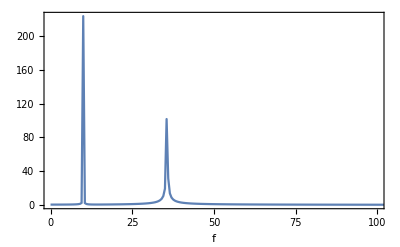

```mathematica
y=10Sin[2 π 10 t]+5Sin[2 π 35.6 t];

(*sample y*) 
T=2; f=1000;
ti = Table[i*1.,{i,0,T,1/f}];
yi = Table[y,{t,ti}];

(*transform to frequency domain*)
yf=Fourier[yi];

(*frequency-amplitude plot*)
gr=MapIndexed[{(First[#2]-1)/T,#1}&,Abs[yf]];
ListPlot[gr,Joined->True,PlotRange->{{0,100},All},Frame->True,FrameLabel->{"f",None}]
```

#### Sound analysis

```mathematica
(*generate sound in some way*)
T=3;
(*aud=AudioGenerator[Sin[2*Pi 300 #]&,T]*)(*aud=Audio[Sound[SoundNote["C4",T]]]*)
(*aud=AudioCapture[MaxDuration->T]*)
(*SetDirectory[NotebookDirectory[]]; aud=Audio["Bowl14.wav"]*)
```

```mathematica
(*analyse sound*)
dat=AudioData[aud][[1]];
T=Length[dat]/(SampleRate /. Options[aud])*1.;
α=Fourier[dat];

(*amplitude as function of frequency*)
fα=MapIndexed[{(First[#2]-1)/T,#1}&,Abs[α]];
ListPlot[fα,Joined->True,PlotRange->{{0,1200},All},Frame->True,FrameLabel->{"f [1/s]",None}]
```

## Finite Element Analysis

#### Parameters

```mathematica
val ={h->0.07,b->0.04,t->0.003,d->0.01, L->1,S->L+0.01,W->0.48,r->0.265-h/2, F->10,Ε->210 10^9,ν->0.33,G->Ε/(2+2 ν),g->9.81,rr->2t,AA->RegionMoment[Disk[{0,0},d/2],{0,0}], Iy->RegionMoment[Disk[{0,0},d/2],{0,2}],
Iz->RegionMoment[Disk[{0,0},d/2],{2,0}]};

Grid[val /.Rule->List,Alignment->Left,Spacings->{5,1.2},Frame->All]
```

#### Triangle representation

```mathematica
pnt={{0,(t-h)/2,b},{0,(t-h)/2,t/2},{0,(h-t)/2,t/2},{0,(h-t)/2,b},
{L,(t-h)/2,b},{L,(t-h)/2,t/2},{L,(h-t)/2,t/2},{L,(h-t)/2,b},
{L,(t-h)/2,b-d},{L,(h-t)/2,b-d},{L,-r,b-d}};

pol={Polygon[{4,8,10,7,3}],Polygon[{1,2,6,9,5}],Polygon[{2,3,7,6}]};

mr=MeshRegion[pnt //.val,pol];
RR=TriangulateMesh[mr,MaxCellMeasure->{"Length"->2b//.val}]
crd=Append[MeshCoordinates[RR],Last[pnt]]//.val;
nf = Length[crd];
nod=MeshCells[RR,2];
```

#### Problem description

```mathematica
(*problem description*)

ele1=Map[{SHELL,{{Ε,ν},{t}},#} &,nod];
ele2 ={
{BEAM,{{Ε,G},{AA,Iy,Iz,{0,0,1}}},Line[{10,9}]},
{BEAM,{{Ε,G},{AA,Iy,Iz,{0,0,1}}},Line[{9,nf}]},
{FORCE,{0,0,F},Point[{nf}]}};
ele=Join[ele1,ele2];

ii=1;
fun=Map[{#,{uX[ii],uY[ii],uZ[ii]},{θX[ii],θY[ii],θZ[ii++]}} &,crd];
fix=Flatten[Map[{uX[#]->0,uY[#]->0,uZ[#]->0,θX[#]->0,θY[#]->0,θZ[#]->0}&,Flatten[Position[crd,{0.,_,_}]]]];
fun = fun /. fix;

(*FORMATTED[{ele,fun}]*)

SHOW3D[{DISP,0},{ele,fun}//.val]

(*SOLVE[{ele,fun} //.val]*)
```